# DM and neutrino electron scattering in semiconductors

This notebook reproduces the calculations and analysis for the article “Nuclear and electron scattering by neutrinos and dark matter in condensed systems” arXiv:2510.06574

## 0. Definitions and setup

## Constants and functions

Fundamental constants:

```mathematica
eV=10^-9;
keV=10^-6;
MeV=10^-3;
GeV=1;
ℏcGeVfm=0.19732698;(*GeV fm*)
𝒸=2.997925 10^8;(*m/s*)
αEM=1/137.036;

kbGeVpK=8.61733×10^-14(*GeV/Kelvin*);

(*electroweak parameters*)
αem=1/137.036;
e=0.30282212;
Gf=1.1664 10^-5;(*GeV^-2*)
ssw=0.2387;
gve=2ssw+0.5;
gae=0.5;
gvμ=2ssw-0.5;
gaμ=-0.5;

(*particle masses*)
mn=0.93956542052; (*neutron mass*)
amu=mn/1.00727; (*atomic mass unit*)
mp=0.93827; (*proton mass*)
mπ=139.57MeV;(*pion mass*)
me=0.000510998; (*electron mass*)
mμ=105.66MeV;(*muon mass*)
```

```mathematica
(*Nucleon vector charges from 2011.05960 (valid for electron ν)*)
qVp=0.0747/2;
qVn=-1.0235/2;
Qw[iso_]:=(iso⟦2⟧ qVp+(iso⟦3⟧-iso⟦2⟧) qVn)^2;
```

DM astrophysical parameters (chosen to match Lin):

```mathematica
ρx=0.4GeV/Centimeter^3;
v0=220 10^3/𝒸;
vesc=500 10^3/𝒸;
Ve[V0_]={0,V0,0}+{11.1,12.2,7.3}10^3/𝒸+{29.2,-0.1,5.9}10^3/𝒸//Norm//Simplify[#,Assumptions->V0>0]&;
ve=Ve[v0];
VMAX=vesc+ve;
```

Reduced mass def:

```mathematica
μ[x_,y_]:=(x y)/(x+y)
```

```mathematica
iErf[x_,y_]:=Erfc[x]-Erfc[y]
linSpace[min_,max_,Npoints_]:=Table[x,{x,min,max,(max-min)/(Npoints-1)}]
```

Other useful units:

```mathematica
Centimeter= 1/ℏcGeVfm 10^13(*GeV^-1*);
Second= 𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19/10^-9);
KilogramDay= (1 Kilogram)(24 3600 Second);
tonneYear=KilogramDay 1000 365.25;
```

```mathematica
NotebookDirectory[]//SetDirectory;
<<"../../Codes/Migdal/Migdal.wl"
```

------------------------------------------
Migdal ionisation probabilities
P. Cox, M. Dolan, C. McCabe, H. Quiney (2022)
arXiv:2208.12222
------------------------------------------

## Target details

Target densities:

```mathematica
ρTsi=0.00233 Kilogram/Centimeter^3;
ρTge=0.005323Kilogram/Centimeter^3;
ρTgaAs=0.00532Kilogram/Centimeter^3;
```

Threshold in terms of number of electron-hole pairs

```mathematica
thresh[nEHP_,target_]:=Switch[target,
"Si",
nEHP 2.35 eV,
"Ge",
nEHP 1.8 eV]
```

Target properties:

```mathematica
geOrbits=Flatten[#]&/@Thread[{{1,keV}*#&/@$orbitals["Ge"],{2,2,3,3,2,3,3,5,5,2,1,1}}];
siOrbits=Flatten[#]&/@Thread[{{1,keV}*#&/@$orbitals["Si"],{2,2,3,3,2,1,1}}];
```

```mathematica
isotopesGe={{"ge73",32,73,1,72.63}};
isotopesSi={{"si28",14,28,1,28.085}};

isotopes[target_]:=Switch[target,
"Ge",isotopesGe,
"Si",isotopesSi];
```

```mathematica
ρT[target_]:=Switch[target,
"Si",ρTsi,
"Ge",ρTge,
"GaAs",ρTgaAs];
mT[target_]=Switch[target,
"Ge",73amu,
"Si",28amu];
NT[target_,eN_]:=
Switch[eN,
"e",
Switch[target,
"Si",(14/(28 amu)),
"Ge",(32/(73 amu)),
"GaAs",(64/(145 amu))],
"N",
Switch[target,
"Si",(1/(28 amu)),
"Ge",(1/(73 amu)),
"GaAs",(1/(145 amu))]];
A[target_]=Switch[target,
"Ge",73,
"Si",28];
Z[target_]=Switch[target,
"Ge",32,
"Si",14];
ωb[target_]=Switch[target,
"Ge",.02eV,
"Si",.03eV];
Egap[target_]:=Switch[target,
"Ge",0.67eV,
"Si",1.11eV];
ϵ[target_]:=Switch[target,
"Ge",2.9eV,
"Si",3.6eV];
Ne[Ee_?NumericQ,target_]:=1+Floor[(Ee-Egap[target])/ϵ[target]];
orbits[target_]:=Switch[target,
"Ge",geOrbits,
"Si",siOrbits];
Core[target_]:=Switch[target,"Ge",{3,2,1},"Si",{2,1}];
```

#### Quenching factors

```mathematica
kGe=0.162; (*2202.03754*)
kSi=0.146; (*2303.02196*)
kL[target_]:=Switch[StringTake[target,2],"Si",kSi,"Ge",kGe];
cz[target_]:=11.5 Z[StringTake[target,2]]^(-7/3)/keV;
ϵr[Er_,target_]:= cz[target] Er
g[ϵ_]:=3 ϵ^0.15+0.7 ϵ^0.6+ϵ;
YLind[Er_,target_]:=(kL[target] g[ϵr[Er,target]])/(1+kL[target] g[ϵr[Er,target]]);

YsiLind[Er_]=(kSi g[11.5 Er/keV 14^(-7/3)])/(1+kSi g[11.5 Er/keV 14^(-7/3)]);
(*2303.02196 empirical fit*)
YsiEm[Er_]=0.302 ((Er/eV)/10^4)^0.261;
(*Tien-Tien's*)
YgeTT[Er_]:=8.35 10^-2(Er/eV-20)^0.164
YsiTT[Er_]:=4.49 10^-3(Er/eV-20)^0.486
YsiEmCut[Er_]:=4.49 10^-3(Er/eV-20)^0.68

(*Sarkis*)
u[target_]:=Switch[target,"Si",cz[target].15keV,"Ge",cz[target].02keV];
C0[target_]:=Switch[target,"Si",9.1 10^-3,"Ge",3 10^-4];
C1[target_]:=Switch[target,"Si",3.33 10^-5,"Ge",.62 10^-5];
νbL[ϵ_,target_]:=ϵ/(1+kL[target] g[ϵ])
νb[ϵ_,target_]:=νbL[ϵ,target]+C0[target] √ϵ+C1[target]+u[target]

Ysarkis[Er_,target_]:=(ϵr[Er,target]-νb[ϵr[Er,target]-u[target],target])/ϵr[Er,target]
(*Master function*)
YQ[Er_,target_,model_:"Lindhard"]=Switch[model,
"Lindhard",YLind[Er,target],
"Sarkis",Ysarkis[Er,target],
"EmpiricalSi",If[Er>10keV,YLind[Er,target],YsiEm[Er]],
"EmpiricalSiCut",If[Er>100eV,YQ[Er,"Si","EmpiricalSi"],YsiEmCut[Er]],
"TT",
	Switch[target,
	"Ge",If[Er>3.1keV,YLind[Er,target],YgeTT[Er]],
	"Si",If[Er>3.1keV,YQ[Er,"Si","EmpiricalSi"],YsiTT[Er]]]
]//Re//# UnitStep[#]&;

altQmod[target_]:=Switch[target,"Ge","Sarkis","Si","EmpiricalSiCut"]
```

Empirical fit from: 2303.02196?

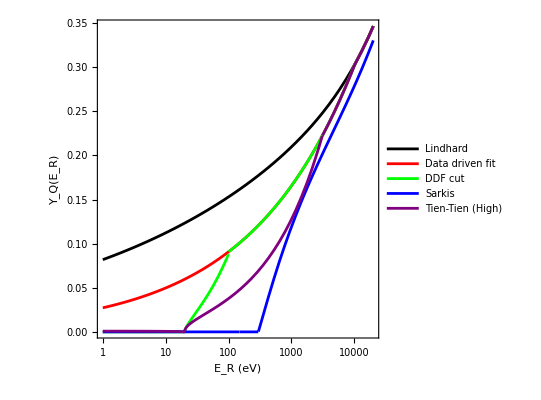
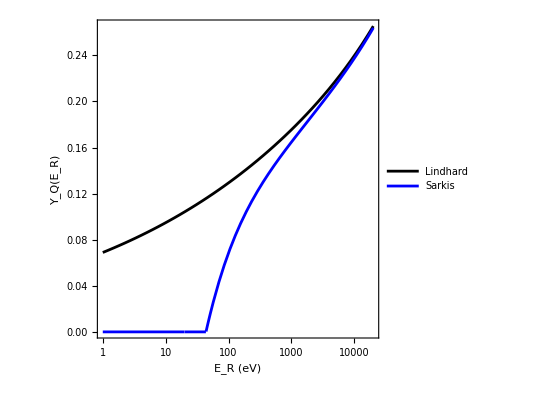

```mathematica
{LogLinearPlot[{YQ[EeV eV,"Si","Lindhard"],YQ[EeV eV,"Si","EmpiricalSi"],YQ[EeV eV,"Si","EmpiricalSiCut"],YQ[EeV eV,"Si","Sarkis"],YQ[EeV eV,"Si","TT"]},{EeV,1,2 10^4},
PlotLegends->Legend[{"Lindhard","Data driven fit","DDF cut","Sarkis","Tien-Tien (High)"},Position->{.25,.8}],
PlotStyle->{Black,Red,Green,Blue,Purple},
FrameLabel->{"E_R (eV)","Y_Q(E_R)"}],
LogLinearPlot[{YQ[EeV eV,"Ge","Lindhard"],YQ[EeV eV,"Ge","Sarkis"]},{EeV,1,2 10^4},
PlotLegends->Legend[{"Lindhard","Sarkis"},Position->{.25,.85}],
PlotStyle->{Black,Blue},
FrameLabel->{"E_R (eV)","Y_Q(E_R)"}]}
```

Plot for paper:

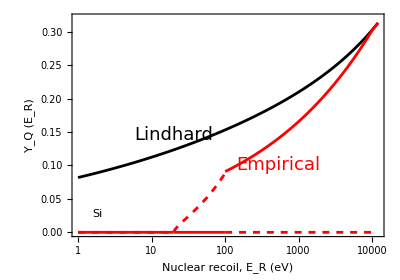
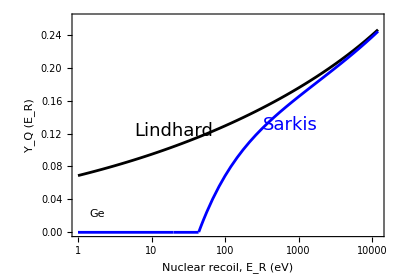

```mathematica
{quenchingPlotSi,quenchingPlotGe}={LogLinearPlot[{YQ[EeV eV,"Si","Lindhard"],YQ[EeV eV,"Si","EmpiricalSiCut"]UnitStep[100-EeV],YQ[EeV eV,"Si","EmpiricalSiCut"]UnitStep[EeV-100]},{EeV,1,1.2 10^4},
PlotStyle->{Black,{Red,Dashed},Red},PlotRange->{0,.32},AspectRatio->.7,
FrameLabel->{"Nuclear recoil, E_R (eV)","Y_Q (E_R)"},
Epilog->{Inset[Style["Lindhard",18,FontFamily->"Sans Serif"],{3,.145},Automatic,Automatic,{.45,.16}],
Inset[Style["Empirical",18,FontFamily->"Sans Serif",Red],Scaled[{.66,.32}],Automatic,Automatic,{.5,.28}],
Inset[Framed[Style["Si",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.08,.1}]]}],
LogLinearPlot[{YQ[EeV eV,"Ge","Lindhard"],YQ[EeV eV,"Ge","Sarkis"]},{EeV,1,1.2 10^4},
PlotStyle->{Black,Blue},PlotRange->{0,.26},AspectRatio->.7,
FrameLabel->{"Nuclear recoil, E_R (eV)","Y_Q (E_R)"},
Epilog->{Inset[Style["Lindhard",18,FontFamily->"Sans Serif"],{3,.123},Automatic,Automatic,{.45,.17}],
Inset[Style["Sarkis",18,FontFamily->"Sans Serif",Blue],Scaled[{.7,.5}],Automatic,Automatic,{.45,.39}],
Inset[Framed[Style["Ge",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.08,.1}]]}]}
```

```mathematica
Export["figures/fig_quenching_si.pdf",quenchingPlotSi];
Export["figures/fig_quenching_ge.pdf",quenchingPlotGe];
```

Questions: how real is the threshold for ionization with NR (sarkis)?

## The electron energy-loss function

### Build EELF from dielectric function

Obtain EELF’s from DarkELF:

```mathematica
URLDownload["https://raw.githubusercontent.com/tongylin/DarkELF/refs/heads/main/data/Ge/Ge_gpaw_withLFE.dat", FileNameJoin[{NotebookDirectory[], "data", "Ge_gpaw_withLFE.dat"}], CreateIntermediateDirectories -> True]
URLDownload["https://raw.githubusercontent.com/tongylin/DarkELF/refs/heads/main/data/Si/Si_gpaw_withLFE.dat", FileNameJoin[{NotebookDirectory[], "data", "Si_gpaw_withLFE.dat"}], CreateIntermediateDirectories -> True]
```

Use data from DarkELF computed with GPAW
columns are {ω (eV), k (eV), Re(ϵ), Im(ϵ)}

```mathematica
NotebookDirectory[]//SetDirectory;
darkELFsi=Import["data/Si_gpaw_withLFE.dat"];
darkELFge=Import["data/Ge_gpaw_withLFE.dat"];
darkELFgaAs=Import["data/GaAs_mermin.dat"];
```

Build EELF with screening:
Im(-1/ϵ) = (Im(ϵ))/ϵ^2
Build EELF without screening:
Im(ϵ)

```mathematica
darkEELFdatSi=Flatten/@({darkELFsi[[All,1;;2]],darkELFsi[[All,4]]/(darkELFsi[[All,3]]^2+darkELFsi[[All,4]]^2)}//Thread);
darkEELFdatSiNoScreening=Flatten/@({darkELFsi[[All,1;;2]],darkELFsi[[All,4]]}//Thread);
```

```mathematica
darkEELFdatGe=Flatten/@({darkELFge[[All,1;;2]],darkELFge[[All,4]]/(darkELFge[[All,3]]^2+darkELFge[[All,4]]^2)}//Thread);
darkEELFdatGeNoScreening=Flatten/@({darkELFge[[All,1;;2]],darkELFge[[All,4]]}//Thread);
```

```mathematica
darkEELFdatGaAs=Flatten/@({darkELFgaAs[[All,1;;2]],darkELFgaAs[[All,4]]/(darkELFgaAs[[All,3]]^2+darkELFgaAs[[All,4]]^2)}//Thread);
darkEELFdatGaAsNoScreening=Flatten/@({darkELFgaAs[[All,1;;2]],darkELFgaAs[[All,4]]}//Thread);
```

```mathematica
darkEELFsi=Interpolation[darkEELFdatSi];
darkEELFsiNoScreening=Interpolation[darkEELFdatSiNoScreening];
```

```mathematica
darkEELFgaAs=Interpolation[darkEELFdatGaAs];
darkEELFgaAsNoScreening=Interpolation[darkEELFdatGaAsNoScreening];
```

```mathematica
darkEELFge=Interpolation[darkEELFdatGe];
darkEELFgeNoScreening=Interpolation[darkEELFdatGeNoScreening];
```

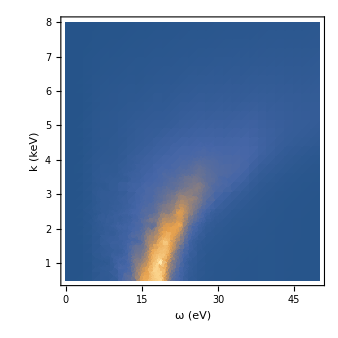
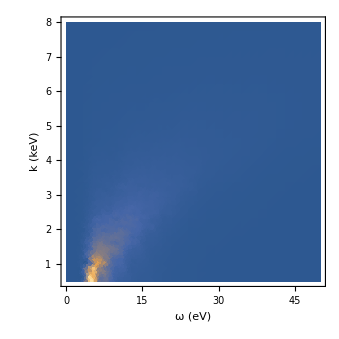

```mathematica
{DensityPlot[darkEELFsi[ω,k 10^3],{ω,0,50},{k,.5,8},PlotRange->All,PlotPoints->30,FrameLabel->{"ω (eV)","k (keV)"}],DensityPlot[darkEELFsiNoScreening[ω,k 10^3],{ω,0,50},{k,.5,8},PlotRange->All,PlotPoints->30,FrameLabel->{"ω (eV)","k (keV)"}]}
```

### Define structure function

Eq. 13 of 2101.08275:

```mathematica
fc[ω_,q_]:=darkEELFsi[ω/eV,q/eV]
```

```mathematica
β[Tkelvin_]=(kbGeVpK Tkelvin)^-1;
```

Neglect 1/(1-Exp[-ω 10^9 β[ T]]) factor because its ~1 for the relevant temperatures

```mathematica
S1::nnarg="The target `1` is not one of Si or Ge";
```

```mathematica
S1[ω_,k_,target_,screening_]:=k^2/(2π αem)Switch[target,
"Si",
If[screening==True,darkEELFsi[ω/eV,k/eV],darkEELFsiNoScreening[ω/eV,k/eV]],
"Ge",
If[screening==True,darkEELFge[ω/eV,k/eV],darkEELFgeNoScreening[ω/eV,k/eV]],
"GaAs",
If[screening==True,darkEELFgaAs[ω/eV,k/eV],darkEELFgaAsNoScreening[ω/eV,k/eV]],
_,
Message[S1::nnarg,target];];
```

## Migdal in semiconductors

### Momentum dependence of Zion

Obtain Zion’s from DarkELF:

```mathematica
URLDownload["https://raw.githubusercontent.com/tongylin/DarkELF/refs/heads/main/data/Ge/Ge_Zion.dat", FileNameJoin[{NotebookDirectory[], "data", "Ge_Zion.dat"}], CreateIntermediateDirectories -> True]
URLDownload["https://raw.githubusercontent.com/tongylin/DarkELF/refs/heads/main/data/Si/Si_Zion.dat", FileNameJoin[{NotebookDirectory[], "data", "Si_Zion.dat"}], CreateIntermediateDirectories -> True]
```

```mathematica
ZionGe=Import["data/Zion_Ge.dat"]//Drop[#,1]&//Interpolation[#,InterpolationOrder->1]&;
ZionSi=Import["data/Zion_Si.dat"]//Drop[#,1]&//Interpolation[#,InterpolationOrder->1]&;

Zion[kk_,target_]=Switch[target,
"Ge",ZionGe[kk/eV],
"Si",ZionSi[kk/eV]];
```

### DM kinematics

```mathematica
vminMig[ω_,mx_,mT_]:=√((2ω)/μ[mx,mT])
```

```mathematica
qNmax[ω_,v_,q_,mx_,mT_]=√(2mT(v q-q^2/(2mx)-ω));
qNmin[Enth_,mT_]=√(2mT Enth);
qmaxI[ω_,v_,mx_]=v mx(1+√(1-2ω/(v^2 mx)));
qminI[ω_,v_,mx_]=v mx(1-√(1-2ω/(v^2 mx)));
```

#### Core kinematics

```mathematica
ErMax[δ_?NumericQ,Vmax_?NumericQ,mX_?NumericQ,mT_?NumericQ]:=μ[mT,mX]^2/mT Vmax^2(1-δ/(μ[mT,mX] Vmax^2)+√(1-(2δ)/(μ[mT,mX] Vmax^2)))
ErMin[δ_?NumericQ,Vmax_?NumericQ,mX_?NumericQ,mT_?NumericQ]:=μ[mT,mX]^2/mT Vmax^2(1-δ/(μ[mT,mX] Vmax^2)-√(1-(2δ)/(μ[mT,mX] Vmax^2)))
```

```mathematica
ErMinDet[Edet_?NumericQ,mx_?NumericQ,mT_?NumericQ,Lq_?NumericQ]:=(mT^3 (2 mx^2 VMAX^2)-2 Edet (mT+mx)^2 (mx) (mT-(-1+Lq) (mx))+2 mT mx ((mx) (mx^2 VMAX^2)-2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2))))+mT^2 ((mx) (4 mx^2 VMAX^2)-2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2))))+2 mx^2 (-√(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2)))))/(2 (mT+mx)^2 (mT-(-1+Lq) (mx))^2)//Abs
```

```mathematica
ErMaxDet[Edet_?NumericQ,mx_?NumericQ,mT_?NumericQ,Lq_?NumericQ]:=(mT^3 (2 mx^2 VMAX^2)-2 Edet (mT+mx)^2 (mx) (mT-(-1+Lq) (mx))+2 mx^2 (√(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2))))+2 mT mx ((mx) (mx^2 VMAX^2)+2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2))))+mT^2 ((mx) (4 mx^2 VMAX^2)+2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx) (mT+mx)^2 ((mT+mx)^2 (-2 Edet (mT+mx-Lq mx)+mT mx VMAX^2)))))/(2 (mT+mx)^2 (mT-(-1+Lq) (mx))^2)
```

```mathematica
EdetMax[mx_?NumericQ,mT_?NumericQ,Lq_?NumericQ]:=(mT mx VMAX^2)/(2(mT-(-1+Lq)mx))
```

### Shake-off probabilities

#### Valence probabilities

```mathematica
dPdω[ω_,Er_,target_,screening_:True]:=
NIntegrate[(4 αem^2 Zion[kk,target]^2((2Er)/mT[target]))/(3π ω^4)S1[ω,kk,target,screening],{kk,10eV,20keV},PrecisionGoal->3]//Quiet;
```

Tabulate for speed:

```mathematica
dpdωGe=ParallelTable[{ω,dPdω[ω,1,"Ge"]},{ω,logSpace[1eV,80eV,100]}]//Interpolation[#,InterpolationOrder->1]&;
dpdωSi=ParallelTable[{ω,dPdω[ω,1,"Si"]},{ω,logSpace[1eV,80eV,100]}]//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
dpdωFast[ω_,target_]:=Switch[target,
"Ge",dpdωGe[ω],
"Si",dpdωSi[ω]];
```

#### Core Ionization probabilities (free atom approx)

```mathematica
LoadProbabilities["Ge",DarkMatter->True,Double->False,InterpolationOrder->1];
dpI1Ge=dpI1;
LoadProbabilities["Si",DarkMatter->True,Double->False,InterpolationOrder->1];
dpI1Si=dpI1;

Znl[target_?StringQ,orbit_?StringQ,Ee_?NumericQ,v_?NumericQ]:=Switch[target,
"Ge",1/keV dpI1Ge[orbit][Log[Ee/keV],Log[v]],
"Si",1/keV dpI1Si[orbit][Log[Ee/keV],Log[v]]]
```

Loading differential probabilities for Ge...done.

Loading differential probabilities for Si...done.

## Neutrino sources

### Solar fluxes

Flux normalizations (high-Z SSM 1208.5723):

```mathematica
ppFluxNorm=5.98 10^10/(Centimeter^2 Second);
be7FluxNorm=5. 10^9/(Centimeter^2 Second);
b8FluxNorm=5.58 10^6/(Centimeter^2 Second);
o15FluxNorm=2.23 10^8/(Centimeter^2 Second);
n13FluxNorm=2.96 10^8/(Centimeter^2 Second);
pepFluxNorm=1.44 10^8/(Centimeter^2 Second);
```

```mathematica
(*ppFlux,be7Flux,pepFlux,o15Flux+n13Flux,b8Flux*)
nuFluxUn={.006,.06,.01,.16,.12};
```

Import spectra:

```mathematica
ppFluxDat=Import["data/pp_flux.dat"];
b8FluxDat=Import["data/8B_flux.dat"];
n13FluxDat=Import["data/N_flux.dat"];
o15FluxDat=Import["data/O_flux.dat"];
```

Convert to GeV and create interpolated functions:

```mathematica
ppFluxDat[[All,1]]*=10^-3;
ppFluxDat[[All,2]]*=ppFluxNorm 10^3;
ppSpec=ppFluxDat//Interpolation[#,InterpolationOrder->1]&;

b8FluxDat[[All,1]]*=10^-3;
b8FluxDat[[All,2]]*=b8FluxNorm 10^3;
b8Spec=b8FluxDat//Interpolation[#,InterpolationOrder->1]&;

n13FluxDat[[All,1]]*=10^-3;
n13FluxDat[[All,2]]*=n13FluxNorm 10^3;
n13Spec=n13FluxDat//Interpolation[#,InterpolationOrder->1]&;

o15FluxDat[[All,1]]*=10^-3;
o15FluxDat[[All,2]]*=o15FluxNorm 10^3;
o15Spec=o15FluxDat//Interpolation[#,InterpolationOrder->1]&;
```

Line energies:

```mathematica
Ebe7i=862keV;
Ebe7ii=384keV;
```

```mathematica
Epep=1.439MeV;
```

Survival probability for electron neutrinos (1901.09965)

```mathematica
survProbPP=0.553;
survProbBe7=0.54;
survProbPeP=0.5;
survProbB8=0.34;
```

Define flux objects:

```mathematica
ppFlux={"Spectrum",ppSpec,survProbPP,ppFluxDat[[-1,1]]};
b8Flux={"Spectrum",b8Spec,survProbB8,b8FluxDat[[-1,1]]};
o15Flux={"Spectrum",o15Spec,survProbPeP,o15FluxDat[[-1,1]]};
n13Flux={"Spectrum",n13Spec,survProbPeP,n13FluxDat[[-1,1]]};

pepFlux={"Line",{pepFluxNorm},{Epep},{survProbPeP},Epep};
be7Flux={"Line",{0.9be7FluxNorm,0.1be7FluxNorm},{Ebe7i,Ebe7ii},{survProbBe7,survProbPeP},Ebe7i};
```

## Neutrino rates

### Kinematics

Elastic:

```mathematica
TMIN[TT_?NumericQ,mi_?NumericQ,mT_?NumericQ]:=If[TT<2mi,
(TT/2-mi)(1-√(1+(2TT(mi+mT)^2)/(mT(2mi-TT)^2))),
(TT/2-mi)(1+√(1+(2TT(mi+mT)^2)/(mT(2mi-TT)^2)))];
```

```mathematica
TMAX[Ti_?NumericQ,mi_?NumericQ,mT_?NumericQ]:=(Ti^2+2mi Ti)/(Ti+(mi+mT)^2/(2 mT));
```

Inelastic:

```mathematica
ω==EnuInitial-EnuFinal;
ω==Enu-√(Enu^2+q^2-2Enu q Cosθ)//Solve[#,Enu]&
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{Enu→(q^2-ω^2)/(2 (Cosθ q-ω))}}

```mathematica
EnuMin[q_,ω_]:=(q+ω)/2
```

```mathematica
ω==Enu-√(Enu^2+q^2-2Enu q Cosθ)//Solve[#,q]&
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{q→Cosθ Enu-√(Cosθ^2 Enu^2-2 Enu ω+ω^2)},{q→Cosθ Enu+√(Cosθ^2 Enu^2-2 Enu ω+ω^2)}}

Cos(θ):

```mathematica
csSol=Solve[ω==Enu-√(Enu^2+q^2-2Enu q Cosθ),Cosθ]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{Cosθ→(q^2+2 Enu ω-ω^2)/(2 Enu q)}}

```mathematica
Solve[q^2==Enu^2+(Enu-ω)^2-2Enu (Enu-ω) Cosϕ,ω]
```

{{ω→Enu-Cosϕ Enu-√(-Enu^2+Cosϕ^2 Enu^2+q^2)},{ω→Enu-Cosϕ Enu+√(-Enu^2+Cosϕ^2 Enu^2+q^2)}}

```mathematica
csϕSol=Solve[q^2==Enu^2+(Enu-ω)^2-2Enu (Enu-ω) Cosϕ,Cosϕ]
```

{{Cosϕ→(2 Enu^2-q^2-2 Enu ω+ω^2)/(2 Enu (Enu-ω))}}

```mathematica
Enu-Cosϕ Enu-√(-Enu^2+Cosϕ^2 Enu^2+q^2)==Enu-√(Enu^2+q^2-2Enu q Cosθ)//Solve[#,Cosθ]&//FullSimplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{Cosθ→(Enu-Cosϕ^2 Enu-Cosϕ √((-1+Cosϕ^2) Enu^2+q^2))/q}}

```mathematica
Enu-Cosϕ Enu-√(-Enu^2+Cosϕ^2 Enu^2+q^2)==Enu-√(Enu^2+q^2-2Enu q Cosθ)//Solve[#,Cosθ]&//D[Cosθ/.#,Cosϕ]&//FullSimplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{-((Cosϕ Enu+√((-1+Cosϕ^2) Enu^2+q^2))^2)/(q √((-1+Cosϕ^2) Enu^2+q^2))}

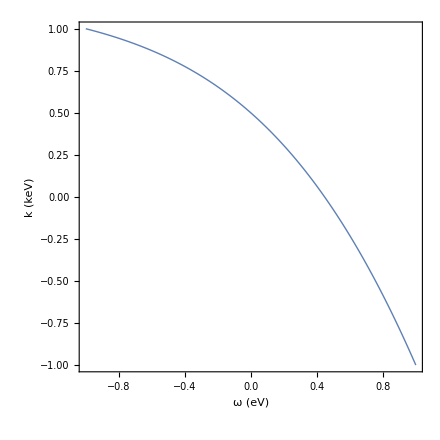

```mathematica
With[{Enu=.01MeV,q=20keV},
Plot[(Enu-Cosϕ^2 Enu-Cosϕ √((-1+Cosϕ^2) Enu^2+q^2))/q,{Cosϕ,-1,1},PlotRange->All,
FrameLabel->{"ω (eV)","k (keV)"},PlotRange->All,PlotPoints->100]]
```

```mathematica
dp=DensityPlot[darkEELFsi[ω,k 10^3],{ω,0,90},{k,0,12},PlotRange->All,PlotRange->{{0,90},{0,12}},
FrameLabel->{"ω (eV)","k (keV)"},PlotRange->All,PlotPoints->100,ColorFunction->(Opacity[#1,Darker[Blue]]&)]
```

-Graphics-

```mathematica
Manipulate[With[{Enu=.01MeV},Show[
Plot[{(Cosθ Enu-√(Cosθ^2 Enu^2-2 Enu ω eV+(ω eV)^2))/keV,(Cosθ Enu+√(Cosθ^2 Enu^2-2 Enu ω eV+(ω eV)^2))/keV},{ω,0,Enu/eV},PlotStyle->Red,Filling->1->{2},PlotRange->{{0,Enu/eV},{0,2Enu/keV}}]]],{Cosθ,0,1}]
```

Plot::plln: Limiting value (0.01 MeV)/eV in {ω,0,(0.01 MeV)/eV} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value (0.01 MeV)/eV in {ω,0,(0.01 MeV)/eV} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

0.01 MeV           0.01 MeV
Plot::plln: Limiting value -------- in {ω, 0, --------}
                              eV                 eV
     is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

0.01 MeV           0.01 MeV
Plot::plln: Limiting value -------- in {ω, 0, --------}
                              eV                 eV
     is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

0.01 MeV           0.01 MeV
Plot::plln: Limiting value -------- in {ω, 0, --------}
                              eV                 eV
     is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

```mathematica
With[{Enu=2MeV,Cosθ=.1},Show[DensityPlot[darkEELFsi[ω,k 10^3],{ω,0,90},{k,0,12},PlotRange->All,PlotRange->{{0,90},{0,12}},
FrameLabel->{"ω (eV)","k (keV)"},FrameStyle->Directive[Black,FontFamily->"Times",18],PlotRange->All,PlotPoints->100,ColorFunction->(Opacity[#1,Darker[Blue]]&)],Plot[{√(2me ω eV)/keV,√(2me (ω-17) eV)/keV},{ω,0,89},PlotStyle->{Black,{Black,Dashed}},PlotRange->{{0,90},{0,12}}],
Plot[{(Enu-√(Enu^2-2 Enu ω eV+(ω eV)^2))/keV,(0+√(-2 Enu ω eV+(ω eV)^2))/keV},{ω,0,89},PlotStyle->Red,Filling->1->{2},PlotRange->{{0,90},{0,12}}]]]
```

-Graphics-

```mathematica
With[{Enu=1MeV},Manipulate[
Plot[{(Cosθ Enu-√(Cosθ^2 Enu^2-2 Enu ω eV+(ω eV)^2))/eV,(Cosθ Enu+√(Cosθ^2 Enu^2-2 Enu ω eV+(ω eV)^2))/eV},{ω,0,100},PlotStyle->Red,Filling->1->{2},PlotRange->{0,100}],{Cosθ,0,1}]]
```

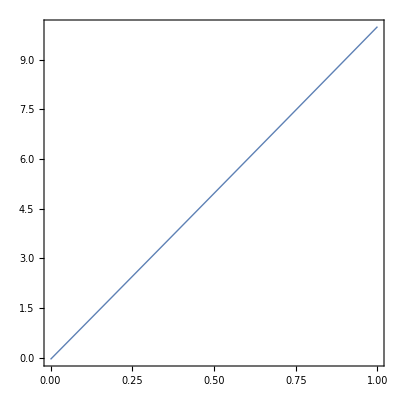

```mathematica
With[{Enu=1MeV,k=10keV},
Plot[{(Enu-√(Enu^2+k^2-2Enu k Cosθ))/keV},{Cosθ,0,1}]]
```

### Core ν-e rate

Ignoring electron shells the cross section is:

```mathematica
dσedEr//Clear;
dσedEr[Er_,Enu_,gv_,ga_,mT_]:=(Gf^2 mT)/(2π)((gv+ga)^2+(gv-ga)^2(1-Er/Enu)^2-(gv^2-ga^2)(mT Er)/Enu^2)
```

Rates for elastic scattering of solar neutrinos from electrons:

```mathematica
stepFactor[Er_,target_,stepping_,coreOnly_]:=If[stepping,Sum[orbit[[3]]/Z[target] HeavisideTheta[Er-orbit[[2]]],{orbit,Select[orbits[target],(StringContainsQ[#[[1]],ToString/@Core[target]])&]}],1];
dRνeSdE[Er_,target_,flux_,survProb_,stepping_:True,coreOnly_:True]:=NT[target,"e"]stepFactor[Er,target,stepping,coreOnly] NIntegrate[
flux[Enu](survProb dσedEr[Er,Enu,gve,gae,me]+(1-survProb)dσedEr[Er,Enu,gvμ,gaμ,me]),
{Enu,Min[Max[TMIN[Er,0,me],flux[[1,-1,1]]],flux[[1,-1,2]]],flux[[1,-1,2]]},PrecisionGoal->3]

dRνeLdE[Er_,target_,fluxNorm_,fluxE_,survProb_,stepping_:True,coreOnly_:True]:=NT[target,"e"]stepFactor[Er,target,stepping,coreOnly]fluxNorm(survProb dσedEr[Er,fluxE,gve,gae,me]+(1-survProb)dσedEr[Er,fluxE,gvμ,gaμ,me])HeavisideTheta[fluxE-TMIN[Er,0,me]]

dRνedE[Er_,target_,fluxOb_,stepping_:True]:=Switch[fluxOb[[1]],
"Line",Sum[dRνeLdE[Er,target,fluxOb[[2,fluxi]],fluxOb[[3,fluxi]],fluxOb[[4,fluxi]],stepping],{fluxi,1,Length[fluxOb[[2]]]}],
"Spectrum",dRνeSdE[Er,target,fluxOb[[2]],fluxOb[[3]],stepping]]
```

Estimate of the thermal neutrino rate (alla 1708.02248)

```mathematica
dRtdE[Er_,target_]:=NT[target] NIntegrate[
10^6/(Centimeter^2 Second) dσdE[Er,Enu,gve,gae],
{Enu,Min[TMIN[Er,0,me],10keV],10keV}]
```

Calculate:

```mathematica
{νERatesGe,νERatesSi}=ParallelTable[{er/eV,dRνedE[er,target,flux,True](KilogramDay  365eV)},
{target,{"Ge","Si"}},{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux,b8Flux}},{er,logSpace[orbits[target][[-4,2]],TMAX[flux[[-1]],0,me],200]},Method->"CoarsestGrained"];
 (*pad with zeros to stop extrapolation*)
Do[νERatesGe[[ii]]=Join[νERatesGe[[ii]],{{1.01νERatesGe[[ii,-1,1]],10^-99},{10^7,0}}];
νERatesSi[[ii]]=Join[νERatesSi[[ii]],{{1.01νERatesSi[[ii,-1,1]],10^-99},{10^7,0}}];,{ii,1,Length[νERatesGe]}]
```

```mathematica
Export["results/rates/rate_solarNuE_core_Ge.h5",νERatesGe];
Export["results/rates/rate_solarNuE_core_Si.h5",νERatesSi];
```

```mathematica
νERatesGe=Import["results/rates/rate_solarNuE_core_Ge.h5","/Dataset1"];
νERatesSi=Import["results/rates/rate_solarNuE_core_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
νEtotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@νERatesGe));
νEtotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@νERatesSi));
```

```mathematica
tRateEdatGe=ParallelTable[{er/eV,dRtdE[er,"Ge"](KilogramDay  365eV)},{er,logSpace[1eV,20keV,200]}];
tRateEdatSi=ParallelTable[{er/eV,dRtdE[er,"Si"](KilogramDay  365eV)},{er,logSpace[1eV,20keV,200]}];
```

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.0597×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.90973×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.9948×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.64707×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.67136×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[6.96491×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.33748×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.0597×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.90973×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.9948×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.64707×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.67136×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[6.96491×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.33748×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.05103×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.18731×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.00717×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{7.17128×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.83316×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.91551×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[7.3203×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.37127×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.33011×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.85015×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.54015×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.5603×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.33011×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.85015×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.54015×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.5603×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.39798×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.89693×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.66976×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.62513×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[4.851×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.54489×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[9.26409×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{4.9117×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[4.851×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.54489×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[9.26409×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{4.9117×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[5.09852×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.63484×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[9.73679×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.03666×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.76919×10^-7,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.81234×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.85946×10^-7,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.9863×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.21465×10^-7,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.22495×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.37867×10^-7,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.4616×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.0597×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.05103×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.18731×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.10465×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.31815×10^-7,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.0597×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.90973×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.9948×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.64707×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.67136×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[6.96491×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.33748×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.0597×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.90973×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{6.9948×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.64707×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.67136×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[6.96491×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.33748×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.05103×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{5.18731×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.00717×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{7.17128×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[3.83316×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{9.91551×10^-7,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[7.3203×10^-9,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.37127×10^-6,1/100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[1.33011×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.85015×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[2.54015×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.5603×10^-6,1/100000}}.

NIntegrate::inumr: The integrand 2.56294×10^-46 dσdE[4.851×10^-8,Enu,0.9774,0.5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{3.54489×10^-6,1/100000}}.

$Aborted

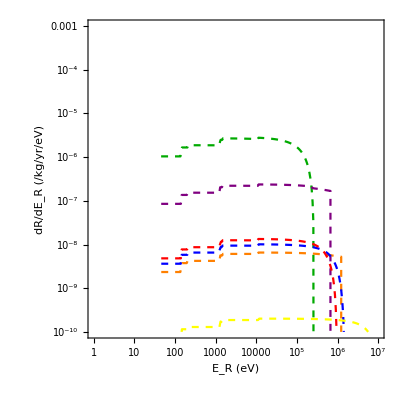
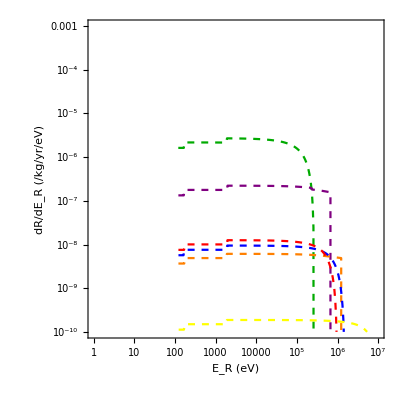

```mathematica
{enuPlotGe,enuPlotSi}={ListLogLogPlot[νERatesGe,
FrameLabel->{"E_R (eV)","dR/dE_R (/kg/yr/eV)"},
PlotStyle->{{Green//Darker,Dashed},{Purple,Dashed},{Orange,Dashed},{Blue,Dashed},{Red,Dashed},{Yellow,Dashed}},
PlotRange->{{1,10^7},{10^-10,.001}},
FrameTicks->{LogTicks[10^-16,10^4],LogTicks[10^-8,10^6]},Joined->True],
ListLogLogPlot[νERatesSi,
PlotStyle->{{Green//Darker,Dashed},{Purple,Dashed},{Orange,Dashed},{Blue,Dashed},{Red,Dashed},{Yellow,Dashed}},
PlotRange->{{1,10^7},{10^-10,.001}},
FrameLabel->{"E_R (eV)","dR/dE_R (/kg/yr/eV)"},
FrameTicks->{LogTicks[10^-16,10^4],LogTicks[1,10^6]},Joined->True]}
```

RRPA analysis in https://journals.aps.org/prd/abstract/10.1103/PhysRevD.91.013005 shows free electron approx (with stepping) is not terrible down to 1keV

### Valence ν-e rate

```mathematica
ourS1onV[ω_,k_,target_,screening_]:=1/(8 π^2)S1[ω,k,target,screening];
```

Cross section:

```mathematica
dσedEr[Er_,Enu_,gv_,ga_,mT_]:=(Gf^2 mT)/(2π)((gv+ga)^2+(gv-ga)^2(1-Er/Enu)^2-(gv^2-ga^2)(mT Er)/Enu^2)
```

```mathematica
dσeVdω[Enu_,ω_,kk_,gv_,target_,screening_:True]:=(8 Gf^2)/π gv^2(1-(kk^2+2Enu ω)/(4 Enu^2))ourS1onV[ω,kk,target,screening]

dRνSdω[ω_?NumericQ,target_,flux_,survProb_,screening_:True]:=1/ρT[target] NIntegrate[kk
flux[Enu](survProb dσeVdω[Enu,ω,kk,gve,target,screening]+(1-survProb)dσeVdω[Enu,ω,kk,gvμ,target,screening]),
{kk, ω, 20 keV},{Enu,EnuMin[kk,ω],flux[[1,1,2]]},PrecisionGoal->2]

dRνLdω[ω_?NumericQ,target_,fluxNorm_,fluxE_,survProb_,screening_:True]:=1/ρT[target] NIntegrate[kk
fluxNorm UnitStep[fluxE-EnuMin[kk,ω]](survProb dσeVdω[fluxE,ω,kk,gve,target,screening]+(1-survProb)dσeVdω[fluxE,ω,kk,gvμ,target,screening]),
{kk, ω, 20 keV},PrecisionGoal->2]

dRνdω[ω_?NumericQ,target_,fluxOb_,screening_:True]:=Switch[fluxOb[[1]],
"Spectrum",dRνSdω[ω,target,fluxOb[[2]],fluxOb[[3]],screening],
"Line",Sum[dRνLdω[ω,target,fluxOb[[2,fluxi]],fluxOb[[3,fluxi]],fluxOb[[4,fluxi]],screening],{fluxi,1,Length[fluxOb[[2]]]}]]
```

```mathematica
dσνDFTdEr[Enu_,ω_,kk_,gv_,target_,screening_:True]:=(4 Gf^2)/(2π)^2 gv^2(1-(kk^2+2Enu ω)/(4 Enu^2))S1[ω,kk,target,screening]
```

```mathematica
dRνSdω[ω_?NumericQ,target_,flux_,survProb_,screening_:True]:=1/ρT[target] NIntegrate[kk/(2π)
flux[Enu](survProb dσνDFTdEr[Enu,ω,kk,gve,target,screening]+(1-survProb)dσνDFTdEr[Enu,ω,kk,gvμ,target,screening]),
{kk, ω, 20 keV},{Enu,EnuMin[kk,ω],flux[[1,1,2]]},PrecisionGoal->2]

dRνLdω[ω_?NumericQ,target_,fluxNorm_,fluxE_,survProb_,screening_:True]:=1/ρT[target] NIntegrate[kk/(2π)
fluxNorm UnitStep[fluxE-EnuMin[kk,ω]](survProb dσνDFTdEr[fluxE,ω,kk,gve,target,screening]+(1-survProb)dσνDFTdEr[fluxE,ω,kk,gvμ,target,screening]),
{kk, ω, 20 keV},PrecisionGoal->2]

dRνedω[ω_?NumericQ,target_,fluxOb_,screening_:True]:=Switch[fluxOb[[1]],
"Spectrum",dRνSdω[ω,target,fluxOb[[2]],fluxOb[[3]],screening],
"Line",Sum[dRνLdω[ω,target,fluxOb[[2,fluxi]],fluxOb[[3,fluxi]],fluxOb[[4,fluxi]],screening],{fluxi,1,Length[fluxOb[[2]]]}]]
```

Using Eq 59 without going via a cross section:

```mathematica
dRppνdωAlt[ω_?NumericQ,target_,screening_:True,mass_:(1GeV)]:= 1/ρT[target] NIntegrate[k/(2π)
ppSpec[Enu](8 Gf^2(1-(k^2+2Enu ω)/(4 Enu^2))ourS1onV[ω,k,target,screening])(survProbPP gve^2+(1-survProbPP)gvμ^2),
{k, ω, 20 keV},{Enu,EnuMin[k,ω],ppFlux[[-1]]},PrecisionGoal->2]
```

```mathematica
{νEdftRatesSi,νEdftRatesSiOurs}={ParallelTable[{er/eV,dRνdω[er,"Si",ppFlux](KilogramDay  365eV)},{er,logSpace[1eV,80eV,200]}],
ParallelTable[{er/eV,dRνedω[er,"Si",ppFlux](KilogramDay  365eV)},{er,logSpace[1eV,80eV,200]}]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{1.,4.09559×10^-12},{1.02226,5.59629×10^-12},{1.04502,8.17439×10^-12},{1.06829,1.23472×10^-11},{1.09208,1.74339×10^-11},{1.11639,2.27626×10^-11},{1.14125,2.85584×10^-11},{1.16666,3.47081×10^-11},{1.19263,4.08471×10^-11},{1.21918,4.77301×10^-11},{1.24633,5.45805×10^-11},{1.27408,5.92346×10^-11},{1.30244,6.08509×10^-11},{1.33144,6.28389×10^-11},{1.36109,6.54328×10^-11},{1.39139,6.94003×10^-11},{1.42237,7.5621×10^-11},{1.45404,8.44589×10^-11},{1.48641,9.66799×10^-11},{1.5195,1.23995×10^-10},{1.55334,1.55317×10^-10},{1.58792,1.89961×10^-10},{1.62327,2.27313×10^-10},{1.65942,2.66416×10^-10},{1.69636,3.06253×10^-10},{1.73413,3.34252×10^-10},{1.77274,3.52635×10^-10},{1.81221,3.73349×10^-10},{1.85256,3.9898×10^-10},{1.8938,4.32787×10^-10},{1.93597,4.78211×10^-10},{1.97907,5.67232×10^-10},{2.02313,6.79404×10^-10},{2.06818,8.03705×10^-10},{2.11422,9.36364×10^-10},{2.1613,1.06977×10^-9},{2.20942,1.14784×10^-9},{2.25861,1.23731×10^-9},{2.30889,1.31847×10^-9},{2.3603,1.41945×10^-9},{2.41285,1.56429×10^-9},{2.46657,1.82033×10^-9},{2.52149,2.14271×10^-9},{2.57763,2.49498×10^-9},{2.63502,2.85755×10^-9},{2.69369,3.15463×10^-9},{2.75366,3.39199×10^-9},{2.81497,3.64382×10^-9},{2.87764,3.94344×10^-9},{2.94171,4.32377×10^-9},{3.00721,5.10549×10^-9},{3.07416,5.86412×10^-9},{3.14261,6.74049×10^-9},{3.21257,7.26105×10^-9},{3.2841,7.81019×10^-9},{3.35722,8.4148×10^-9},{3.43197,9.08224×10^-9},{3.50838,1.00657×10^-8},{3.58649,1.11766×10^-8},{3.66634,1.23418×10^-8},{3.74797,1.34827×10^-8},{3.83142,1.46279×10^-8},{3.91672,1.59157×10^-8},{4.00392,1.6941×10^-8},{4.09307,1.80829×10^-8},{4.1842,1.92035×10^-8},{4.27736,2.06158×10^-8},{4.37259,2.20467×10^-8},{4.46994,2.34355×10^-8},{4.56947,2.50335×10^-8},{4.6712,2.6621×10^-8},{4.7752,2.86875×10^-8},{4.88152,3.03021×10^-8},{4.99021,3.24984×10^-8},{5.10131,3.49188×10^-8},{5.21489,3.64039×10^-8},{5.33099,3.817×10^-8},{5.44969,3.98435×10^-8},{5.57102,4.16521×10^-8},{5.69506,4.27293×10^-8},{5.82185,4.50849×10^-8},{5.95147,4.76385×10^-8},{6.08398,4.78292×10^-8},{6.21944,4.73259×10^-8},{6.35791,4.79378×10^-8},{6.49947,4.99495×10^-8},{6.64417,5.21168×10^-8},{6.7921,5.29401×10^-8},{6.94332,5.35956×10^-8},{7.09791,5.48282×10^-8},{7.25594,5.61047×10^-8},{7.41749,5.71635×10^-8},{7.58264,5.55195×10^-8},{7.75146,5.61307×10^-8},{7.92405,5.75074×10^-8},{8.10047,5.79895×10^-8},{8.28082,5.81605×10^-8},{8.46519,5.88827×10^-8},{8.65367,6.05775×10^-8},{8.84633,6.12779×10^-8},{9.04329,6.19791×10^-8},{9.24464,6.5227×10^-8},{9.45046,6.91938×10^-8},{9.66087,7.21819×10^-8},{9.87597,7.35658×10^-8},{10.0959,7.22835×10^-8},{10.3206,7.16816×10^-8},{10.5504,7.62145×10^-8},{10.7853,7.99702×10^-8},{11.0254,8.22046×10^-8},{11.2709,8.16408×10^-8},{11.5219,8.5264×10^-8},{11.7784,8.82218×10^-8},{12.0406,9.09812×10^-8},{12.3087,9.48179×10^-8},{12.5828,9.34148×10^-8},{12.8629,9.83712×10^-8},{13.1493,1.00432×10^-7},{13.442,1.02797×10^-7},{13.7413,1.05591×10^-7},{14.0473,1.09299×10^-7},{14.36,1.14957×10^-7},{14.6797,1.203×10^-7},{15.0066,1.2288×10^-7},{15.3407,1.23913×10^-7},{15.6822,1.26361×10^-7},{16.0314,1.30301×10^-7},{16.3883,1.32744×10^-7},{16.7532,1.39694×10^-7},{17.1262,1.47955×10^-7},{17.5075,1.48102×10^-7},{17.8973,1.51969×10^-7},{18.2958,1.56945×10^-7},{18.7031,1.62397×10^-7},{19.1196,1.71667×10^-7},{19.5452,1.74816×10^-7},{19.9804,1.78323×10^-7},{20.4253,1.82162×10^-7},{20.88,1.86489×10^-7},{21.3449,1.97481×10^-7},{21.8201,2.07021×10^-7},{22.3059,2.15577×10^-7},{22.8026,2.14911×10^-7},{23.3103,2.13168×10^-7},{23.8292,2.13438×10^-7},{24.3598,2.17758×10^-7},{24.9022,2.26338×10^-7},{25.4566,2.32547×10^-7},{26.0234,2.32365×10^-7},{26.6028,2.2737×10^-7},{27.1951,2.18019×10^-7},{27.8005,2.16408×10^-7},{28.4195,2.15654×10^-7},{29.0522,2.22133×10^-7},{29.6991,2.22683×10^-7},{30.3603,2.19296×10^-7},{31.0363,2.22932×10^-7},{31.7273,2.27838×10^-7},{32.4337,2.32153×10^-7},{33.1558,2.32848×10^-7},{33.894,2.31972×10^-7},{34.6486,2.34651×10^-7},{35.42,2.40214×10^-7},{36.2087,2.37418×10^-7},{37.0148,2.31713×10^-7},{37.8389,2.26546×10^-7},{38.6814,2.24903×10^-7},{39.5426,2.27863×10^-7},{40.423,2.27907×10^-7},{41.323,2.23265×10^-7},{42.243,2.20824×10^-7},{43.1836,2.1833×10^-7},{44.145,2.16706×10^-7},{45.1279,2.15323×10^-7},{46.1326,2.18995×10^-7},{47.1598,2.22721×10^-7},{48.2097,2.22596×10^-7},{49.2831,2.22143×10^-7},{50.3804,2.27512×10^-7},{51.5021,2.31538×10^-7},{52.6487,2.30643×10^-7},{53.8209,2.22623×10^-7},{55.0192,2.13834×10^-7},{56.2442,2.12756×10^-7},{57.4964,2.19608×10^-7},{58.7766,2.25019×10^-7},{60.0852,2.29379×10^-7},{61.423,2.28495×10^-7},{62.7905,2.31092×10^-7},{64.1885,2.41486×10^-7},{65.6176,2.47086×10^-7},{67.0786,2.48491×10^-7},{68.572,2.52898×10^-7},{70.0988,2.54496×10^-7},{71.6595,2.46559×10^-7},{73.2549,2.26712×10^-7},{74.8859,1.91564×10^-7},{76.5532,1.44171×10^-7},{78.2576,9.83721×10^-8},{80.,5.5953×10^-8}},{{1.,4.09559×10^-12},{1.02226,5.59629×10^-12},{1.04502,8.17439×10^-12},{1.06829,1.23472×10^-11},{1.09208,1.74339×10^-11},{1.11639,2.27626×10^-11},{1.14125,2.85584×10^-11},{1.16666,3.47081×10^-11},{1.19263,4.08471×10^-11},{1.21918,4.77301×10^-11},{1.24633,5.45805×10^-11},{1.27408,5.92346×10^-11},{1.30244,6.08509×10^-11},{1.33144,6.28389×10^-11},{1.36109,6.54328×10^-11},{1.39139,6.94003×10^-11},{1.42237,7.5621×10^-11},{1.45404,8.44589×10^-11},{1.48641,9.66799×10^-11},{1.5195,1.23995×10^-10},{1.55334,1.55317×10^-10},{1.58792,1.89961×10^-10},{1.62327,2.27313×10^-10},{1.65942,2.66416×10^-10},{1.69636,3.06253×10^-10},{1.73413,3.34252×10^-10},{1.77274,3.52635×10^-10},{1.81221,3.73349×10^-10},{1.85256,3.9898×10^-10},{1.8938,4.32787×10^-10},{1.93597,4.78211×10^-10},{1.97907,5.67232×10^-10},{2.02313,6.79404×10^-10},{2.06818,8.03705×10^-10},{2.11422,9.36364×10^-10},{2.1613,1.06977×10^-9},{2.20942,1.14784×10^-9},{2.25861,1.23731×10^-9},{2.30889,1.31847×10^-9},{2.3603,1.41945×10^-9},{2.41285,1.56429×10^-9},{2.46657,1.82033×10^-9},{2.52149,2.14271×10^-9},{2.57763,2.49498×10^-9},{2.63502,2.85755×10^-9},{2.69369,3.15463×10^-9},{2.75366,3.39199×10^-9},{2.81497,3.64382×10^-9},{2.87764,3.94344×10^-9},{2.94171,4.32377×10^-9},{3.00721,5.10549×10^-9},{3.07416,5.86412×10^-9},{3.14261,6.74049×10^-9},{3.21257,7.26105×10^-9},{3.2841,7.81019×10^-9},{3.35722,8.4148×10^-9},{3.43197,9.08224×10^-9},{3.50838,1.00657×10^-8},{3.58649,1.11766×10^-8},{3.66634,1.23418×10^-8},{3.74797,1.34827×10^-8},{3.83142,1.46279×10^-8},{3.91672,1.59157×10^-8},{4.00392,1.6941×10^-8},{4.09307,1.80829×10^-8},{4.1842,1.92035×10^-8},{4.27736,2.06158×10^-8},{4.37259,2.20467×10^-8},{4.46994,2.34355×10^-8},{4.56947,2.50335×10^-8},{4.6712,2.6621×10^-8},{4.7752,2.86875×10^-8},{4.88152,3.03021×10^-8},{4.99021,3.24984×10^-8},{5.10131,3.49188×10^-8},{5.21489,3.64039×10^-8},{5.33099,3.817×10^-8},{5.44969,3.98435×10^-8},{5.57102,4.16521×10^-8},{5.69506,4.27293×10^-8},{5.82185,4.50849×10^-8},{5.95147,4.76385×10^-8},{6.08398,4.78292×10^-8},{6.21944,4.73259×10^-8},{6.35791,4.79378×10^-8},{6.49947,4.99495×10^-8},{6.64417,5.21168×10^-8},{6.7921,5.29401×10^-8},{6.94332,5.35956×10^-8},{7.09791,5.48282×10^-8},{7.25594,5.61047×10^-8},{7.41749,5.71635×10^-8},{7.58264,5.55195×10^-8},{7.75146,5.61307×10^-8},{7.92405,5.75074×10^-8},{8.10047,5.79895×10^-8},{8.28082,5.81605×10^-8},{8.46519,5.88827×10^-8},{8.65367,6.05775×10^-8},{8.84633,6.12779×10^-8},{9.04329,6.19791×10^-8},{9.24464,6.5227×10^-8},{9.45046,6.91938×10^-8},{9.66087,7.21819×10^-8},{9.87597,7.35658×10^-8},{10.0959,7.22835×10^-8},{10.3206,7.16816×10^-8},{10.5504,7.62145×10^-8},{10.7853,7.99702×10^-8},{11.0254,8.22046×10^-8},{11.2709,8.16408×10^-8},{11.5219,8.5264×10^-8},{11.7784,8.82218×10^-8},{12.0406,9.09812×10^-8},{12.3087,9.48179×10^-8},{12.5828,9.34148×10^-8},{12.8629,9.83712×10^-8},{13.1493,1.00432×10^-7},{13.442,1.02797×10^-7},{13.7413,1.05591×10^-7},{14.0473,1.09299×10^-7},{14.36,1.14957×10^-7},{14.6797,1.203×10^-7},{15.0066,1.2288×10^-7},{15.3407,1.23913×10^-7},{15.6822,1.26361×10^-7},{16.0314,1.30301×10^-7},{16.3883,1.32744×10^-7},{16.7532,1.39694×10^-7},{17.1262,1.47955×10^-7},{17.5075,1.48102×10^-7},{17.8973,1.51969×10^-7},{18.2958,1.56945×10^-7},{18.7031,1.62397×10^-7},{19.1196,1.71667×10^-7},{19.5452,1.74816×10^-7},{19.9804,1.78323×10^-7},{20.4253,1.82162×10^-7},{20.88,1.86489×10^-7},{21.3449,1.97481×10^-7},{21.8201,2.07021×10^-7},{22.3059,2.15577×10^-7},{22.8026,2.14911×10^-7},{23.3103,2.13168×10^-7},{23.8292,2.13438×10^-7},{24.3598,2.17758×10^-7},{24.9022,2.26338×10^-7},{25.4566,2.32547×10^-7},{26.0234,2.32365×10^-7},{26.6028,2.2737×10^-7},{27.1951,2.18019×10^-7},{27.8005,2.16408×10^-7},{28.4195,2.15654×10^-7},{29.0522,2.22133×10^-7},{29.6991,2.22683×10^-7},{30.3603,2.19296×10^-7},{31.0363,2.22932×10^-7},{31.7273,2.27838×10^-7},{32.4337,2.32153×10^-7},{33.1558,2.32848×10^-7},{33.894,2.31972×10^-7},{34.6486,2.34651×10^-7},{35.42,2.40214×10^-7},{36.2087,2.37418×10^-7},{37.0148,2.31713×10^-7},{37.8389,2.26546×10^-7},{38.6814,2.24903×10^-7},{39.5426,2.27863×10^-7},{40.423,2.27907×10^-7},{41.323,2.23265×10^-7},{42.243,2.20824×10^-7},{43.1836,2.1833×10^-7},{44.145,2.16706×10^-7},{45.1279,2.15323×10^-7},{46.1326,2.18995×10^-7},{47.1598,2.22721×10^-7},{48.2097,2.22596×10^-7},{49.2831,2.22143×10^-7},{50.3804,2.27512×10^-7},{51.5021,2.31538×10^-7},{52.6487,2.30643×10^-7},{53.8209,2.22623×10^-7},{55.0192,2.13834×10^-7},{56.2442,2.12756×10^-7},{57.4964,2.19608×10^-7},{58.7766,2.25019×10^-7},{60.0852,2.29379×10^-7},{61.423,2.28495×10^-7},{62.7905,2.31092×10^-7},{64.1885,2.41486×10^-7},{65.6176,2.47086×10^-7},{67.0786,2.48491×10^-7},{68.572,2.52898×10^-7},{70.0988,2.54496×10^-7},{71.6595,2.46559×10^-7},{73.2549,2.26712×10^-7},{74.8859,1.91564×10^-7},{76.5532,1.44171×10^-7},{78.2576,9.83721×10^-8},{80.,5.5953×10^-8}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{1.,4.09559×10^-12},{1.02226,5.59629×10^-12},{1.04502,8.17439×10^-12},{1.06829,1.23472×10^-11},{1.09208,1.74339×10^-11},{1.11639,2.27626×10^-11},{1.14125,2.85584×10^-11},{1.16666,3.47081×10^-11},{1.19263,4.08471×10^-11},{1.21918,4.77301×10^-11},{1.24633,5.45805×10^-11},{1.27408,5.92346×10^-11},{1.30244,6.08509×10^-11},{1.33144,6.28389×10^-11},{1.36109,6.54328×10^-11},{1.39139,6.94003×10^-11},{1.42237,7.5621×10^-11},{1.45404,8.44589×10^-11},{1.48641,9.66799×10^-11},{1.5195,1.23995×10^-10},{1.55334,1.55317×10^-10},{1.58792,1.89961×10^-10},{1.62327,2.27313×10^-10},{1.65942,2.66416×10^-10},{1.69636,3.06253×10^-10},{1.73413,3.34252×10^-10},{1.77274,3.52635×10^-10},{1.81221,3.73349×10^-10},{1.85256,3.9898×10^-10},{1.8938,4.32787×10^-10},{1.93597,4.78211×10^-10},{1.97907,5.67232×10^-10},{2.02313,6.79404×10^-10},{2.06818,8.03705×10^-10},{2.11422,9.36364×10^-10},{2.1613,1.06977×10^-9},{2.20942,1.14784×10^-9},{2.25861,1.23731×10^-9},{2.30889,1.31847×10^-9},{2.3603,1.41945×10^-9},{2.41285,1.56429×10^-9},{2.46657,1.82033×10^-9},{2.52149,2.14271×10^-9},{2.57763,2.49498×10^-9},{2.63502,2.85755×10^-9},{2.69369,3.15463×10^-9},{2.75366,3.39199×10^-9},{2.81497,3.64382×10^-9},{2.87764,3.94344×10^-9},{2.94171,4.32377×10^-9},{3.00721,5.10549×10^-9},{3.07416,5.86412×10^-9},{3.14261,6.74049×10^-9},{3.21257,7.26105×10^-9},{3.2841,7.81019×10^-9},{3.35722,8.4148×10^-9},{3.43197,9.08224×10^-9},{3.50838,1.00657×10^-8},{3.58649,1.11766×10^-8},{3.66634,1.23418×10^-8},{3.74797,1.34827×10^-8},{3.83142,1.46279×10^-8},{3.91672,1.59157×10^-8},{4.00392,1.6941×10^-8},{4.09307,1.80829×10^-8},{4.1842,1.92035×10^-8},{4.27736,2.06158×10^-8},{4.37259,2.20467×10^-8},{4.46994,2.34355×10^-8},{4.56947,2.50335×10^-8},{4.6712,2.6621×10^-8},{4.7752,2.86875×10^-8},{4.88152,3.03021×10^-8},{4.99021,3.24984×10^-8},{5.10131,3.49188×10^-8},{5.21489,3.64039×10^-8},{5.33099,3.817×10^-8},{5.44969,3.98435×10^-8},{5.57102,4.16521×10^-8},{5.69506,4.27293×10^-8},{5.82185,4.50849×10^-8},{5.95147,4.76385×10^-8},{6.08398,4.78292×10^-8},{6.21944,4.73259×10^-8},{6.35791,4.79378×10^-8},{6.49947,4.99495×10^-8},{6.64417,5.21168×10^-8},{6.7921,5.29401×10^-8},{6.94332,5.35956×10^-8},{7.09791,5.48282×10^-8},{7.25594,5.61047×10^-8},{7.41749,5.71635×10^-8},{7.58264,5.55195×10^-8},{7.75146,5.61307×10^-8},{7.92405,5.75074×10^-8},{8.10047,5.79895×10^-8},{8.28082,5.81605×10^-8},{8.46519,5.88827×10^-8},{8.65367,6.05775×10^-8},{8.84633,6.12779×10^-8},{9.04329,6.19791×10^-8},{9.24464,6.5227×10^-8},{9.45046,6.91938×10^-8},{9.66087,7.21819×10^-8},{9.87597,7.35658×10^-8},{10.0959,7.22835×10^-8},{10.3206,7.16816×10^-8},{10.5504,7.62145×10^-8},{10.7853,7.99702×10^-8},{11.0254,8.22046×10^-8},{11.2709,8.16408×10^-8},{11.5219,8.5264×10^-8},{11.7784,8.82218×10^-8},{12.0406,9.09812×10^-8},{12.3087,9.48179×10^-8},{12.5828,9.34148×10^-8},{12.8629,9.83712×10^-8},{13.1493,1.00432×10^-7},{13.442,1.02797×10^-7},{13.7413,1.05591×10^-7},{14.0473,1.09299×10^-7},{14.36,1.14957×10^-7},{14.6797,1.203×10^-7},{15.0066,1.2288×10^-7},{15.3407,1.23913×10^-7},{15.6822,1.26361×10^-7},{16.0314,1.30301×10^-7},{16.3883,1.32744×10^-7},{16.7532,1.39694×10^-7},{17.1262,1.47955×10^-7},{17.5075,1.48102×10^-7},{17.8973,1.51969×10^-7},{18.2958,1.56945×10^-7},{18.7031,1.62397×10^-7},{19.1196,1.71667×10^-7},{19.5452,1.74816×10^-7},{19.9804,1.78323×10^-7},{20.4253,1.82162×10^-7},{20.88,1.86489×10^-7},{21.3449,1.97481×10^-7},{21.8201,2.07021×10^-7},{22.3059,2.15577×10^-7},{22.8026,2.14911×10^-7},{23.3103,2.13168×10^-7},{23.8292,2.13438×10^-7},{24.3598,2.17758×10^-7},{24.9022,2.26338×10^-7},{25.4566,2.32547×10^-7},{26.0234,2.32365×10^-7},{26.6028,2.2737×10^-7},{27.1951,2.18019×10^-7},{27.8005,2.16408×10^-7},{28.4195,2.15654×10^-7},{29.0522,2.22133×10^-7},{29.6991,2.22683×10^-7},{30.3603,2.19296×10^-7},{31.0363,2.22932×10^-7},{31.7273,2.27838×10^-7},{32.4337,2.32153×10^-7},{33.1558,2.32848×10^-7},{33.894,2.31972×10^-7},{34.6486,2.34651×10^-7},{35.42,2.40214×10^-7},{36.2087,2.37418×10^-7},{37.0148,2.31713×10^-7},{37.8389,2.26546×10^-7},{38.6814,2.24903×10^-7},{39.5426,2.27863×10^-7},{40.423,2.27907×10^-7},{41.323,2.23265×10^-7},{42.243,2.20824×10^-7},{43.1836,2.1833×10^-7},{44.145,2.16706×10^-7},{45.1279,2.15323×10^-7},{46.1326,2.18995×10^-7},{47.1598,2.22721×10^-7},{48.2097,2.22596×10^-7},{49.2831,2.22143×10^-7},{50.3804,2.27512×10^-7},{51.5021,2.31538×10^-7},{52.6487,2.30643×10^-7},{53.8209,2.22623×10^-7},{55.0192,2.13834×10^-7},{56.2442,2.12756×10^-7},{57.4964,2.19608×10^-7},{58.7766,2.25019×10^-7},{60.0852,2.29379×10^-7},{61.423,2.28495×10^-7},{62.7905,2.31092×10^-7},{64.1885,2.41486×10^-7},{65.6176,2.47086×10^-7},{67.0786,2.48491×10^-7},{68.572,2.52898×10^-7},{70.0988,2.54496×10^-7},{71.6595,2.46559×10^-7},{73.2549,2.26712×10^-7},{74.8859,1.91564×10^-7},{76.5532,1.44171×10^-7},{78.2576,9.83721×10^-8},{80.,5.5953×10^-8}},{{1.,4.09559×10^-12},{1.02226,5.59629×10^-12},{1.04502,8.17439×10^-12},{1.06829,1.23472×10^-11},{1.09208,1.74339×10^-11},{1.11639,2.27626×10^-11},{1.14125,2.85584×10^-11},{1.16666,3.47081×10^-11},{1.19263,4.08471×10^-11},{1.21918,4.77301×10^-11},{1.24633,5.45805×10^-11},{1.27408,5.92346×10^-11},{1.30244,6.08509×10^-11},{1.33144,6.28389×10^-11},{1.36109,6.54328×10^-11},{1.39139,6.94003×10^-11},{1.42237,7.5621×10^-11},{1.45404,8.44589×10^-11},{1.48641,9.66799×10^-11},{1.5195,1.23995×10^-10},{1.55334,1.55317×10^-10},{1.58792,1.89961×10^-10},{1.62327,2.27313×10^-10},{1.65942,2.66416×10^-10},{1.69636,3.06253×10^-10},{1.73413,3.34252×10^-10},{1.77274,3.52635×10^-10},{1.81221,3.73349×10^-10},{1.85256,3.9898×10^-10},{1.8938,4.32787×10^-10},{1.93597,4.78211×10^-10},{1.97907,5.67232×10^-10},{2.02313,6.79404×10^-10},{2.06818,8.03705×10^-10},{2.11422,9.36364×10^-10},{2.1613,1.06977×10^-9},{2.20942,1.14784×10^-9},{2.25861,1.23731×10^-9},{2.30889,1.31847×10^-9},{2.3603,1.41945×10^-9},{2.41285,1.56429×10^-9},{2.46657,1.82033×10^-9},{2.52149,2.14271×10^-9},{2.57763,2.49498×10^-9},{2.63502,2.85755×10^-9},{2.69369,3.15463×10^-9},{2.75366,3.39199×10^-9},{2.81497,3.64382×10^-9},{2.87764,3.94344×10^-9},{2.94171,4.32377×10^-9},{3.00721,5.10549×10^-9},{3.07416,5.86412×10^-9},{3.14261,6.74049×10^-9},{3.21257,7.26105×10^-9},{3.2841,7.81019×10^-9},{3.35722,8.4148×10^-9},{3.43197,9.08224×10^-9},{3.50838,1.00657×10^-8},{3.58649,1.11766×10^-8},{3.66634,1.23418×10^-8},{3.74797,1.34827×10^-8},{3.83142,1.46279×10^-8},{3.91672,1.59157×10^-8},{4.00392,1.6941×10^-8},{4.09307,1.80829×10^-8},{4.1842,1.92035×10^-8},{4.27736,2.06158×10^-8},{4.37259,2.20467×10^-8},{4.46994,2.34355×10^-8},{4.56947,2.50335×10^-8},{4.6712,2.6621×10^-8},{4.7752,2.86875×10^-8},{4.88152,3.03021×10^-8},{4.99021,3.24984×10^-8},{5.10131,3.49188×10^-8},{5.21489,3.64039×10^-8},{5.33099,3.817×10^-8},{5.44969,3.98435×10^-8},{5.57102,4.16521×10^-8},{5.69506,4.27293×10^-8},{5.82185,4.50849×10^-8},{5.95147,4.76385×10^-8},{6.08398,4.78292×10^-8},{6.21944,4.73259×10^-8},{6.35791,4.79378×10^-8},{6.49947,4.99495×10^-8},{6.64417,5.21168×10^-8},{6.7921,5.29401×10^-8},{6.94332,5.35956×10^-8},{7.09791,5.48282×10^-8},{7.25594,5.61047×10^-8},{7.41749,5.71635×10^-8},{7.58264,5.55195×10^-8},{7.75146,5.61307×10^-8},{7.92405,5.75074×10^-8},{8.10047,5.79895×10^-8},{8.28082,5.81605×10^-8},{8.46519,5.88827×10^-8},{8.65367,6.05775×10^-8},{8.84633,6.12779×10^-8},{9.04329,6.19791×10^-8},{9.24464,6.5227×10^-8},{9.45046,6.91938×10^-8},{9.66087,7.21819×10^-8},{9.87597,7.35658×10^-8},{10.0959,7.22835×10^-8},{10.3206,7.16816×10^-8},{10.5504,7.62145×10^-8},{10.7853,7.99702×10^-8},{11.0254,8.22046×10^-8},{11.2709,8.16408×10^-8},{11.5219,8.5264×10^-8},{11.7784,8.82218×10^-8},{12.0406,9.09812×10^-8},{12.3087,9.48179×10^-8},{12.5828,9.34148×10^-8},{12.8629,9.83712×10^-8},{13.1493,1.00432×10^-7},{13.442,1.02797×10^-7},{13.7413,1.05591×10^-7},{14.0473,1.09299×10^-7},{14.36,1.14957×10^-7},{14.6797,1.203×10^-7},{15.0066,1.2288×10^-7},{15.3407,1.23913×10^-7},{15.6822,1.26361×10^-7},{16.0314,1.30301×10^-7},{16.3883,1.32744×10^-7},{16.7532,1.39694×10^-7},{17.1262,1.47955×10^-7},{17.5075,1.48102×10^-7},{17.8973,1.51969×10^-7},{18.2958,1.56945×10^-7},{18.7031,1.62397×10^-7},{19.1196,1.71667×10^-7},{19.5452,1.74816×10^-7},{19.9804,1.78323×10^-7},{20.4253,1.82162×10^-7},{20.88,1.86489×10^-7},{21.3449,1.97481×10^-7},{21.8201,2.07021×10^-7},{22.3059,2.15577×10^-7},{22.8026,2.14911×10^-7},{23.3103,2.13168×10^-7},{23.8292,2.13438×10^-7},{24.3598,2.17758×10^-7},{24.9022,2.26338×10^-7},{25.4566,2.32547×10^-7},{26.0234,2.32365×10^-7},{26.6028,2.2737×10^-7},{27.1951,2.18019×10^-7},{27.8005,2.16408×10^-7},{28.4195,2.15654×10^-7},{29.0522,2.22133×10^-7},{29.6991,2.22683×10^-7},{30.3603,2.19296×10^-7},{31.0363,2.22932×10^-7},{31.7273,2.27838×10^-7},{32.4337,2.32153×10^-7},{33.1558,2.32848×10^-7},{33.894,2.31972×10^-7},{34.6486,2.34651×10^-7},{35.42,2.40214×10^-7},{36.2087,2.37418×10^-7},{37.0148,2.31713×10^-7},{37.8389,2.26546×10^-7},{38.6814,2.24903×10^-7},{39.5426,2.27863×10^-7},{40.423,2.27907×10^-7},{41.323,2.23265×10^-7},{42.243,2.20824×10^-7},{43.1836,2.1833×10^-7},{44.145,2.16706×10^-7},{45.1279,2.15323×10^-7},{46.1326,2.18995×10^-7},{47.1598,2.22721×10^-7},{48.2097,2.22596×10^-7},{49.2831,2.22143×10^-7},{50.3804,2.27512×10^-7},{51.5021,2.31538×10^-7},{52.6487,2.30643×10^-7},{53.8209,2.22623×10^-7},{55.0192,2.13834×10^-7},{56.2442,2.12756×10^-7},{57.4964,2.19608×10^-7},{58.7766,2.25019×10^-7},{60.0852,2.29379×10^-7},{61.423,2.28495×10^-7},{62.7905,2.31092×10^-7},{64.1885,2.41486×10^-7},{65.6176,2.47086×10^-7},{67.0786,2.48491×10^-7},{68.572,2.52898×10^-7},{70.0988,2.54496×10^-7},{71.6595,2.46559×10^-7},{73.2549,2.26712×10^-7},{74.8859,1.91564×10^-7},{76.5532,1.44171×10^-7},{78.2576,9.83721×10^-8},{80.,5.5953×10^-8}}}

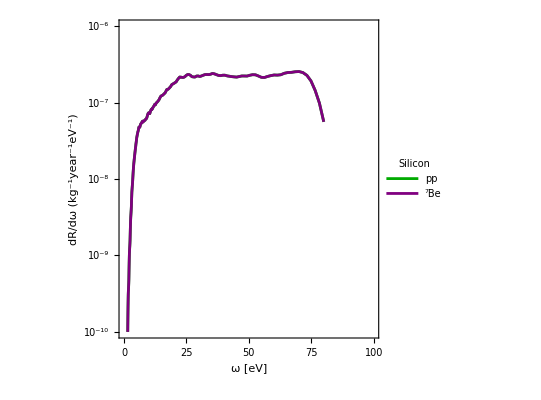

```mathematica
ListLogPlot[{νEdftRatesSi,νEdftRatesSiOurs},Joined->True,
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
PlotRange->{{0,100},{10^-10,10^-6}},FrameLabel->{"ω [eV]","dR/dω (kg^-1year^-1eV^-1)"},
FrameTicks->{LogTicks[10^-13,10^-4],Automatic},
PlotLegends->Legend[{"pp","^7Be","pep","O15","N13","B8"},Position->{.85,.72},LegendFunction->framed,LegendLabel->Style["Silicon",16,FontFamily->"Times"]],
Epilog->Inset[Style["",16,FontFamily->"Times"],Scaled[{.8,.8}]]]
```

#### Calculate rates

First time:

```mathematica
{νEdftRatesGe,νEdftRatesSi}=Table[ParallelTable[{er/eV,dRνdω[er,target,flux](KilogramDay  365eV)},
{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux}},{er,logSpace[1eV,80eV,200]}],{target,{"Ge","Si"}}];

Do[νEdftRatesGe[[ii]]=Join[νEdftRatesGe[[ii]],{{1.01νEdftRatesGe[[ii,-1,1]],10^-99},{10^7,0}}];
νEdftRatesSi[[ii]]=Join[νEdftRatesSi[[ii]],{{1.01νEdftRatesSi[[ii,-1,1]],10^-99},{10^7,0}}];,{ii,1,Length[νEdftRatesSi]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.3285×10^-6}. NIntegrate obtained 1.72913×10^-80 and 1.92156×10^-81 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.32851×10^-6}. NIntegrate obtained 1.91123×10^-80 and 2.44395×10^-81 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.32853×10^-6}. NIntegrate obtained 2.49758×10^-80 and 2.60662×10^-81 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.3285×10^-6}. NIntegrate obtained 5.83529×10^-79 and 6.48472×10^-80 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.3285×10^-6}. NIntegrate obtained 6.00355×10^-80 and 6.6718×10^-81 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.32851×10^-6}. NIntegrate obtained 6.44985×10^-79 and 8.24762×10^-80 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8442×10^-6}. NIntegrate obtained 3.25054×10^-81 and 1.86217×10^-82 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.84421×10^-6}. NIntegrate obtained 4.66938×10^-81 and 2.12196×10^-82 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.84423×10^-6}. NIntegrate obtained 6.22809×10^-81 and 2.08437×10^-82 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8442×10^-6}. NIntegrate obtained 1.09696×10^-79 and 6.28426×10^-81 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8442×10^-6}. NIntegrate obtained 1.12859×10^-80 and 6.46533×10^-82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.84421×10^-6}. NIntegrate obtained 1.57578×10^-79 and 7.16094×10^-81 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Export/Import:

```mathematica
Export["results/rates/rate_solarNuE_valence_Ge.h5",νEdftRatesGe];
Export["results/rates/rate_solarNuE_valence_Si.h5",νEdftRatesSi];
```

```mathematica
νEdftRatesGe=Import["results/rates/rate_solarNuE_valence_Ge.h5","/Dataset1"];
νEdftRatesSi=Import["results/rates/rate_solarNuE_valence_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
νEdftTotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@νEdftRatesGe));
νEdftTotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@νEdftRatesSi));
```

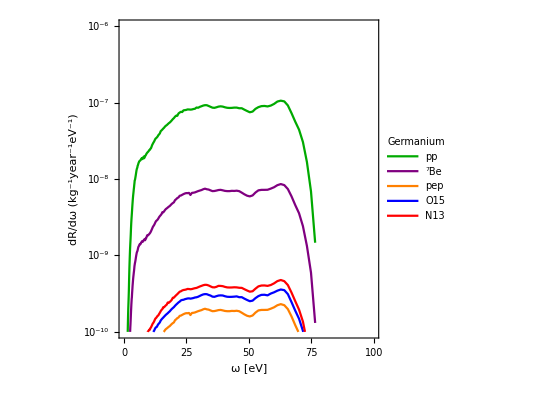
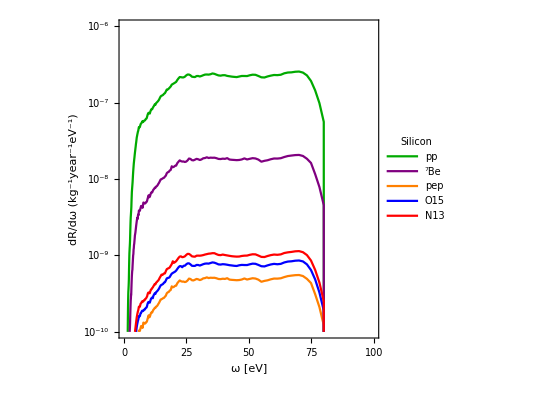

```mathematica
{nuPlotGe,nuPlotSi}={ListLogPlot[νEdftRatesGe,Joined->True,
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
PlotRange->{{0,100},{10^-10,10^-6}},FrameLabel->{"ω [eV]","dR/dω (kg^-1year^-1eV^-1)"},
FrameTicks->{LogTicks[10^-20,10^-5],Automatic},
PlotLegends->Legend[{"pp","^7Be","pep","O15","N13","B8"},Position->{.85,.72},LegendFunction->framed,LegendLabel->Style["Germanium",16,FontFamily->"Times"]],
Epilog->Inset[Style["",16,FontFamily->"Times"],Scaled[{.8,.8}]]],
ListLogPlot[νEdftRatesSi,Joined->True,
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
PlotRange->{{0,100},{10^-10,10^-6}},FrameLabel->{"ω [eV]","dR/dω (kg^-1year^-1eV^-1)"},
FrameTicks->{LogTicks[10^-13,10^-4],Automatic},
PlotLegends->Legend[{"pp","^7Be","pep","O15","N13","B8"},Position->{.85,.72},LegendFunction->framed,LegendLabel->Style["Silicon",16,FontFamily->"Times"]],
Epilog->Inset[Style["",16,FontFamily->"Times"],Scaled[{.8,.8}]]]}
```

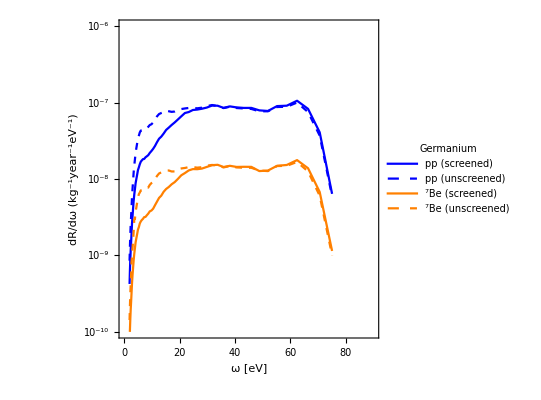
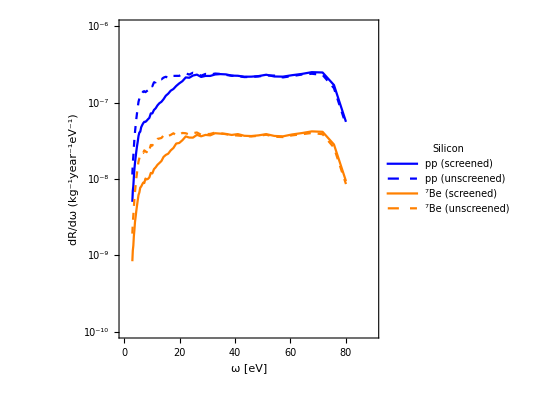

```mathematica
{nuPlotGe,nuPlotSi}={ListLogPlot[{ppRatePdatGe,ppRatePdatGeNoScreening,beRatePdatGe,beRatePdatGeNoScreening},Joined->True,PlotStyle->{Blue,{Blue,Dashed},Orange,{Orange,Dashed},{Black,DotDashed}},
PlotRange->{{0,90},{10^-10,10^-6}},FrameLabel->{"ω [eV]","dR/dω (kg^-1year^-1eV^-1)"},
FrameTicks->{LogTicks[10^-20,10^-5],Automatic},
PlotLegends->Legend[{"pp (screened)","pp (unscreened)","^7Be (screened)","^7Be (unscreened)"},Position->{.75,.2},LegendFunction->framed,LegendLabel->Style["Germanium",16,FontFamily->"Times"]],
Epilog->Inset[Style["",16,FontFamily->"Times"],Scaled[{.8,.8}]]],
ListLogPlot[{ppRatePdatSi,ppRatePdatSiNoScreening,beRatePdatSi,beRatePdatSiNoScreening},Joined->True,PlotStyle->{Blue,{Blue,Dashed},Orange,{Orange,Dashed},{Black,DotDashed}},
PlotRange->{{0,90},{10^-10,10^-6}},FrameLabel->{"ω [eV]","dR/dω (kg^-1year^-1eV^-1)"},
FrameTicks->{LogTicks[10^-13,10^-4],Automatic},
PlotLegends->Legend[{"pp (screened)","pp (unscreened)","^7Be (screened)","^7Be (unscreened)"},Position->{.75,.2},LegendFunction->framed,LegendLabel->Style["Silicon",16,FontFamily->"Times"]],
Epilog->Inset[Style["",16,FontFamily->"Times"],Scaled[{.8,.8}]]]}
```

```mathematica
Export["figures/fig_nuRate_si.pdf",nuPlotSi];
Export["figures/fig_nuRate_ge.pdf",nuPlotGe];
```

### CEvNS

Define helm form factor:

```mathematica
Fhelm[q_,A_]:=3.(Sin[(q r)/ℏcGeVfm]-((q r)/ℏcGeVfm)Cos[(q r)/ℏcGeVfm])/((q r)/ℏcGeVfm)^3 Exp[(-((q s)/ℏcGeVfm)^2)/2.]/.{r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9};
```

```mathematica
dσdEr[Er_,Enu_,iso_]:=(Gf^2(iso⟦5⟧ amu))/π(1-(iso⟦5⟧ amu Er)/(2 Enu^2 GeV))(iso⟦2⟧ qVp+(iso⟦3⟧-iso⟦2⟧) qVn)^2 Fhelm[√(2(iso⟦5⟧amu) Er),iso⟦3⟧]^2 UnitStep[Enu-TMIN[Er,0,iso⟦5⟧amu]]
```

```mathematica
dRcevnsSdE//Clear;
```

```mathematica
dRcevnsSdE[Er_?NumericQ,target_,flux_]:=NT[target,"N"] NIntegrate[ flux[Enu] dσdEr[Er,Enu,isotopes[target][[1]]],{Enu,Min[Max[flux[[1,1,1]],TMIN[Er,0,isotopes[target][[1,5]]amu]],flux[[1,1,2]]],flux[[1,1,2]]}]

dRcevnsLdE[Er_?NumericQ,target_,fluxNorm_,fluxE_]:=NT[target,"N"]  fluxNorm dσdEr[Er,fluxE,isotopes[target][[1]]]

dRcevnsdE[Er_?NumericQ,target_,fluxOb_]:=Switch[fluxOb[[1]],
"Line",Sum[dRcevnsLdE[Er,target,fluxOb[[2,fluxi]],fluxOb[[3,fluxi]]],{fluxi,1,Length[fluxOb[[2]]]}],
"Spectrum",dRcevnsSdE[Er,target,fluxOb[[2]]]]
```

```mathematica
{CEvNSRatesGe,CEvNSRatesSi}=Table[ParallelTable[{er/eV,dRcevnsdE[er,target,flux](KilogramDay  365.242eV)},
{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux,b8Flux}},{er,logSpace[1eV,TMAX[flux[[-1]],0,(isotopes[target])[[1,5]]amu],200]}],{target,{"Ge","Si"}}];

(*Pad and calculate totals:*)
Do[
CEvNSRatesGe[[ii]]=Join[DeleteCases[CEvNSRatesGe[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesGe[[ii,-1,1]],0},{20000,0}}];
CEvNSRatesSi[[ii]]=Join[DeleteCases[CEvNSRatesSi[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesSi[[ii,-1,1]],0},{20000,0}}];
,{ii,1,6}]
CEvNStotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGe));
CEvNStotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSi));
```

```mathematica
Export["results/rates/rate_solarNu_cevns_Ge.h5",CEvNSRatesGe];
Export["results/rates/rate_solarNu_cevns_Si.h5",CEvNSRatesSi];
```

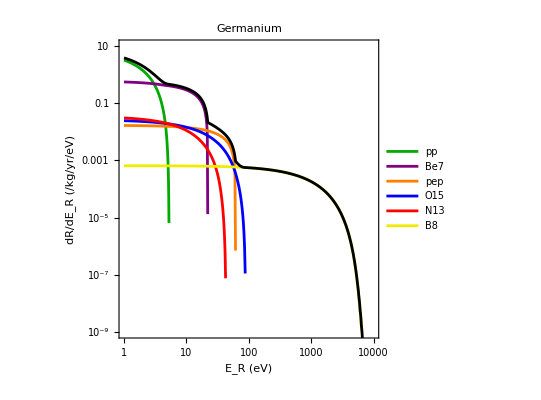
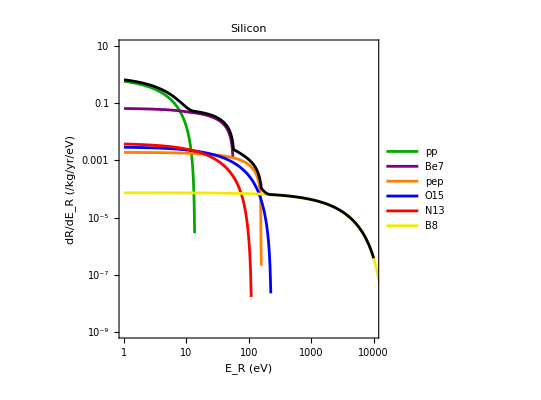

```mathematica
{Show[ListLogLogPlot[CEvNSRatesGe,
FrameLabel->{"E_R (eV)","dR/dE_R (/kg/yr/eV)"},
PlotRange->{{1,10^4},{10^-9,10}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^-8,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13","B8"}],
PlotLabel->"Germanium"],LogLogPlot[CEvNStotRateGe[e],{e,1,10^4},PlotStyle->Black]],
Show[ListLogLogPlot[CEvNSRatesSi,
FrameLabel->{"E_R (eV)","dR/dE_R (/kg/yr/eV)"},
PlotRange->{{1,10^4},{10^-9,10}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^-8,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13","B8"}],
PlotLabel->"Silicon"],LogLogPlot[CEvNStotRateSi[e],{e,1,10^4},PlotStyle->Black]]}
```

#### Quenched rates and effect of different yield models

```mathematica
CEvNSRatesGeQl=ParallelTable[{CEvNSRatesGe[[fluxi,Ej,1]]eV//YQ[#,"Ge","Lindhard"]#/eV&,CEvNSRatesGe[[fluxi,Ej,2]]/YQ[CEvNSRatesGe[[fluxi,Ej,1]]eV,"Ge","Lindhard"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesGe[[fluxi]]]}];
CEvNSRatesSiQl=ParallelTable[{CEvNSRatesSi[[fluxi,Ej,1]]eV//YQ[#,"Si","Lindhard"]#/eV&,CEvNSRatesSi[[fluxi,Ej,2]]/YQ[CEvNSRatesSi[[fluxi,Ej,1]]eV,"Si","Lindhard"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesSi[[fluxi]]]}];
CEvNSRatesGeQs=ParallelTable[{CEvNSRatesGe[[fluxi,Ej,1]]eV//YQ[#,"Ge","Sarkis"]#/eV&,CEvNSRatesGe[[fluxi,Ej,2]]/YQ[CEvNSRatesGe[[fluxi,Ej,1]]eV,"Ge","Sarkis"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesGe[[fluxi]]]}];
CEvNSRatesSiQs=ParallelTable[{CEvNSRatesSi[[fluxi,Ej,1]]eV//YQ[#,"Si","EmpiricalSiCut"]#/eV&,CEvNSRatesSi[[fluxi,Ej,2]]/YQ[CEvNSRatesSi[[fluxi,Ej,1]]eV,"Si","EmpiricalSiCut"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesSi[[fluxi]]]}];
 (*Remove points quenched to 0 and pad with zeros to stop extrapolation*)
Do[
CEvNSRatesGeQs[[ii]]=Join[DeleteCases[CEvNSRatesGeQs[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesGeQs[[ii,-1,1]],1. 10^-100},{20000,0}}];
CEvNSRatesSiQs[[ii]]=Join[DeleteCases[CEvNSRatesSiQs[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesSiQs[[ii,-1,1]],1. 10^-100},{20000,0}}];
CEvNSRatesGeQl[[ii]]=Join[DeleteCases[CEvNSRatesGeQl[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesGeQl[[ii,-1,1]],1. 10^-100},{20000,0}}];
CEvNSRatesSiQl[[ii]]=Join[DeleteCases[CEvNSRatesSiQl[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesSiQl[[ii,-1,1]],1. 10^-100},{20000,0}}];,{ii,1,6}]
(*Calculate totals:*)
CEvNStotRateGeQs[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGeQs)));
CEvNStotRateSiQs[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSiQs)));
CEvNStotRateGeQl[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGeQl)));
CEvNStotRateSiQl[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSiQl)));
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

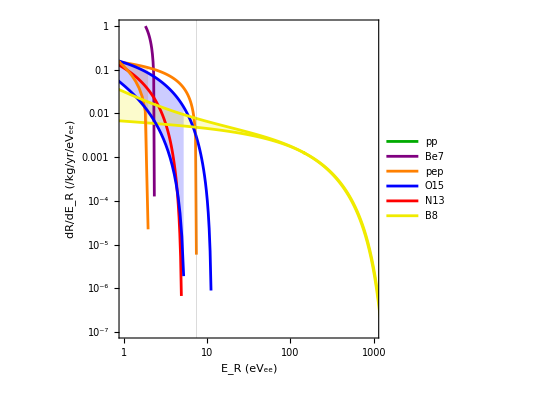
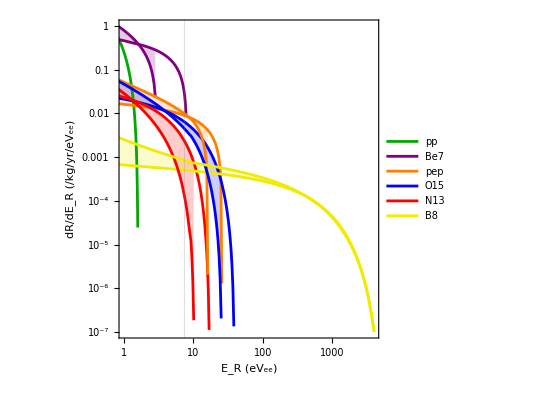

```mathematica
{ListLogLogPlot[Join[CEvNSRatesGeQl,CEvNSRatesGeQs],Filling->{1->{7},2->{8},3->{9},4->{10},5->{11},6->{12}},
FrameLabel->{"E_R (eV_ee)","dR/dE_R (/kg/yr/eV_ee)"},
PlotRange->{{1,10^3},{10^-7,1}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^0,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13","B8"}],GridLines->{{7.4},None}],
ListLogLogPlot[Join[CEvNSRatesSiQl,CEvNSRatesSiQs],Filling->{1->{7},2->{8},3->{9},4->{10},5->{11},6->{12}},
FrameLabel->{"E_R (eV_ee)","dR/dE_R (/kg/yr/eV_ee)"},
PlotRange->{{1,4 10^3},{10^-7,1}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.]},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^0,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13","B8"}],GridLines->{{7.4},None}]}
```

```mathematica
LogLogPlot[{CEvNStotRateGeQs[EReV],CEvNStotRateGeQl[EReV],CEvNStotRateSiQs[EReV],CEvNStotRateSiQl[EReV]},{EReV,1,3000},Filling->{1->{2},3->{4}},FrameLabel->{"E_R (eV_ee)","dR/dE_R (/kg/yr/eV_ee)"},
PlotRange->{{1,3 10^3},{10^-7,1}},
PlotStyle->{Green//Darker,Green//Darker,Purple,Purple},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^0,10^6]},
PlotLegends->Legend[{"Ge","","Si"}]]
```

-Graphics-

### Neutrino valence Migdal rates

In the free approximation:

```mathematica
dRνMigdω[ω_?NumericQ,target_,fluxOb_]:=
NT[target,"N"]dpdωFast[ω,target]eV NIntegrate[dRcevnsdE[Er,target,fluxOb],{Er,Max[4ωb[target],ω^2/mT[target]],TMAX[fluxOb[[-1]],0,mT[target]]},PrecisionGoal->3]
```

### Neutrino core Migdal rates

```mathematica
dRνMigCoredE[Edet_?NumericQ,target_,fluxOb_,Ni_]:=
NT[target,"N"] NIntegrate[dRcevnsdE[ER,target,fluxOb] Sum[UnitStep[Edet-ER YQ[ER,target,"Lindhard"]-orbit[[2]]] Znl[target,orbit[[1]],Edet-ER YQ[ER,target,"Lindhard"] -orbit[[2]],√((2ER)/mT[target])],
{orbit,Select[orbits[target],(StringContainsQ[#[[1]],ToString/@Ni])&]}],{ER,Max[4ωb[target],Edet^2/mT[target]],TMAX[fluxOb[[-1]],0,mT[target]]},PrecisionGoal->2]
```

```mathematica
migThres[target_]:=Switch[target,"Ge",43.6eV,"Si",116eV];
```

### Neutrino rate comparison

```mathematica
{CEvNSmigRatesGe,CEvNSmigRatesSi}=Table[ParallelTable[{ω/eV,dRνMigdω[ω,target,flux](KilogramDay  365eV)},
{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux,b8Flux}},{ω,logSpace[1eV,50eV,200]}],{target,{"Ge","Si"}}];

Do[CEvNSmigRatesGe[[ii]]=Join[CEvNSmigRatesGe[[ii]],{{1.01CEvNSmigRatesGe[[ii,-1,1]],10^-99},{10^7,0}}];
CEvNSmigRatesSi[[ii]]=Join[CEvNSmigRatesSi[[ii]],{{1.01CEvNSmigRatesSi[[ii,-1,1]],10^-99},{10^7,0}}];,{ii,1,Length[CEvNSmigRatesSi]}] 
(*Calculate totals:*)
CEvNSmigTotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigRatesGe));
CEvNSmigTotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigRatesSi));
```

$Aborted

```mathematica
{CEvNSmigVRatesGe,CEvNSmigVRatesSi}=Table[ParallelTable[{ω/eV,dRνMigdω[ω,target,flux](KilogramDay  365eV)},
{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux,b8Flux}},{ω,logSpace[1eV,80eV,100]}],{target,{"Ge","Si"}}];
{CEvNSmigCRatesGe,CEvNSmigCRatesSi}=Table[ParallelTable[{Edet/eV,dRνMigCoredE[Edet,target,flux,Core[target]](KilogramDay  365eV)},
{flux,{ppFlux,be7Flux,pepFlux,o15Flux,n13Flux,b8Flux}},{Edet,logSpace[migThres[target],3keV,100]}],{target,{"Ge","Si"}}];

Do[CEvNSmigVRatesGe[[ii]]=Join[CEvNSmigVRatesGe[[ii]],{{1.01CEvNSmigVRatesGe[[ii,-1,1]],10^-99},{10^7,0}}];
CEvNSmigVRatesSi[[ii]]=Join[CEvNSmigVRatesSi[[ii]],{{1.01CEvNSmigVRatesSi[[ii,-1,1]],10^-99},{10^7,0}}];
CEvNSmigCRatesGe[[ii]]=Join[CEvNSmigCRatesGe[[ii]],{{1.01CEvNSmigCRatesGe[[ii,-1,1]],10^-99},{10^7,0}}];
CEvNSmigCRatesSi[[ii]]=Join[CEvNSmigCRatesSi[[ii]],{{1.01CEvNSmigCRatesSi[[ii,-1,1]],10^-99},{10^7,0}}];,{ii,1,Length[CEvNSmigVRatesSi]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,1.09519×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,1.09519×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{3.69064×10^-44},{0.001439},{0.5},0.001439}] (UnitStep[-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,3.04488×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111405-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.56403×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,1.09519×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{3.69064×10^-44},{0.001439},{0.5},0.001439}] (UnitStep[-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,3.04488×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Line,{3.69064×10^-44},{0.001439},{0.5},0.001439}] (UnitStep[-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,1s,-0.0000111385-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]+«7»+UnitStep[-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Ge,3s,-1.54416×10^-7-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.171381 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,3.04488×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00009922,0.00120971}},{5,7,0,{15},{2},0,0,0,0,Automatic,«3»},{{0.00009922,0.00012424,0.00015558,0.00019652,0.00025477,0.00033028,0.00042082,0.00051795,0.00064304,0.00081235,«5»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«6»},{5.98454×10^-42,9.25268×10^-42,1.43055×10^-41,2.09543×10^-41,3.24107×10^-41,4.49862×10^-41,6.59012×10^-41,8.20348×10^-41,1.0781×10^-40,1.08106×10^-40,«5»}},{Automatic}],0.5,0.00120971}] (UnitStep[-0.0000111385-0.162 «3»] Znl[«1»]+«7»+«1» «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,2.15303×10^-8}}.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00010012,0.00174011}},{5,7,0,{14},{2},0,0,0,0,Automatic,«3»},{{0.00010012,0.00013205,0.00018186,0.00025485,0.00036025,0.00051364,0.00071362,0.00091717,0.00108115,0.00127445,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5»},{1.67375×10^-42,2.88546×10^-42,5.85454×10^-42,1.01001×10^-41,1.65079×10^-41,3.00694×10^-41,4.40942×10^-41,5.7972×10^-41,5.50233×10^-41,5.22246×10^-41,«4»}},{Automatic}],0.5,0.00174011}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,4.45059×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00009922,0.00120971}},{5,7,0,{15},{2},0,0,0,0,Automatic,«3»},{{0.00009922,0.00012424,0.00015558,0.00019652,0.00025477,0.00033028,0.00042082,0.00051795,0.00064304,0.00081235,«5»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«6»},{5.98454×10^-42,9.25268×10^-42,1.43055×10^-41,2.09543×10^-41,3.24107×10^-41,4.49862×10^-41,6.59012×10^-41,8.20348×10^-41,1.0781×10^-40,1.08106×10^-40,«5»}},{Automatic}],0.5,0.00120971}] (UnitStep[-0.0000111385-0.162 «3»] Znl[«1»]+«7»+«1» «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,2.15303×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00010012,0.00174011}},{5,7,0,{14},{2},0,0,0,0,Automatic,«3»},{{0.00010012,0.00013205,0.00018186,0.00025485,0.00036025,0.00051364,0.00071362,0.00091717,0.00108115,0.00127445,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5»},{1.67375×10^-42,2.88546×10^-42,5.85454×10^-42,1.01001×10^-41,1.65079×10^-41,3.00694×10^-41,4.40942×10^-41,5.7972×10^-41,5.50233×10^-41,5.22246×10^-41,«4»}},{Automatic}],0.5,0.00174011}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,4.45059×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{5.04×10^-6,0.00042341}},{5,7,0,{84},{2},0,0,0,0,Automatic,«3»},{{5.04×10^-6,0.00001008,0.00001512,0.00002016,0.0000252,0.00003024,0.00003528,0.00004032,0.00004537,0.00005041,«74»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«75»},{5.36424×10^-41,2.11504×10^-40,4.7052×10^-40,8.2456×10^-40,1.27209×10^-39,1.80698×10^-39,2.42463×10^-39,3.12352×10^-39,3.8975×10^-39,4.74198×10^-39,«74»}},{Automatic}],0.553,0.00042341}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,5.26554×10^-9}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00009922,0.00120971}},{5,7,0,{15},{2},0,0,0,0,Automatic,«3»},{{0.00009922,0.00012424,0.00015558,0.00019652,0.00025477,0.00033028,0.00042082,0.00051795,0.00064304,0.00081235,«5»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«6»},{5.98454×10^-42,9.25268×10^-42,1.43055×10^-41,2.09543×10^-41,3.24107×10^-41,4.49862×10^-41,6.59012×10^-41,8.20348×10^-41,1.0781×10^-40,1.08106×10^-40,«5»}},{Automatic}],0.5,0.00120971}] (UnitStep[-0.0000111385-0.162 «3»] Znl[«1»]+«7»+«1» «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,2.15303×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00010012,0.00174011}},{5,7,0,{14},{2},0,0,0,0,Automatic,«3»},{{0.00010012,0.00013205,0.00018186,0.00025485,0.00036025,0.00051364,0.00071362,0.00091717,0.00108115,0.00127445,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5»},{1.67375×10^-42,2.88546×10^-42,5.85454×10^-42,1.01001×10^-41,1.65079×10^-41,3.00694×10^-41,4.40942×10^-41,5.7972×10^-41,5.50233×10^-41,5.22246×10^-41,«4»}},{Automatic}],0.5,0.00174011}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,4.45059×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{5.04×10^-6,0.00042341}},{5,7,0,{84},{2},0,0,0,0,Automatic,«3»},{{5.04×10^-6,0.00001008,0.00001512,0.00002016,0.0000252,0.00003024,0.00003528,0.00004032,0.00004537,0.00005041,«74»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«75»},{5.36424×10^-41,2.11504×10^-40,4.7052×10^-40,8.2456×10^-40,1.27209×10^-39,1.80698×10^-39,2.42463×10^-39,3.12352×10^-39,3.8975×10^-39,4.74198×10^-39,«74»}},{Automatic}],0.553,0.00042341}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,5.26554×10^-9}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Ge,{Spectrum,InterpolatingFunction[{{0.00002,0.01602}},{5,7,0,{801},{2},0,0,0,0,Automatic,«3»},{{0.00002,0.00004,0.00006,0.00008,0.0001,0.00012,0.00014,0.00016,0.00018,0.0002,«791»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«792»},{1.2299×10^-47,4.86241×10^-47,1.07545×10^-46,1.87918×10^-46,2.88741×10^-46,4.08872×10^-46,5.47021×10^-46,7.02476×10^-46,8.7409×10^-46,1.06072×10^-45,«791»}},{Automatic}],0.34,0.01602}] (UnitStep[-0.0000103537-0.162 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[«1»]+«8») has evaluated to non-numerical values for all sampling points in the region with boundaries {{8.×10^-11,3.76722×10^-6}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,1s,-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]+UnitStep[3.93394×10^-9-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2p,3.93394×10^-9-0.146 ER «1» UnitStep[Times[«2»]],0.276723 √ER]+«1» «1»+UnitStep[-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2s,-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,2.85077×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,1s,-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]+UnitStep[3.93394×10^-9-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2p,3.93394×10^-9-0.146 ER «1» UnitStep[Times[«2»]],0.276723 √ER]+«1» «1»+UnitStep[-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2s,-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,2.85077×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Line,{1.15332×10^-42,1.28147×10^-43},{431/500000,6/15625},{0.54,0.5},431/500000}] (UnitStep[-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,1s,-1.758×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]+UnitStep[3.93394×10^-9-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2p,3.93394×10^-9-0.146 ER «1» UnitStep[Times[«2»]],0.276723 √ER]+«1» «1»+UnitStep[-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2s,-4.88271×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,2.85077×10^-8}}.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Line,{3.69064×10^-44},{0.001439},{0.5},0.001439}] (UnitStep[-1.74986×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,1s,-1.74986×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]+UnitStep[1.20758×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2p,1.20758×10^-8-0.146 ER Re[Times[«1»]] UnitStep[Times[«2»]],0.276723 √ER]+«1» «1»+UnitStep[-4.06852×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2s,-4.06852×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,7.93347×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Line,{3.69064×10^-44},{0.001439},{0.5},0.001439}] (UnitStep[-1.74986×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,1s,-1.74986×10^-6-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]+UnitStep[1.20758×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2p,1.20758×10^-8-0.146 ER Re[Times[«1»]] UnitStep[Times[«2»]],0.276723 √ER]+«1» «1»+UnitStep[-4.06852×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]]] Znl[Si,2s,-4.06852×10^-8-0.146 ER Re[Times[«2»]] UnitStep[Times[«2»]],0.276723 √ER]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,7.93347×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{0.00009922,0.00120971}},{5,7,0,{15},{2},0,0,0,0,Automatic,«3»},{{0.00009922,0.00012424,0.00015558,0.00019652,0.00025477,0.00033028,0.00042082,0.00051795,0.00064304,0.00081235,«5»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«6»},{5.98454×10^-42,9.25268×10^-42,1.43055×10^-41,2.09543×10^-41,3.24107×10^-41,4.49862×10^-41,6.59012×10^-41,8.20348×10^-41,1.0781×10^-40,1.08106×10^-40,«5»}},{Automatic}],0.5,0.00120971}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,5.60852×10^-8}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{0.00009922,0.00120971}},{5,7,0,{15},{2},0,0,0,0,Automatic,«3»},{{0.00009922,0.00012424,0.00015558,0.00019652,0.00025477,0.00033028,0.00042082,0.00051795,0.00064304,0.00081235,«5»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«6»},{5.98454×10^-42,9.25268×10^-42,1.43055×10^-41,2.09543×10^-41,3.24107×10^-41,4.49862×10^-41,6.59012×10^-41,8.20348×10^-41,1.0781×10^-40,1.08106×10^-40,«5»}},{Automatic}],0.5,0.00120971}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,5.60852×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{5.04×10^-6,0.00042341}},{5,7,0,{84},{2},0,0,0,0,Automatic,«3»},{{5.04×10^-6,0.00001008,0.00001512,0.00002016,0.0000252,0.00003024,0.00003528,0.00004032,0.00004537,0.00005041,«74»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«75»},{5.36424×10^-41,2.11504×10^-40,4.7052×10^-40,8.2456×10^-40,1.27209×10^-39,1.80698×10^-39,2.42463×10^-39,3.12352×10^-39,3.8975×10^-39,4.74198×10^-39,«74»}},{Automatic}],0.553,0.00042341}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,1.37277×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{0.00010012,0.00174011}},{5,7,0,{14},{2},0,0,0,0,Automatic,«3»},{{0.00010012,0.00013205,0.00018186,0.00025485,0.00036025,0.00051364,0.00071362,0.00091717,0.00108115,0.00127445,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5»},{1.67375×10^-42,2.88546×10^-42,5.85454×10^-42,1.01001×10^-41,1.65079×10^-41,3.00694×10^-41,4.40942×10^-41,5.7972×10^-41,5.50233×10^-41,5.22246×10^-41,«4»}},{Automatic}],0.5,0.00174011}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,1.15979×10^-7}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{5.04×10^-6,0.00042341}},{5,7,0,{84},{2},0,0,0,0,Automatic,«3»},{{5.04×10^-6,0.00001008,0.00001512,0.00002016,0.0000252,0.00003024,0.00003528,0.00004032,0.00004537,0.00005041,«74»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«75»},{5.36424×10^-41,2.11504×10^-40,4.7052×10^-40,8.2456×10^-40,1.27209×10^-39,1.80698×10^-39,2.42463×10^-39,3.12352×10^-39,3.8975×10^-39,4.74198×10^-39,«74»}},{Automatic}],0.553,0.00042341}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,1.37277×10^-8}}.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{0.00010012,0.00174011}},{5,7,0,{14},{2},0,0,0,0,Automatic,«3»},{{0.00010012,0.00013205,0.00018186,0.00025485,0.00036025,0.00051364,0.00071362,0.00091717,0.00108115,0.00127445,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5»},{1.67375×10^-42,2.88546×10^-42,5.85454×10^-42,1.01001×10^-41,1.65079×10^-41,3.00694×10^-41,4.40942×10^-41,5.7972×10^-41,5.50233×10^-41,5.22246×10^-41,«4»}},{Automatic}],0.5,0.00174011}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,1.15979×10^-7}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand dRcevnsdE[ER,Si,{Spectrum,InterpolatingFunction[{{5.04×10^-6,0.00042341}},{5,7,0,{84},{2},0,0,0,0,Automatic,«3»},{{5.04×10^-6,0.00001008,0.00001512,0.00002016,0.0000252,0.00003024,0.00003528,0.00004032,0.00004537,0.00005041,«74»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«75»},{5.36424×10^-41,2.11504×10^-40,4.7052×10^-40,8.2456×10^-40,1.27209×10^-39,1.80698×10^-39,2.42463×10^-39,3.12352×10^-39,3.8975×10^-39,4.74198×10^-39,«74»}},{Automatic}],0.553,0.00042341}] («1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.2×10^-10,1.37277×10^-8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
Export["results/rates/rate_solarNu_cevnsMigV_Ge.h5",CEvNSmigVRatesGe];
Export["results/rates/rate_solarNu_cevnsMigC_Ge.h5",CEvNSmigCRatesGe];
Export["results/rates/rate_solarNu_cevnsMigV_Si.h5",CEvNSmigVRatesSi];
Export["results/rates/rate_solarNu_cevnsMigC_Si.h5",CEvNSmigCRatesSi];
```

```mathematica
CEvNSmigVRatesGe=Import["results/rates/rate_solarNu_cevnsMigV_Ge.h5","/Dataset1"];
CEvNSmigCRatesGe=Import["results/rates/rate_solarNu_cevnsMigC_Ge.h5","/Dataset1"];
CEvNSmigVRatesSi=Import["results/rates/rate_solarNu_cevnsMigV_Si.h5","/Dataset1"];
CEvNSmigCRatesSi=Import["results/rates/rate_solarNu_cevnsMigC_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
```

```mathematica
CEvNSmigCTotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigCRatesGe));
CEvNSmigCTotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigCRatesSi));
CEvNSmigVTotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigVRatesGe));
CEvNSmigVTotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigVRatesSi));
```

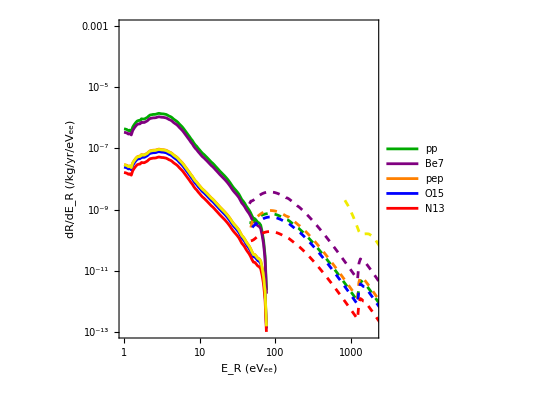
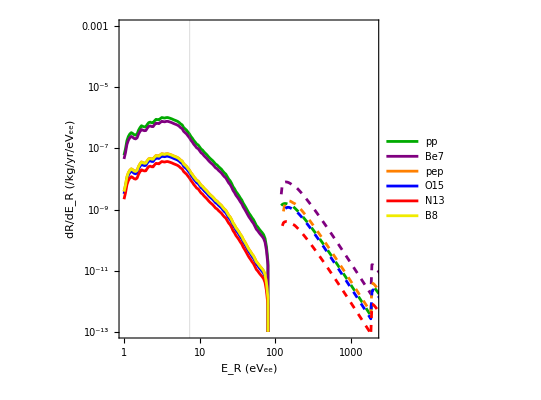

```mathematica
{Show[ListLogLogPlot[Join[CEvNSmigVRatesGe,CEvNSmigCRatesGe],
FrameLabel->{"E_R (eV_ee)","dR/dE_R (/kg/yr/eV_ee)"},
PlotRange->{{1,2 10^3},{10^-13,10^-3}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.],{Dashed,Green//Darker},{Dashed,Purple},{Dashed,Orange},{Dashed,Blue},{Dashed,Red},{Dashed,RGBColor[0.94,0.92,0.]}},
FrameTicks->{LogTicks[10^-12,10^4,2],LogTicks[10^0,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13"}],
GridLines->{{6},None}]],
Show[ListLogLogPlot[Join[CEvNSmigVRatesSi,CEvNSmigCRatesSi],
FrameLabel->{"E_R (eV_ee)","dR/dE_R (/kg/yr/eV_ee)"},
PlotRange->{{1,2 10^3},{10^-13,10^-3}},
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,RGBColor[0.94,0.92,0.],{Dashed,Green//Darker},{Dashed,Purple},{Dashed,Orange},{Dashed,Blue},{Dashed,Red},{Dashed,RGBColor[0.94,0.92,0.]}},
FrameTicks->{LogTicks[10^-9,10^4],LogTicks[10^0,10^6]},Joined->True,
PlotLegends->Legend[{"pp","Be7","pep","O15","N13","B8"}],GridLines->{{7.4},None}]]}
```

## Dark matter rates

### Maxwell Boltzmann with cutoff

```mathematica
Fv0MB[η_,xmin_,v00_]:=If[xmin>VMAX/v0,0,1/v00(Erf[xmin+η]-Erf[xmin-η])/(2 η)]
```

```mathematica
Fv0MBcutoff[η_,xmin_,xesc_,v00_]=1/v00((-4 η (-3-3 xesc^2+3 xmin^2+η^2)+3 E^xesc^2 Sqrt[π] (Erf[xmin-η]-Erf[xmin+η]))/(2 η (6 xesc+4 xesc^3-3 E^xesc^2 Sqrt[π] Erf[xesc])) UnitStep[xesc-xmin-η]+(2 (xesc-xmin+η) (3+(2 xesc+xmin-η) (xesc-xmin+η))+3 E^xesc^2 Sqrt[π] (-Erf[xesc]+Erf[xmin-η]))/(2 η (6 xesc+4 xesc^3-3 E^xesc^2 Sqrt[π] Erf[xesc])) UnitStep[xesc-xmin+η,-xesc+xmin+η])
```

(((-4 η (-3-3 xesc^2+3 xmin^2+η^2)+3 ⅇ^(xesc^2) √π (Erf[xmin-η]-Erf[xmin+η])) UnitStep[xesc-xmin-η])/(2 η (6 xesc+4 xesc^3-3 ⅇ^(xesc^2) √π Erf[xesc]))+((2 (xesc-xmin+η) (3+(2 xesc+xmin-η) (xesc-xmin+η))+3 ⅇ^(xesc^2) √π (-Erf[xesc]+Erf[xmin-η])) UnitStep[xesc-xmin+η,-xesc+xmin+η])/(2 η (6 xesc+4 xesc^3-3 ⅇ^(xesc^2) √π Erf[xesc])))/v00

```mathematica
Gv[vmin_,V0_:v0,VE_:ve,VESC_:vesc,ii_:1]=If[vmin<VMAX,
If[ii==1,Fv0MBcutoff[VE/V0,vmin/V0,VESC/V0,V0],Fv0MB[VE/V0,vmin/V0,V0]]
,0];
```

```mathematica
Fv[V_?NumericQ,V0_:v0,VE_:ve,VESC_:vesc]=Piecewise[{{(ⅇ^(-((V+VE)^2+VESC^2)/V0^2) V HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)] (-ⅇ^((4 V VE+VESC^2)/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (V0^2-(V-VE)^2+VESC^2)+(ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (-V0^2+(V+VE)^2-VESC^2)) HeavisideTheta[(-(V+VE)^2+VESC^2)/(V VE)]))/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), V<-VE+VESC}, {0, V≥VE+VESC}, {-(ⅇ^(-((V-VE)^2+VESC^2)/V0^2) V (ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V-VE)^2/V0^2) (-V0^2+(V-VE)^2-VESC^2)) HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)])/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), True}}]
```

Piecewise[{{(ⅇ^(-((V+VE)^2+VESC^2)/V0^2) V HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)] (-ⅇ^((4 V VE+VESC^2)/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (V0^2-(V-VE)^2+VESC^2)+(ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (-V0^2+(V+VE)^2-VESC^2)) HeavisideTheta[(-(V+VE)^2+VESC^2)/(V VE)]))/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), V<-VE+VESC}, {0, V≥VE+VESC}, {-(ⅇ^(-((V-VE)^2+VESC^2)/V0^2) V (ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V-VE)^2/V0^2) (-V0^2+(V-VE)^2-VESC^2)) HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)])/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), True}}]

### Kinematics

Electron energy is change in DM energy less the atomic recoil:

ω==(Exf-Exi)-Eaf
ω==((|mx v-q|^2)/(2mx)-1/2 mx v^2)-q^2/(2mX)
ω==q.v-q^2/(2mx)
v cosθ== (q/(2mx)+ω/q)

```mathematica
v cosθ== (q/(2mx)+ω/q)//Solve[#,q]&
```

{{q→cosθ mx v-√(cosθ^2 mx^2 v^2-2 mx ω)},{q→cosθ mx v+√(cosθ^2 mx^2 v^2-2 mx ω)}}

Approximate DM velocity as spherically symmetric, only care about v_min:

```mathematica
vmin[k_,ω_,mx_]:=ω/k+k/(2mx)
```

```mathematica
qmin[ω_,mx_]:=mx VMAX - √(mx^2 VMAX^2-2 ω mx)
qmax[ω_,mx_]:=mx VMAX + √(mx^2 VMAX^2-2 ω mx)
```

```mathematica
ωMax[mx_]=(mx VMAX^2)/2;
```

The region of the dielectric function that gets integrated over doesn’t include the plasmon resonance because DM is moving too slowly:

```mathematica
phaseSpacePlot=With[{mx=1GeV},
Show[DensityPlot[darkEELFsi[ω,k 10^3],{ω,0,90},{k,0,12},PlotRange->All,AspectRatio->0.75,PlotRange->{{0,90},{0,12}},FrameStyle->Directive[Black,FontFamily->"Times",18],ColorFunctionScaling->False,
FrameLabel->{"ω (eV)","k (keV)"},PlotRange->All,PlotPoints->100,ColorFunction->(Opacity[#1,Darker[Blue]]&)],Plot[{(mx VMAX - √(mx^2 VMAX^2-2 ω eV mx))/keV,(mx VMAX+ √(mx^2 VMAX^2-2 ω eV mx))/keV,ω/1000},{ω,0,90},PlotStyle->{Red,Red,Darker[Green]},Filling->Top,PlotRange->{{0,90},{0,12}}],
Epilog->{Inset[Style[Text["DM:           \n m_χ = 1 GeV"],FontFamily->"Sans Serif",18,Red],Scaled[{.55,.84}]],
Inset[Graphics[{Red,Thick,{Arrowheads[Large],Arrow[{{10,10},{4,10}}]}}],{24,10}],
Inset[Style[Text["Neutrino:  \nE_ν = 1 MeV"],FontFamily->"Sans Serif",18,Darker[Green]],Scaled[{.7,.18}]]}]]
```

-Graphics-

```mathematica
Export["figures/fig_phase_space.png",phaseSpacePlot,ImageResolution->500];
```

```mathematica
Vmin[ER_,δ_,mX_,mT_]=(ER mT+δ μ[mX,mT])/(√(2 mT ER) μ[mX,mT]);
```

### Valence electron scattering rate

Dark matter form factor:

```mathematica
FDM[q_,mediator_:"heavy"]:=Switch[mediator,
"heavy",
1,
"light",
(αEM me)^2/q^2,
_,
(mediator^2+(αEM me)^2)/(mediator^2+q^2)];
```

Differential dark matter rate in silicon:

```mathematica
dRdω[ω_,mx_,σe_,target_,screening_:True,mediator_:"heavy"]:=Module[{qMax},
qMax=qmax[ω,mx];
If[ω>0.999ωMax[mx]||ω>80,0,
1/ρT[target] ρx/mx(π σe)/μ[me,mx]^2 NIntegrate[
Gv[vmin[kk,ω,mx ]] kk/(2π)^2 FDM[kk,mediator]^2 S1[ω,kk,target,screening]
,{kk,qmin[ω,mx],Min[qmax[ω,mx],20keV]},PrecisionGoal->2]]]
```

```mathematica
dRdωList//Clear;
dRdωList[ωMin_?NumericQ,mx_?NumericQ,σe_?NumericQ,target_,screening_:True,mediator_:"heavy",nPoints_:20]:=Module[{},Table[{ω/eV,(KilogramDay 365.25 eV)  dRdω[ω,mx,σe,"Si",screening,mediator]//# UnitStep[#]&},{ω,linSpace[ωMin,Min[ωMax[mx],79eV],nPoints]}]];
```

```mathematica
rateDM//Clear;
rateDM[mx_,σe_,target_,ThEHP_:1,screening_:True,mediator_:"heavy"]:=If[ωMax[mx]<thresh[ThEHP,target],0,
1/ρT[target] ρx/mx(π σe)/μ[me,mx]^2 NIntegrate[
Gv[vmin[kk,ω,mx]] kk/(2π)^2 FDM[kk,mediator]^2 S1[ω,kk,target,screening]
,{ω,thresh[ThEHP,target],Min[ωMax[mx],70eV]},{kk,qmin[ω,mx],Min[qmax[ω,mx],20keV]},PrecisionGoal->2]]
```

#### Calculations

Compare with Tongyan:

```mathematica
tyRate=Import["data/tongyan_10MeV_si.csv"];
```

```mathematica
rateDat=ParallelTable[{ω,(KilogramDay 365.25 eV)  dRdω[ω eV,.01 GeV,10^-38 Centimeter^2,"Si"]},{ω,1,20,1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84379×10^-6}. NIntegrate obtained 1.92701×10^-24 and 1.21171×10^-25 for the integral and error estimates.

```mathematica
rateDatNoScreen=ParallelTable[{ω,(KilogramDay 365.25 eV)  dRdω[ω eV,.01 GeV,10^-38 Centimeter^2,"Si",False]},{ω,1,20,1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84379×10^-6}. NIntegrate obtained 4.03914×10^-24 and 1.71658×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84379×10^-6}. NIntegrate obtained 4.03914×10^-24 and 1.71658×10^-25 for the integral and error estimates.

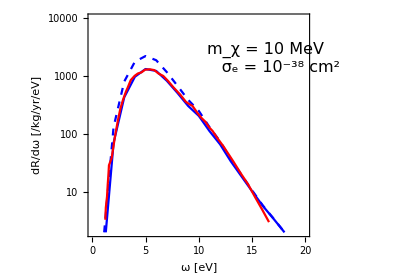

```mathematica
dmPlot=Show[ListLogPlot[{rateDat,rateDatNoScreen},Joined->True,PlotRange->{{0,20},{2,10^4}},FrameLabel->{"ω [eV]","dR/dω [/kg/yr/eV]"},PlotStyle->{Blue,{Blue,Dashed}},
FrameTicks->{LogTicks[1,10^4],Automatic},AspectRatio->.7,
Epilog->Inset[Style["m_χ = 10 MeV\n      σ_e = 10^-38 cm^2",16,FontFamily->"Times"],Scaled[{.8,.8}]]],ListLogPlot[tyRate,PlotStyle->Red,Joined->True]]
```

This matches Fig.2 of 2101.08275, except I think there is a typo in their units..

Pre-calculate dark matter-electron scattering rates:

```mathematica
dmElightRateTableSi=ParallelTable[{mx,dRdωList[1eV,mx,10^-38 Centimeter^2,"Si",True,"light",80]},{mx,logSpace[.0005,1,150]}];
dmEheavyRateTableSi=ParallelTable[{mx,dRdωList[1eV,mx,10^-38 Centimeter^2,"Si",True,"heavy",80]},{mx,logSpace[.0005,1,150]}];
dmElightRateTableGe=ParallelTable[{mx,dRdωList[1eV,mx,10^-38 Centimeter^2,"Ge",True,"light",80]},{mx,logSpace[.0005,1,150]}];
dmEheavyRateTableGe=ParallelTable[{mx,dRdωList[1eV,mx,10^-38 Centimeter^2,"Ge",True,"heavy",80]},{mx,logSpace[.0005,1,150]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81229×10^-6}. NIntegrate obtained 1.27473×10^-24 and 3.02187×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79685×10^-6}. NIntegrate obtained 9.5919×10^-25 and 4.74861×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.92013×10^-6}. NIntegrate obtained 1.29008×10^-24 and 3.2187×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10422×10^-6}. NIntegrate obtained 1.36049×10^-24 and 4.70055×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {3.24141×10^-6}. NIntegrate obtained 2.20344×10^-23 and 2.7787×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11729×10^-6}. NIntegrate obtained 7.38497×10^-23 and 7.59412×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81665×10^-6}. NIntegrate obtained 1.28904×10^-24 and 4.89941×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81115×10^-6}. NIntegrate obtained 1.38678×10^-24 and 5.60322×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8534×10^-6}. NIntegrate obtained 1.34685×10^-24 and 3.99237×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000201803}. NIntegrate obtained 5.05446×10^-56 and 2.67907×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80699×10^-6}. NIntegrate obtained 1.27673×10^-24 and 7.22522×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217661}. NIntegrate obtained -6.50177×10^-56 and 1.80771×10^-57 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000025958}. NIntegrate obtained 5.07704×10^-50 and 1.0582×10^-51 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.83802×10^-6}. NIntegrate obtained 1.27931×10^-24 and 2.3325×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80697×10^-6}. NIntegrate obtained 1.39906×10^-24 and 9.15673×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10896×10^-6}. NIntegrate obtained 1.3824×10^-24 and 6.61864×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000284536}. NIntegrate obtained 1.95361×10^-49 and 2.44653×10^-50 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.92064×10^-6}. NIntegrate obtained 1.3935×10^-24 and 3.96009×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.91424×10^-6}. NIntegrate obtained 1.39548×10^-24 and 3.05029×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80626×10^-6}. NIntegrate obtained 1.39539×10^-24 and 7.80956×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000222766}. NIntegrate obtained -1.3396×10^-55 and 2.0948×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80132×10^-6}. NIntegrate obtained 1.34893×10^-24 and 7.09315×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80743×10^-6}. NIntegrate obtained 3.70469×10^-23 and 4.54792×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020217}. NIntegrate obtained -2.22496×10^-55 and 2.02489×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206798}. NIntegrate obtained -6.69561×10^-56 and 4.78571×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80558×10^-6}. NIntegrate obtained 1.39728×10^-24 and 6.01383×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.30163×10^-6}. NIntegrate obtained 1.2498×10^-24 and 1.36813×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79799×10^-6}. NIntegrate obtained 1.42139×10^-24 and 4.89602×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79707×10^-6}. NIntegrate obtained 1.41586×10^-24 and 4.48263×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79633×10^-6}. NIntegrate obtained 1.41311×10^-24 and 5.51094×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000216837}. NIntegrate obtained -1.68689×10^-56 and 2.11252×10^-57 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.8009×10^-6}. NIntegrate obtained 1.34948×10^-24 and 5.83947×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11954×10^-6}. NIntegrate obtained 1.36443×10^-24 and 3.93754×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.29657×10^-6}. NIntegrate obtained 3.99176×10^-23 and 4.84699×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79572×10^-6}. NIntegrate obtained 1.42512×10^-24 and 4.25256×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79774×10^-6}. NIntegrate obtained 1.36984×10^-24 and 5.01235×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1053×10^-6}. NIntegrate obtained 1.25368×10^-24 and 3.08631×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {3.47187×10^-6}. NIntegrate obtained 1.28812×10^-23 and 1.78052×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85829×10^-6}. NIntegrate obtained 1.3016×10^-24 and 2.9907×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020209}. NIntegrate obtained 2.12521×10^-55 and 1.11231×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206322}. NIntegrate obtained -2.89984×10^-56 and 9.65711×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79617×10^-6}. NIntegrate obtained 1.41051×10^-24 and 5.18825×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217866}. NIntegrate obtained 3.082×10^-56 and 4.14401×10^-57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000231009}. NIntegrate obtained 4.02418×10^-52 and 6.70071×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85794×10^-6}. NIntegrate obtained 1.38805×10^-24 and 4.24112×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000208691}. NIntegrate obtained 6.99137×10^-56 and 8.40346×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000221191}. NIntegrate obtained -1.48919×10^-56 and 1.86494×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85765×10^-6}. NIntegrate obtained 1.41334×10^-24 and 4.13243×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79751×10^-6}. NIntegrate obtained 1.37205×10^-24 and 5.47866×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11532×10^-6}. NIntegrate obtained 1.42078×10^-24 and 4.01379×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80332×10^-6}. NIntegrate obtained 7.0925×10^-24 and 1.53008×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11513×10^-6}. NIntegrate obtained 1.4228×10^-24 and 4.59797×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11498×10^-6}. NIntegrate obtained 1.42252×10^-24 and 4.79121×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8582×10^-6}. NIntegrate obtained 1.30309×10^-24 and 3.10439×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020093}. NIntegrate obtained 4.20356×10^-55 and 3.2531×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000203373}. NIntegrate obtained -2.04943×10^-54 and 3.05378×10^-56 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000219835}. NIntegrate obtained -1.17288×10^-55 and 8.38321×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000202956}. NIntegrate obtained 9.82331×10^-55 and 2.99196×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000207052}. NIntegrate obtained 2.04112×10^-54 and 1.27542×10^-55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214867}. NIntegrate obtained -1.40036×10^-56 and 4.26008×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000272172}. NIntegrate obtained -2.02258×10^-48 and 4.22711×10^-50 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206415}. NIntegrate obtained -6.51063×10^-55 and 3.9431×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000218632}. NIntegrate obtained -9.53772×10^-55 and 1.64463×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000210246}. NIntegrate obtained 5.47019×10^-54 and 1.3513×10^-55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214309}. NIntegrate obtained -4.51342×10^-55 and 2.53685×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020375}. NIntegrate obtained 1.16644×10^-55 and 1.2156×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.56165×10^-6}. NIntegrate obtained 7.45626×10^-24 and 7.90326×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.29234×10^-6}. NIntegrate obtained 9.27594×10^-24 and 1.15573×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21757×10^-6}. NIntegrate obtained 1.96965×10^-24 and 1.38003×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10422×10^-6}. NIntegrate obtained 2.23065×10^-24 and 1.921×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20784×10^-6}. NIntegrate obtained 2.23504×10^-24 and 1.23821×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20799×10^-6}. NIntegrate obtained 1.09883×10^-24 and 1.42193×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.96154×10^-6}. NIntegrate obtained 5.77784×10^-23 and 1.56929×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74777×10^-6}. NIntegrate obtained 2.01428×10^-22 and 4.08117×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.93691×10^-6}. NIntegrate obtained 1.34459×10^-22 and 2.88649×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.65428×10^-6}. NIntegrate obtained 5.86685×10^-22 and 6.66307×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85014×10^-6}. NIntegrate obtained 6.34191×10^-24 and 8.67777×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84143×10^-6}. NIntegrate obtained 1.19121×10^-24 and 1.10519×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20896×10^-6}. NIntegrate obtained 1.33905×10^-23 and 1.49239×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.9477×10^-6}. NIntegrate obtained 3.2608×10^-23 and 9.23208×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.09791×10^-6}. NIntegrate obtained 2.23911×10^-24 and 1.34183×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.70338×10^-6}. NIntegrate obtained 2.91499×10^-22 and 3.12147×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.1911×10^-6}. NIntegrate obtained 2.29913×10^-24 and 9.46951×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.75283×10^-6}. NIntegrate obtained 2.96398×10^-22 and 3.56963×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000201803}. NIntegrate obtained 4.33558×10^-53 and 2.29803×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.66111×10^-6}. NIntegrate obtained 3.02123×10^-22 and 3.74006×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84802×10^-6}. NIntegrate obtained 2.03543×10^-24 and 2.0702×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217661}. NIntegrate obtained -7.54779×10^-53 and 2.09854×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21217×10^-6}. NIntegrate obtained 1.95217×10^-24 and 1.41203×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.2248×10^-6}. NIntegrate obtained 2.32537×10^-24 and 1.43858×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.22183×10^-6}. NIntegrate obtained 2.98414×10^-22 and 4.4541×10^-24 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000284536}. NIntegrate obtained 6.62292×10^-46 and 8.29397×10^-47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.70445×10^-6}. NIntegrate obtained 4.30297×10^-22 and 4.79147×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85421×10^-6}. NIntegrate obtained 2.30943×10^-24 and 1.70735×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10298×10^-6}. NIntegrate obtained 3.04827×10^-22 and 4.18967×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.81929×10^-6}. NIntegrate obtained 2.32754×10^-24 and 1.22058×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.24544×10^-6}. NIntegrate obtained 5.58765×10^-22 and 5.745×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85233×10^-6}. NIntegrate obtained 2.3375×10^-24 and 1.31915×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21921×10^-6}. NIntegrate obtained 2.39175×10^-24 and 1.54497×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.7475×10^-6}. NIntegrate obtained 3.06753×10^-22 and 4.77055×10^-24 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020217}. NIntegrate obtained -1.92244×10^-52 and 1.74958×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21093×10^-6}. NIntegrate obtained 1.91856×10^-24 and 6.23382×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21813×10^-6}. NIntegrate obtained 2.24757×10^-24 and 2.04875×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74271×10^-6}. NIntegrate obtained 3.07133×10^-22 and 4.18667×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84909×10^-6}. NIntegrate obtained 2.31965×10^-24 and 1.89241×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11247×10^-6}. NIntegrate obtained 3.05299×10^-22 and 3.44163×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84852×10^-6}. NIntegrate obtained 2.28436×10^-24 and 2.3149×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000216837}. NIntegrate obtained -1.92879×10^-53 and 2.41545×10^-54 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.22203×10^-6}. NIntegrate obtained 3.08989×10^-22 and 3.52742×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85201×10^-6}. NIntegrate obtained 2.3728×10^-24 and 1.16196×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21897×10^-6}. NIntegrate obtained 2.3993×10^-24 and 1.70899×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84805×10^-6}. NIntegrate obtained 2.3153×10^-24 and 2.06635×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1075×10^-6}. NIntegrate obtained 3.09277×10^-22 and 3.54134×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21795×10^-6}. NIntegrate obtained 2.24757×10^-24 and 1.87469×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1053×10^-6}. NIntegrate obtained 1.98718×10^-24 and 1.35831×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10433×10^-6}. NIntegrate obtained 3.06776×10^-23 and 6.16037×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85829×10^-6}. NIntegrate obtained 2.30903×10^-24 and 1.67787×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.699×10^-6}. NIntegrate obtained 3.09833×10^-22 and 3.15649×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020209}. NIntegrate obtained 1.83336×10^-52 and 9.59558×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84839×10^-6}. NIntegrate obtained 2.32734×10^-24 and 2.53723×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85794×10^-6}. NIntegrate obtained 2.3553×10^-24 and 1.77634×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.2173×10^-6}. NIntegrate obtained 3.09324×10^-22 and 3.20121×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000208691}. NIntegrate obtained 6.85871×10^-53 and 8.24401×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11555×10^-6}. NIntegrate obtained 2.35226×10^-24 and 1.74447×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84692×10^-6}. NIntegrate obtained 2.3353×10^-24 and 1.90821×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74938×10^-6}. NIntegrate obtained 1.05057×10^-23 and 1.34636×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.93385×10^-6}. NIntegrate obtained 1.26336×10^-23 and 1.86371×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84675×10^-6}. NIntegrate obtained 1.14115×10^-24 and 1.35689×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11498×10^-6}. NIntegrate obtained 2.34221×10^-24 and 2.00137×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8582×10^-6}. NIntegrate obtained 2.03305×10^-24 and 1.65492×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000203373}. NIntegrate obtained -1.81331×10^-51 and 2.70194×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000202956}. NIntegrate obtained 8.6204×10^-52 and 2.62558×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000207052}. NIntegrate obtained 1.94019×10^-51 and 1.21235×10^-52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214867}. NIntegrate obtained -1.54376×10^-53 and 4.69632×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000272172}. NIntegrate obtained -5.74035×10^-45 and 1.19971×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206415}. NIntegrate obtained -6.11294×10^-52 and 3.70224×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000218632}. NIntegrate obtained -1.1271×10^-51 and 1.94351×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000210246}. NIntegrate obtained 5.52809×10^-51 and 1.3656×10^-52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214309}. NIntegrate obtained -4.92413×10^-52 and 2.7677×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84517×10^-6}. NIntegrate obtained 8.37588×10^-25 and 1.25364×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.92013×10^-6}. NIntegrate obtained 1.29008×10^-24 and 3.2187×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79685×10^-6}. NIntegrate obtained 9.5919×10^-25 and 4.74861×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10422×10^-6}. NIntegrate obtained 1.36049×10^-24 and 4.70055×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {3.24141×10^-6}. NIntegrate obtained 2.20344×10^-23 and 2.7787×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11729×10^-6}. NIntegrate obtained 7.38497×10^-23 and 7.59412×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81229×10^-6}. NIntegrate obtained 1.27473×10^-24 and 3.02187×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81665×10^-6}. NIntegrate obtained 1.28904×10^-24 and 4.89941×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.81115×10^-6}. NIntegrate obtained 1.38678×10^-24 and 5.60322×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8534×10^-6}. NIntegrate obtained 1.34685×10^-24 and 3.99237×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000201803}. NIntegrate obtained 5.05446×10^-56 and 2.67907×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80699×10^-6}. NIntegrate obtained 1.27673×10^-24 and 7.22522×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217661}. NIntegrate obtained -6.50177×10^-56 and 1.80771×10^-57 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000025958}. NIntegrate obtained 5.07704×10^-50 and 1.0582×10^-51 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.83802×10^-6}. NIntegrate obtained 1.27931×10^-24 and 2.3325×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80697×10^-6}. NIntegrate obtained 1.39906×10^-24 and 9.15673×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10896×10^-6}. NIntegrate obtained 1.3824×10^-24 and 6.61864×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000284536}. NIntegrate obtained 1.95361×10^-49 and 2.44653×10^-50 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.92064×10^-6}. NIntegrate obtained 1.3935×10^-24 and 3.96009×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.91424×10^-6}. NIntegrate obtained 1.39548×10^-24 and 3.05029×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80626×10^-6}. NIntegrate obtained 1.39539×10^-24 and 7.80956×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000222766}. NIntegrate obtained -1.3396×10^-55 and 2.0948×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80132×10^-6}. NIntegrate obtained 1.34893×10^-24 and 7.09315×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80743×10^-6}. NIntegrate obtained 3.70469×10^-23 and 4.54792×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020217}. NIntegrate obtained -2.22496×10^-55 and 2.02489×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206798}. NIntegrate obtained -6.69561×10^-56 and 4.78571×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80558×10^-6}. NIntegrate obtained 1.39728×10^-24 and 6.01383×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.30163×10^-6}. NIntegrate obtained 1.2498×10^-24 and 1.36813×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79799×10^-6}. NIntegrate obtained 1.42139×10^-24 and 4.89602×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79707×10^-6}. NIntegrate obtained 1.41586×10^-24 and 4.48263×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79633×10^-6}. NIntegrate obtained 1.41311×10^-24 and 5.51094×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000216837}. NIntegrate obtained -1.68689×10^-56 and 2.11252×10^-57 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.8009×10^-6}. NIntegrate obtained 1.34948×10^-24 and 5.83947×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11954×10^-6}. NIntegrate obtained 1.36443×10^-24 and 3.93754×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.29657×10^-6}. NIntegrate obtained 3.99176×10^-23 and 4.84699×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79572×10^-6}. NIntegrate obtained 1.42512×10^-24 and 4.25256×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79774×10^-6}. NIntegrate obtained 1.36984×10^-24 and 5.01235×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1053×10^-6}. NIntegrate obtained 1.25368×10^-24 and 3.08631×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {3.47187×10^-6}. NIntegrate obtained 1.28812×10^-23 and 1.78052×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85829×10^-6}. NIntegrate obtained 1.3016×10^-24 and 2.9907×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020209}. NIntegrate obtained 2.12521×10^-55 and 1.11231×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206322}. NIntegrate obtained -2.89984×10^-56 and 9.65711×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79617×10^-6}. NIntegrate obtained 1.41051×10^-24 and 5.18825×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217866}. NIntegrate obtained 3.082×10^-56 and 4.14401×10^-57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000231009}. NIntegrate obtained 4.02418×10^-52 and 6.70071×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85794×10^-6}. NIntegrate obtained 1.38805×10^-24 and 4.24112×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000208691}. NIntegrate obtained 6.99137×10^-56 and 8.40346×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000221191}. NIntegrate obtained -1.48919×10^-56 and 1.86494×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85765×10^-6}. NIntegrate obtained 1.41334×10^-24 and 4.13243×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.79751×10^-6}. NIntegrate obtained 1.37205×10^-24 and 5.47866×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11532×10^-6}. NIntegrate obtained 1.42078×10^-24 and 4.01379×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.80332×10^-6}. NIntegrate obtained 7.0925×10^-24 and 1.53008×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11513×10^-6}. NIntegrate obtained 1.4228×10^-24 and 4.59797×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11498×10^-6}. NIntegrate obtained 1.42252×10^-24 and 4.79121×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8582×10^-6}. NIntegrate obtained 1.30309×10^-24 and 3.10439×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020093}. NIntegrate obtained 4.20356×10^-55 and 3.2531×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000203373}. NIntegrate obtained -2.04943×10^-54 and 3.05378×10^-56 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000219835}. NIntegrate obtained -1.17288×10^-55 and 8.38321×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000202956}. NIntegrate obtained 9.82331×10^-55 and 2.99196×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000207052}. NIntegrate obtained 2.04112×10^-54 and 1.27542×10^-55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214867}. NIntegrate obtained -1.40036×10^-56 and 4.26008×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000272172}. NIntegrate obtained -2.02258×10^-48 and 4.22711×10^-50 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206415}. NIntegrate obtained -6.51063×10^-55 and 3.9431×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000218632}. NIntegrate obtained -9.53772×10^-55 and 1.64463×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000210246}. NIntegrate obtained 5.47019×10^-54 and 1.3513×10^-55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214309}. NIntegrate obtained -4.51342×10^-55 and 2.53685×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020375}. NIntegrate obtained 1.16644×10^-55 and 1.2156×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.56165×10^-6}. NIntegrate obtained 7.45626×10^-24 and 7.90326×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {2.29234×10^-6}. NIntegrate obtained 9.27594×10^-24 and 1.15573×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21757×10^-6}. NIntegrate obtained 1.96965×10^-24 and 1.38003×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20784×10^-6}. NIntegrate obtained 2.23504×10^-24 and 1.23821×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10422×10^-6}. NIntegrate obtained 2.23065×10^-24 and 1.921×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20799×10^-6}. NIntegrate obtained 1.09883×10^-24 and 1.42193×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.96154×10^-6}. NIntegrate obtained 5.77784×10^-23 and 1.56929×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.93691×10^-6}. NIntegrate obtained 1.34459×10^-22 and 2.88649×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74777×10^-6}. NIntegrate obtained 2.01428×10^-22 and 4.08117×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.65428×10^-6}. NIntegrate obtained 5.86685×10^-22 and 6.66307×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85014×10^-6}. NIntegrate obtained 6.34191×10^-24 and 8.67777×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84143×10^-6}. NIntegrate obtained 1.19121×10^-24 and 1.10519×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.20896×10^-6}. NIntegrate obtained 1.33905×10^-23 and 1.49239×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.9477×10^-6}. NIntegrate obtained 3.2608×10^-23 and 9.23208×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.09791×10^-6}. NIntegrate obtained 2.23911×10^-24 and 1.34183×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.70338×10^-6}. NIntegrate obtained 2.91499×10^-22 and 3.12147×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.1911×10^-6}. NIntegrate obtained 2.29913×10^-24 and 9.46951×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.75283×10^-6}. NIntegrate obtained 2.96398×10^-22 and 3.56963×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000201803}. NIntegrate obtained 4.33558×10^-53 and 2.29803×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.66111×10^-6}. NIntegrate obtained 3.02123×10^-22 and 3.74006×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84802×10^-6}. NIntegrate obtained 2.03543×10^-24 and 2.0702×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000217661}. NIntegrate obtained -7.54779×10^-53 and 2.09854×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21217×10^-6}. NIntegrate obtained 1.95217×10^-24 and 1.41203×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.2248×10^-6}. NIntegrate obtained 2.32537×10^-24 and 1.43858×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.22183×10^-6}. NIntegrate obtained 2.98414×10^-22 and 4.4541×10^-24 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000284536}. NIntegrate obtained 6.62292×10^-46 and 8.29397×10^-47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.70445×10^-6}. NIntegrate obtained 4.30297×10^-22 and 4.79147×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85421×10^-6}. NIntegrate obtained 2.30943×10^-24 and 1.70735×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10298×10^-6}. NIntegrate obtained 3.04827×10^-22 and 4.18967×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.81929×10^-6}. NIntegrate obtained 2.32754×10^-24 and 1.22058×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.24544×10^-6}. NIntegrate obtained 5.58765×10^-22 and 5.745×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85233×10^-6}. NIntegrate obtained 2.3375×10^-24 and 1.31915×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21921×10^-6}. NIntegrate obtained 2.39175×10^-24 and 1.54497×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.7475×10^-6}. NIntegrate obtained 3.06753×10^-22 and 4.77055×10^-24 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020217}. NIntegrate obtained -1.92244×10^-52 and 1.74958×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21093×10^-6}. NIntegrate obtained 1.91856×10^-24 and 6.23382×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21813×10^-6}. NIntegrate obtained 2.24757×10^-24 and 2.04875×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74271×10^-6}. NIntegrate obtained 3.07133×10^-22 and 4.18667×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84909×10^-6}. NIntegrate obtained 2.31965×10^-24 and 1.89241×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11247×10^-6}. NIntegrate obtained 3.05299×10^-22 and 3.44163×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84852×10^-6}. NIntegrate obtained 2.28436×10^-24 and 2.3149×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000216837}. NIntegrate obtained -1.92879×10^-53 and 2.41545×10^-54 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.22203×10^-6}. NIntegrate obtained 3.08989×10^-22 and 3.52742×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.85201×10^-6}. NIntegrate obtained 2.3728×10^-24 and 1.16196×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21897×10^-6}. NIntegrate obtained 2.3993×10^-24 and 1.70899×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84805×10^-6}. NIntegrate obtained 2.3153×10^-24 and 2.06635×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1075×10^-6}. NIntegrate obtained 3.09277×10^-22 and 3.54134×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.21795×10^-6}. NIntegrate obtained 2.24757×10^-24 and 1.87469×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.1053×10^-6}. NIntegrate obtained 1.98718×10^-24 and 1.35831×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.10433×10^-6}. NIntegrate obtained 3.06776×10^-23 and 6.16037×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85829×10^-6}. NIntegrate obtained 2.30903×10^-24 and 1.67787×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.699×10^-6}. NIntegrate obtained 3.09833×10^-22 and 3.15649×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.000020209}. NIntegrate obtained 1.83336×10^-52 and 9.59558×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84839×10^-6}. NIntegrate obtained 2.32734×10^-24 and 2.53723×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.85794×10^-6}. NIntegrate obtained 2.3553×10^-24 and 1.77634×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {7.2173×10^-6}. NIntegrate obtained 3.09324×10^-22 and 3.20121×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000208691}. NIntegrate obtained 6.85871×10^-53 and 8.24401×10^-54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11555×10^-6}. NIntegrate obtained 2.35226×10^-24 and 1.74447×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84692×10^-6}. NIntegrate obtained 2.3353×10^-24 and 1.90821×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.74938×10^-6}. NIntegrate obtained 1.05057×10^-23 and 1.34636×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.93385×10^-6}. NIntegrate obtained 1.26336×10^-23 and 1.86371×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84675×10^-6}. NIntegrate obtained 1.14115×10^-24 and 1.35689×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {5.11498×10^-6}. NIntegrate obtained 2.34221×10^-24 and 2.00137×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {4.8582×10^-6}. NIntegrate obtained 2.03305×10^-24 and 1.65492×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000203373}. NIntegrate obtained -1.81331×10^-51 and 2.70194×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000202956}. NIntegrate obtained 8.6204×10^-52 and 2.62558×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000207052}. NIntegrate obtained 1.94019×10^-51 and 1.21235×10^-52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214867}. NIntegrate obtained -1.54376×10^-53 and 4.69632×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000272172}. NIntegrate obtained -5.74035×10^-45 and 1.19971×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000206415}. NIntegrate obtained -6.11294×10^-52 and 3.70224×10^-53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000218632}. NIntegrate obtained -1.1271×10^-51 and 1.94351×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000210246}. NIntegrate obtained 5.52809×10^-51 and 1.3656×10^-52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {0.0000214309}. NIntegrate obtained -4.92413×10^-52 and 2.7677×10^-53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kk near {kk} = {6.84517×10^-6}. NIntegrate obtained 8.37588×10^-25 and 1.25364×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
Export["results/dmElightRateTableSi.m",dmElightRateTableSi];
Export["results/dmEheavyRateTableSi.m",dmEheavyRateTableSi];
Export["results/dmElightRateTableGe.m",dmElightRateTableGe];
Export["results/dmEheavyRateTableGe.m",dmEheavyRateTableGe];
```

### Nuclear scattering rate

Nuclear recoil rate:

```mathematica
dRdErNR[Er_?NumericQ,δEM_?NumericQ,target_,mx_?NumericQ,σxp_?NumericQ]:=
(ρx/(2mx μ[mp,mx]^2))A[target]^2 Fhelm[√(2 mT[target] Er),A[target]]^2 σxp Gv[Vmin[Er,δEM,mx,mT[target]]]
```

```mathematica
dRdmdErNRlistQ[EnrMin_?NumericQ,target_,mx_?NumericQ,σxp_?NumericQ,quenchingModel_:"Lindhard",Npoints_:200]:=If[EnrMin<ErMax[0,VMAX,mx,mT[target]],
Table[{Enr YQ[Enr,target,quenchingModel]/eV,If[YQ[Enr,target,quenchingModel]==0,0,dRdErNR[Enr,0,target,mx,σxp]/YQ[Enr,target,quenchingModel](KilogramDay 365eV)]},{Enr,linSpace[EnrMin,ErMax[0,VMAX,mx,mT[target]],Npoints]}],
{}]//DeleteCases[#,_?(#1[[1]]==0&)]&;
```

### DM valence Migdal rate

Cribbed from DarkELF:

```mathematica
fJint[q_?NumericQ,qN_?NumericQ,ωb_?NumericQ,mT_?NumericQ]=2 √(ωb mT)(q^2-q qN+qN^2+ωb mT)Exp[-(q+qN)^2/(ωb mT)]-2 √(ωb mT)(q^2+q qN+qN^2+ωb mT)Exp[-(q-qN)^2/(ωb mT)]+√π q(2 q^2+3 ωb mT) iErf[(q-qN)/√(ωb mT),(q+qN)/√(ωb mT)]//FullSimplify;
```

```mathematica
J[ω_?NumericQ,v_?NumericQ,mx_?NumericQ,mt_,ωb_]:= NIntegrate[FDM[q]^2(fJint[q,qNmax[ω,v,q,mx,mt],ωb,mt]-fJint[q,qNmin[4ωb,mt],ωb,mt])UnitStep[qNmax[ω,v,q,mx,mt]-qNmin[4ωb,mt]],{q,qminI[ω,v,mx],qmaxI[ω,v,mx]}]
```

```mathematica
dRmigdωFull[ω_?NumericQ,mx_?NumericQ,σn_?NumericQ,target_]:=NT[target,"N"] ρx/mx dPdω[ω,1,target]((A[target]^2 σn)/(16 π^(1/2) mT[target] μ[mx,mn]^2) )NIntegrate[Fv[v]/v J[ω,v,mx,mT[target],ωb[target]],{v,Min[vminMig[ω,mx,mT[target]],VMAX],VMAX}]
```

Faster version, to a good approximation:

```mathematica
dRmigdω[ω_?NumericQ,mx_?NumericQ,σn_?NumericQ,target_]:=If[ω>80eV,0,NT[target,"N"] ρx/mx dpdωFast[ω,target]((A[target]^2 σn)/(16 π^(1/2) mT[target] μ[mx,mn]^2) )NIntegrate[Fv[v]/v(FDM[q]^2(fJint[q,qNmax[ω,v,q,mx,mT[target]],ωb[target],mT[target]]-fJint[q,qNmin[4ωb[target],mT[target]],ωb[target],mT[target]])HeavisideTheta[qNmax[ω,v,q,mx,mT[target]]-qNmin[4ωb[target],mT[target]]]),{v,vminMig[ω,mx,mT[target]],VMAX},{q,qminI[ω,v,mx],qmaxI[ω,v,mx]},PrecisionGoal->3]]
```

Convert to charge:

```mathematica
Q[Ee_,target_]:=1+Floor[(Ee-Egap[target])/ϵ[target]]
```

```mathematica
migRateQ[Qi_?IntegerQ,mx_?NumericQ,σn_?NumericQ,target_]:=NIntegrate[dRmigdω[ω,mx,σn,target],{ω,(Qi-1)ϵ[target]+Egap[target],Qi ϵ[target]+Egap[target]},PrecisionGoal->2]
```

With a fano factor?

```mathematica
fanoF[Qi_,ω_,target_]=PDF[NormalDistribution[Q[ω,target],√(.15Q[ω,target])],Qi]
migRateQfano[Qi_?IntegerQ,mx_?NumericQ,σn_?NumericQ,target_]:=NIntegrate[dRmigdωI[ω,mx,σn,target]fanoF[Qi,ω,target],{ω,1eV,80eV},PrecisionGoal->2]
```

#### Testing rate calculation

To match Fig 6 of 2011.09496

```mathematica
With[{σxn=10^-38 Centimeter^2,mx=100MeV},
{dmMigRatesGe,dmMigRatesSi}=Table[ParallelTable[{ω/eV,ω dRmigdω[ω,mx,σxn,target] tonneYear/1000 },
{ω,logSpace[1eV,80eV,50]}],{target,{"Ge","Si"}}];
{dmMigRatesGeFull,dmMigRatesSiFull}=Table[ParallelTable[{ω/eV,ω dRmigdωFull[ω,mx,σxn,target] tonneYear/1000 },
{ω,logSpace[1eV,60eV,20]}],{target,{"Ge","Si"}}];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00117182}. NIntegrate obtained 3.78527×10^-12 and 4.45868×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00127693}. NIntegrate obtained 3.46914×10^-12 and 6.08217×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00103707}. NIntegrate obtained 4.27258×10^-12 and 9.73211×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00143806}. NIntegrate obtained 2.67682×10^-12 and 3.03808×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00107924}. NIntegrate obtained 4.05121×10^-12 and 1.40842×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00134706}. NIntegrate obtained 3.10004×10^-12 and 3.35404×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00154998}. NIntegrate obtained 2.20579×10^-12 and 3.67694×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.0012929}. NIntegrate obtained 5.15641×10^-12 and 1.64351×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129363}. NIntegrate obtained 5.18982×10^-12 and 3.78671×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00128069}. NIntegrate obtained 4.45418×10^-12 and 1.89584×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.0012877}. NIntegrate obtained 4.60317×10^-12 and 2.75837×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129185}. NIntegrate obtained 4.72553×10^-12 and 2.41536×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129419}. NIntegrate obtained 5.02652×10^-12 and 2.64792×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129258}. NIntegrate obtained 5.10505×10^-12 and 2.81734×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129203}. NIntegrate obtained 4.82549×10^-12 and 2.81815×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00108029}. NIntegrate obtained 4.90685×10^-12 and 1.9838×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00114916}. NIntegrate obtained 5.17486×10^-12 and 2.64747×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129426}. NIntegrate obtained 5.13342×10^-12 and 3.12785×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129249}. NIntegrate obtained 5.06994×10^-12 and 2.27522×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {0.00129368}. NIntegrate obtained 4.97293×10^-12 and 3.24303×10^-17 for the integral and error estimates.

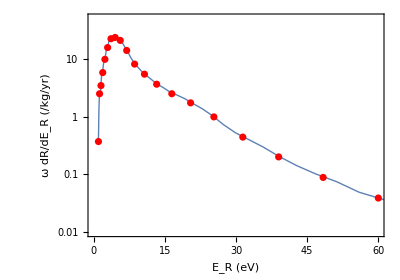
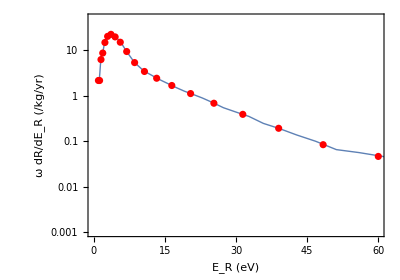

```mathematica
{Show[ListLogPlot[dmMigRatesSi,
FrameLabel->{"E_R (eV)","ω dR/dE_R (/kg/yr)"},
PlotRange->{{0,60},{10^-2,50}},AspectRatio->0.7,
FrameTicks->{LogTicks[10^-2,10^4],Automatic},Joined->True,
PlotLegends->Legend[{"Si impulse (approx.)"}]],
ListLogPlot[dmMigRatesSiFull,PlotStyle->Red,
PlotLegends->Legend[{"Full calc.)"}]]],
Show[ListLogPlot[dmMigRatesGe,
FrameLabel->{"E_R (eV)","ω dR/dE_R (/kg/yr)"},
PlotRange->{{0,60},{10^-3,50}},AspectRatio->0.7,
FrameTicks->{LogTicks[10^-2,10^4],Automatic},Joined->True,
PlotLegends->Legend[{"Ge Impulse (approx.)"}]],
ListLogPlot[dmMigRatesGeFull,PlotStyle->Red,
PlotLegends->Legend[{"Full calc.)"}]]]}
```

To match Fig.2 of 2011.09496

```mathematica
With[{σxn=10^-38 Centimeter^2,mx=100MeV},
{dmMigRatesGeQ,dmMigRatesSiQ}=Table[ParallelTable[{Qi,migRateQ[Qi,mx,σxn,target] tonneYear/1000},
{Qi,Range[1,10]}],{target,{"Ge","Si"}}];]
```

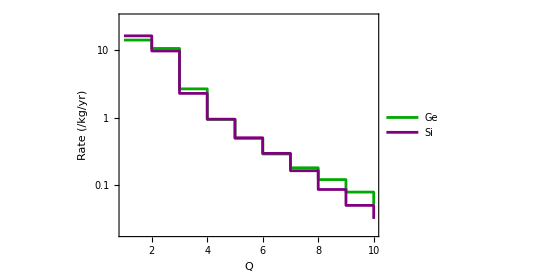

```mathematica
ListLogPlot[{dmMigRatesGeQ,dmMigRatesSiQ},
FrameLabel->{"Q","Rate (/kg/yr)"},AspectRatio->0.7,
PlotRange->{{1,10},{.02,30}},InterpolationOrder->0,
PlotStyle->{Green//Darker,Purple,Orange,Blue,Red,Black},
FrameTicks->{LogTicks[10^-2,10^4],Automatic},Joined->True,
PlotLegends->Legend[{"Ge","Si"}]]
```

### DM core Migdal rate (Free atom approximation)

```mathematica
dRdEmigAtomN[Edet_?NumericQ,target_,mx_?NumericQ,σxp_?NumericQ,Ni_?IntegerQ,quenchingModel_:"Lindhard"]:= Module[{Enl},
If[Edet<$orbitals[target][[-1,2]]keV||Edet≥(EdetMax[mx,mT[target],YQ[.1keV,target,quenchingModel]]),0,
NIntegrate[dRdErNR[ER,Edet-ER YQ[ER,target],target,mx,σxp]*
 Sum[
 Enl=$orbitals[target][[Position[$orbitals[target][[All,1]],orbit][[1,1]],2]]keV;
UnitStep[Edet-ER YQ[ER,target,quenchingModel] -Enl] Znl[target,orbit,Edet-ER YQ[ER,target,quenchingModel] -Enl,√((2ER)/mT[target])],
{orbit,Select[$orbitals[target],(StringContainsQ[#[[1]],ToString[Ni]])&][[All,1]]}],
{ER,ErMinDet[Edet,mx,mT[target],YQ[.1keV,target,quenchingModel]],ErMaxDet[Edet,mx,mT[target],YQ[.1keV,target,quenchingModel]]},PrecisionGoal->3,AccuracyGoal->Infinity]]]

dRdEmigAtom[Edet_?NumericQ,target_,mx_?NumericQ,σxp_?NumericQ,quenchingModel_:"Lindhard"]:= Module[{Enl},
If[Edet<$orbitals[target][[-1,2]]keV||Edet>(EdetMax[mx,mT[target],YQ[.1keV,target,quenchingModel]]),0,
NIntegrate[dRdErNR[ER,Edet-ER YQ[ER,target],target,mx,σxp]*
 Sum[
 Enl=$orbitals[target][[Position[$orbitals[target][[All,1]],orbit][[1,1]],2]]keV;
UnitStep[Edet-ER YQ[ER,target,quenchingModel] -Enl] Znl[target,orbit,Edet-ER YQ[ER,target,quenchingModel] -Enl,√((2ER)/mT[target])],
{orbit,$orbitals[target][[All,1]]}],
{ER,ErMinDet[Edet,mx,mT[target],YQ[.1keV,target,quenchingModel]],ErMaxDet[Edet,mx,mT[target],YQ[.1keV,target,quenchingModel]]},PrecisionGoal->3,AccuracyGoal->Infinity]]]
```

### Total Migdal rate

```mathematica
dRdmdErMigList[EdetMin_?NumericQ,target_,mx_?NumericQ,σxp_?NumericQ,quenchingModel_:"Lindhard",Npoints_:200]:=If[EdetMin<EdetMax[mx,mT[target],YQ[.1keV,target,quenchingModel]],
Table[{Ed/eV,(dRmigdω[Ed,mx,σxp,target]+dRdEmigAtomN[Ed,target,mx,σxp,Switch[target,"Si",2,"Ge",3],quenchingModel])(KilogramDay 365eV)},{Ed,linSpace[EdetMin,EdetMax[mx,mT[target],YQ[.1keV,target,quenchingModel]],Npoints]}],
{}];
```

### Rate comparison

```mathematica
With[{MX=.1GeV,σXP=10^-38 Centimeter^2,
Emin3=Select[geOrbits,(StringContainsQ[#[[1]],ToString[3]])&][[All,2]]keV//Min,
Emin4=Select[geOrbits,(StringContainsQ[#[[1]],ToString[4]])&][[All,2]]keV//Min},

(*NR rate*)
GEdataDMnr=dRdmdErNRlistQ[1eV,"Ge",MX,σXP];

(*Valence rate:*)
dmMigValRatesGe=ParallelTable[{ω/eV,dRmigdω[ω,MX,σXP,"Ge"]KilogramDay 365eV },
{ω,logSpace[1eV,80eV,50]}];


(*Core Migdal rate*)
GEdataDMmig3=Table[{EDET/eV,dRdEmigAtomN[EDET,"Ge",MX,σXP,3](KilogramDay 365eV)},{EDET,logSpace[1.001Emin3,.2keV,200]}];
GEdataDMmig4=Table[{EDET/eV,dRdEmigAtomN[EDET,"Ge",MX,σXP,4](KilogramDay 365eV)},{EDET,logSpace[1.001Emin4,.2keV,200]}];]

With[{MX=.1GeV,σXP=10^-38 Centimeter^2,
Emin2=Select[siOrbits,(StringContainsQ[#[[1]],ToString[2]])&][[All,2]]keV//Min,
Emin3=Select[siOrbits,(StringContainsQ[#[[1]],ToString[3]])&][[All,2]]keV//Min},

(*NR rate*)
SIdataDMnr=dRdmdErNRlistQ[1eV,"Si",MX,σXP];

(*Valence rate:*)
dmMigValRatesSi=ParallelTable[{ω/eV,dRmigdω[ω,MX,σXP,"Si"]KilogramDay 365eV },
{ω,logSpace[1eV,80eV,50]}];

(*Migdal rate*)
Table[{EDET/eV,dRdEmigAtomN[EDET,"Si",MX,σXP,2](KilogramDay 365eV)},{EDET,logSpace[1.001Emin2,.2keV,200]}];
SIdataDMmig2=Table[{EDET/eV,dRdEmigAtomN[EDET,"Si",MX,σXP,2](KilogramDay 365eV)},{EDET,logSpace[1.001Emin2,.2keV,200]}];
SIdataDMmig3=Table[{EDET/eV,dRdEmigAtomN[EDET,"Si",MX,σXP,3](KilogramDay 365eV)},{EDET,logSpace[1.001Emin3,.2keV,200]}];]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

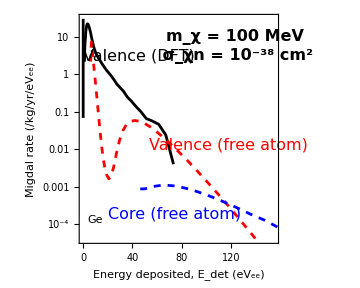
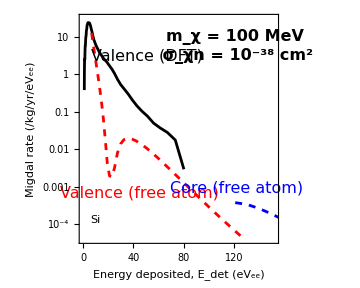

```mathematica
{geMigComp,siMigComp}={ListLogPlot[{dmMigRatesGe,GEdataDMmig4,GEdataDMmig3,GEdataDMnr},
FrameLabel->{"Energy deposited, E_det (eV_ee)","Migdal rate (/kg/yr/eV_ee)"},AspectRatio->.8,ImageSize->360,
PlotRange->{{0,155},{4 10^-5,30}},PlotStyle->{Black,{Red,Dashed},{Blue,Dashed}},
FrameTicks->{LogTicks[10^-6,10^4],Automatic},Joined->True,
Epilog->{Inset[Framed[Style["Ge",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.08,.1}]],Inset[Style["m_χ = 100 MeV\n σ_χn = 10^-38 cm^2",Black,16,Bold],Scaled[{.78,.86}]],Inset[Style["Valence (DFT)",Black,16],Scaled[{.3,.82}]],
Inset[Style["Valence (free atom)",Red,16],Scaled[{.75,.43}]],
Inset[Style["Core (free atom)",Blue,16],Scaled[{.48,.13}]]}],
ListLogPlot[{dmMigRatesSi,SIdataDMmig3,SIdataDMmig2},
FrameLabel->{"Energy deposited, E_det (eV_ee)","Migdal rate (/kg/yr/eV_ee)"},AspectRatio->.8,ImageSize->360,
PlotRange->{{0,152},{4 10^-5,30}},PlotStyle->{Black,{Red,Dashed},{Blue,Dashed}},
FrameTicks->{LogTicks[10^-6,10^4],Automatic},Joined->True,
Epilog->{Inset[Framed[Style[" Si ",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.08,.1}]],Inset[Style["m_χ = 100 MeV\n σ_χn = 10^-38 cm^2",Black,16,Bold],Scaled[{.78,.86}]],Inset[Style["Valence (DFT)",Black,16],Scaled[{.34,.82}]],
Inset[Style["Valence (free atom)",Red,16],Scaled[{.3,.22}]],
Inset[Style["Core (free atom)",Blue,16],Scaled[{.79,.24}]]}]}
```

```mathematica
Export["figures/fig_migComp_ge.pdf",geMigComp];
Export["figures/fig_migComp_si.pdf",siMigComp];
```

## I. DM sensitivity and floors

## Import previously calculated rates

**These files are not included to keep the repository leaner** 

Import the ionization rates below if wanting to skip calculating your own rates.

### ν-electron

#### Core

```mathematica
νERatesGe=Import["results/rates/rate_solarNuE_core_Ge.h5","/Dataset1"];
νERatesSi=Import["results/rates/rate_solarNuE_core_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
νEcoreTotRateGe[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@νERatesGe)));
νEcoreTotRateSi[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@νERatesSi)));
```

#### Valence

```mathematica
νEdftRatesGe=Import["results/rates/rate_solarNuE_valence_Ge.h5","/Dataset1"];
νEdftRatesSi=Import["results/rates/rate_solarNuE_valence_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
νEdftTotRateGe[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@νEdftRatesGe)));
νEdftTotRateSi[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@νEdftRatesSi)));
```

### CEvNS

```mathematica
CEvNSRatesGe=Import["results/rates/rate_solarNu_cevns_Ge.h5","/Dataset1"];
CEvNSRatesSi=Import["results/rates/rate_solarNu_cevns_Si.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
CEvNStotRateGe[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGe));
CEvNStotRateSi[EReV_]=Plus@@(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSi));
```

#### Apply quenching

```mathematica
CEvNSRatesGeQl=ParallelTable[{CEvNSRatesGe[[fluxi,Ej,1]]eV//YQ[#,"Ge","Lindhard"]#/eV&,CEvNSRatesGe[[fluxi,Ej,2]]/YQ[CEvNSRatesGe[[fluxi,Ej,1]]eV,"Ge","Lindhard"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesGe[[fluxi]]]}];
CEvNSRatesSiQl=ParallelTable[{CEvNSRatesSi[[fluxi,Ej,1]]eV//YQ[#,"Si","Lindhard"]#/eV&,CEvNSRatesSi[[fluxi,Ej,2]]/YQ[CEvNSRatesSi[[fluxi,Ej,1]]eV,"Si","Lindhard"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesSi[[fluxi]]]}];
CEvNSRatesGeQs=ParallelTable[{CEvNSRatesGe[[fluxi,Ej,1]]eV//YQ[#,"Ge","Sarkis"]#/eV&,CEvNSRatesGe[[fluxi,Ej,2]]/YQ[CEvNSRatesGe[[fluxi,Ej,1]]eV,"Ge","Sarkis"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesGe[[fluxi]]]}];
CEvNSRatesSiQs=ParallelTable[{CEvNSRatesSi[[fluxi,Ej,1]]eV//YQ[#,"Si","EmpiricalSiCut"]#/eV&,CEvNSRatesSi[[fluxi,Ej,2]]/YQ[CEvNSRatesSi[[fluxi,Ej,1]]eV,"Si","EmpiricalSiCut"]},
{fluxi,1,6},{Ej,1,Length[CEvNSRatesSi[[fluxi]]]}];
 (*pad with zeros to stop extrapolation*)
Do[CEvNSRatesGeQs[[ii]]=Join[DeleteCases[CEvNSRatesGeQs[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesGeQs[[ii,-1,1]],10^-99},{20000,0}}];
CEvNSRatesSiQs[[ii]]=Join[DeleteCases[CEvNSRatesSiQs[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesSiQs[[ii,-1,1]],10^-99},{20000,0}}];,{ii,1,Length[CEvNSRatesGeQs]}]
Do[CEvNSRatesGeQl[[ii]]=Join[DeleteCases[CEvNSRatesGeQl[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesGeQl[[ii,-1,1]],10^-99},{20000,0}}];
CEvNSRatesSiQl[[ii]]=Join[DeleteCases[CEvNSRatesSiQl[[ii]],_?(#[[1]]==0&)],{{1.01CEvNSRatesSiQl[[ii,-1,1]],10^-99},{20000,0}}];,{ii,1,Length[CEvNSRatesGeQl]}]
(*Calculate totals:*)
CEvNStotRateGeQs[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGeQs)));
CEvNStotRateSiQs[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSiQs)));
CEvNStotRateGeQl[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesGeQl)));
CEvNStotRateSiQl[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSRatesSiQl)));
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

### Migdal CEvNS

Valence:

```mathematica
CEvNSmigVRatesGe=Import["results/rates/rate_solarNu_cevnsMigV_Ge.h5","/Dataset1"];
CEvNSmigVRatesSi=Import["results/rates/rate_solarNu_cevnsMigV_Si.h5","/Dataset1"];
```

Core:

```mathematica
CEvNSmigCRatesSi=Import["results/rates/rate_solarNu_cevnsMigC_Si.h5","/Dataset1"];
CEvNSmigCRatesGe=Import["results/rates/rate_solarNu_cevnsMigC_Ge.h5","/Dataset1"];
```

```mathematica
(*Calculate totals:*)
```

```mathematica
CEvNSmigCTotRateGe[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigCRatesGe)));
CEvNSmigCTotRateSi[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]HeavisideTheta[EReV-#[[1,1,1]]]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigCRatesSi)));

CEvNSmigVTotRateGe[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigVRatesGe)));
CEvNSmigVTotRateSi[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}(#[EReV]&/@(Interpolation[#,InterpolationOrder->1]&/@CEvNSmigVRatesSi)));
```

### Total rate functions

```mathematica
νEtotRateGe[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]:=νEcoreTotRateGe[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+νEdftTotRateGe[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+CEvNSmigVTotRateGe[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+CEvNSmigCTotRateGe[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]//Quiet;
νEtotRateSi[EReV_,fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]:=νEcoreTotRateSi[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+νEdftTotRateSi[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+CEvNSmigVTotRateSi[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]+CEvNSmigCTotRateSi[EReV,fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNb8]//Quiet;
```

### DM rates

```mathematica
dmElightRateTableSi=Import["results/dmElightRateTableSi.m"];
dmEheavyRateTableSi=Import["results/dmEheavyRateTableSi.m"];
dmElightRateTableGe=Import["results/dmElightRateTableGe.m"];
dmEheavyRateTableGe=Import["results/dmEheavyRateTableGe.m"];
```

Import::nffil: File results/dmElightRateTableSi.m not found during Import.

Import::nffil: File results/dmEheavyRateTableSi.m not found during Import.

Import::nffil: File results/dmElightRateTableGe.m not found during Import.

Import::nffil: File results/dmEheavyRateTableGe.m not found during Import.

```mathematica
(*Import["data/EXDM_out_example_5.hdf5"]*)
```

## Calculate ionization rates

### Definitions

Convolve with poisson for charge produced during an energy deposit:

```mathematica
poisson[ne_,ni_]=PDF[PoissonDistribution[ne],ni];
```

This fails for large Ne and Ni because of machine precision, keep Ne < 700. This is fine when considering signals of Ni<500.

```mathematica
charge[ni_,RateFeV_,target_]:=If[ni>500,0,NIntegrate[RateFeV[EReV]UnitStep[RateFeV[EReV]] poisson[Ne[EReV eV,target],ni],{EReV,RateFeV[[1,1,1]], 700 ϵ[target]/eV},PrecisionGoal->4,AccuracyGoal->20]//Quiet]
```

```mathematica
chargeList[niMin_,niMax_,RateFeV_,target_]:=Table[charge[ni,RateFeV,target],{ni,niMin,niMax}]
chargeListParallel[niMin_,niMax_,RateFeV_,target_]:=ParallelTable[charge[ni,RateFeV,target],{ni,niMin,niMax}]
```

```mathematica
chargeListDMnr[niMin_,niMax_,mx_,σxp_,target_,quenchingModel_:"Lindhard",Npoints_:200]:=Module[{rateDat,rateDM},
rateDat=dRdmdErNRlistQ[1eV,target,mx,σxp,quenchingModel,Npoints];
If[Length[rateDat]>1,
rateDM=Interpolation[rateDat,InterpolationOrder->1];
Return[chargeListParallel[niMin,niMax,rateDM,target]]
,
Return[{}]];
]

chargeListDMmig[niMin_,niMax_,mx_,σxp_,target_,quenchingModel_:"Lindhard",Npoints_:50]:=Module[{rateDM},
rateDM=dRdmdErMigList[1eV,target,mx,σxp,quenchingModel,Npoints]//Interpolation[#,InterpolationOrder->1]&;
chargeListParallel[niMin,niMax,rateDM,target]
]

chargeListDMe//Clear;
chargeListDMe[niMin_,niMax_,mx_,σe_,target_,mediator_:"heavy",Npoints_:50]:=Module[{rateDM},
rateDM=dRdωList[1eV,mx,σe,target,True,mediator,Npoints]//Interpolation[#,InterpolationOrder->1]&;
chargeListParallel[niMin,niMax,rateDM,target]
]
```

### Create total rate functions

CEvNS rates

```mathematica
CEvNStotChargeRateGeQL[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeListParallel[1,500,Interpolation[CEvNSRatesGeQl[[ii]],InterpolationOrder->1],"Ge"],{ii,1,6}]);
CEvNStotChargeRateGeQS[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeListParallel[1,500,Interpolation[CEvNSRatesGeQs[[ii]],InterpolationOrder->1],"Ge"],{ii,1,6}]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {299.388}. NIntegrate obtained 0.00116432 and 1.30442×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {252.981}. NIntegrate obtained 0.00151442 and 1.53316×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {299.388}. NIntegrate obtained 0.00114425 and 1.26926×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {255.879}. NIntegrate obtained 0.00148838 and 1.48879×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {299.388}. NIntegrate obtained 0.00112446 and 1.32905×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {255.879}. NIntegrate obtained 0.00146205 and 1.48461×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {342.883}. NIntegrate obtained 0.000880494 and 9.81724×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {342.883}. NIntegrate obtained 0.000865235 and 9.93027×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {383.494}. NIntegrate obtained 0.000665128 and 7.64533×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {342.883}. NIntegrate obtained 0.000850247 and 9.58745×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {383.494}. NIntegrate obtained 0.000653522 and 7.80186×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {421.196}. NIntegrate obtained 0.000500942 and 6.00521×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {386.385}. NIntegrate obtained 0.000642102 and 7.56303×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {421.196}. NIntegrate obtained 0.000492024 and 5.83947×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {467.594}. NIntegrate obtained 0.000375527 and 4.92276×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {421.196}. NIntegrate obtained 0.000483302 and 5.55997×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {476.292}. NIntegrate obtained 0.000368871 and 4.60134×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {505.289}. NIntegrate obtained 0.000279832 and 3.44281×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {476.292}. NIntegrate obtained 0.000362207 and 4.90471×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {505.289}. NIntegrate obtained 0.000274752 and 3.04044×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {563.3}. NIntegrate obtained 0.000206977 and 2.87815×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {525.603}. NIntegrate obtained 0.000269603 and 3.20217×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {563.3}. NIntegrate obtained 0.000202987 and 2.77756×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {600.993}. NIntegrate obtained 0.000151664 and 2.34271×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {545.891}. NIntegrate obtained 0.000199194 and 2.41424×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {635.795}. NIntegrate obtained 0.000109956 and 1.49871×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {600.993}. NIntegrate obtained 0.00014869 and 2.25351×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {635.795}. NIntegrate obtained 0.000107727 and 1.46428×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {600.993}. NIntegrate obtained 0.000145772 and 2.20646×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {647.418}. NIntegrate obtained 0.000105536 and 1.4864×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {688.008}. NIntegrate obtained 0.0000787557 and 1.23385×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {688.008}. NIntegrate obtained 0.0000770925 and 1.23333×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {705.406}. NIntegrate obtained 0.0000754789 and 1.12412×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {743.102}. NIntegrate obtained 0.0000556125 and 9.39561×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {743.102}. NIntegrate obtained 0.0000543896 and 9.31427×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {786.6}. NIntegrate obtained 0.0000386458 and 7.24252×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {743.102}. NIntegrate obtained 0.0000531888 and 9.36586×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {786.6}. NIntegrate obtained 0.0000377549 and 7.05136×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {786.6}. NIntegrate obtained 0.000036882 and 6.8444×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {804.011}. NIntegrate obtained 0.0000263723 and 4.16324×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {804.011}. NIntegrate obtained 0.0000257334 and 4.06465×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {864.917}. NIntegrate obtained 0.0000176335 and 3.33716×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {804.011}. NIntegrate obtained 0.0000251073 and 3.87483×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {864.917}. NIntegrate obtained 0.0000171826 and 3.21271×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {908.417}. NIntegrate obtained 0.0000118407 and 2.3501×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {876.524}. NIntegrate obtained 0.0000167411 and 2.96613×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {914.203}. NIntegrate obtained 0.0000115218 and 2.21172×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {934.503}. NIntegrate obtained 7.77745×10^-6 and 1.55881×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {914.203}. NIntegrate obtained 0.0000112103 and 2.13099×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {934.503}. NIntegrate obtained 7.55612×10^-6 and 1.39783×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1004.14}. NIntegrate obtained 4.98516×10^-6 and 9.44289×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {934.503}. NIntegrate obtained 7.34028×10^-6 and 1.29691×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1004.14}. NIntegrate obtained 4.83502×10^-6 and 9.0794×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1004.14}. NIntegrate obtained 4.68898×10^-6 and 9.1297×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1027.34}. NIntegrate obtained 3.11259×10^-6 and 6.68328×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1030.19}. NIntegrate obtained 3.01351×10^-6 and 6.20369×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1033.14}. NIntegrate obtained 2.91721×10^-6 and 5.82228×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1073.73}. NIntegrate obtained 1.88994×10^-6 and 3.78322×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1073.73}. NIntegrate obtained 1.8261×10^-6 and 3.69102×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1073.73}. NIntegrate obtained 1.76436×10^-6 and 3.57586×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 1.11497×10^-6 and 2.45615×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 1.07533×10^-6 and 2.3778×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.12}. NIntegrate obtained 6.39146×10^-7 and 1.26327×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 1.03698×10^-6 and 2.32093×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.73}. NIntegrate obtained 3.56007×10^-7 and 7.64762×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.12}. NIntegrate obtained 6.15227×10^-7 and 1.16752×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.73}. NIntegrate obtained 3.42067×10^-7 and 8.67913×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.12}. NIntegrate obtained 5.92135×10^-7 and 1.30489×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1241.93}. NIntegrate obtained 1.92984×10^-7 and 4.7702×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.73}. NIntegrate obtained 3.28622×10^-7 and 8.3053×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1241.93}. NIntegrate obtained 1.85085×10^-7 and 4.65113×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1268.04}. NIntegrate obtained 1.01824×10^-7 and 2.78417×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1241.93}. NIntegrate obtained 1.77484×10^-7 and 4.42387×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1294.12}. NIntegrate obtained 5.23675×10^-8 and 1.3171×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1268.04}. NIntegrate obtained 9.74865×10^-8 and 2.62993×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1294.12}. NIntegrate obtained 5.00475×10^-8 and 1.24821×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1268.04}. NIntegrate obtained 9.33202×10^-8 and 2.48413×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1337.65}. NIntegrate obtained 4.78261×10^-8 and 1.19336×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {305.182}. NIntegrate obtained 0.00110053 and 1.15376×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {255.886}. NIntegrate obtained 0.00144055 and 1.44415×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {305.182}. NIntegrate obtained 0.00108103 and 1.12758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {255.886}. NIntegrate obtained 0.00141479 and 1.43255×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {305.182}. NIntegrate obtained 0.00106187 and 1.20809×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {337.087}. NIntegrate obtained 0.000826942 and 9.1227×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {273.285}. NIntegrate obtained 0.00131647 and 1.35141×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {386.386}. NIntegrate obtained 0.000632037 and 7.59115×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {386.386}. NIntegrate obtained 0.000620769 and 7.57006×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {421.186}. NIntegrate obtained 0.00047316 and 6.01558×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {386.386}. NIntegrate obtained 0.000609697 and 7.59647×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {421.186}. NIntegrate obtained 0.000464595 and 5.8808×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {461.795}. NIntegrate obtained 0.000352597 and 4.58756×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {429.883}. NIntegrate obtained 0.000456217 and 5.95847×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {519.793}. NIntegrate obtained 0.000261062 and 3.57693×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {360.279}. NIntegrate obtained 0.000742784 and 7.61366×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {482.091}. NIntegrate obtained 0.00034605 and 4.53441×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {360.279}. NIntegrate obtained 0.00072959 and 7.50215×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {519.793}. NIntegrate obtained 0.000256196 and 3.32543×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {560.401}. NIntegrate obtained 0.000191701 and 2.44153×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {482.091}. NIntegrate obtained 0.000339675 and 4.392×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {519.793}. NIntegrate obtained 0.000251335 and 3.74026×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {560.401}. NIntegrate obtained 0.000188003 and 2.31584×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.102}. NIntegrate obtained 0.000139639 and 1.92289×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {560.401}. NIntegrate obtained 0.000184495 and 2.39129×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.102}. NIntegrate obtained 0.000136844 and 1.85968×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {653.195}. NIntegrate obtained 0.000100506 and 1.6146×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.102}. NIntegrate obtained 0.000134092 and 1.86897×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {653.195}. NIntegrate obtained 0.0000984221 and 1.57475×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {653.195}. NIntegrate obtained 0.0000963909 and 1.46154×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {676.418}. NIntegrate obtained 0.0000714196 and 9.19045×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {711.221}. NIntegrate obtained 0.0000698804 and 9.14149×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {734.411}. NIntegrate obtained 0.0000500112 and 8.29168×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {711.221}. NIntegrate obtained 0.0000683674 and 9.34209×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {734.411}. NIntegrate obtained 0.0000488829 and 8.38507×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {798.204}. NIntegrate obtained 0.0000344264 and 5.33342×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {743.112}. NIntegrate obtained 0.0000477772 and 7.92959×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {798.204}. NIntegrate obtained 0.0000336123 and 5.50574×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {827.214}. NIntegrate obtained 0.0000232546 and 3.98358×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {798.204}. NIntegrate obtained 0.0000328154 and 5.52279×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {859.119}. NIntegrate obtained 0.0000153741 and 2.7988×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {827.214}. NIntegrate obtained 0.0000226757 and 3.99147×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {873.607}. NIntegrate obtained 0.0000149702 and 2.73543×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {827.214}. NIntegrate obtained 0.0000221079 and 3.94069×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {908.422}. NIntegrate obtained 0.0000102049 and 1.94842×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {873.607}. NIntegrate obtained 0.0000145754 and 2.66616×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {908.422}. NIntegrate obtained 9.9219×10^-6 and 1.88725×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {943.215}. NIntegrate obtained 6.61873×10^-6 and 1.25187×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {908.422}. NIntegrate obtained 9.64585×10^-6 and 1.77921×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {943.215}. NIntegrate obtained 6.42475×10^-6 and 1.19775×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {986.73}. NIntegrate obtained 4.18561×10^-6 and 8.41254×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {960.618}. NIntegrate obtained 6.23704×10^-6 and 1.1×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {986.73}. NIntegrate obtained 4.05563×10^-6 and 8.29203×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {986.73}. NIntegrate obtained 3.92937×10^-6 and 7.666×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1036.03}. NIntegrate obtained 2.57704×10^-6 and 5.38479×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1036.03}. NIntegrate obtained 2.49241×10^-6 and 5.28287×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1036.03}. NIntegrate obtained 2.41028×10^-6 and 4.84483×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1065.02}. NIntegrate obtained 1.54131×10^-6 and 3.52925×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1065.02}. NIntegrate obtained 1.48783×10^-6 and 3.42833×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1076.63}. NIntegrate obtained 1.43584×10^-6 and 3.3115×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 8.95254×10^-7 and 1.81909×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 8.62523×10^-7 and 2.06485×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1146.23}. NIntegrate obtained 5.05374×10^-7 and 1.15994×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1178.11}. NIntegrate obtained 2.77174×10^-7 and 6.07591×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1108.53}. NIntegrate obtained 8.3089×10^-7 and 2.0067×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1166.54}. NIntegrate obtained 4.85961×10^-7 and 1.10057×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1178.11}. NIntegrate obtained 2.66043×10^-7 and 6.47158×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1166.54}. NIntegrate obtained 4.67252×10^-7 and 1.08254×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1210.04}. NIntegrate obtained 2.55318×10^-7 and 6.18815×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1227.45}. NIntegrate obtained 1.47912×10^-7 and 4.05056×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1227.45}. NIntegrate obtained 1.41715×10^-7 and 3.84957×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1276.73}. NIntegrate obtained 7.69205×10^-8 and 1.95226×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1227.45}. NIntegrate obtained 1.35763×10^-7 and 3.68864×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1276.73}. NIntegrate obtained 7.35703×10^-8 and 1.79375×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1276.73}. NIntegrate obtained 7.03585×10^-8 and 1.79088×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1314.43}. NIntegrate obtained 3.89378×10^-8 and 1.11298×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1314.43}. NIntegrate obtained 3.71746×10^-8 and 1.03466×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1314.43}. NIntegrate obtained 3.54837×10^-8 and 1.01×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
CEvNStotChargeRateSiQL[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeListParallel[1,500,Interpolation[CEvNSRatesSiQl[[ii]],InterpolationOrder->1],"Si"],{ii,1,6}]);
CEvNStotChargeRateSiQS[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}
Table[chargeListParallel[1,500,Interpolation[CEvNSRatesSiQs[[ii]],InterpolationOrder->1],"Si"],{ii,1,6}]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7109}. NIntegrate obtained 6.67511×10^-10 and 6.75225×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7109}. NIntegrate obtained 1.8075×10^-10 and 1.97149×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7109}. NIntegrate obtained 2.92309×10^-12 and 3.8003×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 2.61725×10^-13 and 5.03094×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 7.54028×10^-14 and 1.43002×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 2.1231×10^-14 and 3.70199×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 2.27576×10^-9 and 2.37361×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 8.02113×10^-10 and 8.93264×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5114}. NIntegrate obtained 2.75172×10^-10 and 3.32174×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {371.924}. NIntegrate obtained 0.00046866 and 4.75378×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {317.934}. NIntegrate obtained 0.000524844 and 5.27452×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {379.129}. NIntegrate obtained 0.000465219 and 4.7065×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {379.129}. NIntegrate obtained 0.000461809 and 4.83219×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {415.129}. NIntegrate obtained 0.0004174 and 4.37758×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {415.129}. NIntegrate obtained 0.000414443 and 4.32903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {343.124}. NIntegrate obtained 0.000501208 and 5.1128×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {415.129}. NIntegrate obtained 0.000411514 and 4.22983×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {285.526}. NIntegrate obtained 0.000558865 and 5.59453×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {343.124}. NIntegrate obtained 0.00049754 and 5.25128×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {472.736}. NIntegrate obtained 0.000373182 and 4.26159×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {526.744}. NIntegrate obtained 0.000334822 and 4.40066×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {472.736}. NIntegrate obtained 0.00037067 and 4.12082×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {526.744}. NIntegrate obtained 0.000332587 and 4.33432×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.74}. NIntegrate obtained 0.000301184 and 3.65617×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {494.34}. NIntegrate obtained 0.000368132 and 4.25387×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {551.937}. NIntegrate obtained 0.000330247 and 4.13022×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.74}. NIntegrate obtained 0.000299217 and 3.70978×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {634.735}. NIntegrate obtained 0.000271539 and 3.53161×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {598.74}. NIntegrate obtained 0.000297149 and 3.73692×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {634.735}. NIntegrate obtained 0.000269888 and 3.30761×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {706.75}. NIntegrate obtained 0.000245267 and 3.4509×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {663.537}. NIntegrate obtained 0.000268163 and 3.49699×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {753.548}. NIntegrate obtained 0.000221865 and 3.20449×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {706.75}. NIntegrate obtained 0.000243724 and 3.35571×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {710.33}. NIntegrate obtained 0.000242187 and 2.72622×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {753.548}. NIntegrate obtained 0.000220488 and 3.16118×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {807.562}. NIntegrate obtained 0.000200929 and 3.00818×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {764.34}. NIntegrate obtained 0.000219255 and 2.56749×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {807.562}. NIntegrate obtained 0.000199699 and 2.89488×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {807.562}. NIntegrate obtained 0.000198476 and 2.77667×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {872.352}. NIntegrate obtained 0.000182214 and 2.59095×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {872.352}. NIntegrate obtained 0.000181105 and 2.55566×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {872.352}. NIntegrate obtained 0.000180012 and 2.53225×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {926.364}. NIntegrate obtained 0.000165323 and 2.48349×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {926.364}. NIntegrate obtained 0.00016437 and 2.49287×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {980.379}. NIntegrate obtained 0.000150186 and 2.29304×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {926.364}. NIntegrate obtained 0.000163426 and 2.28467×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {980.379}. NIntegrate obtained 0.000149327 and 2.22027×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {980.379}. NIntegrate obtained 0.000148395 and 2.29586×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1037.95}. NIntegrate obtained 0.000136504 and 2.02601×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1037.95}. NIntegrate obtained 0.000135692 and 2.04112×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1102.76}. NIntegrate obtained 0.000124095 and 1.91485×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1016.38}. NIntegrate obtained 0.00013493 and 1.83769×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1102.76}. NIntegrate obtained 0.000123375 and 1.8679×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.58}. NIntegrate obtained 0.000113542 and 1.76692×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1102.76}. NIntegrate obtained 0.000122645 and 1.91632×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.58}. NIntegrate obtained 0.000112856 and 1.75276×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1149.58}. NIntegrate obtained 0.000112188 and 1.79436×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.17}. NIntegrate obtained 0.000103902 and 1.69663×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.17}. NIntegrate obtained 0.000103291 and 1.62308×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1250.39}. NIntegrate obtained 0.0000951112 and 1.55166×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1189.17}. NIntegrate obtained 0.000102684 and 1.57019×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1250.39}. NIntegrate obtained 0.0000945524 and 1.58689×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1250.39}. NIntegrate obtained 0.0000940101 and 1.56038×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1315.19}. NIntegrate obtained 0.0000870529 and 1.2947×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1315.19}. NIntegrate obtained 0.0000865407 and 1.39587×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1315.19}. NIntegrate obtained 0.0000860319 and 1.42268×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1347.57}. NIntegrate obtained 0.0000796819 and 1.2736×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1347.57}. NIntegrate obtained 0.0000792136 and 1.29103×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1412.38}. NIntegrate obtained 0.0000729528 and 1.27092×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1347.57}. NIntegrate obtained 0.0000787479 and 1.28663×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1412.38}. NIntegrate obtained 0.0000725225 and 1.24366×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1412.38}. NIntegrate obtained 0.0000721025 and 1.31665×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1466.39}. NIntegrate obtained 0.000066763 and 1.28372×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1516.79}. NIntegrate obtained 0.0000610939 and 1.00453×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1466.39}. NIntegrate obtained 0.0000663704 and 1.3426×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1516.79}. NIntegrate obtained 0.000060733 and 1.06931×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1466.39}. NIntegrate obtained 0.0000659825 and 1.2978×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1570.78}. NIntegrate obtained 0.0000558824 and 8.76874×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1516.79}. NIntegrate obtained 0.0000603743 and 1.04965×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1570.78}. NIntegrate obtained 0.0000555681 and 1.03799×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1570.78}. NIntegrate obtained 0.0000552394 and 1.02175×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1621.18}. NIntegrate obtained 0.0000511308 and 9.06655×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1621.18}. NIntegrate obtained 0.0000508273 and 9.14823×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1668.}. NIntegrate obtained 0.0000467563 and 9.50351×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1621.18}. NIntegrate obtained 0.0000505261 and 9.18807×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1668.}. NIntegrate obtained 0.0000464792 and 9.13872×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1668.}. NIntegrate obtained 0.0000462024 and 8.96582×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5104}. NIntegrate obtained 1.09606×10^-8 and 1.55763×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5104}. NIntegrate obtained 2.57541×10^-9 and 3.95446×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5104}. NIntegrate obtained 5.81461×10^-10 and 8.50923×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5104}. NIntegrate obtained 4.46855×10^-8 and 4.67137×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31019}. NIntegrate obtained 5.68245×10^-13 and 6.26097×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31019}. NIntegrate obtained 1.37388×10^-14 and 1.77201×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31019}. NIntegrate obtained 2.01222×10^-15 and 2.25053×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31019}. NIntegrate obtained 3.45557×10^-12 and 3.54562×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {454.738}. NIntegrate obtained 0.000477461 and 4.94506×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {310.725}. NIntegrate obtained 0.000547521 and 6.38383×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {310.725}. NIntegrate obtained 0.00054271 and 6.04758×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {454.738}. NIntegrate obtained 0.000473518 and 4.82018×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {325.127}. NIntegrate obtained 0.000537962 and 5.51984×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {454.738}. NIntegrate obtained 0.000469629 and 4.71651×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {278.328}. NIntegrate obtained 0.000610721 and 6.16954×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {278.328}. NIntegrate obtained 0.000605039 and 6.38512×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {433.136}. NIntegrate obtained 0.000419609 and 4.53311×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {278.328}. NIntegrate obtained 0.000599437 and 6.69865×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {433.136}. NIntegrate obtained 0.000416329 and 4.97933×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {433.136}. NIntegrate obtained 0.000413061 and 4.97588×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {487.131}. NIntegrate obtained 0.000370972 and 4.6036×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {245.929}. NIntegrate obtained 0.000665943 and 7.20225×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {487.131}. NIntegrate obtained 0.000368189 and 4.73853×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {530.333}. NIntegrate obtained 0.00032962 and 4.39657×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {245.929}. NIntegrate obtained 0.000659419 and 6.89612×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {487.131}. NIntegrate obtained 0.000365437 and 4.76379×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {245.929}. NIntegrate obtained 0.000653004 and 6.68723×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {530.333}. NIntegrate obtained 0.000327235 and 4.28543×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {587.944}. NIntegrate obtained 0.000294033 and 4.29272×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {530.333}. NIntegrate obtained 0.000324971 and 4.01203×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {595.133}. NIntegrate obtained 0.000292095 and 3.91582×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {641.938}. NIntegrate obtained 0.000263136 and 3.81521×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {587.944}. NIntegrate obtained 0.000289939 and 4.3394×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {656.344}. NIntegrate obtained 0.000261378 and 3.96894×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {699.545}. NIntegrate obtained 0.000236155 and 3.86199×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {757.155}. NIntegrate obtained 0.000212435 and 3.58656×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {656.344}. NIntegrate obtained 0.000259647 and 3.71662×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {699.545}. NIntegrate obtained 0.000234581 and 3.92951×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {757.155}. NIntegrate obtained 0.000211052 and 3.51789×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {807.571}. NIntegrate obtained 0.000191618 and 2.92541×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {699.545}. NIntegrate obtained 0.000233065 and 3.6764×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {757.155}. NIntegrate obtained 0.000209685 and 3.42065×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {811.146}. NIntegrate obtained 0.000190224 and 3.201×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {811.146}. NIntegrate obtained 0.000189003 and 2.94236×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {865.148}. NIntegrate obtained 0.000172849 and 3.03495×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {865.148}. NIntegrate obtained 0.000171756 and 3.00815×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {865.148}. NIntegrate obtained 0.000170673 and 2.86326×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {919.14}. NIntegrate obtained 0.000156244 and 2.47284×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {922.741}. NIntegrate obtained 0.000155269 and 2.52662×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {962.357}. NIntegrate obtained 0.000141483 and 2.41996×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {926.343}. NIntegrate obtained 0.000154303 and 2.51824×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {962.357}. NIntegrate obtained 0.000140611 and 2.43488×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1034.37}. NIntegrate obtained 0.000128199 and 2.46379×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {962.357}. NIntegrate obtained 0.000139736 and 2.32887×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1034.37}. NIntegrate obtained 0.000127419 and 2.43419×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1084.77}. NIntegrate obtained 0.000116266 and 1.73425×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1034.37}. NIntegrate obtained 0.00012664 and 2.345×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1091.97}. NIntegrate obtained 0.000115514 and 2.13386×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1135.16}. NIntegrate obtained 0.000106155 and 1.72047×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1113.57}. NIntegrate obtained 0.000114921 and 1.77453×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1196.37}. NIntegrate obtained 0.0000969696 and 1.76735×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1135.16}. NIntegrate obtained 0.000105517 and 1.67202×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1196.37}. NIntegrate obtained 0.0000963889 and 1.75759×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1160.37}. NIntegrate obtained 0.000104874 and 1.86771×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1243.2}. NIntegrate obtained 0.0000886173 and 1.63226×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1199.98}. NIntegrate obtained 0.0000957898 and 1.74738×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1243.2}. NIntegrate obtained 0.0000881033 and 1.64689×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1253.97}. NIntegrate obtained 0.0000875768 and 1.64701×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1311.57}. NIntegrate obtained 0.0000810384 and 1.53553×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1311.57}. NIntegrate obtained 0.0000805574 and 1.58346×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1311.57}. NIntegrate obtained 0.0000800781 and 1.60344×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1340.41}. NIntegrate obtained 0.0000741159 and 1.48009×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1340.41}. NIntegrate obtained 0.0000736762 and 1.42114×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1405.22}. NIntegrate obtained 0.0000677907 and 1.31964×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1340.41}. NIntegrate obtained 0.0000732387 and 1.41307×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1405.22}. NIntegrate obtained 0.000067388 and 1.29698×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1412.37}. NIntegrate obtained 0.0000669895 and 1.29287×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1451.98}. NIntegrate obtained 0.0000620163 and 1.25356×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1509.58}. NIntegrate obtained 0.0000567324 and 1.02715×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1462.79}. NIntegrate obtained 0.0000616504 and 1.23508×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1509.58}. NIntegrate obtained 0.0000563948 and 1.03993×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1480.79}. NIntegrate obtained 0.000061312 and 1.10434×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1516.83}. NIntegrate obtained 0.0000560722 and 1.11758×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1556.39}. NIntegrate obtained 0.0000519125 and 1.05735×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1581.62}. NIntegrate obtained 0.0000516058 and 1.07267×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1617.61}. NIntegrate obtained 0.0000474954 and 9.07884×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1581.62}. NIntegrate obtained 0.0000513008 and 1.07799×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1617.61}. NIntegrate obtained 0.0000472144 and 9.02996×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1675.19}. NIntegrate obtained 0.0000434467 and 8.70244×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1617.61}. NIntegrate obtained 0.0000469354 and 9.22467×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1675.19}. NIntegrate obtained 0.0000431892 and 8.83811×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1675.19}. NIntegrate obtained 0.0000429335 and 8.77778×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Migdal rates

```mathematica
CEvNSmigCoreTotChargeRateGe[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeList[1,500,Interpolation[CEvNSmigCRatesGe[[ii]],InterpolationOrder->1],"Ge"],{ii,1,6}]);
CEvNSmigCoreTotChargeRateSi[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeList[1,500,Interpolation[CEvNSmigCRatesSi[[ii]],InterpolationOrder->1],"Si"],{ii,1,6}]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0717}. NIntegrate obtained 3.13467×10^-15 and 7.20423×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0717}. NIntegrate obtained 2.61863×10^-14 and 6.34558×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0717}. NIntegrate obtained 1.46569×10^-13 and 3.42066×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.91169214268}. NIntegrate obtained 5.65354×10^-17 and 1.55883×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.91169214268}. NIntegrate obtained 2.7534×10^-16 and 7.2286×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.91169214268}. NIntegrate obtained 1.17491×10^-15 and 3.08656×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
CEvNSmigValTotChargeRateGe[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeList[1,500,Interpolation[CEvNSmigVRatesGe[[ii]],InterpolationOrder->1],"Ge"],{ii,1,6}]);
CEvNSmigValTotChargeRateSi[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeList[1,500,Interpolation[CEvNSmigVRatesSi[[ii]],InterpolationOrder->1],"Si"],{ii,1,6}]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4742}. NIntegrate obtained 7.27925×10^-11 and 8.02515×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4742}. NIntegrate obtained 5.02283×10^-11 and 5.67193×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4742}. NIntegrate obtained 3.39585×10^-11 and 4.74291×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.5129}. NIntegrate obtained 2.77757×10^-11 and 3.47214×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.5129}. NIntegrate obtained 1.80296×10^-11 and 2.21414×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.5129}. NIntegrate obtained 1.14386×10^-11 and 1.59247×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Electron scattering rates

```mathematica
νEcoreTotChargeRateGe[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeListParallel[1,500,Interpolation[νERatesGe[[ii]],InterpolationOrder->1],"Ge"],{ii,1,6}]);
νEcoreTotChargeRateSi[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno,fluxNb8}Table[chargeListParallel[1,500,Interpolation[νERatesSi[[ii]],InterpolationOrder->1],"Si"],{ii,1,6}]);
```

```mathematica
νEvalTotChargeRateGe[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno}Table[chargeList[1,500,Interpolation[νEdftRatesGe[[ii]],InterpolationOrder->1],"Ge"],{ii,1,5}]);
νEvalTotChargeRateSi[fluxNpp_:1,fluxNbe7_:1,fluxNpep_:1,fluxNcno_:1,fluxNb8_:1]=Plus@@({fluxNpp,fluxNbe7,fluxNpep,fluxNcno,fluxNcno}Table[chargeList[1,500,Interpolation[νEdftRatesSi[[ii]],InterpolationOrder->1],"Si"],{ii,1,5}]);
```

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

DM rates:

```mathematica
dmMigChargeRateTableSiL=Table[{MX/MeV,chargeListDMmig[1,40,MX,10^-40 Centimeter^2,"Si","Lindhard",150]},{MX,logSpace[.01,1,100]}];
dmMigChargeRateTableSiS=Table[{MX/MeV,chargeListDMmig[1,40,MX,10^-40 Centimeter^2,"Si","EmpiricalSiCut",150]},{MX,logSpace[.01,1,100]}];
dmMigChargeRateTableGeL=Table[{MX/MeV,chargeListDMmig[1,40,MX,10^-40 Centimeter^2,"Ge","Lindhard",150]},{MX,logSpace[.01,1,100]}];
dmMigChargeRateTableGeS=Table[{MX/MeV,chargeListDMmig[1,40,MX,10^-40 Centimeter^2,"Ge","Sarkis",150]},{MX,logSpace[.01,1,100]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71041}. NIntegrate obtained 0.00212089 and 2.54499×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052}. NIntegrate obtained 0.0011362 and 1.15154×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052}. NIntegrate obtained 0.00240027 and 2.58526×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71027}. NIntegrate obtained 0.00129442 and 1.35909×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71027}. NIntegrate obtained 0.00271827 and 2.97147×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71033}. NIntegrate obtained 0.00163181 and 2.09221×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71033}. NIntegrate obtained 0.00339147 and 4.38489×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71019}. NIntegrate obtained 0.00183532 and 1.90745×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71023}. NIntegrate obtained 0.00458685 and 5.68194×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71132}. NIntegrate obtained 0.00505279 and 5.71449×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052}. NIntegrate obtained 0.00547085 and 5.75516×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71144}. NIntegrate obtained 0.00592905 and 6.55876×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71172}. NIntegrate obtained 0.00347866 and 3.78643×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71177}. NIntegrate obtained 0.00372779 and 3.80184×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71177}. NIntegrate obtained 0.00747254 and 8.84415×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71162}. NIntegrate obtained 0.00404101 and 6.35682×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71162}. NIntegrate obtained 0.00809013 and 1.06521×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71162}. NIntegrate obtained 0.00206732 and 2.37863×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71166}. NIntegrate obtained 0.0170586 and 2.0262×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71166}. NIntegrate obtained 0.00434189 and 7.0439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3116}. NIntegrate obtained 0.0011989 and 1.33182×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71166}. NIntegrate obtained 0.00867255 and 1.45537×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71166}. NIntegrate obtained 0.00222814 and 3.20787×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71109357598625}. NIntegrate obtained 0.0193447 and 2.42736×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71109357598625}. NIntegrate obtained 0.00992928 and 1.33618×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71109357598625}. NIntegrate obtained 0.00500936 and 6.92902×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71109357598625}. NIntegrate obtained 0.00258782 and 2.73826×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31189}. NIntegrate obtained 0.00149854 and 1.84345×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31189}. NIntegrate obtained 0.00275052 and 3.01544×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71038}. NIntegrate obtained 0.0215724 and 2.46283×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71038}. NIntegrate obtained 0.00565966 and 9.50516×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71038}. NIntegrate obtained 0.011141 and 2.04034×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71038}. NIntegrate obtained 0.00294758 and 4.50686×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71044}. NIntegrate obtained 0.02312 and 3.26341×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71044}. NIntegrate obtained 0.00613034 and 1.18303×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71044}. NIntegrate obtained 0.0120224 and 2.41214×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71044}. NIntegrate obtained 0.00319603 and 4.31575×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31125}. NIntegrate obtained 0.00186004 and 2.78443×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31125}. NIntegrate obtained 0.00649477 and 7.49225×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00107343 and 1.10574×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31125}. NIntegrate obtained 0.00339331 and 5.02476×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71157}. NIntegrate obtained 0.0261098 and 5.34848×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71157}. NIntegrate obtained 0.00691627 and 1.80492×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31078}. NIntegrate obtained 0.00198989 and 2.99997×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.000272465 and 3.02651×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.000430698 and 4.82866×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71157}. NIntegrate obtained 0.0135502 and 4.06588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71157}. NIntegrate obtained 0.00362024 and 8.46865×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31078}. NIntegrate obtained 0.0011518 and 1.26843×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71039}. NIntegrate obtained 0.0279455 and 4.54992×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71039}. NIntegrate obtained 0.00741266 and 1.37034×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31262}. NIntegrate obtained 0.00213986 and 2.75403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9117}. NIntegrate obtained 0.000750231 and 7.61046×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.712}. NIntegrate obtained 0.000295704 and 3.17705×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.712}. NIntegrate obtained 0.000124959 and 1.25286×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71039}. NIntegrate obtained 0.0145083 and 3.18202×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71039}. NIntegrate obtained 0.00388572 and 6.91254×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9117}. NIntegrate obtained 0.00124135 and 1.37724×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.712}. NIntegrate obtained 0.000190672 and 2.09878×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71061}. NIntegrate obtained 0.0290257 and 4.38581×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71061}. NIntegrate obtained 0.00781454 and 1.50376×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31123}. NIntegrate obtained 0.00228362 and 3.68339×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71061}. NIntegrate obtained 0.015171 and 3.27676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31123}. NIntegrate obtained 0.00412654 and 8.37017×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31123}. NIntegrate obtained 0.00132856 and 1.48384×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71284}. NIntegrate obtained 0.0306041 and 5.94477×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71284}. NIntegrate obtained 0.00830624 and 1.65233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31044}. NIntegrate obtained 0.00244054 and 3.61864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9115}. NIntegrate obtained 0.000864669 and 9.69986×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7113}. NIntegrate obtained 0.000344162 and 3.68682×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7113}. NIntegrate obtained 0.000147212 and 1.75169×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71284}. NIntegrate obtained 0.0160761 and 3.39487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71284}. NIntegrate obtained 0.0043975 and 8.60521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9115}. NIntegrate obtained 0.00142399 and 1.96312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5126}. NIntegrate obtained 0.000539976 and 5.7283×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7113}. NIntegrate obtained 0.000223184 and 2.78017×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70939518554536}. NIntegrate obtained 0.0324143 and 7.04196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70939518554536}. NIntegrate obtained 0.00883384 and 2.02365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31116}. NIntegrate obtained 0.00259871 and 4.07262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9119}. NIntegrate obtained 0.000926269 and 1.16816×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.311}. NIntegrate obtained 0.000159689 and 1.64114×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70939518554536}. NIntegrate obtained 0.017087 and 3.71168×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31116}. NIntegrate obtained 0.00467721 and 9.37351×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9119}. NIntegrate obtained 0.00152023 and 2.11094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5126}. NIntegrate obtained 0.00058043 and 7.03194×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0348132 and 8.18434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.00950015 and 3.12356×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31057}. NIntegrate obtained 0.0027942 and 3.69959×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0183666 and 6.19086×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0050301 and 1.26069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31057}. NIntegrate obtained 0.00163436 and 1.95666×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0373957 and 7.17365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0101707 and 2.57353×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31332}. NIntegrate obtained 0.00299138 and 4.65562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00106853 and 1.26632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.00043043 and 4.89213×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7111}. NIntegrate obtained 0.00018679 and 1.99515×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0196857 and 4.9259×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0053832 and 1.16393×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00175113 and 2.56086×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.000671089 and 7.04057×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7111}. NIntegrate obtained 0.000281065 and 3.30769×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71081}. NIntegrate obtained 0.0401278 and 8.94996×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71081}. NIntegrate obtained 0.0109157 and 2.74331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31227}. NIntegrate obtained 0.00320648 and 6.88994×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.511}. NIntegrate obtained 0.00114554 and 1.49412×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1124}. NIntegrate obtained 0.000463397 and 6.70816×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1124}. NIntegrate obtained 0.000202113 and 2.03259×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71081}. NIntegrate obtained 0.0700266 and 7.0662×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71081}. NIntegrate obtained 0.0211204 and 5.95294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31227}. NIntegrate obtained 0.00577606 and 1.41946×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31227}. NIntegrate obtained 0.00187621 and 2.93324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1124}. NIntegrate obtained 0.000720739 and 1.03623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1124}. NIntegrate obtained 0.000303368 and 4.0598×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71111}. NIntegrate obtained 0.0419173 and 0.0000104398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71111}. NIntegrate obtained 0.0115267 and 3.8527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31207}. NIntegrate obtained 0.00342116 and 7.3081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.913}. NIntegrate obtained 0.00122821 and 1.56962×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7115}. NIntegrate obtained 0.000497723 and 6.35536×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3124}. NIntegrate obtained 0.000217783 and 2.58051×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3124}. NIntegrate obtained 0.000102573 and 1.02928×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71111}. NIntegrate obtained 0.0727993 and 7.72321×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71111}. NIntegrate obtained 0.0221799 and 7.80432×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71111}. NIntegrate obtained 0.00613305 and 1.44916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31207}. NIntegrate obtained 0.00200819 and 3.2862×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1116087026093}. NIntegrate obtained 0.00077345 and 8.26275×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7115}. NIntegrate obtained 0.000326267 and 4.4437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3124}. NIntegrate obtained 0.000148081 and 1.65978×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.044115 and 0.0000126986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.0122044 and 5.49761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.00364548 and 7.0194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.00131866 and 2.07143×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1134}. NIntegrate obtained 0.00053733 and 8.16757×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3116}. NIntegrate obtained 0.000235981 and 2.72801×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.07623 and 9.35829×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.0234232 and 0.0000100592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71222}. NIntegrate obtained 0.00651206 and 1.96732×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.00214823 and 2.83555×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.000832983 and 1.22634×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1134}. NIntegrate obtained 0.000352935 and 4.21106×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3116}. NIntegrate obtained 0.000160706 and 1.73722×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00386481 and 5.68141×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00140296 and 2.17496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.00057447 and 8.72862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.000253676 and 3.90862×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1117}. NIntegrate obtained 0.0000447059 and 4.69313×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00689379 and 8.47012×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00228112 and 3.22725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.000888259 and 9.72909×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.00037836 and 5.93186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3111}. NIntegrate obtained 0.000173222 and 1.97198×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71392}. NIntegrate obtained 0.0485542 and 0.000014915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71392}. NIntegrate obtained 0.013598 and 3.89985×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31135}. NIntegrate obtained 0.00412207 and 1.02182×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5113}. NIntegrate obtained 0.00150535 and 2.32262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7112}. NIntegrate obtained 0.000617793 and 8.85407×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7112}. NIntegrate obtained 0.000273456 and 4.22299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3137}. NIntegrate obtained 0.000130362 and 1.48844×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71392}. NIntegrate obtained 0.0837184 and 8.58148×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71392}. NIntegrate obtained 0.0259094 and 8.63456×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31135}. NIntegrate obtained 0.00731256 and 2.22714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31135}. NIntegrate obtained 0.00244222 and 4.73024×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5113}. NIntegrate obtained 0.000954329 and 1.40031×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7112}. NIntegrate obtained 0.000407328 and 6.53649×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3137}. NIntegrate obtained 0.000187045 and 2.36128×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31387}. NIntegrate obtained 0.0146545 and 3.32433×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.511}. NIntegrate obtained 0.00162245 and 2.4854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.312}. NIntegrate obtained 0.000667104 and 8.41188×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.312}. NIntegrate obtained 0.000295986 and 4.08602×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.312}. NIntegrate obtained 0.0001415 and 1.78666×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.113}. NIntegrate obtained 0.0000726197 and 7.82599×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.113}. NIntegrate obtained 0.0000531557 and 5.84504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.113}. NIntegrate obtained 0.0000393337 and 3.99972×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31387}. NIntegrate obtained 0.00444036 and 1.12835×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31387}. NIntegrate obtained 0.0278969 and 3.66918×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31387}. NIntegrate obtained 0.00787962 and 1.95965×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.511}. NIntegrate obtained 0.00102937 and 1.38274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.312}. NIntegrate obtained 0.000440324 and 5.9159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.312}. NIntegrate obtained 0.000202731 and 2.93971×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31387}. NIntegrate obtained 0.00263085 and 4.93985×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.130247 and 0.0000142146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.0563436 and 0.0000193395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.0160025 and 6.61266×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31111}. NIntegrate obtained 0.00480206 and 1.20531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9139}. NIntegrate obtained 0.00173685 and 2.61893×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1138}. NIntegrate obtained 0.000713406 and 1.31009×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3138}. NIntegrate obtained 0.000317762 and 4.89546×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3138}. NIntegrate obtained 0.000152601 and 1.77234×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5138}. NIntegrate obtained 0.0000786396 and 8.83999×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.0955399 and 0.0000133292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.0303988 and 0.0000131748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71391}. NIntegrate obtained 0.00857649 and 2.95633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9139}. NIntegrate obtained 0.00282746 and 5.79657×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1138}. NIntegrate obtained 0.00110035 and 1.89028×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1138}. NIntegrate obtained 0.000471693 and 7.93302×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3138}. NIntegrate obtained 0.000218143 and 2.6575×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5138}. NIntegrate obtained 0.000108679 and 1.25036×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31478}. NIntegrate obtained 0.0170347 and 3.84336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31478}. NIntegrate obtained 0.00513754 and 1.13875×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5131}. NIntegrate obtained 0.00186386 and 4.099×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1123}. NIntegrate obtained 0.000766932 and 1.44785×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7115}. NIntegrate obtained 0.000342233 and 5.39214×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.114}. NIntegrate obtained 0.0000853575 and 9.95669×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7132}. NIntegrate obtained 0.0000627436 and 6.47721×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7132}. NIntegrate obtained 0.0000466288 and 5.06297×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3123}. NIntegrate obtained 0.0000349873 and 3.80248×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7156}. NIntegrate obtained 0.0593153 and 8.67712×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31478}. NIntegrate obtained 0.00915488 and 2.71271×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9139}. NIntegrate obtained 0.00303039 and 6.24745×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1123}. NIntegrate obtained 0.00118206 and 2.37246×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7115}. NIntegrate obtained 0.000507476 and 8.24569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7115}. NIntegrate obtained 0.000235294 and 2.8971×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7156}. NIntegrate obtained 0.0322144 and 6.05455×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31438}. NIntegrate obtained 0.018183 and 4.47053×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31438}. NIntegrate obtained 0.00550304 and 1.60155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5129}. NIntegrate obtained 0.00200559 and 4.03021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1122}. NIntegrate obtained 0.000829033 and 1.70162×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1122}. NIntegrate obtained 0.000370895 and 4.65326×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1146}. NIntegrate obtained 0.0000926736 and 1.05294×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7138}. NIntegrate obtained 0.0000681896 and 7.45997×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7138}. NIntegrate obtained 0.0000507403 and 5.67211×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3131}. NIntegrate obtained 0.0000381329 and 4.18388×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3131}. NIntegrate obtained 0.0000289894 and 2.97269×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1146}. NIntegrate obtained 0.0001277 and 1.39325×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31438}. NIntegrate obtained 0.0342679 and 5.04334×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31438}. NIntegrate obtained 0.00979019 and 3.00677×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9136}. NIntegrate obtained 0.00325272 and 7.85895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1122}. NIntegrate obtained 0.00127502 and 2.53652×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1122}. NIntegrate obtained 0.000549428 and 9.66592×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.143783 and 0.0000183135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.0662099 and 0.0000267718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.0194473 and 7.9314×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.00588804 and 1.42221×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5117}. NIntegrate obtained 0.00213509 and 4.38758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7132}. NIntegrate obtained 0.000880923 and 1.62439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7132}. NIntegrate obtained 0.000395561 and 7.93213×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5123}. NIntegrate obtained 0.000192036 and 2.50794×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5123}. NIntegrate obtained 0.000100103 and 1.29382×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7139}. NIntegrate obtained 0.000073822 and 9.5905×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7139}. NIntegrate obtained 0.0000550295 and 6.80056×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7139}. NIntegrate obtained 0.0000414058 and 5.06271×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.513}. NIntegrate obtained 0.0000314923 and 3.78385×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.513}. NIntegrate obtained 0.0000243685 and 2.64786×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.513}. NIntegrate obtained 0.0000194474 and 2.12459×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.108962 and 0.0000171011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.0364884 and 0.0000211976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71255}. NIntegrate obtained 0.0104859 and 3.99482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9141}. NIntegrate obtained 0.00347161 and 7.22392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5117}. NIntegrate obtained 0.00135514 and 2.45776×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7132}. NIntegrate obtained 0.000584528 and 1.13493×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7132}. NIntegrate obtained 0.000272979 and 4.10851×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5123}. NIntegrate obtained 0.000137546 and 1.89634×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.148045 and 0.0000206594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.0699781 and 0.000030292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.0207854 and 0.0000103317 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31564}. NIntegrate obtained 0.00632871 and 1.57899×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5109}. NIntegrate obtained 0.00230918 and 3.78188×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7128}. NIntegrate obtained 0.000955721 and 1.85747×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7128}. NIntegrate obtained 0.000429176 and 1.00155×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3137}. NIntegrate obtained 0.000208142 and 3.09358×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9147}. NIntegrate obtained 0.000108522 and 1.11456×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3118}. NIntegrate obtained 0.0000801123 and 8.29825×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9128}. NIntegrate obtained 0.0000451492 and 5.13209×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9128}. NIntegrate obtained 0.0000345093 and 4.18077×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5137}. NIntegrate obtained 0.0000269197 and 3.26148×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5137}. NIntegrate obtained 0.0000217493 and 2.29103×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.113823 and 0.0000230276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.0388515 and 0.0000220669 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71469}. NIntegrate obtained 0.0112373 and 4.05964×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31564}. NIntegrate obtained 0.00374388 and 6.65822×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1118}. NIntegrate obtained 0.00146856 and 2.71347×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7128}. NIntegrate obtained 0.000634329 and 1.47841×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3137}. NIntegrate obtained 0.000296018 and 4.97165×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9147}. NIntegrate obtained 0.000149062 and 1.88795×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.15293 and 0.0000204266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.0743063 and 0.0000293461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.0222203 and 9.64794×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31179769171842}. NIntegrate obtained 0.0067744 and 1.59109×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125647907083033028019514176776283420622348785400390625}. NIntegrate obtained 0.00248462 and 3.11652×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125647907083}. NIntegrate obtained 0.00103245 and 1.5021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3127690242629}. NIntegrate obtained 0.000464573 and 4.96476×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3121}. NIntegrate obtained 0.0000650548 and 6.82694×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3121}. NIntegrate obtained 0.0000490498 and 5.33365×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5121}. NIntegrate obtained 0.000037394 and 4.26011×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5121}. NIntegrate obtained 0.0000290197 and 3.33374×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5121}. NIntegrate obtained 0.0000232488 and 2.40213×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7121}. NIntegrate obtained 0.0000196399 and 2.05824×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.119448 and 0.0000219523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.0414747 and 0.0000206018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256611816763}. NIntegrate obtained 0.0120142 and 3.77549×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31179769171842}. NIntegrate obtained 0.00401746 and 6.66756×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125647907083}. NIntegrate obtained 0.00158379 and 2.08871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125647907083033028019514176776283420622348785400390625}. NIntegrate obtained 0.000686076 and 9.20781×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.705238723990583}. NIntegrate obtained 0.0792251 and 0.0000176311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70523872399058}. NIntegrate obtained 0.0237294 and 5.31927×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00717431 and 1.47362×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.00262323 and 5.73383×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7136}. NIntegrate obtained 0.0010926 and 2.41324×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7136}. NIntegrate obtained 0.000494314 and 9.33841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3117}. NIntegrate obtained 0.000241614 and 3.12485×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1135}. NIntegrate obtained 0.000126905 and 1.92159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1135}. NIntegrate obtained 0.0000939901 and 1.32788×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1135}. NIntegrate obtained 0.0000704143 and 8.14881×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9152}. NIntegrate obtained 0.0000533203 and 6.42081×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5134}. NIntegrate obtained 0.000040922 and 5.11628×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5134}. NIntegrate obtained 0.0000320999 and 3.86917×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5134}. NIntegrate obtained 0.0000261401 and 2.76605×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70523872399058}. NIntegrate obtained 0.0443853 and 0.0000134968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30751449410384}. NIntegrate obtained 0.0127751 and 2.9719×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9118}. NIntegrate obtained 0.0042442 and 1.00235×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1155}. NIntegrate obtained 0.00167318 and 3.60639×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7136}. NIntegrate obtained 0.000727867 and 1.61139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3117}. NIntegrate obtained 0.000342277 and 5.66697×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5153}. NIntegrate obtained 0.000173693 and 2.43714×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7076774654013}. NIntegrate obtained 0.0850219 and 0.0000252507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31426}. NIntegrate obtained 0.0256744 and 0.0000109062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31426}. NIntegrate obtained 0.00774526 and 3.24074×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5132}. NIntegrate obtained 0.00283145 and 7.83313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.00118256 and 2.6288×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7122}. NIntegrate obtained 0.000536471 and 1.06049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9111}. NIntegrate obtained 0.000262534 and 3.28705×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9162}. NIntegrate obtained 0.0000763697 and 7.83571×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.0000577566 and 6.55296×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.000044229 and 5.20657×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.0000345609 and 4.76524×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7146}. NIntegrate obtained 0.0000279771 and 3.33338×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7146}. NIntegrate obtained 0.0000239754 and 2.85127×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7076774654013}. NIntegrate obtained 0.133445 and 0.0000167696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7076774654013}. NIntegrate obtained 0.0479439 and 0.0000178565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31426}. NIntegrate obtained 0.0138072 and 5.97657×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31426}. NIntegrate obtained 0.00457957 and 1.56555×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5132}. NIntegrate obtained 0.00180817 and 4.49889×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7122}. NIntegrate obtained 0.000788983 and 1.75656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7122}. NIntegrate obtained 0.000371785 and 5.20322×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9111}. NIntegrate obtained 0.000188708 and 2.21853×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3141}. NIntegrate obtained 0.0000222032 and 2.55378×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.00002238 and 2.76912×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.0000242489 and 2.9897×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.513}. NIntegrate obtained 0.0000275418 and 3.18271×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71357}. NIntegrate obtained 0.171008 and 0.0000313231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71357}. NIntegrate obtained 0.0910247 and 0.0000403699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71357}. NIntegrate obtained 0.0278926 and 0.0000149044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31443}. NIntegrate obtained 0.00843443 and 3.66395×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9153}. NIntegrate obtained 0.00307817 and 5.79779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.117}. NIntegrate obtained 0.0012812 and 2.32999×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.117}. NIntegrate obtained 0.00057902 and 8.48623×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5124}. NIntegrate obtained 0.000282976 and 4.02025×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1132}. NIntegrate obtained 0.000148898 and 2.48581×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1132}. NIntegrate obtained 0.000110438 and 1.72955×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7141}. NIntegrate obtained 0.0000828565 and 1.23065×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7141}. NIntegrate obtained 0.0000628214 and 9.36617×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9158}. NIntegrate obtained 0.0000482553 and 6.64923×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9158}. NIntegrate obtained 0.0000378546 and 4.71316×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9158}. NIntegrate obtained 0.0000308059 and 3.32901×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71357}. NIntegrate obtained 0.140771 and 0.0000271725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71357}. NIntegrate obtained 0.0518268 and 0.0000305329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31443}. NIntegrate obtained 0.0150339 and 9.01907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31443}. NIntegrate obtained 0.00498331 and 1.73289×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.117}. NIntegrate obtained 0.00196274 and 3.92358×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.117}. NIntegrate obtained 0.000853056 and 1.5469×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5124}. NIntegrate obtained 0.000400813 and 5.81156×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5124}. NIntegrate obtained 0.000203562 and 3.19033×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71227}. NIntegrate obtained 0.174706 and 0.0000261769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71227}. NIntegrate obtained 0.0969083 and 0.00003676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31493}. NIntegrate obtained 0.030487 and 0.0000161558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31493}. NIntegrate obtained 0.00924362 and 5.05619×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31493}. NIntegrate obtained 0.00334708 and 8.2916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1145}. NIntegrate obtained 0.00138508 and 3.80879×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.914}. NIntegrate obtained 0.000626267 and 1.18229×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.914}. NIntegrate obtained 0.000306542 and 5.70382×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7136}. NIntegrate obtained 0.000161447 and 2.14713×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7136}. NIntegrate obtained 0.000119811 and 1.61855×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7136}. NIntegrate obtained 0.0000899842 and 1.35997×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7136}. NIntegrate obtained 0.000068373 and 9.59396×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5131}. NIntegrate obtained 0.0000527278 and 7.17702×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5131}. NIntegrate obtained 0.0000416505 and 5.57898×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5131}. NIntegrate obtained 0.0000342598 and 4.16125×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71227}. NIntegrate obtained 0.146963 and 0.0000204879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71227}. NIntegrate obtained 0.0560441 and 0.0000264413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31493}. NIntegrate obtained 0.0165016 and 9.77248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31493}. NIntegrate obtained 0.00543741 and 2.29967×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1145}. NIntegrate obtained 0.00212494 and 5.75069×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1145}. NIntegrate obtained 0.000922107 and 2.25907×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.914}. NIntegrate obtained 0.000433875 and 8.95562×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.914}. NIntegrate obtained 0.000220633 and 3.90451×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.00002923 and 3.04757×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.0000321013 and 3.33052×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71129}. NIntegrate obtained 0.174737 and 0.0000202271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71129}. NIntegrate obtained 0.100534 and 0.0000315441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31662}. NIntegrate obtained 0.0325183 and 0.0000150144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31662}. NIntegrate obtained 0.00996157 and 3.95717×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9131}. NIntegrate obtained 0.00358872 and 9.04186×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7114}. NIntegrate obtained 0.00148273 and 2.96908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7114}. NIntegrate obtained 0.000671979 and 1.33252×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9132}. NIntegrate obtained 0.000330438 and 5.68232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9132}. NIntegrate obtained 0.00017479 and 2.48398×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7115}. NIntegrate obtained 0.000129916 and 1.69742×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9133}. NIntegrate obtained 0.0000976756 and 1.25155×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9133}. NIntegrate obtained 0.0000742416 and 1.10425×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9133}. NIntegrate obtained 0.0000572278 and 8.10218×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9133}. NIntegrate obtained 0.0000451428 and 5.92659×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9133}. NIntegrate obtained 0.0000370463 and 4.04214×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9135}. NIntegrate obtained 0.0000323339 and 3.63348×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71129}. NIntegrate obtained 0.149771 and 0.0000227499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71129}. NIntegrate obtained 0.0590594 and 0.0000197801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31662}. NIntegrate obtained 0.0177365 and 9.65129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31662}. NIntegrate obtained 0.00585247 and 2.04046×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9131}. NIntegrate obtained 0.00227637 and 4.249×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7114}. NIntegrate obtained 0.000987777 and 1.97875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9132}. NIntegrate obtained 0.000466586 and 9.67384×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9132}. NIntegrate obtained 0.000238387 and 4.22807×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000305775 and 3.31431×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.000031429 and 3.27456×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000345538 and 3.73412×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000395976 and 4.43035×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71108}. NIntegrate obtained 0.176212 and 0.0000178876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71108}. NIntegrate obtained 0.104978 and 0.0000251598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31119}. NIntegrate obtained 0.0348051 and 0.0000169504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31119}. NIntegrate obtained 0.0107473 and 4.31689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31119}. NIntegrate obtained 0.00386708 and 9.36577×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.00159856 and 3.47646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7116}. NIntegrate obtained 0.000725037 and 1.30164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3117}. NIntegrate obtained 0.000356616 and 5.88891×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.000188658 and 2.69824×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.000140212 and 2.41941×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.000105372 and 1.6712×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3122}. NIntegrate obtained 0.0000800034 and 1.19463×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9123}. NIntegrate obtained 0.0000615509 and 9.45322×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5124}. NIntegrate obtained 0.0000484121 and 7.52808×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1125}. NIntegrate obtained 0.0000395879 and 5.71525×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7126}. NIntegrate obtained 0.000034432 and 4.73138×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71108}. NIntegrate obtained 0.153771 and 0.0000163728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71108}. NIntegrate obtained 0.0625451 and 0.0000179628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31119}. NIntegrate obtained 0.0191005 and 9.76193×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31119}. NIntegrate obtained 0.00631136 and 2.15567×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.00245303 and 5.26187×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7116}. NIntegrate obtained 0.00106548 and 2.4523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3117}. NIntegrate obtained 0.000503493 and 8.68689×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5119}. NIntegrate obtained 0.000257281 and 3.90721×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.0000423183 and 5.21176×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.000049549 and 5.23037×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000580262 and 5.9992×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000324896 and 4.52829×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000333944 and 4.82605×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000367946 and 5.19121×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71217}. NIntegrate obtained 0.174704 and 0.0000291904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71217}. NIntegrate obtained 0.108546 and 0.0000334841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31779}. NIntegrate obtained 0.0372572 and 0.0000169389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31779}. NIntegrate obtained 0.0116467 and 4.95793×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9137}. NIntegrate obtained 0.00418788 and 1.16674×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.0017332 and 4.95547×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3168}. NIntegrate obtained 0.000787687 and 1.65192×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9128}. NIntegrate obtained 0.000387391 and 7.14931×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1143}. NIntegrate obtained 0.000204504 and 3.68778×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1143}. NIntegrate obtained 0.000151739 and 2.75726×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3159}. NIntegrate obtained 0.000113814 and 1.79791×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3159}. NIntegrate obtained 0.000086213 and 1.30835×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3159}. NIntegrate obtained 0.0000661493 and 1.02024×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1134}. NIntegrate obtained 0.0000518719 and 6.93681×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1134}. NIntegrate obtained 0.0000422888 and 6.53539×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3149}. NIntegrate obtained 0.000036697 and 5.81337×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71217}. NIntegrate obtained 0.155665 and 0.0000243891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71217}. NIntegrate obtained 0.0659481 and 0.0000249314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31779}. NIntegrate obtained 0.0206317 and 9.97941×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31779}. NIntegrate obtained 0.00683923 and 2.04519×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.002657 and 7.56472×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.00115653 and 2.57624×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3168}. NIntegrate obtained 0.000547133 and 1.08154×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1143}. NIntegrate obtained 0.00027925 and 4.3035×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3149}. NIntegrate obtained 0.0000346064 and 4.45912×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.0000356243 and 4.87545×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.000039377 and 5.69963×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.0000454719 and 6.28235×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.0000534649 and 6.92949×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71512}. NIntegrate obtained 0.164411 and 0.0000284203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71512}. NIntegrate obtained 0.10659 and 0.0000449913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31866}. NIntegrate obtained 0.0383313 and 0.0000196919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31866}. NIntegrate obtained 0.0123918 and 4.97887×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5156}. NIntegrate obtained 0.00451397 and 1.50051×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.00187175 and 5.1513×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3161}. NIntegrate obtained 0.000850367 and 2.15068×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3161}. NIntegrate obtained 0.000418898 and 7.907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.513}. NIntegrate obtained 0.000222207 and 3.14204×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.513}. NIntegrate obtained 0.00016537 and 2.39486×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3135}. NIntegrate obtained 0.000124559 and 1.83172×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3135}. NIntegrate obtained 0.0000947767 and 1.47246×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.114}. NIntegrate obtained 0.0000730583 and 1.02369×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.114}. NIntegrate obtained 0.0000575414 and 9.05346×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.114}. NIntegrate obtained 0.0000470637 and 6.78281×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.114}. NIntegrate obtained 0.000040882 and 5.17662×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71512}. NIntegrate obtained 0.149439 and 0.0000274083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71512}. NIntegrate obtained 0.0663107 and 0.0000266543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31866}. NIntegrate obtained 0.0216452 and 0.0000115482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31866}. NIntegrate obtained 0.00733883 and 2.61869×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5156}. NIntegrate obtained 0.00286872 and 9.72822×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.00124863 and 3.54842×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3161}. NIntegrate obtained 0.000590921 and 1.26628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.513}. NIntegrate obtained 0.000302555 and 4.96892×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9144}. NIntegrate obtained 0.0000384873 and 4.53923×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.917}. NIntegrate obtained 0.0000394756 and 5.1948×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000434644 and 5.97935×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000500409 and 6.72086×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000587363 and 7.43318×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000690262 and 7.18303×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.16438 and 0.0000234064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.110583 and 0.0000114255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.0410221 and 0.0000234781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.0134339 and 7.4459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.00488746 and 1.43536×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.00201988 and 6.78989×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3113}. NIntegrate obtained 0.000916487 and 2.0184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.915}. NIntegrate obtained 0.000451401 and 9.51365×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7157}. NIntegrate obtained 0.000239379 and 4.06679×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7157}. NIntegrate obtained 0.000178198 and 3.24653×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7157}. NIntegrate obtained 0.00013416 and 2.54981×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7157}. NIntegrate obtained 0.000102073 and 1.76226×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5163}. NIntegrate obtained 0.0000786851 and 1.47632×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5163}. NIntegrate obtained 0.0000619955 and 1.10397×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5163}. NIntegrate obtained 0.0000507621 and 8.20751×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7132}. NIntegrate obtained 0.0000441926 and 6.06338×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.0699882 and 0.0000230503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.023369 and 0.0000174575 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31374}. NIntegrate obtained 0.00795831 and 3.52247×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.00310005 and 1.13265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.00134636 and 3.90623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.915}. NIntegrate obtained 0.000636817 and 1.61619×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.915}. NIntegrate obtained 0.000326017 and 6.72653×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.317}. NIntegrate obtained 0.0000417437 and 5.20144×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000429882 and 5.67694×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000475174 and 6.35012×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000548862 and 6.87424×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.0000645965 and 6.87456×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.164519 and 0.0000358445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71824}. NIntegrate obtained 0.114692 and 0.0000373452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.0438703 and 0.0000227428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.0145301 and 8.2659×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.517}. NIntegrate obtained 0.00527702 and 1.94039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.00218062 and 6.28029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3157}. NIntegrate obtained 0.000993163 and 2.67969×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3157}. NIntegrate obtained 0.00049128 and 1.20774×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000261024 and 5.6517×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000194344 and 4.20698×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000146208 and 2.6904×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3174}. NIntegrate obtained 0.000111085 and 2.11417×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9132}. NIntegrate obtained 0.000085499 and 1.53403×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.000067286 and 1.19217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.0000550944 and 9.46088×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.000048063 and 7.10172×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71824}. NIntegrate obtained 0.154923 and 0.0000224037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.0738431 and 0.0000288914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.0252017 and 0.0000119403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.00860393 and 3.85032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.517}. NIntegrate obtained 0.00334494 and 1.31077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3157}. NIntegrate obtained 0.00145504 and 3.26651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3157}. NIntegrate obtained 0.000691677 and 1.99945×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000355323 and 7.07144×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000455933 and 6.0295×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000472048 and 7.25324×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.000052439 and 8.20575×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.000060799 and 9.50341×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.00007172 and 9.74749×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000845689 and 9.44178×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71892}. NIntegrate obtained 0.159143 and 0.0000167458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71892}. NIntegrate obtained 0.115057 and 0.0000252281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71892}. NIntegrate obtained 0.0458752 and 0.0000103931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9121}. NIntegrate obtained 0.0156667 and 5.43853×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5146}. NIntegrate obtained 0.00575166 and 1.94802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5146}. NIntegrate obtained 0.00237552 and 6.84362×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7194}. NIntegrate obtained 0.0010778 and 2.42431×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5151}. NIntegrate obtained 0.000531601 and 1.0464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5151}. NIntegrate obtained 0.00028262 and 5.79146×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5151}. NIntegrate obtained 0.000210818 and 4.14945×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9131}. NIntegrate obtained 0.000159129 and 2.86564×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9131}. NIntegrate obtained 0.000121505 and 2.38596×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5156}. NIntegrate obtained 0.0000941442 and 1.88658×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5156}. NIntegrate obtained 0.0000747039 and 1.36499×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5156}. NIntegrate obtained 0.0000617396 and 1.08834×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5156}. NIntegrate obtained 0.0000543393 and 7.40543×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71892}. NIntegrate obtained 0.152352 and 0.0000159715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71892}. NIntegrate obtained 0.0756656 and 0.000021876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9121}. NIntegrate obtained 0.026822 and 7.99375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9121}. NIntegrate obtained 0.00935053 and 3.2062×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5146}. NIntegrate obtained 0.00364775 and 1.32232×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7194}. NIntegrate obtained 0.00158292 and 4.11742×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9126}. NIntegrate obtained 0.000749321 and 1.75341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5151}. NIntegrate obtained 0.000384371 and 8.22481×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000813166 and 1.0686×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.915}. NIntegrate obtained 0.000051881 and 8.06882×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.915}. NIntegrate obtained 0.000053861 and 8.74796×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.915}. NIntegrate obtained 0.0000597972 and 1.02266×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.915}. NIntegrate obtained 0.0000691561 and 1.08598×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000955771 and 9.67727×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.154583 and 0.0000314962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.11571 and 0.000014581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.0480932 and 0.0000236181 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.0169045 and 8.05594×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9143}. NIntegrate obtained 0.00627226 and 2.79692×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1174}. NIntegrate obtained 0.00259343 and 9.20265×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7189}. NIntegrate obtained 0.00117551 and 3.27881×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7189}. NIntegrate obtained 0.000578445 and 1.0179×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1127}. NIntegrate obtained 0.000306825 and 6.5075×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1127}. NIntegrate obtained 0.000228623 and 4.90258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3158}. NIntegrate obtained 0.000172435 and 3.42685×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9173}. NIntegrate obtained 0.000131594 and 2.6106×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9173}. NIntegrate obtained 0.000101985 and 1.96919×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9173}. NIntegrate obtained 0.0000810781 and 1.35316×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5188}. NIntegrate obtained 0.0000673067 and 1.04016×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5188}. NIntegrate obtained 0.0000596812 and 7.05232×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.150248 and 0.000016632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.0777297 and 0.0000322812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31281}. NIntegrate obtained 0.0286021 and 0.0000147174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9143}. NIntegrate obtained 0.0101519 and 4.08205×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9143}. NIntegrate obtained 0.00398277 and 1.46559×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7189}. NIntegrate obtained 0.00172781 and 6.02144×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7189}. NIntegrate obtained 0.000816372 and 2.00277×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1127}. NIntegrate obtained 0.00041772 and 8.67057×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000575146 and 6.40281×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.000078136 and 1.09144×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000919802 and 1.12789×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000602467 and 7.58017×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.114}. NIntegrate obtained 0.0000673241 and 9.49626×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31255}. NIntegrate obtained 0.146697 and 0.0000346888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72015}. NIntegrate obtained 0.113699 and 0.0000259689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31255}. NIntegrate obtained 0.0495015 and 0.0000246722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9177}. NIntegrate obtained 0.017972 and 0.0000123091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9177}. NIntegrate obtained 0.00673065 and 3.18127×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.00278636 and 1.04405×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3129}. NIntegrate obtained 0.00126799 and 3.92308×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9181}. NIntegrate obtained 0.000627805 and 1.76538×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000334852 and 9.26541×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000250138 and 6.74268×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000189179 and 4.70791×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3133}. NIntegrate obtained 0.000144847 and 3.23728×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9185}. NIntegrate obtained 0.000112734 and 2.49768×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.000090098 and 1.96636×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.0000752509 and 1.49638×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1161}. NIntegrate obtained 0.000067116 and 1.22777×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72015}. NIntegrate obtained 0.144654 and 0.0000194863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31255}. NIntegrate obtained 0.0782002 and 0.0000276275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31255}. NIntegrate obtained 0.0300058 and 0.0000160195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9177}. NIntegrate obtained 0.0108745 and 6.97459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.00427634 and 1.89504×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.00185901 and 6.08966×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3129}. NIntegrate obtained 0.000883232 and 2.57706×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000454682 and 1.25332×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3137}. NIntegrate obtained 0.0000649538 and 1.01168×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.0000681419 and 1.11338×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.0000760778 and 1.25938×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.0000880908 and 1.50598×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000103401 and 1.55428×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.00012115 and 1.59592×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.315}. NIntegrate obtained 0.000140393 and 1.59033×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.1409 and 0.0000269747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72148}. NIntegrate obtained 0.112899 and 0.000024642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.0515115 and 0.0000194192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.0193767 and 6.89242×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125}. NIntegrate obtained 0.00735731 and 1.84016×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7136}. NIntegrate obtained 0.00304572 and 1.02179×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.00138018 and 4.78454×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.000680267 and 1.98203×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5169}. NIntegrate obtained 0.000361169 and 1.00619×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1181}. NIntegrate obtained 0.000269149 and 7.7275×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1181}. NIntegrate obtained 0.000203018 and 4.9053×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7192}. NIntegrate obtained 0.000154967 and 3.35758×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9214}. NIntegrate obtained 0.000120115 and 2.50216×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9214}. NIntegrate obtained 0.0000954586 and 1.71089×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9135}. NIntegrate obtained 0.0000791297 and 1.27386×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9135}. NIntegrate obtained 0.000069962 and 1.13437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72148}. NIntegrate obtained 0.14079 and 0.0000175944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.0794828 and 0.0000212931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.0318636 and 0.0000127068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32259}. NIntegrate obtained 0.0118356 and 2.93636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1125}. NIntegrate obtained 0.00467852 and 1.48898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7136}. NIntegrate obtained 0.00202818 and 7.31892×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.000959244 and 3.13941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5169}. NIntegrate obtained 0.000491564 and 1.47082×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000671525 and 1.18414×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000700668 and 1.2828×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000780941 and 1.59384×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.000090564 and 1.5649×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.000106693 and 1.81117×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000125619 and 1.71328×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.72}. NIntegrate obtained 0.000146364 and 1.67799×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71458}. NIntegrate obtained 0.136088 and 0.0000144393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71458}. NIntegrate obtained 0.112164 and 0.0000337189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.053354 and 0.0000166777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.02072 and 0.0000107062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.00799098 and 4.14251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.00332169 and 1.07827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.0015061 and 6.56352×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.000743394 and 2.43397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.521}. NIntegrate obtained 0.000396048 and 8.75013×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.000295612 and 7.19772×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9172}. NIntegrate obtained 0.000223141 and 5.75494×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9172}. NIntegrate obtained 0.000170181 and 4.51348×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9172}. NIntegrate obtained 0.000131425 and 3.49874×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9172}. NIntegrate obtained 0.000103659 and 2.51183×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9172}. NIntegrate obtained 0.0000848349 and 1.78215×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3134}. NIntegrate obtained 0.000073717 and 1.49035×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71458}. NIntegrate obtained 0.137421 and 0.0000167121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71458}. NIntegrate obtained 0.0806443 and 0.0000208583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.0336045 and 0.0000158034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.0127791 and 7.36988×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9197}. NIntegrate obtained 0.00509638 and 1.89845×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.00221269 and 8.40684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.00104726 and 3.75638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3159}. NIntegrate obtained 0.000538032 and 1.48329×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000108449 and 2.13296×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000128591 and 2.12072×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000151058 and 1.95189×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.72}. NIntegrate obtained 0.000174762 and 1.83292×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.0000694633 and 1.33125×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.0000714381 and 1.55083×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.0000790478 and 1.77291×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.0000916374 and 2.00216×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71335}. NIntegrate obtained 0.131491 and 0.0000209958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71335}. NIntegrate obtained 0.110978 and 0.0000388678 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9201}. NIntegrate obtained 0.0547319 and 0.0000162246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9201}. NIntegrate obtained 0.0218145 and 0.000012625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9201}. NIntegrate obtained 0.0085094 and 4.03098×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5162}. NIntegrate obtained 0.00355991 and 1.32474×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.319}. NIntegrate obtained 0.00162057 and 5.94771×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.319}. NIntegrate obtained 0.000801532 and 2.30459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7179}. NIntegrate obtained 0.000427218 and 1.12048×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7179}. NIntegrate obtained 0.000319029 and 8.58292×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7179}. NIntegrate obtained 0.00024109 and 6.47788×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7179}. NIntegrate obtained 0.000184312 and 4.31809×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5207}. NIntegrate obtained 0.00014303 and 3.14875×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1167}. NIntegrate obtained 0.000113779 and 2.52642×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1167}. NIntegrate obtained 0.0000944105 and 1.99894×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1167}. NIntegrate obtained 0.0000835902 and 1.45058×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71335}. NIntegrate obtained 0.133903 and 0.00002522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71335}. NIntegrate obtained 0.0812701 and 0.0000220005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9201}. NIntegrate obtained 0.0349785 and 0.0000182196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9201}. NIntegrate obtained 0.0135453 and 7.88449×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5162}. NIntegrate obtained 0.00544506 and 2.42452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.319}. NIntegrate obtained 0.00237738 and 7.59318×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.319}. NIntegrate obtained 0.00112832 and 4.37378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9151}. NIntegrate obtained 0.00058027 and 1.48982×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.0000841408 and 1.42117×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.000109417 and 1.81476×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.000129246 and 1.88635×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.318}. NIntegrate obtained 0.000152507 and 2.11095×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.318}. NIntegrate obtained 0.000177999 and 2.07548×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.919}. NIntegrate obtained 0.0000804086 and 1.35172×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.515}. NIntegrate obtained 0.0000940745 and 1.70018×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31525}. NIntegrate obtained 0.129695 and 0.0000390659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71904}. NIntegrate obtained 0.11196 and 0.0000406081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31525}. NIntegrate obtained 0.0573865 and 0.0000270187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31525}. NIntegrate obtained 0.0235839 and 0.0000108288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.523}. NIntegrate obtained 0.009348 and 4.70302×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1193}. NIntegrate obtained 0.00392813 and 1.60028×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7155}. NIntegrate obtained 0.00178735 and 6.48921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5195}. NIntegrate obtained 0.000880551 and 2.61704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000466766 and 1.49991×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.0003478 and 1.14264×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000262552 and 7.9474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5159}. NIntegrate obtained 0.000200835 and 5.28299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5159}. NIntegrate obtained 0.000156272 and 4.45005×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5159}. NIntegrate obtained 0.000124936 and 2.85561×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5159}. NIntegrate obtained 0.000104424 and 2.08853×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3199}. NIntegrate obtained 0.000093218 and 1.9655×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71904}. NIntegrate obtained 0.133064 and 0.0000304022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31525}. NIntegrate obtained 0.0835588 and 0.0000293147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31525}. NIntegrate obtained 0.0373166 and 0.0000189375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.523}. NIntegrate obtained 0.0147929 and 5.89864×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1193}. NIntegrate obtained 0.00600104 and 2.7597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7155}. NIntegrate obtained 0.0026233 and 1.13099×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7155}. NIntegrate obtained 0.00124238 and 4.34003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5195}. NIntegrate obtained 0.000635706 and 2.03402×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000948473 and 1.72573×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.00010608 and 2.04813×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000123118 and 2.21865×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000144996 and 2.06238×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.917}. NIntegrate obtained 0.000170408 and 2.11263×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.917}. NIntegrate obtained 0.000198243 and 2.27081×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000902965 and 1.56304×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {4.07951×10^-9}. NIntegrate obtained 1.37936×10^-55 and 4.51828×10^-58 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32135}. NIntegrate obtained 0.128901 and 0.0000337988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71693}. NIntegrate obtained 0.11327 and 0.0000349553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32135}. NIntegrate obtained 0.0601782 and 0.0000329976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5141}. NIntegrate obtained 0.0255502 and 9.72724×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5141}. NIntegrate obtained 0.0103044 and 4.48803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1185}. NIntegrate obtained 0.00434685 and 1.53111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9157}. NIntegrate obtained 0.00197404 and 6.48978×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9157}. NIntegrate obtained 0.000971264 and 3.48431×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9157}. NIntegrate obtained 0.000514588 and 1.19606×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3173}. NIntegrate obtained 0.000383079 and 8.46097×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3173}. NIntegrate obtained 0.00028848 and 6.61596×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3173}. NIntegrate obtained 0.000219425 and 5.02382×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9217}. NIntegrate obtained 0.00016914 and 4.42534×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1144}. NIntegrate obtained 0.000133007 and 3.24775×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1144}. NIntegrate obtained 0.000108447 and 2.64636×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1144}. NIntegrate obtained 0.0000938377 and 2.10478×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71693}. NIntegrate obtained 0.132922 and 0.0000235882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32135}. NIntegrate obtained 0.0860129 and 0.0000312366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32135}. NIntegrate obtained 0.0398377 and 0.00001788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5141}. NIntegrate obtained 0.0161981 and 7.87804×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5141}. NIntegrate obtained 0.00663401 and 3.06805×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1185}. NIntegrate obtained 0.00289997 and 1.07333×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9157}. NIntegrate obtained 0.00137101 and 5.0108×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9157}. NIntegrate obtained 0.000701059 and 2.41048×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000880884 and 1.81509×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.0000903903 and 2.20245×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.000100008 and 2.38206×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.000116146 and 2.62217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.518}. NIntegrate obtained 0.000137887 and 2.86261×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.315}. NIntegrate obtained 0.000164127 and 2.83208×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000193609 and 2.78478×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000224976 and 2.9931×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000256851 and 2.90484×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31162}. NIntegrate obtained 0.132716 and 0.0000254104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72313}. NIntegrate obtained 0.118708 and 0.0000305136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.917}. NIntegrate obtained 0.0648385 and 0.0000262567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.917}. NIntegrate obtained 0.0280089 and 0.0000172006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5223}. NIntegrate obtained 0.011304 and 7.13771×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7161}. NIntegrate obtained 0.00473656 and 2.24434×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7161}. NIntegrate obtained 0.00214654 and 8.9598×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5153}. NIntegrate obtained 0.00105741 and 3.38471×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1206}. NIntegrate obtained 0.000561779 and 1.51105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1206}. NIntegrate obtained 0.000419032 and 9.60056×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1206}. NIntegrate obtained 0.000316498 and 6.87764×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9197}. NIntegrate obtained 0.000242001 and 6.64508×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9197}. NIntegrate obtained 0.000187772 and 4.64188×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9197}. NIntegrate obtained 0.000149647 and 3.39538×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7189}. NIntegrate obtained 0.000124253 and 2.98615×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7189}. NIntegrate obtained 0.000109984 and 2.42556×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.917}. NIntegrate obtained 0.137718 and 0.0000332247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72313}. NIntegrate obtained 0.0913905 and 0.0000203769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.917}. NIntegrate obtained 0.043385 and 0.0000266282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.917}. NIntegrate obtained 0.0177919 and 0.0000100103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5223}. NIntegrate obtained 0.00725466 and 3.97197×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7161}. NIntegrate obtained 0.00315479 and 1.31743×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7161}. NIntegrate obtained 0.00149109 and 4.59393×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5153}. NIntegrate obtained 0.000764445 and 2.20337×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7189}. NIntegrate obtained 0.000105576 and 2.16372×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000110193 and 2.13606×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000122898 and 2.6764×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000142706 and 3.04415×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000168454 and 3.20752×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.00019882 and 3.27229×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.0002323 and 2.99876×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000267182 and 3.05022×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31985}. NIntegrate obtained 0.130741 and 0.0000394712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72159}. NIntegrate obtained 0.117749 and 0.0000353782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31985}. NIntegrate obtained 0.0665384 and 0.0000326296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9181}. NIntegrate obtained 0.0297524 and 0.000019333 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5164}. NIntegrate obtained 0.0122253 and 7.20205×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5164}. NIntegrate obtained 0.00513006 and 2.27005×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7129}. NIntegrate obtained 0.00231645 and 6.62161×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7129}. NIntegrate obtained 0.00113929 and 2.35669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7219}. NIntegrate obtained 0.000604801 and 1.51481×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7219}. NIntegrate obtained 0.000450771 and 1.34464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3201}. NIntegrate obtained 0.000340075 and 9.0202×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3201}. NIntegrate obtained 0.000259565 and 7.04228×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5166}. NIntegrate obtained 0.00020108 and 5.86038×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5166}. NIntegrate obtained 0.000159544 and 4.23277×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5166}. NIntegrate obtained 0.000131827 and 3.43017×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5166}. NIntegrate obtained 0.000116036 and 2.36062×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9181}. NIntegrate obtained 0.135466 and 0.0000297473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31985}. NIntegrate obtained 0.092088 and 0.0000378413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9181}. NIntegrate obtained 0.0453582 and 0.0000250624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5164}. NIntegrate obtained 0.0191229 and 0.0000109178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5164}. NIntegrate obtained 0.00786137 and 4.33829×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7129}. NIntegrate obtained 0.00341101 and 1.15441×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7129}. NIntegrate obtained 0.00160776 and 4.59915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7219}. NIntegrate obtained 0.000823093 and 1.9142×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000110838 and 1.88898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000115227 and 2.41995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000128275 and 2.50852×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000148958 and 2.71833×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.000176089 and 2.51081×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.000208297 and 2.76936×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.000244066 and 2.90393×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3125}. NIntegrate obtained 0.129573 and 0.0000321675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71158}. NIntegrate obtained 0.116669 and 0.0000263408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3125}. NIntegrate obtained 0.0679232 and 0.000022196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.0314664 and 0.000011662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5144}. NIntegrate obtained 0.0132597 and 7.99506×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1153}. NIntegrate obtained 0.00562894 and 3.05831×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3171}. NIntegrate obtained 0.00254523 and 1.29144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3171}. NIntegrate obtained 0.00125106 and 5.27699×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.519}. NIntegrate obtained 0.000663055 and 2.24847×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1199}. NIntegrate obtained 0.000494109 and 1.93988×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7208}. NIntegrate obtained 0.000372518 and 1.20713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3218}. NIntegrate obtained 0.000284059 and 9.87003×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3218}. NIntegrate obtained 0.000219628 and 6.60248×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5236}. NIntegrate obtained 0.000173742 and 5.18458×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5236}. NIntegrate obtained 0.00014294 and 3.60729×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5236}. NIntegrate obtained 0.000125082 and 2.49953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.133566 and 0.0000213007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3125}. NIntegrate obtained 0.0924206 and 0.0000265116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.0471449 and 0.0000196253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5144}. NIntegrate obtained 0.0205099 and 8.99131×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5144}. NIntegrate obtained 0.0085926 and 4.72291×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7162}. NIntegrate obtained 0.00374922 and 1.95568×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3171}. NIntegrate obtained 0.00176628 and 8.17634×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.519}. NIntegrate obtained 0.000903181 and 3.2584×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7255}. NIntegrate obtained 0.000118791 and 2.01743×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000123012 and 2.15048×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000136778 and 2.30836×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000159042 and 3.02977×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000188576 and 3.00666×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.726}. NIntegrate obtained 0.000223923 and 3.30044×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.726}. NIntegrate obtained 0.000263433 and 3.10529×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32676}. NIntegrate obtained 0.134188 and 0.0000260415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5183}. NIntegrate obtained 0.121554 and 0.00001927 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9226}. NIntegrate obtained 0.0724625 and 0.0000299383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9226}. NIntegrate obtained 0.034339 and 0.0000194362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5183}. NIntegrate obtained 0.0146481 and 8.359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5183}. NIntegrate obtained 0.00622869 and 3.35641×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3251}. NIntegrate obtained 0.00280912 and 9.96813×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9208}. NIntegrate obtained 0.00137658 and 5.12916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9208}. NIntegrate obtained 0.000720631 and 1.54609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1124}. NIntegrate obtained 0.000541794 and 1.27762×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9191}. NIntegrate obtained 0.000407192 and 1.08494×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9191}. NIntegrate obtained 0.000309117 and 1.09376×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9191}. NIntegrate obtained 0.000237846 and 7.18407×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9191}. NIntegrate obtained 0.000187394 and 5.99387×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9191}. NIntegrate obtained 0.000154006 and 4.06018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3217}. NIntegrate obtained 0.000135267 and 3.08565×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9226}. NIntegrate obtained 0.138278 and 0.0000267408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32676}. NIntegrate obtained 0.097352 and 0.0000322496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9226}. NIntegrate obtained 0.0509258 and 0.0000240566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5183}. NIntegrate obtained 0.022563 and 0.0000119247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5183}. NIntegrate obtained 0.00950661 and 5.52702×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1141}. NIntegrate obtained 0.00414216 and 1.57629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9208}. NIntegrate obtained 0.00194473 and 6.14401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5166}. NIntegrate obtained 0.000992487 and 2.66871×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9174}. NIntegrate obtained 0.00012952 and 2.9353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.00013544 and 2.82814×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000151801 and 3.58857×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000177292 and 4.5945×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000210423 and 4.78927×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000249553 and 5.01228×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000292868 and 4.97827×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.719}. NIntegrate obtained 0.000338428 and 4.79481×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.122}. NIntegrate obtained 0.000384303 and 4.71613×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.122}. NIntegrate obtained 0.000428688 and 4.33749×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32601}. NIntegrate obtained 0.135892 and 0.0000407011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72364}. NIntegrate obtained 0.122551 and 0.0000495767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32601}. NIntegrate obtained 0.0750519 and 0.0000264449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9116483792608}. NIntegrate obtained 0.036895 and 0.0000101905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.0162198 and 6.66914×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.00700197 and 3.53633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3176}. NIntegrate obtained 0.00315713 and 1.63174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.92}. NIntegrate obtained 0.00153452 and 6.48727×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.92}. NIntegrate obtained 0.000807135 and 2.51192×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1248}. NIntegrate obtained 0.000600019 and 1.7766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1248}. NIntegrate obtained 0.000451782 and 1.33892×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1248}. NIntegrate obtained 0.000344061 and 9.67554×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1164}. NIntegrate obtained 0.00026552 and 6.18368×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7188}. NIntegrate obtained 0.000209178 and 6.37487×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7188}. NIntegrate obtained 0.000170779 and 5.24699×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7188}. NIntegrate obtained 0.00014777 and 4.60218×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72364}. NIntegrate obtained 0.139079 and 0.0000280379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72364}. NIntegrate obtained 0.0992229 and 0.0000339559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32601}. NIntegrate obtained 0.0537215 and 0.000016444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.0246469 and 7.60195×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.0106324 and 5.0286×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3176}. NIntegrate obtained 0.00466386 and 2.14364×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3176}. NIntegrate obtained 0.00217824 and 1.28083×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.92}. NIntegrate obtained 0.00110265 and 4.19591×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7188}. NIntegrate obtained 0.000138475 and 3.53757×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.521}. NIntegrate obtained 0.000141662 and 3.2943×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.521}. NIntegrate obtained 0.000156259 and 3.72622×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.00018112 and 4.02851×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000214858 and 4.33674×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000255851 and 4.41332×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000302224 and 4.51737×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.115}. NIntegrate obtained 0.000351924 and 3.8312×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.115}. NIntegrate obtained 0.000402796 and 4.45086×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.717}. NIntegrate obtained 0.000452743 and 5.12195×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11391847186651}. NIntegrate obtained 0.139903 and 0.0000689098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72849}. NIntegrate obtained 0.125513 and 0.0000257671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33003}. NIntegrate obtained 0.0784613 and 0.0000115616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.0396272 and 0.0000105899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1135}. NIntegrate obtained 0.0177914 and 9.16898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1135}. NIntegrate obtained 0.00775994 and 4.20962×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3166}. NIntegrate obtained 0.00349903 and 1.89815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9181}. NIntegrate obtained 0.00168709 and 9.1098×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9181}. NIntegrate obtained 0.000877526 and 3.73885×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7227}. NIntegrate obtained 0.000649305 and 2.51842×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7227}. NIntegrate obtained 0.000487295 and 2.01816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7227}. NIntegrate obtained 0.000370762 and 1.45844×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9258}. NIntegrate obtained 0.000286809 and 1.01286×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9258}. NIntegrate obtained 0.000227544 and 7.23149×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9258}. NIntegrate obtained 0.00018806 and 5.33589×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5273}. NIntegrate obtained 0.0001654 and 3.62194×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11391847186651}. NIntegrate obtained 0.142279 and 0.0000452872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72849}. NIntegrate obtained 0.102447 and 0.0000237498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.0569407 and 0.0000105636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5119}. NIntegrate obtained 0.0267835 and 9.50468×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1135}. NIntegrate obtained 0.0117385 and 6.12042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1135}. NIntegrate obtained 0.00517461 and 2.46052×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9181}. NIntegrate obtained 0.00240696 and 1.23125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9181}. NIntegrate obtained 0.00120566 and 6.44748×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000209398 and 4.78015×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000292064 and 6.40542×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000342457 and 6.43641×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000396038 and 6.03128×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.922}. NIntegrate obtained 0.000450593 and 6.40112×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000157605 and 3.01127×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000163222 and 3.70679×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.117}. NIntegrate obtained 0.000180943 and 4.35633×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000247107 and 5.76607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.922}. NIntegrate obtained 0.000503959 and 5.4658×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11924725919447}. NIntegrate obtained 0.145153 and 0.0000845999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72548}. NIntegrate obtained 0.129042 and 0.0000548874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31808}. NIntegrate obtained 0.0817969 and 0.0000406612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5255}. NIntegrate obtained 0.0421359 and 0.0000206974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1181}. NIntegrate obtained 0.0192156 and 0.0000134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1181}. NIntegrate obtained 0.00856123 and 4.33768×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.918}. NIntegrate obtained 0.00384417 and 1.83433×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.918}. NIntegrate obtained 0.00185887 and 8.96628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.918}. NIntegrate obtained 0.000961165 and 3.41704×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.718}. NIntegrate obtained 0.000706073 and 2.46879×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.718}. NIntegrate obtained 0.000524597 and 1.71814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.718}. NIntegrate obtained 0.000393851 and 1.42186×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.518}. NIntegrate obtained 0.000299632 and 9.24804×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.518}. NIntegrate obtained 0.000232556 and 6.26574×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.518}. NIntegrate obtained 0.000187818 and 5.06994×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.318}. NIntegrate obtained 0.000161677 and 4.21774×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11924725919447}. NIntegrate obtained 0.146448 and 0.0000522135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31808}. NIntegrate obtained 0.105885 and 0.0000482408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31808}. NIntegrate obtained 0.0599895 and 0.0000259945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5255}. NIntegrate obtained 0.028733 and 0.0000198002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1181}. NIntegrate obtained 0.012742 and 8.08402×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1181}. NIntegrate obtained 0.00566674 and 3.13431×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.918}. NIntegrate obtained 0.00265027 and 1.24795×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.918}. NIntegrate obtained 0.00132623 and 5.69798×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.318}. NIntegrate obtained 0.000151973 and 3.60379×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000157092 and 3.81405×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.00017569 and 4.24643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000206072 and 5.45625×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000246986 and 5.59289×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000296406 and 5.4619×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000352188 and 5.59049×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000412 and 5.73991×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000473353 and 5.61245×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.000533833 and 5.91788×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.000591208 and 5.94377×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3119}. NIntegrate obtained 0.150266 and 0.0000228881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3119}. NIntegrate obtained 0.0844733 and 0.0000163934 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5311}. NIntegrate obtained 0.0446113 and 0.000011135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1291}. NIntegrate obtained 0.0207718 and 9.96725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7272}. NIntegrate obtained 0.00925936 and 4.73616×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7272}. NIntegrate obtained 0.00422135 and 2.38416×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9232}. NIntegrate obtained 0.00204177 and 1.01371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5212}. NIntegrate obtained 0.00106009 and 5.30905×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5212}. NIntegrate obtained 0.000782887 and 3.32276×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3152}. NIntegrate obtained 0.000586326 and 2.13971×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3152}. NIntegrate obtained 0.000445035 and 1.76957×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3152}. NIntegrate obtained 0.000343116 and 1.2378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3152}. NIntegrate obtained 0.000270659 and 7.99601×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3152}. NIntegrate obtained 0.000221713 and 5.15945×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9265}. NIntegrate obtained 0.000192347 and 4.37204×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3119}. NIntegrate obtained 0.108345 and 0.000023028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3119}. NIntegrate obtained 0.0626677 and 0.0000111453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1291}. NIntegrate obtained 0.0307603 and 0.0000107214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1291}. NIntegrate obtained 0.0138773 and 6.35238×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7272}. NIntegrate obtained 0.0062162 and 2.81193×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9232}. NIntegrate obtained 0.00291068 and 1.66886×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5212}. NIntegrate obtained 0.00145845 and 7.57119×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9265}. NIntegrate obtained 0.000180814 and 4.15196×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.116}. NIntegrate obtained 0.000184759 and 4.32394×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.116}. NIntegrate obtained 0.000203009 and 4.61114×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.116}. NIntegrate obtained 0.00023404 and 4.93355×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.116}. NIntegrate obtained 0.00027622 and 5.6722×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.000327592 and 6.1282×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.000385923 and 6.25186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.000448814 and 6.00225×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.727}. NIntegrate obtained 0.000513704 and 6.09831×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.727}. NIntegrate obtained 0.000578091 and 6.78169×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.727}. NIntegrate obtained 0.000639606 and 7.0129×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11511573221554}. NIntegrate obtained 0.15495 and 0.0000951471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71722}. NIntegrate obtained 0.132323 and 0.0000756847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31315}. NIntegrate obtained 0.0853513 and 0.0000314602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5293}. NIntegrate obtained 0.045985 and 0.0000159553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1252}. NIntegrate obtained 0.0218886 and 0.0000130606 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1252}. NIntegrate obtained 0.00990474 and 6.96465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7212}. NIntegrate obtained 0.00455027 and 2.70679×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7212}. NIntegrate obtained 0.00220652 and 9.42442×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7251}. NIntegrate obtained 0.0011434 and 4.77881×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7251}. NIntegrate obtained 0.000842166 and 3.87589×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.321}. NIntegrate obtained 0.000628573 and 2.90891×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.321}. NIntegrate obtained 0.00047533 and 2.03517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.321}. NIntegrate obtained 0.000365142 and 1.47186×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.917}. NIntegrate obtained 0.00028725 and 1.08214×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.325}. NIntegrate obtained 0.000235021 and 7.11437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.325}. NIntegrate obtained 0.000204317 and 6.20054×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11511573221554}. NIntegrate obtained 0.152316 and 0.0000573596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71722}. NIntegrate obtained 0.108796 and 0.0000509833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31315}. NIntegrate obtained 0.0638798 and 0.0000240726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1252}. NIntegrate obtained 0.0320788 and 0.0000155102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1252}. NIntegrate obtained 0.01475 and 0.0000108308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7212}. NIntegrate obtained 0.00667962 and 4.5125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7212}. NIntegrate obtained 0.0031429 and 1.72071×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.913}. NIntegrate obtained 0.00157538 and 6.1412×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.325}. NIntegrate obtained 0.000192507 and 5.43641×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000197743 and 5.4734×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000218483 and 6.22522×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000253139 and 7.08403×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.721}. NIntegrate obtained 0.000300036 and 7.37162×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.721}. NIntegrate obtained 0.000357081 and 7.29903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.721}. NIntegrate obtained 0.00042184 and 8.3521×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.316}. NIntegrate obtained 0.000491649 and 8.2909×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.00056372 and 7.60139×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000703664 and 9.65917×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000766632 and 9.1132×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.32}. NIntegrate obtained 0.000822348 and 8.84353×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000635271 and 8.60019×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {1.8528×10^-8}. NIntegrate obtained 1.41769×10^-54 and 3.23464×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12048544740082}. NIntegrate obtained 0.152309 and 0.0001177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7126}. NIntegrate obtained 0.129433 and 0.0000468135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32369}. NIntegrate obtained 0.0843264 and 0.0000409092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5204}. NIntegrate obtained 0.046305 and 0.000025876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5204}. NIntegrate obtained 0.0223463 and 0.0000151884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7172}. NIntegrate obtained 0.0101806 and 7.75008×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7172}. NIntegrate obtained 0.00469785 and 3.215×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.525}. NIntegrate obtained 0.00229566 and 1.24357×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.525}. NIntegrate obtained 0.00120052 and 6.86962×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.525}. NIntegrate obtained 0.000887457 and 4.31062×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.525}. NIntegrate obtained 0.000663637 and 2.93561×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9185}. NIntegrate obtained 0.000501857 and 2.63103×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9185}. NIntegrate obtained 0.000384198 and 2.03844×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9185}. NIntegrate obtained 0.000300039 and 1.28469×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7263}. NIntegrate obtained 0.000242458 and 1.02066×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7263}. NIntegrate obtained 0.000207202 and 7.5252×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12048544740082}. NIntegrate obtained 0.149091 and 0.0000636763 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32369}. NIntegrate obtained 0.106816 and 0.0000524504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32369}. NIntegrate obtained 0.0637385 and 0.0000287749 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5204}. NIntegrate obtained 0.0325644 and 0.0000215045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5204}. NIntegrate obtained 0.0151209 and 0.0000107371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7172}. NIntegrate obtained 0.00687975 and 5.09076×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7172}. NIntegrate obtained 0.00325592 and 1.77157×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.525}. NIntegrate obtained 0.00164691 and 9.96252×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7263}. NIntegrate obtained 0.000191728 and 6.81532×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.522}. NIntegrate obtained 0.000193986 and 5.14415×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.703301390696}. NIntegrate obtained 0.000212527 and 5.89599×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.916}. NIntegrate obtained 0.000245929 and 6.5841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.916}. NIntegrate obtained 0.00029258 and 8.15864×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.916}. NIntegrate obtained 0.000350578 and 9.61686×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.916}. NIntegrate obtained 0.000417682 and 1.12483×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.916}. NIntegrate obtained 0.000491316 and 1.11919×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.527}. NIntegrate obtained 0.00056869 and 1.09174×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000646842 and 1.1721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000723024 and 1.15108×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000794575 and 1.08937×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.92}. NIntegrate obtained 0.000859288 and 1.01846×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.92}. NIntegrate obtained 0.000915452 and 1.02327×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31897}. NIntegrate obtained 0.15923 and 0.0000519542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72592}. NIntegrate obtained 0.133834 and 0.0000710796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31897}. NIntegrate obtained 0.0877704 and 0.0000472938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5317}. NIntegrate obtained 0.0490402 and 0.0000219459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1247}. NIntegrate obtained 0.024048 and 0.000017907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1247}. NIntegrate obtained 0.01103 and 7.72162×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7178}. NIntegrate obtained 0.00508712 and 3.6965×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5236}. NIntegrate obtained 0.00248076 and 1.36516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5236}. NIntegrate obtained 0.00129712 and 6.06834×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1166}. NIntegrate obtained 0.000959895 and 3.98962×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1166}. NIntegrate obtained 0.000719479 and 3.49695×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9224}. NIntegrate obtained 0.000545665 and 2.61627×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9224}. NIntegrate obtained 0.000419745 and 1.86817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9224}. NIntegrate obtained 0.000330139 and 1.48397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9224}. NIntegrate obtained 0.000269677 and 1.0419×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7281}. NIntegrate obtained 0.000233919 and 8.62123×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72592}. NIntegrate obtained 0.154767 and 0.0000456787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72592}. NIntegrate obtained 0.110546 and 0.0000483957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31897}. NIntegrate obtained 0.0668774 and 0.0000320963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1247}. NIntegrate obtained 0.0347866 and 0.0000205739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1247}. NIntegrate obtained 0.016345 and 0.0000129317 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7178}. NIntegrate obtained 0.0074569 and 5.20143×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7178}. NIntegrate obtained 0.00352134 and 1.91461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5236}. NIntegrate obtained 0.00177894 and 9.48366×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000289758 and 9.27675×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000410031 and 1.07875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000485215 and 1.08948×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.528}. NIntegrate obtained 0.000566593 and 1.16112×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.121}. NIntegrate obtained 0.000651131 and 1.32881×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7281}. NIntegrate obtained 0.00022001 and 6.29144×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000225847 and 6.49341×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000249701 and 7.91596×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.722}. NIntegrate obtained 0.000343987 and 1.0103×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.121}. NIntegrate obtained 0.000735673 and 1.30044×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.121}. NIntegrate obtained 0.00081733 and 1.27594×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.121}. NIntegrate obtained 0.000893502 and 1.19395×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.52}. NIntegrate obtained 0.000962026 and 1.06837×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.52}. NIntegrate obtained 0.00102125 and 1.03124×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11488620591259}. NIntegrate obtained 0.168816 and 0.000118514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73223}. NIntegrate obtained 0.139861 and 0.0000638583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32541}. NIntegrate obtained 0.0919832 and 0.0000510861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9186}. NIntegrate obtained 0.0523739 and 0.0000296997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1328}. NIntegrate obtained 0.0262447 and 0.0000150962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.726}. NIntegrate obtained 0.0122014 and 0.0000103097 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.726}. NIntegrate obtained 0.00564456 and 4.76653×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3192}. NIntegrate obtained 0.00274617 and 1.7071×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1266}. NIntegrate obtained 0.00143655 and 8.98192×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1266}. NIntegrate obtained 0.00106523 and 6.37312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1266}. NIntegrate obtained 0.000800934 and 4.34332×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7197}. NIntegrate obtained 0.000609792 and 3.04181×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5271}. NIntegrate obtained 0.000470498 and 2.27432×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5271}. NIntegrate obtained 0.000369903 and 1.90348×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1203}. NIntegrate obtained 0.000299913 and 1.43127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1203}. NIntegrate obtained 0.000255621 and 1.03429×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11488620591259}. NIntegrate obtained 0.162677 and 0.000056373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32541}. NIntegrate obtained 0.115385 and 0.0000574658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9186}. NIntegrate obtained 0.0706707 and 0.0000390351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9186}. NIntegrate obtained 0.0375717 and 0.0000167674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.726}. NIntegrate obtained 0.0179849 and 0.0000141903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.726}. NIntegrate obtained 0.00826948 and 7.84911×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3192}. NIntegrate obtained 0.00390404 and 3.05634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1266}. NIntegrate obtained 0.00196835 and 1.11099×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9277}. NIntegrate obtained 0.000234094 and 7.09448×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000233432 and 6.94503×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000252174 and 8.02337×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.123}. NIntegrate obtained 0.000288844 and 1.09298×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000341745 and 1.03148×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000408706 and 1.20632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.524}. NIntegrate obtained 0.000487163 and 1.2149×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.524}. NIntegrate obtained 0.000574078 and 1.42041×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.524}. NIntegrate obtained 0.000759862 and 1.38468×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.524}. NIntegrate obtained 0.000851876 and 1.27025×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.924}. NIntegrate obtained 0.000939033 and 1.18194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.924}. NIntegrate obtained 0.00101867 and 1.3177×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.924}. NIntegrate obtained 0.00108866 and 1.25586×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.524}. NIntegrate obtained 0.000666103 and 1.34367×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {3.39725×10^-8}. NIntegrate obtained 3.68686×10^-54 and 4.63497×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12022813404756}. NIntegrate obtained 0.179374 and 0.000196404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73087}. NIntegrate obtained 0.145844 and 0.000103706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31623}. NIntegrate obtained 0.0956878 and 0.0000488781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9307}. NIntegrate obtained 0.0553828 and 0.0000253705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1306}. NIntegrate obtained 0.0284159 and 0.0000176933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1306}. NIntegrate obtained 0.0134561 and 8.56983×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3305}. NIntegrate obtained 0.00627193 and 4.74827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3305}. NIntegrate obtained 0.00304784 and 1.84174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.00158419 and 7.98246×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.00117003 and 5.43966×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.000875813 and 4.76237×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.00066415 and 3.33857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.000511174 and 2.48312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9301}. NIntegrate obtained 0.000401796 and 1.59641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5154}. NIntegrate obtained 0.000326628 and 1.24332×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3298}. NIntegrate obtained 0.000279784 and 1.04141×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12022813404756}. NIntegrate obtained 0.171193 and 0.0000972567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73087}. NIntegrate obtained 0.119874 and 0.0000638663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9307}. NIntegrate obtained 0.073991 and 0.0000390787 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1306}. NIntegrate obtained 0.0401989 and 0.0000205674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1306}. NIntegrate obtained 0.0196802 and 0.0000135373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3305}. NIntegrate obtained 0.00916469 and 6.84576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3305}. NIntegrate obtained 0.00433904 and 3.01516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3305}. NIntegrate obtained 0.00217893 and 1.08873×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3298}. NIntegrate obtained 0.000257459 and 8.98397×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.328}. NIntegrate obtained 0.000257225 and 7.34552×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.328}. NIntegrate obtained 0.000277252 and 8.61305×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.328}. NIntegrate obtained 0.00031559 and 1.00327×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.328}. NIntegrate obtained 0.000370676 and 1.28618×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.328}. NIntegrate obtained 0.000440329 and 1.33628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.528}. NIntegrate obtained 0.00052199 and 1.51793×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.528}. NIntegrate obtained 0.000612768 and 1.61159×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.528}. NIntegrate obtained 0.000709452 and 1.73629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.528}. NIntegrate obtained 0.000808652 and 1.68445×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.728}. NIntegrate obtained 0.000906957 and 1.58334×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.728}. NIntegrate obtained 0.00100116 and 1.46335×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.928}. NIntegrate obtained 0.0010884 and 1.50171×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.928}. NIntegrate obtained 0.00116635 and 1.56071×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.128}. NIntegrate obtained 0.00123321 and 1.37352×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.128}. NIntegrate obtained 0.00128781 and 1.39899×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12581196603094}. NIntegrate obtained 0.192685 and 0.000112558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72113}. NIntegrate obtained 0.155163 and 0.00010852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32049}. NIntegrate obtained 0.101913 and 0.000063936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9199}. NIntegrate obtained 0.0600078 and 0.0000312167 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1186}. NIntegrate obtained 0.0315941 and 0.0000182052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7179}. NIntegrate obtained 0.0152902 and 0.0000124848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3173}. NIntegrate obtained 0.00719808 and 6.23672×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3173}. NIntegrate obtained 0.0034913 and 1.95688×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9167}. NIntegrate obtained 0.00179685 and 6.83968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7147}. NIntegrate obtained 0.00131719 and 5.74715×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7147}. NIntegrate obtained 0.000977486 and 4.43216×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3141}. NIntegrate obtained 0.000733862 and 3.39853×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3141}. NIntegrate obtained 0.00055859 and 2.6431×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3141}. NIntegrate obtained 0.000434269 and 1.6652×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1122}. NIntegrate obtained 0.000349898 and 1.1163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7115}. NIntegrate obtained 0.000298436 and 9.03812×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72113}. NIntegrate obtained 0.182943 and 0.0000891342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72113}. NIntegrate obtained 0.127329 and 0.0000647552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9199}. NIntegrate obtained 0.0793645 and 0.0000408992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5192}. NIntegrate obtained 0.0441209 and 0.0000235607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1186}. NIntegrate obtained 0.0221397 and 0.0000144156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7179}. NIntegrate obtained 0.0104868 and 8.14757×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3173}. NIntegrate obtained 0.00498104 and 3.46369×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3173}. NIntegrate obtained 0.00248534 and 1.29193×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7115}. NIntegrate obtained 0.000275268 and 6.46967×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.729}. NIntegrate obtained 0.000277208 and 7.7164×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.729}. NIntegrate obtained 0.000301744 and 9.11177×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.729}. NIntegrate obtained 0.000346695 and 1.13666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.329}. NIntegrate obtained 0.00040956 and 1.33959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.928}. NIntegrate obtained 0.000487925 and 1.49818×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.928}. NIntegrate obtained 0.000578822 and 1.7156×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.928}. NIntegrate obtained 0.000678969 and 1.92509×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.000784893 and 1.97082×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.00089293 and 1.7428×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.000999629 and 1.79764×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.726}. NIntegrate obtained 0.00110163 and 1.82227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.325}. NIntegrate obtained 0.00119601 and 1.85049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.925}. NIntegrate obtained 0.00128038 and 1.68579×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.524}. NIntegrate obtained 0.00135293 and 1.65854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.123}. NIntegrate obtained 0.00141258 and 1.51678×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1130276754519}. NIntegrate obtained 0.207952 and 0.000135066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73415}. NIntegrate obtained 0.166272 and 0.000128631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9157}. NIntegrate obtained 0.1094 and 0.0000478802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5224}. NIntegrate obtained 0.0653809 and 0.0000332694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1292}. NIntegrate obtained 0.0351868 and 0.0000239703 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1292}. NIntegrate obtained 0.0173528 and 0.0000100712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00823572 and 5.30578×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00398774 and 2.90332×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00204238 and 1.0651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00149338 and 6.64617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9192}. NIntegrate obtained 0.0011076 and 4.31047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9192}. NIntegrate obtained 0.00082403 and 3.78714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9192}. NIntegrate obtained 0.00062061 and 2.53998×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9192}. NIntegrate obtained 0.000473898 and 2.20075×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1327}. NIntegrate obtained 0.000371518 and 1.97742×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1327}. NIntegrate obtained 0.000305577 and 1.35904×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1130276754519}. NIntegrate obtained 0.196718 and 0.000101498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73415}. NIntegrate obtained 0.13633 and 0.0000712539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9157}. NIntegrate obtained 0.08569 and 0.0000461761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5224}. NIntegrate obtained 0.0485794 and 0.0000306276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1292}. NIntegrate obtained 0.0249177 and 0.0000149572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7359}. NIntegrate obtained 0.0119698 and 7.53527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00569874 and 4.20453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00283212 and 1.9436×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3142}. NIntegrate obtained 0.000270989 and 9.47187×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.5277}. NIntegrate obtained 0.000264901 and 9.08949×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000283755 and 9.70953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000325695 and 1.16923×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000388432 and 1.33585×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000469382 and 1.46721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.535}. NIntegrate obtained 0.000562632 and 1.09736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.928}. NIntegrate obtained 0.000673636 and 1.76166×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.323}. NIntegrate obtained 0.000909895 and 1.49398×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.323}. NIntegrate obtained 0.00114697 and 1.67298×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.323}. NIntegrate obtained 0.00125636 and 1.60732×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.93}. NIntegrate obtained 0.0013556 and 1.61894×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.93}. NIntegrate obtained 0.00144242 and 1.68917×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.928}. NIntegrate obtained 0.00079005 and 1.62543×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.323}. NIntegrate obtained 0.00103034 and 1.60658×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11826409580364}. NIntegrate obtained 0.224546 and 0.000238692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.74017}. NIntegrate obtained 0.177705 and 0.0000908089 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9205}. NIntegrate obtained 0.11632 and 0.0000506218 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5273}. NIntegrate obtained 0.070191 and 0.0000412277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5273}. NIntegrate obtained 0.0385909 and 0.0000235226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3145}. NIntegrate obtained 0.0194779 and 0.0000114346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9213}. NIntegrate obtained 0.00937149 and 6.6755×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9213}. NIntegrate obtained 0.00455746 and 3.72896×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5281}. NIntegrate obtained 0.00233991 and 1.47802×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5281}. NIntegrate obtained 0.00171816 and 9.84927×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9221}. NIntegrate obtained 0.0012799 and 6.56189×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9221}. NIntegrate obtained 0.000965574 and 5.50635×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9221}. NIntegrate obtained 0.000737409 and 4.62554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9221}. NIntegrate obtained 0.000572464 and 3.32337×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9221}. NIntegrate obtained 0.000455553 and 2.45691×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.923}. NIntegrate obtained 0.000377848 and 1.78747×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11826409580363918261358691097484552301466464996337890625}. NIntegrate obtained 0.211337 and 0.000137335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.74017}. NIntegrate obtained 0.145103 and 0.0000601351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9205}. NIntegrate obtained 0.0913664 and 0.0000572136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5273}. NIntegrate obtained 0.0526654 and 0.0000320003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5273}. NIntegrate obtained 0.0276691 and 0.0000154963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3145}. NIntegrate obtained 0.0135477 and 8.89457×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9213}. NIntegrate obtained 0.00650475 and 5.10058×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9213}. NIntegrate obtained 0.00323895 and 2.28269×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.923}. NIntegrate obtained 0.000333599 and 1.68511×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.923}. NIntegrate obtained 0.00031897 and 1.45931×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.923}. NIntegrate obtained 0.000331155 and 1.14226×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.319}. NIntegrate obtained 0.000367878 and 1.30319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.319}. NIntegrate obtained 0.000426849 and 1.5012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.319}. NIntegrate obtained 0.0005055 and 1.50722×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.533}. NIntegrate obtained 0.000601022 and 1.71857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.533}. NIntegrate obtained 0.000710024 and 1.86881×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.32}. NIntegrate obtained 0.00120489 and 2.05504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.32}. NIntegrate obtained 0.00132415 and 1.91651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.534}. NIntegrate obtained 0.00143334 and 1.75795×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.534}. NIntegrate obtained 0.00153116 and 1.78165×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.534}. NIntegrate obtained 0.0016153 and 1.65553×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.533}. NIntegrate obtained 0.000828898 and 1.92197×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.533}. NIntegrate obtained 0.000953664 and 2.03528×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.32}. NIntegrate obtained 0.0010803 and 1.97617×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12373586612477}. NIntegrate obtained 0.243724 and 0.000263902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73851}. NIntegrate obtained 0.191842 and 0.000149094 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33752}. NIntegrate obtained 0.125272 and 0.0000683368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9365}. NIntegrate obtained 0.0762261 and 0.0000487519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5356}. NIntegrate obtained 0.0426933 and 0.0000237974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7336}. NIntegrate obtained 0.0219823 and 0.0000145712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9316}. NIntegrate obtained 0.0106845 and 8.20532×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9316}. NIntegrate obtained 0.00516285 and 4.26636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5306}. NIntegrate obtained 0.00261365 and 2.04223×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5306}. NIntegrate obtained 0.00190537 and 1.3621×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3277}. NIntegrate obtained 0.00141419 and 9.48068×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9267}. NIntegrate obtained 0.00106666 and 6.505×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9267}. NIntegrate obtained 0.000818768 and 5.50198×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9267}. NIntegrate obtained 0.000641128 and 3.85431×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7238}. NIntegrate obtained 0.000511642 and 2.43763×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3228}. NIntegrate obtained 0.000434497 and 2.33446×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12373586612477}. NIntegrate obtained 0.228787 and 0.000143269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73851}. NIntegrate obtained 0.156331 and 0.0000904774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9365}. NIntegrate obtained 0.0981705 and 0.0000410087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5356}. NIntegrate obtained 0.057674 and 0.0000348421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7336}. NIntegrate obtained 0.0309259 and 0.0000187035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3326}. NIntegrate obtained 0.0153928 and 0.0000120579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9316}. NIntegrate obtained 0.00740611 and 5.95068×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9316}. NIntegrate obtained 0.00364215 and 2.84142×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3228}. NIntegrate obtained 0.00038833 and 1.99895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3228}. NIntegrate obtained 0.000373775 and 1.55941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9218}. NIntegrate obtained 0.000387682 and 1.19091×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.536}. NIntegrate obtained 0.000427577 and 1.2871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.536}. NIntegrate obtained 0.000490983 and 1.60387×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.338}. NIntegrate obtained 0.000574944 and 1.31317×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.536}. NIntegrate obtained 0.00067691 and 2.03481×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.536}. NIntegrate obtained 0.000792731 and 2.18229×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.536}. NIntegrate obtained 0.000918808 and 2.15586×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.734}. NIntegrate obtained 0.00105106 and 2.46668×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.734}. NIntegrate obtained 0.00118535 and 2.36107×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.333}. NIntegrate obtained 0.00131765 and 2.29543×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.531}. NIntegrate obtained 0.00144404 and 2.22163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.531}. NIntegrate obtained 0.00156167 and 2.43245×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.531}. NIntegrate obtained 0.00166743 and 2.48468×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {166.729}. NIntegrate obtained 0.0017594 and 2.26497×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72846}. NIntegrate obtained 0.265473 and 0.000126889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72846}. NIntegrate obtained 0.207523 and 0.000184788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9301}. NIntegrate obtained 0.134507 and 0.0000737008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9301}. NIntegrate obtained 0.0817622 and 0.0000401886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.100859566494}. NIntegrate obtained 0.0465783 and 0.0000181841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3333}. NIntegrate obtained 0.0244642 and 0.0000154423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3333}. NIntegrate obtained 0.012044 and 0.0000104343 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5349}. NIntegrate obtained 0.00580385 and 5.26099×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5349}. NIntegrate obtained 0.00288045 and 2.31412×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5349}. NIntegrate obtained 0.00207419 and 1.34527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5349}. NIntegrate obtained 0.00151795 and 9.51939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.319}. NIntegrate obtained 0.00112826 and 6.48462×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5206}. NIntegrate obtained 0.000851759 and 4.40276×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5206}. NIntegrate obtained 0.000657118 and 4.00454×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5206}. NIntegrate obtained 0.000521604 and 3.58272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5206}. NIntegrate obtained 0.000432692 and 2.34164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72846}. NIntegrate obtained 0.248531 and 0.00012254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72846}. NIntegrate obtained 0.168407 and 0.000142979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9301}. NIntegrate obtained 0.105812 and 0.0000694684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9301}. NIntegrate obtained 0.0623803 and 0.0000302397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3333}. NIntegrate obtained 0.0340839 and 0.0000172084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3333}. NIntegrate obtained 0.0172577 and 0.0000136372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3333}. NIntegrate obtained 0.00835514 and 7.48308×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5349}. NIntegrate obtained 0.00406308 and 3.12499×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9238}. NIntegrate obtained 0.000382375 and 1.91611×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9238}. NIntegrate obtained 0.000365767 and 1.7173×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9238}. NIntegrate obtained 0.000379319 and 1.32219×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000420417 and 1.51404×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000486673 and 1.65998×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000575455 and 1.90672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.522}. NIntegrate obtained 0.000683753 and 1.90416×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000807915 and 2.34702×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.000944185 and 2.50834×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.00108823 and 2.86515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.00123543 and 2.46165×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.724}. NIntegrate obtained 0.00138158 and 2.25009×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.926}. NIntegrate obtained 0.00152305 and 2.35126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.926}. NIntegrate obtained 0.00165448 and 2.60891×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.127}. NIntegrate obtained 0.00177446 and 2.43957×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11441845740771}. NIntegrate obtained 0.287701 and 0.000209058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7475}. NIntegrate obtained 0.223311 and 0.0000833592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.34234}. NIntegrate obtained 0.14322 and 0.0000871523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.532}. NIntegrate obtained 0.0869706 and 0.0000487743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1268}. NIntegrate obtained 0.0500303 and 0.0000388856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7217}. NIntegrate obtained 0.02694 and 0.0000172317 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3165}. NIntegrate obtained 0.0135909 and 0.0000109624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5444}. NIntegrate obtained 0.00663812 and 3.69712×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1393}. NIntegrate obtained 0.00328749 and 2.17105×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1393}. NIntegrate obtained 0.00234921 and 1.30393×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.00170173 and 7.36287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.00124524 and 7.24702×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.000923357 and 5.75536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5186}. NIntegrate obtained 0.000695346 and 4.52217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5186}. NIntegrate obtained 0.000536998 and 4.23896×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5186}. NIntegrate obtained 0.000431066 and 3.14356×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11441845740771}. NIntegrate obtained 0.268593 and 0.000151201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.34234}. NIntegrate obtained 0.180174 and 0.000104668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9372}. NIntegrate obtained 0.112307 and 0.000064967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.532}. NIntegrate obtained 0.0664605 and 0.0000535771 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1268}. NIntegrate obtained 0.0370273 and 0.0000270498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7217}. NIntegrate obtained 0.0192614 and 0.0000119027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3165}. NIntegrate obtained 0.00951004 and 6.08697×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1393}. NIntegrate obtained 0.00465176 and 2.75648×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9362}. NIntegrate obtained 0.000369299 and 2.33437×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.531}. NIntegrate obtained 0.000344479 and 1.88116×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {69.531}. NIntegrate obtained 0.000352318 and 1.57888×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000389674 and 1.64395×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.315}. NIntegrate obtained 0.000454001 and 1.8239×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.137}. NIntegrate obtained 0.000542521 and 2.15853×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.137}. NIntegrate obtained 0.000652743 and 2.51351×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.732}. NIntegrate obtained 0.000781429 and 3.02368×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.732}. NIntegrate obtained 0.00092474 and 3.2213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.732}. NIntegrate obtained 0.0010786 and 2.90968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.327}. NIntegrate obtained 0.00123872 and 3.56692×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.327}. NIntegrate obtained 0.00140012 and 3.46636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.327}. NIntegrate obtained 0.00155837 and 3.12313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.922}. NIntegrate obtained 0.00170926 and 3.03566×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.922}. NIntegrate obtained 0.00184908 and 2.6014×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {173.934}. NIntegrate obtained 0.0019747 and 2.29521×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71095}. NIntegrate obtained 0.0101102 and 1.18852×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71095}. NIntegrate obtained 0.0024711 and 3.62239×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71095}. NIntegrate obtained 0.0050526 and 8.15796×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71095}. NIntegrate obtained 0.00123142 and 1.60673×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71103}. NIntegrate obtained 0.0117485 and 1.42562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71103}. NIntegrate obtained 0.00293277 and 5.00514×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71103}. NIntegrate obtained 0.00592919 and 1.00722×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71103}. NIntegrate obtained 0.00147984 and 2.14836×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70940841367203}. NIntegrate obtained 0.00318375 and 3.78746×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70940841367203}. NIntegrate obtained 0.00640824 and 7.87513×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70940841367203}. NIntegrate obtained 0.00161372 and 1.64338×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71127}. NIntegrate obtained 0.00347896 and 5.39748×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71127}. NIntegrate obtained 0.00699167 and 7.9318×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71127}. NIntegrate obtained 0.00176624 and 2.22229×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7113}. NIntegrate obtained 0.0147238 and 1.52863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7113}. NIntegrate obtained 0.00372763 and 5.36925×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7113}. NIntegrate obtained 0.00747299 and 1.29268×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7113}. NIntegrate obtained 0.00190264 and 2.49718×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.0159406 and 2.10278×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.00404108 and 7.85656×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.00808942 and 1.37144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.00206728 and 2.98832×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71115}. NIntegrate obtained 0.0043423 and 8.14943×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31059}. NIntegrate obtained 0.00119896 and 1.33104×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71115}. NIntegrate obtained 0.0170586 and 2.62594×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71115}. NIntegrate obtained 0.00222829 and 3.1563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71115}. NIntegrate obtained 0.00867311 and 1.64219×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7118}. NIntegrate obtained 0.0181352 and 1.90744×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7118}. NIntegrate obtained 0.00925692 and 1.30445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7118}. NIntegrate obtained 0.00465088 and 8.03098×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31114}. NIntegrate obtained 0.00129361 and 1.62424×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7118}. NIntegrate obtained 0.00239488 and 3.44328×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052783503435}. NIntegrate obtained 0.0193456 and 2.34932×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052783503435}. NIntegrate obtained 0.00500943 and 6.40117×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31175}. NIntegrate obtained 0.00140139 and 1.5819×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71052783503435}. NIntegrate obtained 0.0099294 and 1.4448×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31175}. NIntegrate obtained 0.00258788 and 2.7372×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31073}. NIntegrate obtained 0.00149858 and 1.71782×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31073}. NIntegrate obtained 0.0027508 and 2.86825×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7124}. NIntegrate obtained 0.0215715 and 2.60144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7124}. NIntegrate obtained 0.00565985 and 7.84083×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31129}. NIntegrate obtained 0.00161041 and 2.15789×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7124}. NIntegrate obtained 0.0111406 and 1.77076×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31129}. NIntegrate obtained 0.00294747 and 4.66133×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256}. NIntegrate obtained 0.0231196 and 2.62547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256}. NIntegrate obtained 0.00612979 and 9.21152×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31172}. NIntegrate obtained 0.00174568 and 2.51919×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71256}. NIntegrate obtained 0.0120217 and 1.87846×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31172}. NIntegrate obtained 0.00319574 and 4.54971×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31172}. NIntegrate obtained 0.00100344 and 1.06389×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0261063 and 4.68248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.00691604 and 1.65313×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31242}. NIntegrate obtained 0.00198976 and 2.78618×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.111}. NIntegrate obtained 0.000272464 and 2.90795×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.111}. NIntegrate obtained 0.000430704 and 4.42879×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.0135486 and 3.7122×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71086}. NIntegrate obtained 0.00361995 and 7.79032×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71283}. NIntegrate obtained 0.0279471 and 3.87551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71283}. NIntegrate obtained 0.00741254 and 1.04017×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31115}. NIntegrate obtained 0.0021398 and 3.83978×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.511}. NIntegrate obtained 0.000466335 and 4.80309×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7108}. NIntegrate obtained 0.000190668 and 1.96374×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71283}. NIntegrate obtained 0.0145086 and 2.79735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31115}. NIntegrate obtained 0.00388567 and 7.63492×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31115}. NIntegrate obtained 0.00124134 and 1.25816×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.000135662 and 1.39101×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31302}. NIntegrate obtained 0.00412679 and 4.49032×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7125}. NIntegrate obtained 0.00020625 and 2.14342×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71202}. NIntegrate obtained 0.0306044 and 7.56808×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71202}. NIntegrate obtained 0.00830642 and 2.47621×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31232}. NIntegrate obtained 0.00244059 and 4.53426×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71202}. NIntegrate obtained 0.0535968 and 5.64493×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71202}. NIntegrate obtained 0.0160764 and 4.67015×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71202}. NIntegrate obtained 0.00439761 and 1.0477×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9126}. NIntegrate obtained 0.00142401 and 1.66477×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70853825117011}. NIntegrate obtained 0.0324155 and 7.19276×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70853825117011}. NIntegrate obtained 0.00883341 and 2.35095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31313}. NIntegrate obtained 0.00259862 and 3.69581×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5129}. NIntegrate obtained 0.000926253 and 1.01721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.000371133 and 4.54088×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7126}. NIntegrate obtained 0.000159689 and 1.66779×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70853825117011}. NIntegrate obtained 0.0170856 and 4.23798×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70853825117011}. NIntegrate obtained 0.00467703 and 9.89709×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.913}. NIntegrate obtained 0.00152022 and 1.64035×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.0005804 and 7.46198×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7126}. NIntegrate obtained 0.000241403 and 2.72761×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31264}. NIntegrate obtained 0.00949948 and 1.31952×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31264}. NIntegrate obtained 0.00279396 and 4.4843×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9115}. NIntegrate obtained 0.000995986 and 1.13169×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7118}. NIntegrate obtained 0.000399882 and 5.18573×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7118}. NIntegrate obtained 0.000172754 and 2.12234×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31264}. NIntegrate obtained 0.00502988 and 9.56823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9115}. NIntegrate obtained 0.00163427 and 2.56912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.113}. NIntegrate obtained 0.000624576 and 6.46297×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7118}. NIntegrate obtained 0.000260574 and 3.73937×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31147}. NIntegrate obtained 0.0101706 and 1.80634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31147}. NIntegrate obtained 0.00299134 and 5.60778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.913}. NIntegrate obtained 0.00106849 and 1.07746×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1121}. NIntegrate obtained 0.000430433 and 5.63954×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3112}. NIntegrate obtained 0.000186788 and 1.89292×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31147}. NIntegrate obtained 0.0196843 and 2.07425×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31147}. NIntegrate obtained 0.00538336 and 1.21613×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31147}. NIntegrate obtained 0.00175113 and 2.65198×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1121}. NIntegrate obtained 0.000671057 and 8.67563×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1121}. NIntegrate obtained 0.000281066 and 3.54763×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71403}. NIntegrate obtained 0.0109166 and 1.29783×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31033}. NIntegrate obtained 0.00320668 and 4.62947×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5113}. NIntegrate obtained 0.00114556 and 1.62857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1118}. NIntegrate obtained 0.000463419 and 6.7633×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7123}. NIntegrate obtained 0.000202123 and 2.76435×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71403}. NIntegrate obtained 0.0211215 and 2.54399×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31033}. NIntegrate obtained 0.00577588 and 7.35576×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9108}. NIntegrate obtained 0.00187625 and 2.13504×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1118}. NIntegrate obtained 0.000720738 and 1.13486×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7123}. NIntegrate obtained 0.000303387 and 4.41702×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7123}. NIntegrate obtained 0.000137092 and 1.45053×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71008}. NIntegrate obtained 0.0115275 and 1.34467×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71008}. NIntegrate obtained 0.0221807 and 2.67805×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.0441154 and 0.000011747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.0122046 and 4.72742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31153}. NIntegrate obtained 0.00364553 and 6.97628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5123}. NIntegrate obtained 0.00131875 and 2.28569×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.000537371 and 8.74891×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7131}. NIntegrate obtained 0.000235992 and 3.10522×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3135}. NIntegrate obtained 0.000111497 and 1.14909×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.0762323 and 8.74615×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.0234255 and 9.23488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71113}. NIntegrate obtained 0.00651195 and 1.81317×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9119}. NIntegrate obtained 0.00214829 and 4.17153×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.000833046 and 1.31679×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7131}. NIntegrate obtained 0.000352953 and 5.33391×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3135}. NIntegrate obtained 0.000160715 and 1.76015×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.003865 and 5.95129×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.00140285 and 2.07194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1132}. NIntegrate obtained 0.000574414 and 8.8547×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000253641 and 3.70551×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000120472 and 1.33284×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.00689449 and 8.69704×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9134}. NIntegrate obtained 0.00228102 and 3.3932×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1132}. NIntegrate obtained 0.000888198 and 1.33049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1132}. NIntegrate obtained 0.000378319 and 4.58841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000173203 and 2.11825×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71274}. NIntegrate obtained 0.0485489 and 0.0000159361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71274}. NIntegrate obtained 0.0135971 and 5.44957×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31408}. NIntegrate obtained 0.0041217 and 8.68421×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5117}. NIntegrate obtained 0.0015052 and 2.12621×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5117}. NIntegrate obtained 0.000617729 and 7.59706×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7144}. NIntegrate obtained 0.000273455 and 3.46966×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.912}. NIntegrate obtained 0.000130367 and 1.53196×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71274}. NIntegrate obtained 0.0837125 and 0.0000121262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71274}. NIntegrate obtained 0.0259069 and 0.0000122582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71274}. NIntegrate obtained 0.00731172 and 2.28414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31408}. NIntegrate obtained 0.00244197 and 3.58109×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5117}. NIntegrate obtained 0.000954211 and 1.34436×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7144}. NIntegrate obtained 0.000407295 and 5.20625×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.912}. NIntegrate obtained 0.000187043 and 2.2417×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71405}. NIntegrate obtained 0.0521206 and 0.0000168075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71405}. NIntegrate obtained 0.0146532 and 4.78142×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31142}. NIntegrate obtained 0.00444041 and 1.32917×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5115}. NIntegrate obtained 0.00162244 and 2.8579×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1141}. NIntegrate obtained 0.000667096 and 1.07132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3142}. NIntegrate obtained 0.000295984 and 3.70999×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9115}. NIntegrate obtained 0.000141499 and 1.49825×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1116}. NIntegrate obtained 0.0000726212 and 7.28908×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71405}. NIntegrate obtained 0.0894515 and 0.0000105965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71405}. NIntegrate obtained 0.0278942 and 0.0000101717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31142}. NIntegrate obtained 0.00787873 and 2.42398×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31142}. NIntegrate obtained 0.00263092 and 5.25578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5115}. NIntegrate obtained 0.00102944 and 1.5172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1141}. NIntegrate obtained 0.000440327 and 5.17936×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9115}. NIntegrate obtained 0.000202729 and 2.34626×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9115}. NIntegrate obtained 0.000100558 and 1.05816×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.13026 and 0.0000168294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.0563315 and 0.0000215095 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.015999 and 6.70293×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.00480174 and 1.41529×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5116}. NIntegrate obtained 0.00173685 and 2.61725×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1131}. NIntegrate obtained 0.000713442 and 1.3363×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7146}. NIntegrate obtained 0.000317766 and 3.69505×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.912}. NIntegrate obtained 0.000152598 and 1.69434×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5135}. NIntegrate obtained 0.0000786377 and 9.24529×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5135}. NIntegrate obtained 0.0000576651 and 5.88254×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3124}. NIntegrate obtained 0.000042741 and 4.27958×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3124}. NIntegrate obtained 0.0000319703 and 3.39174×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3124}. NIntegrate obtained 0.0000241614 and 2.43922×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.0955401 and 0.0000134587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.0303946 and 0.0000165922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71261}. NIntegrate obtained 0.00857482 and 2.92342×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31411}. NIntegrate obtained 0.00282748 and 5.76543×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1131}. NIntegrate obtained 0.00110041 and 1.7475×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1131}. NIntegrate obtained 0.000471699 and 8.68024×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.912}. NIntegrate obtained 0.000218141 and 2.57711×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5135}. NIntegrate obtained 0.000108674 and 1.31695×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71424}. NIntegrate obtained 0.13474 and 0.0000162879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71424}. NIntegrate obtained 0.059317 and 0.000021206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71424}. NIntegrate obtained 0.0170343 and 8.04371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31209}. NIntegrate obtained 0.00513765 and 1.48629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5136}. NIntegrate obtained 0.00186377 and 3.83751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.000766833 and 1.27986×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000342203 and 5.92956×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000164897 and 2.26179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1124}. NIntegrate obtained 0.0000853577 and 1.07915×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1124}. NIntegrate obtained 0.0000627474 and 7.11602×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1124}. NIntegrate obtained 0.0000466337 and 5.1335×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9118}. NIntegrate obtained 0.0000265593 and 2.70333×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1133}. NIntegrate obtained 0.0000205227 and 2.08285×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1133}. NIntegrate obtained 0.0000163677 and 1.7971×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71424}. NIntegrate obtained 0.0997298 and 0.0000155625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71424}. NIntegrate obtained 0.0322134 and 0.0000147427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31209}. NIntegrate obtained 0.00915512 and 3.32453×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31209}. NIntegrate obtained 0.00303018 and 7.8965×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5136}. NIntegrate obtained 0.00118186 and 2.19896×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1115}. NIntegrate obtained 0.00050741 and 7.7124×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.313}. NIntegrate obtained 0.000235276 and 3.66879×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1124}. NIntegrate obtained 0.000117687 and 1.43941×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.139447 and 0.0000181849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.0626746 and 0.0000298389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.018181 and 9.73087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31157}. NIntegrate obtained 0.00550279 and 1.69163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5134}. NIntegrate obtained 0.00200559 and 4.32051×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5134}. NIntegrate obtained 0.00082906 and 1.31079×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3132}. NIntegrate obtained 0.000370901 and 6.84884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3132}. NIntegrate obtained 0.000178858 and 2.18849×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1129}. NIntegrate obtained 0.0000926735 and 1.26014×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1129}. NIntegrate obtained 0.0000681887 and 8.45618×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1129}. NIntegrate obtained 0.0000507448 and 5.14679×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.104346 and 0.0000200087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.0342581 and 0.0000198717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71369}. NIntegrate obtained 0.00978951 and 3.88539×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31157}. NIntegrate obtained 0.00325272 and 7.812×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5134}. NIntegrate obtained 0.001275 and 2.44905×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3132}. NIntegrate obtained 0.000549447 and 9.25179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3132}. NIntegrate obtained 0.000255122 and 3.88967×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1129}. NIntegrate obtained 0.000127696 and 1.56277×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71105}. NIntegrate obtained 0.143818 and 0.0000175206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71105}. NIntegrate obtained 0.066213 and 0.0000237982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71105}. NIntegrate obtained 0.0194463 and 6.95537×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31357}. NIntegrate obtained 0.00588784 and 2.00775×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5122}. NIntegrate obtained 0.00213526 and 4.29586×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1147}. NIntegrate obtained 0.000880982 and 1.78568×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3134}. NIntegrate obtained 0.000395593 and 7.75268×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3134}. NIntegrate obtained 0.000192049 and 2.71677×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3132}. NIntegrate obtained 0.0000738256 and 7.46911×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3132}. NIntegrate obtained 0.0000550333 and 5.75545×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3132}. NIntegrate obtained 0.0000414113 and 4.70152×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3132}. NIntegrate obtained 0.0000315021 and 3.52501×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5119}. NIntegrate obtained 0.0000243863 and 2.55532×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71105}. NIntegrate obtained 0.108981 and 0.0000171461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71105}. NIntegrate obtained 0.0364873 and 0.0000151671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31357}. NIntegrate obtained 0.0104856 and 3.82287×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31357}. NIntegrate obtained 0.00347204 and 8.8136×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1147}. NIntegrate obtained 0.00135514 and 2.90311×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1147}. NIntegrate obtained 0.00058458 and 9.95002×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3134}. NIntegrate obtained 0.000272997 and 4.38295×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3134}. NIntegrate obtained 0.00013755 and 1.47803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.148104 and 0.0000218815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.0699974 and 0.0000372107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.0207819 and 0.000012555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.00632791 and 1.98817×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.912}. NIntegrate obtained 0.00230863 and 4.74083×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1109}. NIntegrate obtained 0.00095549 and 1.44729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7103}. NIntegrate obtained 0.000429065 and 4.83324×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5153}. NIntegrate obtained 0.000208113 and 2.22163×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1148}. NIntegrate obtained 0.00010852 and 1.27868×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7142}. NIntegrate obtained 0.0000801151 and 1.04356×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7142}. NIntegrate obtained 0.0000598346 and 7.22391×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3136}. NIntegrate obtained 0.0000451646 and 5.61687×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9131}. NIntegrate obtained 0.0000345353 and 4.47911×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5125}. NIntegrate obtained 0.0000269573 and 3.4885×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5125}. NIntegrate obtained 0.0000218032 and 2.4966×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.113845 and 0.0000243417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.0388395 and 0.0000248065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71312}. NIntegrate obtained 0.0112373 and 4.95273×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.00374327 and 8.53048×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1109}. NIntegrate obtained 0.00146821 and 2.43357×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1109}. NIntegrate obtained 0.000634229 and 9.27075×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1148}. NIntegrate obtained 0.000149053 and 1.77182×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71092887295152}. NIntegrate obtained 0.152979 and 0.0000173817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71092887295152}. NIntegrate obtained 0.0742972 and 0.0000208957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71092887295152}. NIntegrate obtained 0.0222168 and 7.15013×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31336447866389}. NIntegrate obtained 0.00677519 and 1.29835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5122439756189}. NIntegrate obtained 0.00248492 and 3.61425×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.113255467591517333669770550841349177062511444091796875}. NIntegrate obtained 0.00103262 and 1.5226×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.000117926 and 1.27928×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7121}. NIntegrate obtained 0.0000871122 and 1.01624×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.314}. NIntegrate obtained 0.0000650603 and 8.53249×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.314}. NIntegrate obtained 0.0000490595 and 6.79268×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.314}. NIntegrate obtained 0.0000374099 and 4.59271×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1128}. NIntegrate obtained 0.000029044 and 3.5571×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1128}. NIntegrate obtained 0.0000232862 and 2.73092×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1128}. NIntegrate obtained 0.0000196916 and 2.16138×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.710928872951518020517625018328544683754444122314453125}. NIntegrate obtained 0.119459 and 0.0000155761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.710928872951518}. NIntegrate obtained 0.0414702 and 0.0000147585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.710928872951518}. NIntegrate obtained 0.0120145 and 3.04976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31336447866389}. NIntegrate obtained 0.00401783 and 6.21321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5122439756189}. NIntegrate obtained 0.00158404 and 2.24732×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1132554675915}. NIntegrate obtained 0.000686185 and 8.83343×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.158705 and 0.0000225796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.0792194 and 0.0000248167 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.0237253 and 0.0000109442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9141}. NIntegrate obtained 0.00717475 and 1.95157×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9141}. NIntegrate obtained 0.0026235 and 6.85059×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.00109273 and 2.79536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.000494295 and 1.01943×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.000241617 and 3.93082×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.515}. NIntegrate obtained 0.000126905 and 1.64262×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7153}. NIntegrate obtained 0.000094001 and 1.28286×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7153}. NIntegrate obtained 0.0000704326 and 9.78439×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3118}. NIntegrate obtained 0.0000533513 and 7.54508×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9156}. NIntegrate obtained 0.0000409699 and 5.10071×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5121}. NIntegrate obtained 0.0000321714 and 4.1861×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5121}. NIntegrate obtained 0.0000262426 and 2.84239×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7123}. NIntegrate obtained 0.0000227168 and 2.41116×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.125984 and 0.0000174138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.0443767 and 0.0000171691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.70863360363173}. NIntegrate obtained 0.0127744 and 3.93995×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9141}. NIntegrate obtained 0.0042448 and 1.18493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.00167347 and 4.41912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.000727913 and 1.53768×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3147}. NIntegrate obtained 0.000342276 and 5.60746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.515}. NIntegrate obtained 0.000173698 and 2.67166×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.0256685 and 5.09678×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.00774367 and 1.77366×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5139}. NIntegrate obtained 0.00283088 and 7.07512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5139}. NIntegrate obtained 0.00118233 and 2.33402×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000536466 and 1.05856×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000262574 and 4.39582×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1157}. NIntegrate obtained 0.000137873 and 1.67132×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7134}. NIntegrate obtained 0.000102072 and 1.37908×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7134}. NIntegrate obtained 0.000076414 and 1.06826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7134}. NIntegrate obtained 0.0000577997 and 6.60639×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5143}. NIntegrate obtained 0.0000442748 and 5.88694×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5143}. NIntegrate obtained 0.0000346148 and 4.35133×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5143}. NIntegrate obtained 0.0000280457 and 2.9044×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.0479371 and 5.71848×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.0138069 and 3.3708×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5139}. NIntegrate obtained 0.00457872 and 1.13174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5139}. NIntegrate obtained 0.00180792 and 4.47471×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000788875 and 1.58299×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000371793 and 6.6343×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9125}. NIntegrate obtained 0.000188763 and 2.6391×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.171059 and 0.0000284227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.0910037 and 0.0000320772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.027885 and 0.0000123547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.00843084 and 2.45233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5168}. NIntegrate obtained 0.00307773 and 5.57384×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7149}. NIntegrate obtained 0.0012811 and 3.22017×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7149}. NIntegrate obtained 0.000579011 and 1.1462×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3139}. NIntegrate obtained 0.000282984 and 4.85662×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.512}. NIntegrate obtained 0.000148923 and 2.09595×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.512}. NIntegrate obtained 0.000110495 and 1.37941×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.111}. NIntegrate obtained 0.0000829557 and 9.18328×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5152}. NIntegrate obtained 0.000062986 and 7.23062×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5152}. NIntegrate obtained 0.0000485106 and 5.75239×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5152}. NIntegrate obtained 0.0000382344 and 4.59706×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5152}. NIntegrate obtained 0.0000313438 and 3.49822×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.140772 and 0.0000219174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.0518066 and 0.0000233784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71169}. NIntegrate obtained 0.0150286 and 4.19754×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31072}. NIntegrate obtained 0.00498241 and 1.14815×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1159}. NIntegrate obtained 0.0019625 and 4.3091×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7149}. NIntegrate obtained 0.000853052 and 1.97977×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3139}. NIntegrate obtained 0.000400805 and 7.62847×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.512}. NIntegrate obtained 0.000203577 and 2.74316×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.0000257371 and 2.58045×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.0000263319 and 2.94704×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.913}. NIntegrate obtained 0.000028795 and 3.16427×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31105}. NIntegrate obtained 0.0304862 and 0.0000100466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31105}. NIntegrate obtained 0.00924406 and 2.88972×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5125}. NIntegrate obtained 0.00334827 and 7.35701×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1133}. NIntegrate obtained 0.00138517 and 3.5592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000626315 and 1.36798×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000306544 and 6.25662×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5163}. NIntegrate obtained 0.000161453 and 2.36417×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5163}. NIntegrate obtained 0.000119835 and 1.56061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.117}. NIntegrate obtained 0.000090028 and 1.01636×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5116}. NIntegrate obtained 0.0000684464 and 7.48853×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1123}. NIntegrate obtained 0.0000528449 and 6.28644×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1123}. NIntegrate obtained 0.0000418258 and 5.52604×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7131}. NIntegrate obtained 0.0000345109 and 4.48633×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7131}. NIntegrate obtained 0.0000303287 and 3.62883×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31105}. NIntegrate obtained 0.0560457 and 0.0000124329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31105}. NIntegrate obtained 0.0164988 and 7.00791×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31105}. NIntegrate obtained 0.00543696 and 1.54538×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1133}. NIntegrate obtained 0.00212505 and 5.61319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1133}. NIntegrate obtained 0.000922135 and 2.29412×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3148}. NIntegrate obtained 0.000433873 and 1.02306×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5163}. NIntegrate obtained 0.000220633 and 3.88569×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3138}. NIntegrate obtained 0.0000288719 and 2.95803×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.174884 and 0.0000205389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71806}. NIntegrate obtained 0.100578 and 0.0000291296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.0325226 and 0.0000152586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.00996222 and 4.59298×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9159}. NIntegrate obtained 0.00358726 and 9.02709×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.717}. NIntegrate obtained 0.00148207 and 3.23966×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.717}. NIntegrate obtained 0.000671797 and 1.28878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9148}. NIntegrate obtained 0.000330414 and 5.89326×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9148}. NIntegrate obtained 0.000174781 and 2.5316×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.716}. NIntegrate obtained 0.000129919 and 2.00456×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.716}. NIntegrate obtained 0.0000976878 and 1.30696×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.716}. NIntegrate obtained 0.0000742712 and 9.3894×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5171}. NIntegrate obtained 0.0000572791 and 5.93456×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7149}. NIntegrate obtained 0.0000452205 and 4.95548×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7149}. NIntegrate obtained 0.0000371633 and 4.89536×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7149}. NIntegrate obtained 0.0000324983 and 3.95846×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71806}. NIntegrate obtained 0.149865 and 0.0000191076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71806}. NIntegrate obtained 0.0590683 and 0.0000176864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.0177374 and 0.00001022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31256}. NIntegrate obtained 0.00585089 and 2.1476×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9159}. NIntegrate obtained 0.00227524 and 4.3492×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.717}. NIntegrate obtained 0.000987366 and 1.85748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9148}. NIntegrate obtained 0.000466521 and 8.59243×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9148}. NIntegrate obtained 0.000238371 and 4.51722×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.176302 and 0.0000180722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.0347908 and 0.0000170123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.0107449 and 6.29697×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9142}. NIntegrate obtained 0.00386708 and 1.13001×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7175}. NIntegrate obtained 0.00159855 and 3.46314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3155}. NIntegrate obtained 0.000725048 and 1.57614×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3155}. NIntegrate obtained 0.000356621 and 6.74703×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9135}. NIntegrate obtained 0.000188664 and 2.98932×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7168}. NIntegrate obtained 0.000140216 and 2.19674×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3148}. NIntegrate obtained 0.000105375 and 1.73664×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3148}. NIntegrate obtained 0.0000800212 and 1.25057×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3148}. NIntegrate obtained 0.0000615909 and 9.5967×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9128}. NIntegrate obtained 0.0000484828 and 6.6515×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.716}. NIntegrate obtained 0.0000396996 and 5.06617×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.716}. NIntegrate obtained 0.0000345946 and 4.33498×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71818}. NIntegrate obtained 0.104971 and 0.0000246006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71818}. NIntegrate obtained 0.153808 and 0.0000175643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.0190923 and 0.0000123426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.00630981 and 2.48863×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5122}. NIntegrate obtained 0.00245294 and 6.68651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3155}. NIntegrate obtained 0.00106543 and 2.58383×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3155}. NIntegrate obtained 0.000503542 and 1.20227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9135}. NIntegrate obtained 0.000257285 and 4.52184×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31618}. NIntegrate obtained 0.0625277 and 0.0000185424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000336834 and 3.62425×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000371544 and 4.0557×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000427461 and 5.02122×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000500377 and 5.06079×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.175104 and 0.0000264819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.108572 and 0.0000132932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.0372448 and 0.0000188659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.0116457 and 5.74135×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.00418776 and 1.17451×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1139}. NIntegrate obtained 0.00173298 and 5.22081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7174}. NIntegrate obtained 0.000787566 and 1.93123×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9145}. NIntegrate obtained 0.000387282 and 7.81071×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9145}. NIntegrate obtained 0.000204458 and 3.55821×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1117}. NIntegrate obtained 0.000151715 and 2.27042×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9123}. NIntegrate obtained 0.000113811 and 1.48988×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9123}. NIntegrate obtained 0.0000862307 and 1.30273×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.000066196 and 1.05389×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.000051953 and 7.57499×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5157}. NIntegrate obtained 0.0000424155 and 5.87078×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7129}. NIntegrate obtained 0.0000368812 and 4.68413×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.0659304 and 0.0000189468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.0206252 and 0.0000115231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31333}. NIntegrate obtained 0.00683777 and 2.76577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1139}. NIntegrate obtained 0.00265681 and 8.16481×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7174}. NIntegrate obtained 0.00115642 and 3.03258×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9145}. NIntegrate obtained 0.000547008 and 1.09584×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9145}. NIntegrate obtained 0.000279173 and 5.40125×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3163}. NIntegrate obtained 0.0000348576 and 3.83067×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000359501 and 4.31361×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000397833 and 4.82814×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.517}. NIntegrate obtained 0.0000459552 and 5.85118×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.714}. NIntegrate obtained 0.0000540187 and 6.00796×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.164561 and 0.000029176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71275}. NIntegrate obtained 0.106641 and 0.0000428738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.038336 and 0.0000212622 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.0123887 and 7.46513×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5165}. NIntegrate obtained 0.00451336 and 1.35294×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1177}. NIntegrate obtained 0.00187173 and 4.55539×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9113}. NIntegrate obtained 0.000850486 and 1.42484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5126}. NIntegrate obtained 0.000418994 and 8.89295×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5126}. NIntegrate obtained 0.000222258 and 3.89894×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7151}. NIntegrate obtained 0.000165466 and 3.03231×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7151}. NIntegrate obtained 0.000124607 and 2.2692×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3163}. NIntegrate obtained 0.0000948307 and 1.61457×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3163}. NIntegrate obtained 0.0000731328 and 1.09604×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3163}. NIntegrate obtained 0.0000576526 and 7.7325×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3124}. NIntegrate obtained 0.0000472212 and 6.42078×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3124}. NIntegrate obtained 0.0000411019 and 5.54787×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71275}. NIntegrate obtained 0.149542 and 0.0000267521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.0663327 and 0.0000260049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.0216404 and 0.0000141464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314}. NIntegrate obtained 0.00733842 and 3.47132×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5165}. NIntegrate obtained 0.00286857 and 1.03324×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1177}. NIntegrate obtained 0.00124875 and 2.97065×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9113}. NIntegrate obtained 0.000591039 and 1.10851×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5126}. NIntegrate obtained 0.000302623 and 5.88567×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3124}. NIntegrate obtained 0.0000387829 and 4.89301×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.513}. NIntegrate obtained 0.0000398549 and 5.65189×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.513}. NIntegrate obtained 0.0000439327 and 6.16985×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000505956 and 7.15501×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000593696 and 7.09357×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000697201 and 7.05624×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.164515 and 0.0000175301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.11063 and 0.0000281428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.041034 and 9.60758×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5116}. NIntegrate obtained 0.0134367 and 2.21406×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5116}. NIntegrate obtained 0.00488776 and 1.21959×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.00202 and 5.22919×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3156}. NIntegrate obtained 0.000916431 and 2.27971×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3156}. NIntegrate obtained 0.000451403 and 9.68295×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.917}. NIntegrate obtained 0.000239377 and 3.61354×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.917}. NIntegrate obtained 0.000178203 and 2.15209×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5145}. NIntegrate obtained 0.000134178 and 1.72876×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5145}. NIntegrate obtained 0.000102109 and 1.57723×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5145}. NIntegrate obtained 0.0000787582 and 1.34245×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5145}. NIntegrate obtained 0.0000621122 and 1.01568×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5145}. NIntegrate obtained 0.0000509385 and 7.50732×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7172}. NIntegrate obtained 0.000044444 and 5.91207×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.152231 and 0.0000206739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.0700181 and 0.0000209637 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71813}. NIntegrate obtained 0.0233757 and 3.75093×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5116}. NIntegrate obtained 0.00795938 and 1.90069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1129}. NIntegrate obtained 0.00310046 and 9.57924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3156}. NIntegrate obtained 0.0013464 and 3.31778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3156}. NIntegrate obtained 0.000636843 and 1.69633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.917}. NIntegrate obtained 0.000326015 and 6.0136×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7172}. NIntegrate obtained 0.0000420879 and 4.52202×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.919}. NIntegrate obtained 0.0000434348 and 5.06901×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.712}. NIntegrate obtained 0.0000480735 and 5.39257×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.712}. NIntegrate obtained 0.0000555515 and 6.00785×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71564}. NIntegrate obtained 0.16471 and 0.0000313056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71564}. NIntegrate obtained 0.11476 and 0.0000375275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32012}. NIntegrate obtained 0.043865 and 0.0000141246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9135}. NIntegrate obtained 0.0145259 and 5.57029×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9135}. NIntegrate obtained 0.0052763 and 1.95467×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7158}. NIntegrate obtained 0.00218068 and 7.23045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7158}. NIntegrate obtained 0.000993059 and 2.84227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9136}. NIntegrate obtained 0.000491238 and 1.04764×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5181}. NIntegrate obtained 0.000260995 and 4.93995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5181}. NIntegrate obtained 0.000194327 and 3.19684×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9138}. NIntegrate obtained 0.0001462 and 2.63517×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9138}. NIntegrate obtained 0.00011111 and 2.09501×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9138}. NIntegrate obtained 0.0000855675 and 1.44842×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5183}. NIntegrate obtained 0.0000674144 and 1.17525×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7161}. NIntegrate obtained 0.0000552993 and 8.72468×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7161}. NIntegrate obtained 0.0000483646 and 7.60892×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71564}. NIntegrate obtained 0.15506 and 0.0000246581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71564}. NIntegrate obtained 0.0738661 and 0.0000248716 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32012}. NIntegrate obtained 0.0251968 and 8.74957×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9135}. NIntegrate obtained 0.00860288 and 3.63057×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.518}. NIntegrate obtained 0.0033448 and 1.2063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7158}. NIntegrate obtained 0.00145576 and 5.29282×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7158}. NIntegrate obtained 0.0006916 and 1.69105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5181}. NIntegrate obtained 0.000355305 and 6.48418×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000460091 and 6.72617×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000477477 and 7.44713×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000531146 and 7.66042×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000616068 and 8.80848×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.717}. NIntegrate obtained 0.0000726467 and 8.33998×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.717}. NIntegrate obtained 0.0000855866 and 9.1552×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.316}. NIntegrate obtained 0.159429 and 0.0000296309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.316}. NIntegrate obtained 0.0459038 and 0.0000316928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.316}. NIntegrate obtained 0.0156674 and 9.23907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9158}. NIntegrate obtained 0.00574946 and 2.49239×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7152}. NIntegrate obtained 0.00237471 and 7.72137×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7152}. NIntegrate obtained 0.00107767 and 3.58607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9148}. NIntegrate obtained 0.000531632 and 1.51435×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5146}. NIntegrate obtained 0.00028269 and 6.26994×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7142}. NIntegrate obtained 0.000210869 and 4.70569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7142}. NIntegrate obtained 0.00015922 and 3.76071×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7142}. NIntegrate obtained 0.000121619 and 2.80372×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9138}. NIntegrate obtained 0.0000943035 and 1.8901×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5135}. NIntegrate obtained 0.0000749289 and 1.39432×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1133}. NIntegrate obtained 0.0000620603 and 1.06686×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7131}. NIntegrate obtained 0.0000547824 and 7.95186×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7162}. NIntegrate obtained 0.115197 and 0.0000396035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7162}. NIntegrate obtained 0.152585 and 0.0000268421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.316}. NIntegrate obtained 0.0268293 and 0.0000172337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9158}. NIntegrate obtained 0.00934898 and 4.43063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5156}. NIntegrate obtained 0.00364676 and 1.32934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7152}. NIntegrate obtained 0.00158242 and 5.75848×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.315}. NIntegrate obtained 0.000749256 and 2.33791×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5146}. NIntegrate obtained 0.000384427 and 9.4142×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.316}. NIntegrate obtained 0.0757251 and 0.0000347882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3129}. NIntegrate obtained 0.0000524675 and 6.46166×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9127}. NIntegrate obtained 0.0000546129 and 5.93593×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31941}. NIntegrate obtained 0.15483 and 0.0000303285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31941}. NIntegrate obtained 0.11586 and 0.0000131472 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31941}. NIntegrate obtained 0.0481236 and 0.0000202338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9182}. NIntegrate obtained 0.0169073 and 7.56152×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9182}. NIntegrate obtained 0.00627141 and 2.61419×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1157}. NIntegrate obtained 0.00259335 and 8.93468×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7144}. NIntegrate obtained 0.00117547 and 3.649×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9119}. NIntegrate obtained 0.000578378 and 1.22758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9119}. NIntegrate obtained 0.000306783 and 5.17256×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3192}. NIntegrate obtained 0.000228608 and 4.03792×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3192}. NIntegrate obtained 0.000172477 and 3.11554×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9179}. NIntegrate obtained 0.000131711 and 2.41659×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5167}. NIntegrate obtained 0.000102202 and 1.95185×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5167}. NIntegrate obtained 0.0000814284 and 1.55058×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1154}. NIntegrate obtained 0.0000678368 and 1.22061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1154}. NIntegrate obtained 0.0000604172 and 1.00621×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31941}. NIntegrate obtained 0.0778022 and 0.0000265139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31941}. NIntegrate obtained 0.028609 and 0.0000140076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9182}. NIntegrate obtained 0.0101527 and 3.70225×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1157}. NIntegrate obtained 0.00398277 and 1.53529×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7144}. NIntegrate obtained 0.00172794 and 6.0278×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7144}. NIntegrate obtained 0.000816273 and 2.29848×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9119}. NIntegrate obtained 0.000417658 and 7.63254×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000585073 and 8.44891×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000615252 and 1.02661×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000689021 and 1.14164×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000800113 and 1.16088×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.0000941313 and 1.3684×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.115}. NIntegrate obtained 0.000110444 and 1.41281×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.147053 and 0.0000340602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71716}. NIntegrate obtained 0.113909 and 0.0000283443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.0495546 and 0.0000255338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.0179778 and 9.26821×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9218}. NIntegrate obtained 0.00673181 and 2.22624×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1136}. NIntegrate obtained 0.00278674 and 1.038×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7159}. NIntegrate obtained 0.00126811 and 3.74767×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3182}. NIntegrate obtained 0.000627909 and 1.57616×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7146}. NIntegrate obtained 0.000334993 and 7.24676×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7146}. NIntegrate obtained 0.00025033 and 6.07243×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3169}. NIntegrate obtained 0.000189481 and 4.56935×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3169}. NIntegrate obtained 0.000145325 and 3.65631×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3169}. NIntegrate obtained 0.00011346 and 2.4918×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9192}. NIntegrate obtained 0.0000911785 and 1.80336×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7133}. NIntegrate obtained 0.0000767963 and 1.27172×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7133}. NIntegrate obtained 0.0000692435 and 1.14202×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71716}. NIntegrate obtained 0.144969 and 0.0000234887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.0782996 and 0.0000296984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.0300272 and 0.0000143833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31946}. NIntegrate obtained 0.0108769 and 4.31979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1136}. NIntegrate obtained 0.00427615 and 1.67156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7159}. NIntegrate obtained 0.00185938 and 6.07957×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3182}. NIntegrate obtained 0.000883375 and 2.57026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9205}. NIntegrate obtained 0.000454817 and 9.53015×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000677586 and 1.14338×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000717036 and 1.17616×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000804359 and 1.37271×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.0000932262 and 1.53794×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.000109249 and 1.69144×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.516}. NIntegrate obtained 0.000127575 and 1.61826×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31644}. NIntegrate obtained 0.141161 and 0.0000481102 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71836}. NIntegrate obtained 0.113034 and 0.0000423803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31644}. NIntegrate obtained 0.0515289 and 0.0000341165 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9145}. NIntegrate obtained 0.0193699 and 0.0000120845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9145}. NIntegrate obtained 0.00735257 and 3.67063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1107}. NIntegrate obtained 0.00304403 and 8.12744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3202}. NIntegrate obtained 0.00137961 and 3.71272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9183}. NIntegrate obtained 0.000680222 and 1.77392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5164}. NIntegrate obtained 0.000361479 and 1.03221×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000269771 and 5.84066×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1145}. NIntegrate obtained 0.000204082 and 4.08305×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7125}. NIntegrate obtained 0.000156698 and 2.55061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1182}. NIntegrate obtained 0.0001228 and 2.47812×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1182}. NIntegrate obtained 0.0000994244 and 1.9822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7163}. NIntegrate obtained 0.0000847503 and 1.55623×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7163}. NIntegrate obtained 0.0000776036 and 1.32956×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71836}. NIntegrate obtained 0.141006 and 0.0000250769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31644}. NIntegrate obtained 0.0795423 and 0.0000432775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31644}. NIntegrate obtained 0.031867 and 0.0000195997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9145}. NIntegrate obtained 0.0118294 and 7.3923×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9145}. NIntegrate obtained 0.00467539 and 1.71934×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3202}. NIntegrate obtained 0.00202706 and 5.179×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9183}. NIntegrate obtained 0.000959018 and 2.64759×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5164}. NIntegrate obtained 0.000491682 and 1.38785×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7163}. NIntegrate obtained 0.000077135 and 1.04299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.0000826144 and 1.11462×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.0000932892 and 1.29958×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000108315 and 1.48052×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000126727 and 1.62481×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000147468 and 1.57606×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31496970293736}. NIntegrate obtained 0.136386 and 0.0000223234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71132}. NIntegrate obtained 0.112372 and 0.0000177269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.3149697029373555723363864444763748906552791595458984375}. NIntegrate obtained 0.0534239 and 0.0000230722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31496970293736}. NIntegrate obtained 0.0207345 and 8.65122×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.51660990375281}. NIntegrate obtained 0.00799289 and 2.10223×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1229}. NIntegrate obtained 0.00332307 and 8.5413×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3216}. NIntegrate obtained 0.00150667 and 4.62779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5204}. NIntegrate obtained 0.000743582 and 1.91802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5204}. NIntegrate obtained 0.000396079 and 1.06336×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7192}. NIntegrate obtained 0.000295633 and 8.18278×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7192}. NIntegrate obtained 0.000223195 and 6.10703×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9179}. NIntegrate obtained 0.000170285 and 4.47235×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9179}. NIntegrate obtained 0.000131614 and 3.42807×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1167}. NIntegrate obtained 0.000103955 and 2.58924×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1167}. NIntegrate obtained 0.0000852737 and 2.08221×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3155}. NIntegrate obtained 0.0000743354 and 1.66904×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.314969702937356}. NIntegrate obtained 0.0807586 and 0.0000238615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31496970293736}. NIntegrate obtained 0.0336349 and 0.0000147045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31496970293736}. NIntegrate obtained 0.0127855 and 3.82095×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1229}. NIntegrate obtained 0.00509814 and 1.4233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3216}. NIntegrate obtained 0.0022136 and 6.44986×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3216}. NIntegrate obtained 0.00104753 and 3.05898×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5204}. NIntegrate obtained 0.000538122 and 1.46769×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3155}. NIntegrate obtained 0.0000703012 and 1.31645×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.0000725212 and 1.64197×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.0000803878 and 1.68289×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.0000932407 and 2.00964×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000110284 and 2.07722×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000130605 and 2.02666×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000153179 and 1.92493×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.317}. NIntegrate obtained 0.000176904 and 1.80297×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.131722 and 0.0000297223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.111132 and 0.0000130914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.0547746 and 0.0000266922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.0218096 and 7.00026×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5175}. NIntegrate obtained 0.00851021 and 3.82706×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7176}. NIntegrate obtained 0.00355957 and 1.2547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7176}. NIntegrate obtained 0.00162047 and 4.91567×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9177}. NIntegrate obtained 0.000801411 and 2.39181×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1179}. NIntegrate obtained 0.00042724 and 1.16773×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1179}. NIntegrate obtained 0.00031911 and 7.43018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.318}. NIntegrate obtained 0.000241275 and 5.76785×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.318}. NIntegrate obtained 0.000184614 and 4.81629×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5182}. NIntegrate obtained 0.0001435 and 3.36886×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5182}. NIntegrate obtained 0.000114472 and 2.76609×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7183}. NIntegrate obtained 0.0000954099 and 2.09443×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7183}. NIntegrate obtained 0.0000849863 and 1.58802×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.0813586 and 0.000024248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.30326048949242}. NIntegrate obtained 0.0350004 and 0.0000170156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5175}. NIntegrate obtained 0.0135455 and 5.52742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5175}. NIntegrate obtained 0.00544344 and 2.13535×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7176}. NIntegrate obtained 0.00237717 and 7.84672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9177}. NIntegrate obtained 0.00112805 and 3.32949×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9177}. NIntegrate obtained 0.000580339 and 1.69691×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9184}. NIntegrate obtained 0.0000822742 and 1.44833×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.52}. NIntegrate obtained 0.0000865386 and 1.55621×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.52}. NIntegrate obtained 0.0000970408 and 1.75875×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.52}. NIntegrate obtained 0.000112949 and 1.97133×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.52}. NIntegrate obtained 0.000133301 and 2.15624×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.72}. NIntegrate obtained 0.000156985 and 2.10667×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.72}. NIntegrate obtained 0.000182778 and 2.12561×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71545}. NIntegrate obtained 0.129921 and 0.0000270544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71545}. NIntegrate obtained 0.112131 and 0.0000414732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9163}. NIntegrate obtained 0.0574112 and 0.0000229899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9163}. NIntegrate obtained 0.0235848 and 0.0000138182 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9163}. NIntegrate obtained 0.00933989 and 5.05047×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1171}. NIntegrate obtained 0.00392468 and 1.52784×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.318}. NIntegrate obtained 0.00178635 and 6.67943×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.318}. NIntegrate obtained 0.000880392 and 2.69216×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5188}. NIntegrate obtained 0.000467077 and 1.12816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5188}. NIntegrate obtained 0.000348377 and 8.88769×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3124}. NIntegrate obtained 0.000263511 and 6.26323×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3124}. NIntegrate obtained 0.000202334 and 4.3088×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1214}. NIntegrate obtained 0.000158642 and 3.13049×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1214}. NIntegrate obtained 0.000128318 and 2.67103×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1214}. NIntegrate obtained 0.000109221 and 2.00411×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7141}. NIntegrate obtained 0.0000997728 and 1.80794×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71545}. NIntegrate obtained 0.133306 and 0.0000297331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71545}. NIntegrate obtained 0.083652 and 0.0000253721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9163}. NIntegrate obtained 0.0373221 and 0.0000196811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9163}. NIntegrate obtained 0.0147839 and 8.78069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1171}. NIntegrate obtained 0.00599649 and 2.58316×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1171}. NIntegrate obtained 0.00262118 and 9.30601×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.318}. NIntegrate obtained 0.00124207 and 4.32078×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5188}. NIntegrate obtained 0.000635816 and 1.73412×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.0000989258 and 1.82145×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.000105786 and 1.9401×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.000119445 and 2.28559×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.000138876 and 2.36581×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.00016298 and 2.10133×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.914}. NIntegrate obtained 0.000190175 and 1.97244×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31396}. NIntegrate obtained 0.128996 and 0.0000415197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71318}. NIntegrate obtained 0.113318 and 0.000026568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31396}. NIntegrate obtained 0.0601787 and 0.0000325246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9147}. NIntegrate obtained 0.0255364 and 0.0000143126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5155}. NIntegrate obtained 0.010299 and 5.42907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7171}. NIntegrate obtained 0.00434621 and 1.7388×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7171}. NIntegrate obtained 0.00197371 and 8.75714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.000971147 and 4.27184×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.000514993 and 1.62132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1202}. NIntegrate obtained 0.000383901 and 1.07199×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.721}. NIntegrate obtained 0.000289962 and 7.91772×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3217}. NIntegrate obtained 0.000221899 and 5.57609×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3217}. NIntegrate obtained 0.000172965 and 4.18567×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5233}. NIntegrate obtained 0.000138649 and 2.85179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5233}. NIntegrate obtained 0.000116425 and 2.19989×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5233}. NIntegrate obtained 0.000104617 and 1.54053×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9147}. NIntegrate obtained 0.133007 and 0.0000247355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31396}. NIntegrate obtained 0.0860316 and 0.0000309229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9147}. NIntegrate obtained 0.0398219 and 0.0000228449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9147}. NIntegrate obtained 0.0161913 and 0.0000103524 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5155}. NIntegrate obtained 0.00663187 and 3.49289×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7171}. NIntegrate obtained 0.00289926 and 1.40874×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.00137078 and 5.7984×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.000701174 and 2.53533×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.922}. NIntegrate obtained 0.000102058 and 1.59217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000107807 and 1.70336×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000120935 and 1.88954×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.124}. NIntegrate obtained 0.000140402 and 2.06217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.124}. NIntegrate obtained 0.000165038 and 2.21554×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.124}. NIntegrate obtained 0.000193508 and 2.40288×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32072}. NIntegrate obtained 0.132989 and 0.0000354391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7192}. NIntegrate obtained 0.118912 and 0.000037356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32072}. NIntegrate obtained 0.0649123 and 0.0000302045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9222}. NIntegrate obtained 0.0280262 and 0.0000162652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5238}. NIntegrate obtained 0.0113048 and 5.04154×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5238}. NIntegrate obtained 0.00473719 and 1.49578×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.913}. NIntegrate obtained 0.00214598 and 5.64677×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5146}. NIntegrate obtained 0.00105732 and 3.25828×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1161}. NIntegrate obtained 0.000561871 and 1.63218×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7176}. NIntegrate obtained 0.000419244 and 1.19151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7176}. NIntegrate obtained 0.000316847 and 8.54208×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7176}. NIntegrate obtained 0.000242623 and 6.38818×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9206}. NIntegrate obtained 0.000188903 and 4.69134×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5222}. NIntegrate obtained 0.000150888 and 3.23895×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5222}. NIntegrate obtained 0.000126505 and 2.40442×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5222}. NIntegrate obtained 0.000113132 and 1.98807×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7192}. NIntegrate obtained 0.137994 and 0.0000316098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32072}. NIntegrate obtained 0.0915289 and 0.0000290926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9222}. NIntegrate obtained 0.0434105 and 0.0000236228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9222}. NIntegrate obtained 0.0177949 and 8.99479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5238}. NIntegrate obtained 0.00725647 and 2.78461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5238}. NIntegrate obtained 0.00315458 and 8.55036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.913}. NIntegrate obtained 0.00149106 and 4.18878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5146}. NIntegrate obtained 0.000764393 and 2.11815×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.000109835 and 2.21088×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.000115694 and 2.84577×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.00012974 and 3.45656×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.000150906 and 3.61654×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.519}. NIntegrate obtained 0.000177936 and 3.4408×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.121}. NIntegrate obtained 0.000209384 and 3.32688×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.121}. NIntegrate obtained 0.000243675 and 2.96628×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71747}. NIntegrate obtained 0.130995 and 0.0000274168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71747}. NIntegrate obtained 0.117971 and 0.0000388601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9237}. NIntegrate obtained 0.0666143 and 0.0000218303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9237}. NIntegrate obtained 0.02976 and 0.000013068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5179}. NIntegrate obtained 0.0122179 and 8.479×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5179}. NIntegrate obtained 0.00512588 and 2.50158×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3184}. NIntegrate obtained 0.00231588 and 9.03916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3184}. NIntegrate obtained 0.00113929 and 3.67708×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5246}. NIntegrate obtained 0.000605654 and 1.5182×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7132}. NIntegrate obtained 0.000452206 and 1.00663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9193}. NIntegrate obtained 0.000342424 and 7.93672×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9193}. NIntegrate obtained 0.000263192 and 6.85021×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9193}. NIntegrate obtained 0.000206719 and 5.51767×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9193}. NIntegrate obtained 0.000167974 and 4.05717×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7198}. NIntegrate obtained 0.000143911 and 3.57076×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7198}. NIntegrate obtained 0.000132584 and 2.57782×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71747}. NIntegrate obtained 0.135731 and 0.000025602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71747}. NIntegrate obtained 0.0922279 and 0.000028473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9237}. NIntegrate obtained 0.0453821 and 0.0000207571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5179}. NIntegrate obtained 0.0191177 and 0.000011835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5179}. NIntegrate obtained 0.00785774 and 4.81066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3184}. NIntegrate obtained 0.0034099 and 1.35782×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3184}. NIntegrate obtained 0.00160744 and 6.40845×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3184}. NIntegrate obtained 0.000823611 and 2.2589×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {116.316}. NIntegrate obtained 0.000132594 and 2.19615×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000142742 and 2.63716×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000161787 and 2.75839×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000188332 and 2.97826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000220772 and 2.67924×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.323}. NIntegrate obtained 0.000257339 and 2.96007×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.917}. NIntegrate obtained 0.000296146 and 3.25168×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.917}. NIntegrate obtained 0.000335355 and 3.48753×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32248}. NIntegrate obtained 0.129699 and 0.0000438278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72572}. NIntegrate obtained 0.11677 and 0.0000333927 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32248}. NIntegrate obtained 0.0679481 and 0.0000310887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9192}. NIntegrate obtained 0.0314581 and 0.0000136207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.516}. NIntegrate obtained 0.0132554 and 8.33825×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.516}. NIntegrate obtained 0.00562839 and 2.95593×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3247}. NIntegrate obtained 0.00254445 and 9.02282×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5182}. NIntegrate obtained 0.00125049 and 4.43148×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5182}. NIntegrate obtained 0.000662779 and 2.17183×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.115}. NIntegrate obtained 0.0004941 and 1.69338×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.115}. NIntegrate obtained 0.000372644 and 1.16019×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5204}. NIntegrate obtained 0.0002844 and 8.43137×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5204}. NIntegrate obtained 0.000220317 and 6.91072×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5204}. NIntegrate obtained 0.000174908 and 5.46029×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1172}. NIntegrate obtained 0.000144747 and 4.11488×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1172}. NIntegrate obtained 0.000127724 and 3.18233×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9192}. NIntegrate obtained 0.13369 and 0.0000297794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32248}. NIntegrate obtained 0.092489 and 0.0000339875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9192}. NIntegrate obtained 0.0471609 and 0.0000245511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9192}. NIntegrate obtained 0.0205029 and 0.0000101491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.516}. NIntegrate obtained 0.00858948 and 4.7737×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1127}. NIntegrate obtained 0.00374891 and 1.47988×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3247}. NIntegrate obtained 0.00176596 and 6.40232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5182}. NIntegrate obtained 0.000902744 and 3.24179×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1172}. NIntegrate obtained 0.000122429 and 2.47506×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.723}. NIntegrate obtained 0.000127792 and 2.42741×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.723}. NIntegrate obtained 0.000142815 and 2.87932×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.723}. NIntegrate obtained 0.000166381 and 3.54434×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.723}. NIntegrate obtained 0.000197156 and 3.895×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000233606 and 3.79891×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000273959 and 4.23229×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000316342 and 4.4218×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.32}. NIntegrate obtained 0.000358876 and 3.94008×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.134318 and 0.0000372926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.121711 and 0.0000159062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.072506 and 0.0000336521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5201}. NIntegrate obtained 0.0343264 and 0.0000171393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5201}. NIntegrate obtained 0.0146345 and 8.84813×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5201}. NIntegrate obtained 0.00622217 and 3.13924×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7222}. NIntegrate obtained 0.0028063 and 1.1809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9244}. NIntegrate obtained 0.00137566 and 5.27656×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9244}. NIntegrate obtained 0.000721501 and 1.72501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1266}. NIntegrate obtained 0.000542491 and 1.42496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9202}. NIntegrate obtained 0.000408862 and 1.21124×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9202}. NIntegrate obtained 0.000312194 and 1.14689×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9202}. NIntegrate obtained 0.000242962 and 8.13823×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9202}. NIntegrate obtained 0.000195283 and 6.16941×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1224}. NIntegrate obtained 0.000165502 and 4.55948×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1224}. NIntegrate obtained 0.00015125 and 3.63619×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.138467 and 0.0000160293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.0974421 and 0.0000351895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31788}. NIntegrate obtained 0.0509301 and 0.0000208109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5201}. NIntegrate obtained 0.0225466 and 0.000010624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5201}. NIntegrate obtained 0.00949761 and 6.08066×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7222}. NIntegrate obtained 0.00413813 and 2.12809×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3137}. NIntegrate obtained 0.00194283 and 6.765×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5158}. NIntegrate obtained 0.000993467 and 2.48303×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.916}. NIntegrate obtained 0.000150789 and 3.09548×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.9169414313099}. NIntegrate obtained 0.000162636 and 3.35477×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.514}. NIntegrate obtained 0.000185274 and 3.63519×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000217017 and 4.14927×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000255962 and 4.67761×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000300033 and 4.81441×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.716}. NIntegrate obtained 0.000347017 and 4.55924×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000394703 and 5.16166×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000441008 and 4.85607×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31672}. NIntegrate obtained 0.136171 and 0.0000316473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5123}. NIntegrate obtained 0.0162111 and 5.1204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3259}. NIntegrate obtained 0.00699469 and 2.00597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3259}. NIntegrate obtained 0.00315378 and 1.3667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9237}. NIntegrate obtained 0.00153367 and 6.2284×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1193}. NIntegrate obtained 0.000807221 and 2.87958×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1193}. NIntegrate obtained 0.000600281 and 2.1548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7171}. NIntegrate obtained 0.000452262 and 1.49806×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7171}. NIntegrate obtained 0.000344807 and 9.59555×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3149}. NIntegrate obtained 0.000266648 and 7.80898×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9127}. NIntegrate obtained 0.00021083 and 5.97477×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3242}. NIntegrate obtained 0.000173218 and 4.53774×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3242}. NIntegrate obtained 0.000151229 and 3.70242×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71891}. NIntegrate obtained 0.122822 and 0.0000442761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31672}. NIntegrate obtained 0.0751696 and 0.0000292205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5123}. NIntegrate obtained 0.0369061 and 0.0000104841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71891}. NIntegrate obtained 0.13939 and 0.0000296332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5123}. NIntegrate obtained 0.0106225 and 3.3498×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3259}. NIntegrate obtained 0.00465865 and 1.64298×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9237}. NIntegrate obtained 0.00217667 and 9.81791×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9237}. NIntegrate obtained 0.00110246 and 4.39821×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31672}. NIntegrate obtained 0.099408 and 0.0000315206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.31672}. NIntegrate obtained 0.0537748 and 0.0000191704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5123}. NIntegrate obtained 0.024642 and 8.13198×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.922}. NIntegrate obtained 0.000143192 and 3.25905×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000147884 and 3.75973×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000164151 and 4.57827×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.00019075 and 4.89299×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.125}. NIntegrate obtained 0.000226215 and 5.09443×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000268747 and 5.07204×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000316342 and 5.33066×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000366797 and 5.50837×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000417891 and 5.15373×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000467442 and 5.31864×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1137671713746}. NIntegrate obtained 0.140128 and 0.0000722589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72353}. NIntegrate obtained 0.125737 and 0.0000387075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32029}. NIntegrate obtained 0.0785617 and 0.0000363502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5138}. NIntegrate obtained 0.0396528 and 0.0000146699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5138}. NIntegrate obtained 0.0177944 and 8.23181×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5138}. NIntegrate obtained 0.0077576 and 2.81587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3252}. NIntegrate obtained 0.00349814 and 1.50403×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.922}. NIntegrate obtained 0.00168713 and 8.20293×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.922}. NIntegrate obtained 0.000878518 and 3.30714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1155}. NIntegrate obtained 0.000650905 and 2.05243×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1155}. NIntegrate obtained 0.00049003 and 1.62868×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5237}. NIntegrate obtained 0.000375244 and 1.0959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5237}. NIntegrate obtained 0.000293824 and 9.14408×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5237}. NIntegrate obtained 0.000238043 and 7.36503×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5237}. NIntegrate obtained 0.00020315 and 5.54838×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7172}. NIntegrate obtained 0.000186254 and 4.2767×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1137671713746}. NIntegrate obtained 0.142523 and 0.0000421947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32029}. NIntegrate obtained 0.102605 and 0.0000405919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32029}. NIntegrate obtained 0.0570009 and 0.0000219835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5138}. NIntegrate obtained 0.0267964 and 0.0000112968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5138}. NIntegrate obtained 0.0117354 and 5.39203×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3252}. NIntegrate obtained 0.00517347 and 2.00163×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.922}. NIntegrate obtained 0.00240636 and 1.16738×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.922}. NIntegrate obtained 0.00120617 and 5.38414×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.522}. NIntegrate obtained 0.000185285 and 4.17631×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.522}. NIntegrate obtained 0.000198575 and 4.90348×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.522}. NIntegrate obtained 0.000224473 and 5.50533×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.522}. NIntegrate obtained 0.000261158 and 5.8473×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000306504 and 5.9972×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.00035815 and 6.14735×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000413552 and 6.15306×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.119}. NIntegrate obtained 0.000470139 and 5.72604×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.124}. NIntegrate obtained 0.000525433 and 5.97394×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.721}. NIntegrate obtained 0.000577125 and 6.04474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.721}. NIntegrate obtained 0.000623763 and 6.43502×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11908149226156}. NIntegrate obtained 0.145311 and 0.0000830357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7203}. NIntegrate obtained 0.129241 and 0.0000550718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.903871529975418308566759151290170848369598388671875}. NIntegrate obtained 0.0818732 and 0.000025157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5274}. NIntegrate obtained 0.0421896 and 0.0000149014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.115}. NIntegrate obtained 0.0192117 and 0.0000121336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.115}. NIntegrate obtained 0.0084594 and 4.94586×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9221}. NIntegrate obtained 0.0038411 and 1.86102×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9221}. NIntegrate obtained 0.00185626 and 7.7663×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9221}. NIntegrate obtained 0.000959725 and 3.53012×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1195}. NIntegrate obtained 0.000705157 and 2.83273×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3168}. NIntegrate obtained 0.000524127 and 1.7296×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3168}. NIntegrate obtained 0.000393926 and 1.38074×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3168}. NIntegrate obtained 0.000300612 and 9.20952×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1239}. NIntegrate obtained 0.000234604 and 7.28724×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1239}. NIntegrate obtained 0.000191286 and 5.20107×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3213}. NIntegrate obtained 0.000167017 and 4.4803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11908149226156}. NIntegrate obtained 0.146683 and 0.0000515975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7203}. NIntegrate obtained 0.106057 and 0.0000382346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9038715299754}. NIntegrate obtained 0.0600412 and 0.0000241485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5274}. NIntegrate obtained 0.0287397 and 0.0000162096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.115}. NIntegrate obtained 0.0127393 and 7.95977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.115}. NIntegrate obtained 0.00566273 and 2.79091×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9221}. NIntegrate obtained 0.00264673 and 1.27107×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9221}. NIntegrate obtained 0.00132418 and 5.40753×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3213}. NIntegrate obtained 0.000159612 and 3.49428×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000167424 and 4.12623×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000188938 and 4.99241×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000222826 and 6.03476×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000266948 and 6.87414×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000319345 and 6.73656×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.12}. NIntegrate obtained 0.000377663 and 6.27654×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.317}. NIntegrate obtained 0.000439314 and 6.09751×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.927}. NIntegrate obtained 0.000501691 and 5.69226×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.927}. NIntegrate obtained 0.000562216 and 5.88468×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32444}. NIntegrate obtained 0.150499 and 0.0000330903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32444}. NIntegrate obtained 0.13189 and 0.0000145098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32444}. NIntegrate obtained 0.0846364 and 0.0000353285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9172}. NIntegrate obtained 0.0446258 and 0.0000173728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1259}. NIntegrate obtained 0.0207721 and 0.0000115249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1259}. NIntegrate obtained 0.00925471 and 5.94663×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7187}. NIntegrate obtained 0.00421852 and 2.72667×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5202}. NIntegrate obtained 0.00204114 and 1.13416×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5202}. NIntegrate obtained 0.00106116 and 5.95113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5202}. NIntegrate obtained 0.000785136 and 4.14305×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3217}. NIntegrate obtained 0.000590365 and 2.24513×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3217}. NIntegrate obtained 0.000451688 and 1.92774×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3217}. NIntegrate obtained 0.000353568 and 1.50266×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1232}. NIntegrate obtained 0.000286407 and 9.50781×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1232}. NIntegrate obtained 0.000244292 and 8.11596×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1232}. NIntegrate obtained 0.000223659 and 6.38186×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9172}. NIntegrate obtained 0.150295 and 0.000027386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32444}. NIntegrate obtained 0.108591 and 0.000038091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9172}. NIntegrate obtained 0.0627491 and 0.0000224365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9172}. NIntegrate obtained 0.0307703 and 0.0000138998 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1259}. NIntegrate obtained 0.0138751 and 9.27766×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7187}. NIntegrate obtained 0.0062118 and 3.33818×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7187}. NIntegrate obtained 0.0029093 and 1.52455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5202}. NIntegrate obtained 0.00145868 and 7.78009×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.525}. NIntegrate obtained 0.000221976 and 4.96982×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.525}. NIntegrate obtained 0.000237245 and 5.74369×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.525}. NIntegrate obtained 0.000267452 and 6.64255×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000310442 and 7.13953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.118}. NIntegrate obtained 0.000363764 and 8.23149×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.327}. NIntegrate obtained 0.000424631 and 8.41456×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000490135 and 8.30111×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000557265 and 8.21392×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000623099 and 7.74352×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000685106 and 7.86298×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1149404501653}. NIntegrate obtained 0.155123 and 0.000103078 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71156}. NIntegrate obtained 0.13258 and 0.0000464734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32627}. NIntegrate obtained 0.085469 and 0.0000342939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9167}. NIntegrate obtained 0.0460334 and 0.0000239634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.0219004 and 0.0000157226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.00990477 and 7.21375×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.00454856 and 2.00714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00220497 and 9.87161×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1227}. NIntegrate obtained 0.00114301 and 5.31287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1227}. NIntegrate obtained 0.000842516 and 3.9282×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3279}. NIntegrate obtained 0.000629722 and 2.7476×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3279}. NIntegrate obtained 0.000477528 and 1.9062×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9183}. NIntegrate obtained 0.000368832 and 1.50333×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1235}. NIntegrate obtained 0.000293308 and 1.09002×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1235}. NIntegrate obtained 0.000243614 and 8.34373×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1235}. NIntegrate obtained 0.000216507 and 6.95565×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1149404501653}. NIntegrate obtained 0.152573 and 0.0000583791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32627}. NIntegrate obtained 0.109 and 0.0000494969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9167}. NIntegrate obtained 0.0639692 and 0.0000351212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.0320985 and 0.0000171082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.0147547 and 0.0000123963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1219}. NIntegrate obtained 0.00667862 and 3.83629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00314142 and 1.53495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9175}. NIntegrate obtained 0.00157446 and 7.49053×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9191}. NIntegrate obtained 0.000209143 and 5.05003×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.127}. NIntegrate obtained 0.00021961 and 5.7133×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.127}. NIntegrate obtained 0.000246213 and 6.88465×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.127}. NIntegrate obtained 0.000287148 and 8.33041×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.127}. NIntegrate obtained 0.000340297 and 8.45507×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.127}. NIntegrate obtained 0.000403156 and 8.90447×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.717}. NIntegrate obtained 0.000472915 and 8.69416×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.717}. NIntegrate obtained 0.000546454 and 8.09599×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.000620646 and 8.00274×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.000692488 and 8.17244×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.127}. NIntegrate obtained 0.000759329 and 8.1914×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12029345431552}. NIntegrate obtained 0.152483 and 0.0000831177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73208}. NIntegrate obtained 0.129624 and 0.0000395352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9173}. NIntegrate obtained 0.0844272 and 0.000030559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5227}. NIntegrate obtained 0.0463308 and 0.0000212886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5227}. NIntegrate obtained 0.0223579 and 0.0000137612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.128}. NIntegrate obtained 0.0101848 and 6.88446×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.128}. NIntegrate obtained 0.00470057 and 2.01739×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.00229785 and 1.03127×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1293}. NIntegrate obtained 0.00120335 and 6.97513×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1293}. NIntegrate obtained 0.000891607 and 4.49105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1293}. NIntegrate obtained 0.000670074 and 3.22984×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9199}. NIntegrate obtained 0.000511711 and 2.69819×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9199}. NIntegrate obtained 0.000399201 and 2.10331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9199}. NIntegrate obtained 0.000321926 and 1.48641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5252}. NIntegrate obtained 0.000273309 and 1.17719×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3158}. NIntegrate obtained 0.00024907 and 8.2758×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12029345431552}. NIntegrate obtained 0.149268 and 0.0000587037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73208}. NIntegrate obtained 0.106965 and 0.0000265835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9173}. NIntegrate obtained 0.0638162 and 0.0000184397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5227}. NIntegrate obtained 0.0325746 and 0.0000155126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.128}. NIntegrate obtained 0.0151262 and 0.0000108702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.128}. NIntegrate obtained 0.00688302 and 4.18742×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9186}. NIntegrate obtained 0.00325864 and 1.32527×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1293}. NIntegrate obtained 0.00164904 and 7.0944×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3158}. NIntegrate obtained 0.000246299 and 6.79974×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {119.925}. NIntegrate obtained 0.000262679 and 6.69489×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000296039 and 8.25159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.00034407 and 9.98956×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000404187 and 1.12874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.00047364 and 1.26402×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000549261 and 1.34241×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000627895 and 1.24505×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.321}. NIntegrate obtained 0.000706351 and 1.15334×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000781685 and 1.14119×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.322}. NIntegrate obtained 0.000851556 and 1.03645×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.322}. NIntegrate obtained 0.000913219 and 1.0354×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7197}. NIntegrate obtained 0.159329 and 0.0000612635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9204}. NIntegrate obtained 0.0878774 and 0.0000392206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9204}. NIntegrate obtained 0.0490427 and 0.0000291664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1211}. NIntegrate obtained 0.0240261 and 0.0000163355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1211}. NIntegrate obtained 0.0110177 and 7.39976×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3218}. NIntegrate obtained 0.00508119 and 3.48425×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3218}. NIntegrate obtained 0.00247842 and 1.48045×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5225}. NIntegrate obtained 0.00129737 and 6.37639×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7232}. NIntegrate obtained 0.000961309 and 4.00277×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7232}. NIntegrate obtained 0.000722193 and 3.459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.000550565 and 2.57734×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.000427848 and 1.86824×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9238}. NIntegrate obtained 0.000342813 and 1.46887×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3252}. NIntegrate obtained 0.000288507 and 9.82628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3252}. NIntegrate obtained 0.000260691 and 8.55436×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7197}. NIntegrate obtained 0.134021 and 0.0000819156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7197}. NIntegrate obtained 0.154962 and 0.0000608811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9204}. NIntegrate obtained 0.0669235 and 0.0000347734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1211}. NIntegrate obtained 0.0347717 and 0.0000220144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1211}. NIntegrate obtained 0.016329 and 0.0000116506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1211}. NIntegrate obtained 0.0074473 and 4.90525×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3218}. NIntegrate obtained 0.00351772 and 2.2343×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5225}. NIntegrate obtained 0.00177811 and 8.73911×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.7197}. NIntegrate obtained 0.110713 and 0.0000475302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3252}. NIntegrate obtained 0.00025646 and 7.36411×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000273586 and 7.38987×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000309886 and 8.93023×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000362979 and 1.06771×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000430052 and 1.08545×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000507918 and 1.30087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.718}. NIntegrate obtained 0.000593039 and 1.23636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000681722 and 1.28332×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.919}. NIntegrate obtained 0.000770317 and 1.2029×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.12}. NIntegrate obtained 0.000855387 and 1.18721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.12}. NIntegrate obtained 0.000933967 and 1.12786×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.321}. NIntegrate obtained 0.00100365 and 1.12286×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.321}. NIntegrate obtained 0.00106271 and 1.06591×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11468573381843}. NIntegrate obtained 0.168984 and 0.000136726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72572}. NIntegrate obtained 0.140073 and 0.0000886436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9273}. NIntegrate obtained 0.0921355 and 0.0000432256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9273}. NIntegrate obtained 0.052425 and 0.0000283582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.129}. NIntegrate obtained 0.0262581 and 0.000019408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.129}. NIntegrate obtained 0.0122011 and 9.21144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3306}. NIntegrate obtained 0.00564143 and 4.26174×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3306}. NIntegrate obtained 0.00274524 and 1.53787×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1191}. NIntegrate obtained 0.00143579 and 7.84255×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1191}. NIntegrate obtained 0.0010651 and 5.41887×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1191}. NIntegrate obtained 0.000801504 and 3.47654×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5224}. NIntegrate obtained 0.000611289 and 2.54973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5224}. NIntegrate obtained 0.000473371 and 2.17859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5224}. NIntegrate obtained 0.00037479 and 1.7217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5224}. NIntegrate obtained 0.000307587 and 1.15666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {51.5224}. NIntegrate obtained 0.000267082 and 8.8831×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11468573381843}. NIntegrate obtained 0.162944 and 0.0000832773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72572}. NIntegrate obtained 0.115616 and 0.0000664001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9273}. NIntegrate obtained 0.070768 and 0.000040408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.129}. NIntegrate obtained 0.0375946 and 0.0000233386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.129}. NIntegrate obtained 0.017988 and 0.0000144691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3306}. NIntegrate obtained 0.00826788 and 5.95057×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3306}. NIntegrate obtained 0.003902 and 2.56325×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1191}. NIntegrate obtained 0.00196773 and 9.07607×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9256}. NIntegrate obtained 0.000250424 and 8.55129×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.126}. NIntegrate obtained 0.000255684 and 9.35916×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.126}. NIntegrate obtained 0.0002813 and 1.1006×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.126}. NIntegrate obtained 0.000325562 and 1.18868×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.126}. NIntegrate obtained 0.000386451 and 1.34453×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.327}. NIntegrate obtained 0.000461339 and 1.42712×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.327}. NIntegrate obtained 0.000547067 and 1.51421×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.327}. NIntegrate obtained 0.000640168 and 1.50325×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.327}. NIntegrate obtained 0.000736746 and 1.35341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.000832976 and 1.29569×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.000925248 and 1.23754×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.317}. NIntegrate obtained 0.0010103 and 1.2116×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.317}. NIntegrate obtained 0.00108559 and 1.169×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12000861257348}. NIntegrate obtained 0.179593 and 0.000170064 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12000861257348}. NIntegrate obtained 0.145978 and 0.0000345229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33197}. NIntegrate obtained 0.0958336 and 0.0000525322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1266}. NIntegrate obtained 0.0554369 and 0.0000217555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1266}. NIntegrate obtained 0.0284132 and 0.0000193112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1266}. NIntegrate obtained 0.0134466 and 0.0000103802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7345}. NIntegrate obtained 0.00626136 and 4.64445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5291}. NIntegrate obtained 0.00304491 and 1.40419×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5291}. NIntegrate obtained 0.00158458 and 7.30392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7159}. NIntegrate obtained 0.001173 and 5.99009×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3238}. NIntegrate obtained 0.000882539 and 5.22095×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3238}. NIntegrate obtained 0.000675721 and 3.87782×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3238}. NIntegrate obtained 0.000529359 and 2.78546×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1184}. NIntegrate obtained 0.000428854 and 2.07397×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1184}. NIntegrate obtained 0.000365098 and 1.63576×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7263}. NIntegrate obtained 0.000332356 and 1.39824×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12000861257348}. NIntegrate obtained 0.171295 and 0.000103108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33197}. NIntegrate obtained 0.120012 and 0.0000618742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33197}. NIntegrate obtained 0.0740912 and 0.0000395861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1266}. NIntegrate obtained 0.0402226 and 0.0000213708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1266}. NIntegrate obtained 0.0196708 and 0.0000143876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7345}. NIntegrate obtained 0.00915517 and 6.26803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7345}. NIntegrate obtained 0.00433143 and 2.29817×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5291}. NIntegrate obtained 0.00217687 and 9.17446×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7263}. NIntegrate obtained 0.000326807 and 1.06947×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000345505 and 1.08993×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.000385796 and 1.18991×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {123.523}. NIntegrate obtained 0.00044499 and 1.2325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000519991 and 1.51667×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000607465 and 1.61287×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000703541 and 1.70076×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000804328 and 1.85682×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.000905862 and 1.90496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.926}. NIntegrate obtained 0.00100446 and 1.70974×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.72}. NIntegrate obtained 0.00109681 and 1.78418×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.72}. NIntegrate obtained 0.00118004 and 1.63801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.328}. NIntegrate obtained 0.00125209 and 1.4094×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12557161024953}. NIntegrate obtained 0.19272 and 0.000104388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71402}. NIntegrate obtained 0.155195 and 0.0000880644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9294}. NIntegrate obtained 0.101948 and 0.000042057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5219}. NIntegrate obtained 0.0599512 and 0.0000313569 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5219}. NIntegrate obtained 0.0315365 and 0.0000184437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3298}. NIntegrate obtained 0.0152508 and 9.86092×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3298}. NIntegrate obtained 0.00718042 and 5.91127×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9223}. NIntegrate obtained 0.00348449 and 1.89458×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9223}. NIntegrate obtained 0.00179516 and 9.93432×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.7302}. NIntegrate obtained 0.00131747 and 7.61921×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3227}. NIntegrate obtained 0.000980208 and 6.1963×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3227}. NIntegrate obtained 0.00073965 and 4.82669×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3227}. NIntegrate obtained 0.000568463 and 3.31133×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3227}. NIntegrate obtained 0.000449751 and 2.2802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7231}. NIntegrate obtained 0.000372613 and 1.97562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7231}. NIntegrate obtained 0.000330612 and 1.645×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12557161024953}. NIntegrate obtained 0.182956 and 0.0000572676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71402}. NIntegrate obtained 0.127361 and 0.0000561477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9294}. NIntegrate obtained 0.0793715 and 0.0000412971 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5219}. NIntegrate obtained 0.0440566 and 0.0000268256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1144}. NIntegrate obtained 0.0220939 and 0.0000121228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3298}. NIntegrate obtained 0.0104607 and 7.16197×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3298}. NIntegrate obtained 0.00496949 and 4.01642×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9223}. NIntegrate obtained 0.00248131 and 1.64262×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7231}. NIntegrate obtained 0.000319171 and 1.26772×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.132}. NIntegrate obtained 0.000334907 and 1.15754×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.132}. NIntegrate obtained 0.000375112 and 1.40201×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.725}. NIntegrate obtained 0.000437 and 1.47296×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.725}. NIntegrate obtained 0.000517172 and 1.71366×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.725}. NIntegrate obtained 0.000612134 and 1.641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.725}. NIntegrate obtained 0.000717884 and 1.81505×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.317}. NIntegrate obtained 0.000830215 and 1.80584×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.000944668 and 1.90848×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.00105706 and 1.80912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.00116342 and 1.70388×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.125}. NIntegrate obtained 0.00126051 and 1.66153×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.526}. NIntegrate obtained 0.0013457 and 1.55085×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.526}. NIntegrate obtained 0.00141725 and 1.51748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {159.526}. NIntegrate obtained 0.00147407 and 1.55939×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11280175532822}. NIntegrate obtained 0.208128 and 0.000171329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72669}. NIntegrate obtained 0.166504 and 0.000137518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32622}. NIntegrate obtained 0.109578 and 0.0000790841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9257}. NIntegrate obtained 0.0654604 and 0.0000398274 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1248}. NIntegrate obtained 0.0351709 and 0.000023635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7243}. NIntegrate obtained 0.0173298 and 0.0000133036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3238}. NIntegrate obtained 0.00822086 and 8.15394×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9234}. NIntegrate obtained 0.00397887 and 3.85259×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9234}. NIntegrate obtained 0.00203788 and 1.30532×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {40.722}. NIntegrate obtained 0.0014901 and 8.49328×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3215}. NIntegrate obtained 0.00110785 and 6.70587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3215}. NIntegrate obtained 0.000823709 and 5.70259×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3215}. NIntegrate obtained 0.000622487 and 3.97842×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3215}. NIntegrate obtained 0.000478919 and 2.59527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7196}. NIntegrate obtained 0.000381012 and 2.11256×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7196}. NIntegrate obtained 0.000321006 and 1.69236×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11280175532822}. NIntegrate obtained 0.196871 and 0.000107513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.72669}. NIntegrate obtained 0.136537 and 0.0000902323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9257}. NIntegrate obtained 0.0858016 and 0.0000629199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5253}. NIntegrate obtained 0.0485987 and 0.0000306231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1248}. NIntegrate obtained 0.0248984 and 0.0000161496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3238}. NIntegrate obtained 0.0119479 and 0.0000105604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3238}. NIntegrate obtained 0.00568667 and 5.53566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9234}. NIntegrate obtained 0.00282546 and 2.30551×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3191}. NIntegrate obtained 0.000293951 and 1.21779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3191}. NIntegrate obtained 0.000296577 and 9.25061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.704620076453}. NIntegrate obtained 0.000326151 and 7.58438×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.704620076453}. NIntegrate obtained 0.000380211 and 8.71997×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.70462007645254853827054830617271363735198974609375}. NIntegrate obtained 0.000455977 and 1.00766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.7046200764525}. NIntegrate obtained 0.000550249 and 1.0726×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.7046200764525}. NIntegrate obtained 0.00065929 and 1.14502×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.704620076453}. NIntegrate obtained 0.000778872 and 9.72287×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.14}. NIntegrate obtained 0.000904373 and 1.03542×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.14}. NIntegrate obtained 0.00103111 and 1.05474×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1180167894996}. NIntegrate obtained 0.22462 and 0.000216953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73235}. NIntegrate obtained 0.177751 and 0.000164142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33165}. NIntegrate obtained 0.116397 and 0.000069582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.931}. NIntegrate obtained 0.0701926 and 0.0000376398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5303}. NIntegrate obtained 0.0385956 and 0.0000192599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7289}. NIntegrate obtained 0.0194404 and 0.0000157254 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3282}. NIntegrate obtained 0.00934631 and 6.87548×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9275}. NIntegrate obtained 0.0045469 and 3.78248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9275}. NIntegrate obtained 0.00233785 and 1.5196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5268}. NIntegrate obtained 0.00171979 and 8.92641×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3247}. NIntegrate obtained 0.00128584 and 8.5309×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3247}. NIntegrate obtained 0.000977376 and 6.43353×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3247}. NIntegrate obtained 0.000757608 and 4.41025×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3247}. NIntegrate obtained 0.000603877 and 2.57863×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7219}. NIntegrate obtained 0.000501416 and 1.92228×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7219}. NIntegrate obtained 0.000441744 and 1.65641×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.1180167894996}. NIntegrate obtained 0.211429 and 0.000155729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73235}. NIntegrate obtained 0.145227 and 0.0000971948 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.931}. NIntegrate obtained 0.0913959 and 0.0000578389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5303}. NIntegrate obtained 0.0526272 and 0.0000313148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7289}. NIntegrate obtained 0.0276174 and 0.0000205169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3282}. NIntegrate obtained 0.0135083 and 0.0000116686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9275}. NIntegrate obtained 0.00648799 and 5.29859×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9275}. NIntegrate obtained 0.00323358 and 2.37982×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.7219}. NIntegrate obtained 0.00041899 and 1.28302×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9205}. NIntegrate obtained 0.000428875 and 9.83247×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9205}. NIntegrate obtained 0.000467872 and 8.28429×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.923601180557}. NIntegrate obtained 0.000532462 and 1.04903×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.923601180557}. NIntegrate obtained 0.000618867 and 1.22765×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.923601180557}. NIntegrate obtained 0.000723041 and 1.23713×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.923601180557}. NIntegrate obtained 0.000840558 and 1.52319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.923601180557}. NIntegrate obtained 0.000966728 and 1.78536×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.9236011805568}. NIntegrate obtained 0.0010968 and 1.72753×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.139}. NIntegrate obtained 0.00122631 and 1.72102×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.139}. NIntegrate obtained 0.00135071 and 1.63956×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.738}. NIntegrate obtained 0.00146646 and 1.54521×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12346518155045}. NIntegrate obtained 0.243738 and 0.000230943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73033}. NIntegrate obtained 0.191934 and 0.000178155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32147}. NIntegrate obtained 0.125351 and 0.0000766149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9126}. NIntegrate obtained 0.076228 and 0.0000260327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7209}. NIntegrate obtained 0.0426715 and 0.0000137302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7209}. NIntegrate obtained 0.0219517 and 0.0000136808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9381}. NIntegrate obtained 0.0106671 and 6.63828×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5292}. NIntegrate obtained 0.0051566 and 4.31003×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5292}. NIntegrate obtained 0.00261478 and 1.82831×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5292}. NIntegrate obtained 0.00190964 and 1.38005×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5292}. NIntegrate obtained 0.00142068 and 8.61356×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9286}. NIntegrate obtained 0.00107689 and 6.78852×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9286}. NIntegrate obtained 0.000833577 and 5.44469×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9286}. NIntegrate obtained 0.000663237 and 3.83934×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3281}. NIntegrate obtained 0.000545563 and 2.13232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3281}. NIntegrate obtained 0.000481106 and 2.1929×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.12346518155045}. NIntegrate obtained 0.228891 and 0.000118529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73033}. NIntegrate obtained 0.156398 and 0.000111288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.32147}. NIntegrate obtained 0.0981425 and 0.0000354964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9126}. NIntegrate obtained 0.05766 and 0.0000159704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7209}. NIntegrate obtained 0.0309029 and 0.0000163873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7209}. NIntegrate obtained 0.015369 and 9.94755×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9381}. NIntegrate obtained 0.00739445 and 5.70663×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5292}. NIntegrate obtained 0.00364057 and 2.50938×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3281}. NIntegrate obtained 0.000451883 and 1.79912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {62.3281}. NIntegrate obtained 0.000457597 and 1.2891×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {130.734}. NIntegrate obtained 0.000494722 and 1.45005×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000559882 and 1.96439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.000649518 and 2.0309×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.00075944 and 2.21495×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.00088508 and 2.32684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.325}. NIntegrate obtained 0.00102139 and 2.51296×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.134}. NIntegrate obtained 0.0011632 and 2.59084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.725}. NIntegrate obtained 0.00130534 and 2.88456×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.725}. NIntegrate obtained 0.00144305 and 2.86384×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.725}. NIntegrate obtained 0.00157177 and 2.43188×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.725}. NIntegrate obtained 0.0016895 and 2.30608×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.124}. NIntegrate obtained 0.00179073 and 2.08988×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.124}. NIntegrate obtained 0.00187573 and 2.14714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {163.124}. NIntegrate obtained 0.00194315 and 1.96259×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33072}. NIntegrate obtained 0.265588 and 0.000144153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {11.9415}. NIntegrate obtained 0.0818707 and 0.0000302574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5158}. NIntegrate obtained 0.046605 and 0.0000236261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7374}. NIntegrate obtained 0.0244448 and 0.0000172268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9226}. NIntegrate obtained 0.0120219 and 0.0000104866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9226}. NIntegrate obtained 0.00578874 and 5.48221×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5334}. NIntegrate obtained 0.0028762 and 2.3981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5334}. NIntegrate obtained 0.00207192 and 1.37609×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5334}. NIntegrate obtained 0.00151964 and 1.00216×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3293}. NIntegrate obtained 0.00113381 and 7.28773×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.3293}. NIntegrate obtained 0.000862265 and 5.51439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1252}. NIntegrate obtained 0.000672629 and 4.03794×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1252}. NIntegrate obtained 0.000544489 and 2.92043×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1252}. NIntegrate obtained 0.000465689 and 2.15259×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71992}. NIntegrate obtained 0.207784 and 0.000167584 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33072}. NIntegrate obtained 0.134714 and 0.000103765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71992}. NIntegrate obtained 0.248676 and 0.000110318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5158}. NIntegrate obtained 0.0624538 and 0.0000353003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7374}. NIntegrate obtained 0.0340829 and 0.0000220162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {22.7374}. NIntegrate obtained 0.017235 and 0.0000120224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.9226}. NIntegrate obtained 0.00833486 and 7.0566×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5334}. NIntegrate obtained 0.00405218 and 3.38955×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.71992}. NIntegrate obtained 0.168568 and 0.00013085 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {8.33072}. NIntegrate obtained 0.106008 and 0.0000674533 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1252}. NIntegrate obtained 0.000428421 and 1.78967×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.122}. NIntegrate obtained 0.000427867 and 1.46667×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.122}. NIntegrate obtained 0.000460596 and 1.7182×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.122}. NIntegrate obtained 0.000523699 and 2.0006×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000613993 and 2.20512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {137.918}. NIntegrate obtained 0.000727786 and 2.47381×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.000861 and 2.50741×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.00100856 and 2.66542×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.00116504 and 3.0014×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {141.529}. NIntegrate obtained 0.00132473 and 3.13723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.325}. NIntegrate obtained 0.00148226 and 2.60622×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.325}. NIntegrate obtained 0.00163228 and 2.56691×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.325}. NIntegrate obtained 0.00177048 and 2.43263×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {152.325}. NIntegrate obtained 0.00189337 and 2.56649×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {166.732}. NIntegrate obtained 0.00199822 and 2.4412×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {166.732}. NIntegrate obtained 0.00208359 and 2.12876×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {5.03189×10^-8}. NIntegrate obtained 4.9866×10^-54 and 9.07974×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11414458341695}. NIntegrate obtained 0.287921 and 0.0001711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73853}. NIntegrate obtained 0.223302 and 0.000205288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73853}. NIntegrate obtained 0.143209 and 0.0000610463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5354}. NIntegrate obtained 0.0870005 and 0.00005017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1216}. NIntegrate obtained 0.0500402 and 0.0000282203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3322}. NIntegrate obtained 0.0269028 and 0.0000145978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3322}. NIntegrate obtained 0.0135596 and 0.0000124054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {33.5428}. NIntegrate obtained 0.00662504 and 6.15398×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1291}. NIntegrate obtained 0.00328222 and 2.33641×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1291}. NIntegrate obtained 0.00235082 and 1.73904×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9259}. NIntegrate obtained 0.00171387 and 8.00001×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1291}. NIntegrate obtained 0.00125982 and 8.75942×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9259}. NIntegrate obtained 0.00094707 and 7.42223×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.9259}. NIntegrate obtained 0.000730969 and 4.84481×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1365}. NIntegrate obtained 0.000587081 and 4.1541×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1365}. NIntegrate obtained 0.00050019 and 2.93705×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {1.11414458341695}. NIntegrate obtained 0.268644 and 0.000148201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {4.73853}. NIntegrate obtained 0.180178 and 0.00012358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5354}. NIntegrate obtained 0.112337 and 0.0000437134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.5354}. NIntegrate obtained 0.0664888 and 0.0000364088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {19.1216}. NIntegrate obtained 0.0370131 and 0.0000191038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3322}. NIntegrate obtained 0.0192306 and 0.0000126767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.3322}. NIntegrate obtained 0.00948765 and 8.18382×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {37.1291}. NIntegrate obtained 0.00464422 and 3.38412×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.1365}. NIntegrate obtained 0.000460319 and 2.31909×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {65.9334}. NIntegrate obtained 0.000460686 and 1.79514×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {127.128}. NIntegrate obtained 0.000496765 and 1.96806×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.339}. NIntegrate obtained 0.000564118 and 2.35122×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.339}. NIntegrate obtained 0.000659278 and 2.77647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.339}. NIntegrate obtained 0.00077833 and 3.04149×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.339}. NIntegrate obtained 0.000916987 and 3.27895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {134.339}. NIntegrate obtained 0.00107068 and 3.1613×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.136}. NIntegrate obtained 0.00123437 and 3.0967×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {145.136}. NIntegrate obtained 0.00140276 and 3.25527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {148.722}. NIntegrate obtained 0.00157044 and 3.49163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.933}. NIntegrate obtained 0.00173238 and 3.63878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.933}. NIntegrate obtained 0.00188401 and 3.23636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.933}. NIntegrate obtained 0.00202131 and 3.38801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {155.933}. NIntegrate obtained 0.00214138 and 3.14041×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {166.729}. NIntegrate obtained 0.00224197 and 3.09647×10^-7 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5703}. NIntegrate obtained 0.000867571 and 9.85338×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5703}. NIntegrate obtained 0.00176719 and 2.05813×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57039}. NIntegrate obtained 0.00133437 and 1.74861×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57039}. NIntegrate obtained 0.00269023 and 3.23877×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57039}. NIntegrate obtained 0.000664063 and 6.98085×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57038}. NIntegrate obtained 0.00152128 and 2.02272×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57038}. NIntegrate obtained 0.00305342 and 3.86527×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57038}. NIntegrate obtained 0.000761561 and 8.57675×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57095522904446}. NIntegrate obtained 0.00246377 and 2.4641×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57095522904446}. NIntegrate obtained 0.00487192 and 4.8858×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47106}. NIntegrate obtained 0.000379629 and 3.83286×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47106}. NIntegrate obtained 0.00125461 and 1.31849×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57077}. NIntegrate obtained 0.0102196 and 1.46794×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57077}. NIntegrate obtained 0.00274107 and 4.76119×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57077}. NIntegrate obtained 0.00539995 and 9.97162×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57077}. NIntegrate obtained 0.00140237 and 1.9362×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57034}. NIntegrate obtained 0.0112655 and 1.46471×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57034}. NIntegrate obtained 0.00303223 and 4.30479×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57034}. NIntegrate obtained 0.00596047 and 9.21113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57034}. NIntegrate obtained 0.00155658 and 1.77917×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57153}. NIntegrate obtained 0.0123762 and 1.31455×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57153}. NIntegrate obtained 0.00334787 and 5.33548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47095}. NIntegrate obtained 0.00093056 and 1.2232×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57153}. NIntegrate obtained 0.00656504 and 1.08884×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47095}. NIntegrate obtained 0.00172352 and 2.7351×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47095}. NIntegrate obtained 0.000536132 and 6.64541×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57089}. NIntegrate obtained 0.0135573 and 1.94087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57089}. NIntegrate obtained 0.00368882 and 7.73158×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47139}. NIntegrate obtained 0.00103135 and 1.49905×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57089}. NIntegrate obtained 0.00721285 and 1.25331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57089}. NIntegrate obtained 0.00190447 and 2.77523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47139}. NIntegrate obtained 0.000596142 and 6.48547×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57052}. NIntegrate obtained 0.0147293 and 2.10121×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57052}. NIntegrate obtained 0.0040182 and 6.81814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47179}. NIntegrate obtained 0.001132 and 1.4118×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57052}. NIntegrate obtained 0.00784209 and 1.50967×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57052}. NIntegrate obtained 0.00208133 and 3.40005×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37097}. NIntegrate obtained 0.000657542 and 6.77767×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57076}. NIntegrate obtained 0.0159817 and 2.3578×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57076}. NIntegrate obtained 0.00436829 and 8.46443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47056}. NIntegrate obtained 0.00123953 and 1.73124×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57076}. NIntegrate obtained 0.00850973 and 1.82625×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57076}. NIntegrate obtained 0.00226994 and 3.70613×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47056}. NIntegrate obtained 0.000723052 and 7.86456×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57199}. NIntegrate obtained 0.0173086 and 1.83101×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57199}. NIntegrate obtained 0.00474852 and 8.8592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47038}. NIntegrate obtained 0.00135534 and 2.01579×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57199}. NIntegrate obtained 0.00922836 and 1.78589×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57199}. NIntegrate obtained 0.00247452 and 3.632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37106}. NIntegrate obtained 0.000792972 and 8.4425×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57222}. NIntegrate obtained 0.0187302 and 2.12858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57222}. NIntegrate obtained 0.00514395 and 8.39802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47202}. NIntegrate obtained 0.00147344 and 1.76765×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57222}. NIntegrate obtained 0.00999117 and 1.24039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47202}. NIntegrate obtained 0.00268395 and 3.43915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47202}. NIntegrate obtained 0.000864817 and 9.04803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56900567190992}. NIntegrate obtained 0.0202298 and 2.61222×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56900567190992}. NIntegrate obtained 0.0055807 and 1.12673×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47131}. NIntegrate obtained 0.00160325 and 2.86451×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37102}. NIntegrate obtained 0.000589879 and 6.46904×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56900567190992}. NIntegrate obtained 0.0108206 and 2.15475×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47131}. NIntegrate obtained 0.00291613 and 5.91278×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47131}. NIntegrate obtained 0.00094279 and 1.47954×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2707}. NIntegrate obtained 0.000386872 and 4.09676×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5703}. NIntegrate obtained 0.0216718 and 2.43523×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5703}. NIntegrate obtained 0.0116244 and 1.5653×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5703}. NIntegrate obtained 0.00600933 and 8.89564×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47111941535938}. NIntegrate obtained 0.0017345 and 1.83208×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1711}. NIntegrate obtained 0.000422077 and 4.26456×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47111941535938}. NIntegrate obtained 0.00314698 and 4.07467×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57127}. NIntegrate obtained 0.0230617 and 4.2654×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57127}. NIntegrate obtained 0.00642677 and 1.60042×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47228}. NIntegrate obtained 0.00186713 and 2.93498×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57127}. NIntegrate obtained 0.0123994 and 3.64714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57127}. NIntegrate obtained 0.00337599 and 7.25694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47228}. NIntegrate obtained 0.00110487 and 1.57934×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57223}. NIntegrate obtained 0.0244426 and 3.56461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57223}. NIntegrate obtained 0.00685919 and 1.69602×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47255}. NIntegrate obtained 0.00200838 and 2.36259×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57223}. NIntegrate obtained 0.0131846 and 3.04256×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57223}. NIntegrate obtained 0.00361735 and 5.08919×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57042}. NIntegrate obtained 0.0261644 and 4.48417×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57042}. NIntegrate obtained 0.00737467 and 1.6491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47244}. NIntegrate obtained 0.00216413 and 3.26031×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57042}. NIntegrate obtained 0.0141514 and 3.04424×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47244}. NIntegrate obtained 0.00389381 and 6.38512×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47244}. NIntegrate obtained 0.00128676 and 1.46587×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5721}. NIntegrate obtained 0.00790185 and 2.38577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47251}. NIntegrate obtained 0.00232853 and 4.0536×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9714}. NIntegrate obtained 0.000203613 and 2.17837×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5721}. NIntegrate obtained 0.0278541 and 5.08876×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9714}. NIntegrate obtained 0.000282629 and 2.98723×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5721}. NIntegrate obtained 0.00418232 and 7.91151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47251}. NIntegrate obtained 0.0013863 and 1.74208×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5721}. NIntegrate obtained 0.0151157 and 3.97851×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37207}. NIntegrate obtained 0.00249356 and 3.20326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37207}. NIntegrate obtained 0.00094523 and 1.08436×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37207}. NIntegrate obtained 0.00446542 and 4.46838×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37207}. NIntegrate obtained 0.00148848 and 2.11806×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57169}. NIntegrate obtained 0.031273 and 7.49258×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57169}. NIntegrate obtained 0.00893712 and 2.41525×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57169}. NIntegrate obtained 0.00266765 and 3.45068×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37294}. NIntegrate obtained 0.00101653 and 1.07892×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0713}. NIntegrate obtained 0.0004682 and 5.74274×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9719}. NIntegrate obtained 0.000240275 and 2.89775×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57169}. NIntegrate obtained 0.0170103 and 6.32678×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57169}. NIntegrate obtained 0.00476107 and 1.11665×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37294}. NIntegrate obtained 0.00159705 and 1.90485×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0713}. NIntegrate obtained 0.000678226 and 7.41386×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0713}. NIntegrate obtained 0.000331692 and 4.09971×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9719}. NIntegrate obtained 0.000177896 and 1.88224×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47327}. NIntegrate obtained 0.00950699 and 1.11946×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47327}. NIntegrate obtained 0.00284333 and 4.30881×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37305}. NIntegrate obtained 0.0010894 and 1.34697×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1726}. NIntegrate obtained 0.000504388 and 5.33415×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9722}. NIntegrate obtained 0.000260044 and 3.43703×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.872}. NIntegrate obtained 0.000146619 and 1.63326×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57348}. NIntegrate obtained 0.0181066 and 1.99204×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47327}. NIntegrate obtained 0.00506599 and 7.26743×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37305}. NIntegrate obtained 0.00170672 and 1.92382×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1726}. NIntegrate obtained 0.000728848 and 9.66785×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9722}. NIntegrate obtained 0.000358157 and 4.37671×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.872}. NIntegrate obtained 0.000192993 and 2.0361×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5734}. NIntegrate obtained 0.035496 and 6.21868×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5734}. NIntegrate obtained 0.0101729 and 1.94068×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4733}. NIntegrate obtained 0.00304586 and 6.04489×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2731}. NIntegrate obtained 0.00116907 and 1.57168×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0729}. NIntegrate obtained 0.000542775 and 6.59743×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9728}. NIntegrate obtained 0.000280894 and 3.23247×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8727}. NIntegrate obtained 0.00015915 and 1.72772×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5734}. NIntegrate obtained 0.0193483 and 4.69283×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4733}. NIntegrate obtained 0.00542453 and 1.28781×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4733}. NIntegrate obtained 0.00182956 and 2.92948×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.173}. NIntegrate obtained 0.00078313 and 9.16252×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0729}. NIntegrate obtained 0.000386094 and 4.72164×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8727}. NIntegrate obtained 0.000208946 and 2.44057×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57144}. NIntegrate obtained 0.0376974 and 8.0746×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57144}. NIntegrate obtained 0.0109045 and 3.37149×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47289}. NIntegrate obtained 0.00327358 and 1.01344×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2718}. NIntegrate obtained 0.00125679 and 2.05609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2718}. NIntegrate obtained 0.000584471 and 7.64735×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9721}. NIntegrate obtained 0.000303403 and 4.51179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.771}. NIntegrate obtained 0.00017264 and 1.76553×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57144}. NIntegrate obtained 0.0620934 and 6.88841×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57144}. NIntegrate obtained 0.0206634 and 6.32165×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47289}. NIntegrate obtained 0.0058263 and 1.65795×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47289}. NIntegrate obtained 0.00196654 and 4.34955×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2718}. NIntegrate obtained 0.000842364 and 1.23037×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9721}. NIntegrate obtained 0.000416337 and 5.57876×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9721}. NIntegrate obtained 0.000226132 and 2.85734×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57184}. NIntegrate obtained 0.0853568 and 8.89737×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57184}. NIntegrate obtained 0.039746 and 0.0000124859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57184}. NIntegrate obtained 0.0115819 and 4.53899×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47257}. NIntegrate obtained 0.00348995 and 9.59708×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47257}. NIntegrate obtained 0.00134397 and 1.45081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0713}. NIntegrate obtained 0.000627684 and 6.40797×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8728}. NIntegrate obtained 0.000244764 and 2.56483×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57184}. NIntegrate obtained 0.0651331 and 9.62192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57184}. NIntegrate obtained 0.0218749 and 8.91724×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47257}. NIntegrate obtained 0.00620142 and 1.8955×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47257}. NIntegrate obtained 0.00209941 and 3.97053×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1706}. NIntegrate obtained 0.000902613 and 9.64776×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57082}. NIntegrate obtained 0.0423838 and 0.0000125937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57082}. NIntegrate obtained 0.012429 and 4.54948×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47297}. NIntegrate obtained 0.00374915 and 1.26814×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47297}. NIntegrate obtained 0.00144345 and 2.51969×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0727}. NIntegrate obtained 0.000675148 and 1.05311×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0727}. NIntegrate obtained 0.000353424 and 4.98822×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8726}. NIntegrate obtained 0.000203161 and 2.39417×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6725}. NIntegrate obtained 0.000129572 and 1.32079×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57082}. NIntegrate obtained 0.0690947 and 8.18909×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57082}. NIntegrate obtained 0.0234187 and 8.64445×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47297}. NIntegrate obtained 0.00666201 and 2.22192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47297}. NIntegrate obtained 0.0022548 and 5.52005×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0727}. NIntegrate obtained 0.000969928 and 1.27951×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0727}. NIntegrate obtained 0.000482818 and 7.80652×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8726}. NIntegrate obtained 0.00026471 and 3.55651×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6725}. NIntegrate obtained 0.000160054 and 1.65238×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57308}. NIntegrate obtained 0.0453096 and 0.0000164504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57308}. NIntegrate obtained 0.0133647 and 5.84707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37186}. NIntegrate obtained 0.00402656 and 7.70385×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37186}. NIntegrate obtained 0.00154821 and 2.65439×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0723}. NIntegrate obtained 0.000724866 and 1.08007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0723}. NIntegrate obtained 0.00038028 and 4.81458×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8711}. NIntegrate obtained 0.000219362 and 2.62957×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57308}. NIntegrate obtained 0.0733291 and 0.0000106133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57308}. NIntegrate obtained 0.0251434 and 9.82993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57308}. NIntegrate obtained 0.00716157 and 2.21084×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37186}. NIntegrate obtained 0.00241946 and 5.01623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37186}. NIntegrate obtained 0.00104061 and 1.49018×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0723}. NIntegrate obtained 0.000518876 and 7.47008×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8711}. NIntegrate obtained 0.000285282 and 3.04371×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097139735615}. NIntegrate obtained 0.0482131 and 0.0000121688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097139735615}. NIntegrate obtained 0.0142814 and 5.08321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47398}. NIntegrate obtained 0.00429912 and 1.28629×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2728}. NIntegrate obtained 0.0016544 and 3.41053×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1723}. NIntegrate obtained 0.000776554 and 1.43426×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0717}. NIntegrate obtained 0.000408488 and 6.11111×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8706}. NIntegrate obtained 0.000236237 and 2.62178×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097139735615}. NIntegrate obtained 0.0775377 and 8.27712×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097139735615}. NIntegrate obtained 0.0268459 and 9.20444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47398}. NIntegrate obtained 0.00764955 and 2.0208×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47398}. NIntegrate obtained 0.00258335 and 6.24518×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1723}. NIntegrate obtained 0.00111332 and 2.25739×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0717}. NIntegrate obtained 0.000556636 and 9.37441×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8706}. NIntegrate obtained 0.000306824 and 3.19701×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47076}. NIntegrate obtained 0.01531 and 3.04895×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47076}. NIntegrate obtained 0.00460761 and 1.13777×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2717}. NIntegrate obtained 0.00177344 and 3.44464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1722}. NIntegrate obtained 0.000833899 and 1.70495×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9732}. NIntegrate obtained 0.000440275 and 7.97453×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8737}. NIntegrate obtained 0.000256012 and 3.54015×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47076}. NIntegrate obtained 0.0287374 and 3.2975×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47076}. NIntegrate obtained 0.0082022 and 2.32999×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37125}. NIntegrate obtained 0.00276842 and 5.81326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1722}. NIntegrate obtained 0.00119416 and 2.62573×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0727}. NIntegrate obtained 0.000598695 and 1.1213×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9732}. NIntegrate obtained 0.000331543 and 4.74475×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8737}. NIntegrate obtained 0.000203062 and 2.34883×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56829579961872}. NIntegrate obtained 0.0542414 and 0.0000120367 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56829579961872}. NIntegrate obtained 0.0163315 and 3.98502×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37106}. NIntegrate obtained 0.00493442 and 7.52503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2714}. NIntegrate obtained 0.00190212 and 3.69874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0721}. NIntegrate obtained 0.000896235 and 1.65567×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9725}. NIntegrate obtained 0.000474793 and 8.00546×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8728}. NIntegrate obtained 0.000277365 and 4.48584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7731}. NIntegrate obtained 0.00018035 and 1.95146×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56829579961872}. NIntegrate obtained 0.0305251 and 8.77037×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.56829579961872}. NIntegrate obtained 0.00876977 and 1.76553×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37106}. NIntegrate obtained 0.00296739 and 5.11632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1718}. NIntegrate obtained 0.00128192 and 2.57698×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0721}. NIntegrate obtained 0.000644415 and 1.15178×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8728}. NIntegrate obtained 0.000358335 and 5.83369×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7731}. NIntegrate obtained 0.000220581 and 3.01912×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57017}. NIntegrate obtained 0.056846 and 6.49657×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4749}. NIntegrate obtained 0.0172157 and 3.13846×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4749}. NIntegrate obtained 0.00522684 and 1.14377×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37406}. NIntegrate obtained 0.00202758 and 3.71956×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.16714452937912}. NIntegrate obtained 0.000959201 and 1.18256×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57017}. NIntegrate obtained 0.0321144 and 4.64297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.4749}. NIntegrate obtained 0.00926345 and 2.02692×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37406}. NIntegrate obtained 0.00315368 and 7.10389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37406}. NIntegrate obtained 0.00136973 and 1.73159×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47287}. NIntegrate obtained 0.0183242 and 6.59668×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47287}. NIntegrate obtained 0.00558458 and 2.34371×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2729}. NIntegrate obtained 0.00216972 and 4.60261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0729}. NIntegrate obtained 0.0010276 and 1.65591×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8729}. NIntegrate obtained 0.000546331 and 7.7467×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8729}. NIntegrate obtained 0.000320226 and 3.70714×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6729}. NIntegrate obtained 0.000209295 and 2.71594×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6729}. NIntegrate obtained 0.000176477 and 1.98577×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47287}. NIntegrate obtained 0.0340483 and 7.50749×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47287}. NIntegrate obtained 0.00988406 and 4.40536×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47287}. NIntegrate obtained 0.00337276 and 9.12007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2729}. NIntegrate obtained 0.00146654 and 3.19939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0729}. NIntegrate obtained 0.000740282 and 1.09972×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8729}. NIntegrate obtained 0.000412963 and 5.67564×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6729}. NIntegrate obtained 0.000255231 and 3.03723×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47041}. NIntegrate obtained 0.0196516 and 3.98902×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47041}. NIntegrate obtained 0.00600042 and 1.5747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37086}. NIntegrate obtained 0.00232968 and 4.77422×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0722}. NIntegrate obtained 0.0011049 and 2.24063×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.00058975 and 9.91018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.000347669 and 5.58277×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7735}. NIntegrate obtained 0.000228443 and 2.92862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5744}. NIntegrate obtained 0.000192996 and 2.26124×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47041}. NIntegrate obtained 0.036392 and 4.17225×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47041}. NIntegrate obtained 0.0106171 and 2.50219×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37086}. NIntegrate obtained 0.00362212 and 8.53889×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1718}. NIntegrate obtained 0.00157514 and 3.01357×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0722}. NIntegrate obtained 0.000797311 and 1.5598×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.000447035 and 7.59684×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7735}. NIntegrate obtained 0.000277891 and 4.21043×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57055}. NIntegrate obtained 0.066721 and 0.0000135966 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47449}. NIntegrate obtained 0.0209249 and 9.77833×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47449}. NIntegrate obtained 0.00644315 and 3.2812×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37202}. NIntegrate obtained 0.00250179 and 7.01795×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1735}. NIntegrate obtained 0.00118521 and 2.53894×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.975}. NIntegrate obtained 0.000632368 and 1.00304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.674}. NIntegrate obtained 0.000372742 and 4.94349×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.674}. NIntegrate obtained 0.000245241 and 3.29846×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.674}. NIntegrate obtained 0.000207505 and 2.53643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57055}. NIntegrate obtained 0.102179 and 0.0000103291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57055}. NIntegrate obtained 0.0384611 and 0.0000104383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47449}. NIntegrate obtained 0.0113679 and 5.40454×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47449}. NIntegrate obtained 0.00389203 and 1.45247×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1735}. NIntegrate obtained 0.00169041 and 4.50515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1735}. NIntegrate obtained 0.000855046 and 1.49021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.975}. NIntegrate obtained 0.000479256 and 6.65383×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.674}. NIntegrate obtained 0.000298049 and 4.18903×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57205}. NIntegrate obtained 0.125644 and 0.0000170259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57205}. NIntegrate obtained 0.0694083 and 0.0000231693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47321}. NIntegrate obtained 0.0223203 and 0.0000103974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47321}. NIntegrate obtained 0.0069675 and 3.60523×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37438}. NIntegrate obtained 0.00270047 and 7.65011×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9723}. NIntegrate obtained 0.00127476 and 2.2607×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9723}. NIntegrate obtained 0.00068016 and 1.4003×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8735}. NIntegrate obtained 0.000401904 and 7.43429×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7747}. NIntegrate obtained 0.000265317 and 3.61681×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3726}. NIntegrate obtained 0.000224858 and 2.41088×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3726}. NIntegrate obtained 0.000195478 and 2.05349×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3726}. NIntegrate obtained 0.000173666 and 1.79368×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57205}. NIntegrate obtained 0.105006 and 0.0000162322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57205}. NIntegrate obtained 0.0405288 and 0.0000180198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47321}. NIntegrate obtained 0.012238 and 6.73651×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47321}. NIntegrate obtained 0.00420913 and 1.6087×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37438}. NIntegrate obtained 0.00182066 and 3.40493×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9723}. NIntegrate obtained 0.000919251 and 1.87523×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8735}. NIntegrate obtained 0.000515998 and 1.12583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7747}. NIntegrate obtained 0.00032189 and 4.95696×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57487}. NIntegrate obtained 0.128324 and 0.0000171877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57487}. NIntegrate obtained 0.072271 and 0.0000197396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47343}. NIntegrate obtained 0.0237415 and 0.0000135556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47343}. NIntegrate obtained 0.00748839 and 4.69779×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47343}. NIntegrate obtained 0.00290186 and 8.21992×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0747}. NIntegrate obtained 0.00136986 and 2.95423×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9732}. NIntegrate obtained 0.000732429 and 1.52787×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8718}. NIntegrate obtained 0.000433801 and 8.0746×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5745}. NIntegrate obtained 0.000286874 and 4.00497×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.000243344 and 3.043×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.000211742 and 2.59022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.000188328 and 1.91889×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57487}. NIntegrate obtained 0.108181 and 0.000014254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57487}. NIntegrate obtained 0.0426836 and 0.0000167206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47343}. NIntegrate obtained 0.0131099 and 8.5557×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47343}. NIntegrate obtained 0.00452574 and 2.06156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37199}. NIntegrate obtained 0.00195579 and 3.6574×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9732}. NIntegrate obtained 0.000988752 and 2.17015×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9732}. NIntegrate obtained 0.000556343 and 1.07557×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8718}. NIntegrate obtained 0.000347764 and 5.49606×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57212}. NIntegrate obtained 0.13214 and 0.0000152289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57212}. NIntegrate obtained 0.0757848 and 0.0000238135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47596}. NIntegrate obtained 0.0253308 and 0.0000110711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47596}. NIntegrate obtained 0.00803521 and 3.93873×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37242}. NIntegrate obtained 0.00311018 and 9.29743×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1727}. NIntegrate obtained 0.00146771 and 3.71875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.973}. NIntegrate obtained 0.000785759 and 1.85967×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7733}. NIntegrate obtained 0.000465811 and 8.83441×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5736}. NIntegrate obtained 0.000309219 and 4.38161×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5736}. NIntegrate obtained 0.00026295 and 3.60697×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5736}. NIntegrate obtained 0.000229409 and 2.64472×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57212}. NIntegrate obtained 0.112323 and 0.0000172832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57212}. NIntegrate obtained 0.0451875 and 0.0000178707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47596}. NIntegrate obtained 0.0140506 and 7.16229×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47596}. NIntegrate obtained 0.00485383 and 1.66573×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1727}. NIntegrate obtained 0.00209552 and 5.67925×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.973}. NIntegrate obtained 0.00105959 and 2.74861×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.973}. NIntegrate obtained 0.000596752 and 1.33156×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7733}. NIntegrate obtained 0.000374036 and 6.7985×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.136435 and 0.0000152401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097}. NIntegrate obtained 0.07988 and 0.0000245827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.0272335 and 0.0000131658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.00868053 and 5.58946×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.00335152 and 1.10457×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1754}. NIntegrate obtained 0.00158328 and 3.69425×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.772}. NIntegrate obtained 0.000850508 and 1.2924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.772}. NIntegrate obtained 0.000507322 and 1.02696×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6751}. NIntegrate obtained 0.000338156 and 5.35197×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4734}. NIntegrate obtained 0.000287825 and 4.02903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4734}. NIntegrate obtained 0.000251142 and 3.17101×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4734}. NIntegrate obtained 0.000223862 and 2.52229×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1748}. NIntegrate obtained 0.000203029 and 2.04216×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57097}. NIntegrate obtained 0.117054 and 0.0000140618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.0481571 and 0.0000172445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.0151694 and 9.18354×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.474}. NIntegrate obtained 0.00523751 and 2.89596×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1754}. NIntegrate obtained 0.00225808 and 5.78623×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1754}. NIntegrate obtained 0.00114508 and 2.09893×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.772}. NIntegrate obtained 0.000648133 and 1.18901×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.772}. NIntegrate obtained 0.000408346 and 7.5661×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47559}. NIntegrate obtained 0.139827 and 0.0000195325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57196}. NIntegrate obtained 0.0835145 and 0.0000289412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47559}. NIntegrate obtained 0.0291045 and 0.0000160005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47559}. NIntegrate obtained 0.00935213 and 5.73699×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2748}. NIntegrate obtained 0.0036045 and 1.2954×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0739}. NIntegrate obtained 0.00169956 and 4.13789×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.000911101 and 2.08864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.000541877 and 1.18039×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6723}. NIntegrate obtained 0.000360671 and 6.45932×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5759}. NIntegrate obtained 0.000307175 and 4.01828×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5759}. NIntegrate obtained 0.000268469 and 3.51466×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57196}. NIntegrate obtained 0.12098 and 0.0000183417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57196}. NIntegrate obtained 0.050963 and 0.0000193817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47559}. NIntegrate obtained 0.0163109 and 0.0000103902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47559}. NIntegrate obtained 0.00563863 and 2.69993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2748}. NIntegrate obtained 0.00242583 and 7.30728×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0739}. NIntegrate obtained 0.00122814 and 3.16219×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.000693373 and 1.71976×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8731}. NIntegrate obtained 0.00043569 and 7.85494×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.141054 and 0.0000195876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.030557 and 0.0000165211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.00996587 and 5.62094×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.00385881 and 1.3524×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1749}. NIntegrate obtained 0.00182305 and 5.13321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0726}. NIntegrate obtained 0.000980803 and 2.13864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6719}. NIntegrate obtained 0.000586595 and 1.13405×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6719}. NIntegrate obtained 0.00039257 and 7.06533×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6719}. NIntegrate obtained 0.000334957 and 5.159×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3735}. NIntegrate obtained 0.000293059 and 3.70884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3735}. NIntegrate obtained 0.000261967 and 3.11685×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.075}. NIntegrate obtained 0.0002197 and 2.23446×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57566}. NIntegrate obtained 0.0855652 and 0.0000301528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57566}. NIntegrate obtained 0.122723 and 0.0000178818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.0172788 and 0.0000137031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.00602748 and 3.17669×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1749}. NIntegrate obtained 0.00259952 and 8.24628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0726}. NIntegrate obtained 0.00131927 and 3.47598×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8765}. NIntegrate obtained 0.000748336 and 1.33817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6719}. NIntegrate obtained 0.000473042 and 9.08505×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47336}. NIntegrate obtained 0.0528795 and 0.0000201396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47624}. NIntegrate obtained 0.143722 and 0.0000236155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57388}. NIntegrate obtained 0.0886144 and 0.0000332783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47624}. NIntegrate obtained 0.0325178 and 0.0000190717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47624}. NIntegrate obtained 0.0107909 and 6.21168×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2721}. NIntegrate obtained 0.00418367 and 1.33388×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1744}. NIntegrate obtained 0.00197008 and 5.80119×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0768}. NIntegrate obtained 0.00105757 and 2.04113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.775}. NIntegrate obtained 0.000631183 and 1.48702×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.775}. NIntegrate obtained 0.000421867 and 7.21491×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.00036005 and 5.38008×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.000315333 and 4.17796×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4731}. NIntegrate obtained 0.000282327 and 3.60348×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3755}. NIntegrate obtained 0.000257317 and 2.58687×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57388}. NIntegrate obtained 0.125743 and 0.0000203635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57388}. NIntegrate obtained 0.0554537 and 0.0000212973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47624}. NIntegrate obtained 0.0185968 and 0.0000117264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47624}. NIntegrate obtained 0.00654039 and 2.62707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1744}. NIntegrate obtained 0.00281349 and 7.75118×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1744}. NIntegrate obtained 0.00142304 and 3.23626×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.775}. NIntegrate obtained 0.000806102 and 1.73194×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.775}. NIntegrate obtained 0.00050854 and 1.07799×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47625}. NIntegrate obtained 0.146895 and 0.0000252082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57538}. NIntegrate obtained 0.0918996 and 0.0000364937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47625}. NIntegrate obtained 0.0346504 and 0.0000203714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47625}. NIntegrate obtained 0.0117041 and 6.89869×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37713}. NIntegrate obtained 0.00453985 and 1.68034×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.16498636685683}. NIntegrate obtained 0.00212938 and 4.86587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8722}. NIntegrate obtained 0.00114182 and 2.91341×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7731}. NIntegrate obtained 0.000682061 and 1.76378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5748}. NIntegrate obtained 0.000456506 and 9.75869×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5748}. NIntegrate obtained 0.000389871 and 7.54507×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4757}. NIntegrate obtained 0.000341637 and 5.1719×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4757}. NIntegrate obtained 0.000306032 and 3.58089×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57538}. NIntegrate obtained 0.129089 and 0.0000239006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57538}. NIntegrate obtained 0.0583483 and 0.0000216549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47625}. NIntegrate obtained 0.0200359 and 0.0000115372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47625}. NIntegrate obtained 0.0071069 and 2.92886×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37713}. NIntegrate obtained 0.00304668 and 8.63159×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9713}. NIntegrate obtained 0.00153769 and 3.63102×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8722}. NIntegrate obtained 0.000870554 and 2.2856×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7731}. NIntegrate obtained 0.000549791 and 1.14313×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47358}. NIntegrate obtained 0.149548 and 0.0000279736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57118}. NIntegrate obtained 0.0946958 and 0.0000231692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47358}. NIntegrate obtained 0.0367497 and 0.000023189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47358}. NIntegrate obtained 0.0126669 and 7.34188×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37599}. NIntegrate obtained 0.00491981 and 2.29827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.00229651 and 6.46693×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.00122874 and 3.10195×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8783}. NIntegrate obtained 0.000734651 and 1.48258×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5757}. NIntegrate obtained 0.000493242 and 1.00723×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5757}. NIntegrate obtained 0.000421992 and 8.04276×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5757}. NIntegrate obtained 0.000370392 and 5.53504×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5757}. NIntegrate obtained 0.000332237 and 3.9568×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1756}. NIntegrate obtained 0.000303293 and 3.38142×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1756}. NIntegrate obtained 0.00028065 and 2.98189×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57118}. NIntegrate obtained 0.131795 and 0.0000193758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47358}. NIntegrate obtained 0.0609648 and 0.0000246695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47358}. NIntegrate obtained 0.0215158 and 0.0000149911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37599}. NIntegrate obtained 0.00771008 and 4.3986×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37599}. NIntegrate obtained 0.00329325 and 1.28733×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.00165597 and 5.42049×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8783}. NIntegrate obtained 0.000936878 and 2.14103×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5757}. NIntegrate obtained 0.000593124 and 1.26208×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57094}. NIntegrate obtained 0.0967331 and 0.000020996 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.0387289 and 9.93373×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.0136943 and 7.90646×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.00534642 and 3.03134×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9763}. NIntegrate obtained 0.0024861 and 7.23147×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9763}. NIntegrate obtained 0.00132536 and 4.12189×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8738}. NIntegrate obtained 0.000789838 and 2.09176×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.474}. NIntegrate obtained 0.000528938 and 1.06554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.474}. NIntegrate obtained 0.000452414 and 8.34382×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.474}. NIntegrate obtained 0.000397408 and 6.81951×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.474}. NIntegrate obtained 0.000357058 and 4.77809×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.474}. NIntegrate obtained 0.000326655 and 3.63169×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0742}. NIntegrate obtained 0.000302982 and 3.37056×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57094}. NIntegrate obtained 0.133552 and 0.0000156889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57094}. NIntegrate obtained 0.0631794 and 0.0000139616 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.0230165 and 0.0000107388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.00837567 and 5.60233×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37614}. NIntegrate obtained 0.00357261 and 1.52074×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9763}. NIntegrate obtained 0.00178915 and 6.26503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8738}. NIntegrate obtained 0.00100893 and 2.982×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8738}. NIntegrate obtained 0.000636718 and 1.40178×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57553}. NIntegrate obtained 0.153645 and 0.0000219075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57553}. NIntegrate obtained 0.0983226 and 0.0000308845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57553}. NIntegrate obtained 0.0404198 and 0.0000127622 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37868}. NIntegrate obtained 0.0146573 and 7.61415×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37868}. NIntegrate obtained 0.00578114 and 2.59588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0781}. NIntegrate obtained 0.00269712 and 8.89929×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9743}. NIntegrate obtained 0.00144719 and 4.67091×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7774}. NIntegrate obtained 0.000870657 and 2.25448×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6737}. NIntegrate obtained 0.000586809 and 1.07949×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4768}. NIntegrate obtained 0.000502098 and 8.62381×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4768}. NIntegrate obtained 0.000440356 and 6.40164×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4768}. NIntegrate obtained 0.000394502 and 5.41081×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1762}. NIntegrate obtained 0.000359665 and 5.22329×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1762}. NIntegrate obtained 0.00033251 and 4.1637×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1762}. NIntegrate obtained 0.000310735 and 3.37893×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8756}. NIntegrate obtained 0.000292815 and 3.20289×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57553}. NIntegrate obtained 0.135062 and 0.0000234984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57553}. NIntegrate obtained 0.0649694 and 0.0000260598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37868}. NIntegrate obtained 0.0243686 and 8.47931×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37868}. NIntegrate obtained 0.00902546 and 4.59558×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37868}. NIntegrate obtained 0.00386937 and 1.30013×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9743}. NIntegrate obtained 0.0019462 and 7.22494×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9743}. NIntegrate obtained 0.00110687 and 3.16077×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7774}. NIntegrate obtained 0.000704735 and 1.61509×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8756}. NIntegrate obtained 0.000277705 and 2.82112×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5749}. NIntegrate obtained 0.0002647 and 2.74039×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5749}. NIntegrate obtained 0.000253321 and 2.647×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57473}. NIntegrate obtained 0.156841 and 0.0000290855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57473}. NIntegrate obtained 0.100244 and 0.0000430731 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57473}. NIntegrate obtained 0.0421716 and 0.0000148913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37366}. NIntegrate obtained 0.0156519 and 9.17774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37366}. NIntegrate obtained 0.00622616 and 3.62204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1726}. NIntegrate obtained 0.00289928 and 1.11081×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9715}. NIntegrate obtained 0.00154655 and 4.0973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9715}. NIntegrate obtained 0.000924674 and 1.70129×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7705}. NIntegrate obtained 0.00062223 and 7.97045×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4735866482337182381545659382027224637567996978759765625}. NIntegrate obtained 0.000533362 and 7.27018×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3795}. NIntegrate obtained 0.000469262 and 6.07435×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1785}. NIntegrate obtained 0.000422031 and 5.18868×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1785}. NIntegrate obtained 0.000386331 and 4.75982×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1785}. NIntegrate obtained 0.000358486 and 4.272×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9774}. NIntegrate obtained 0.00033613 and 3.40784×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57473}. NIntegrate obtained 0.137293 and 0.0000274155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57473}. NIntegrate obtained 0.0668978 and 0.0000260919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37366}. NIntegrate obtained 0.0257571 and 0.0000108196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37366}. NIntegrate obtained 0.00969723 and 5.64374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37366}. NIntegrate obtained 0.00416643 and 1.77491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1726}. NIntegrate obtained 0.00208664 and 6.08801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9715}. NIntegrate obtained 0.00117891 and 3.25802×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7705}. NIntegrate obtained 0.000747098 and 1.08709×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7763}. NIntegrate obtained 0.000301833 and 3.06508×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5752}. NIntegrate obtained 0.000288178 and 2.91403×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5752}. NIntegrate obtained 0.000276147 and 3.08192×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4747}. NIntegrate obtained 0.000265381 and 2.9662×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47618}. NIntegrate obtained 0.161023 and 0.0000311307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57974}. NIntegrate obtained 0.102307 and 0.000042242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47618}. NIntegrate obtained 0.0438807 and 0.0000248346 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37263}. NIntegrate obtained 0.0166968 and 8.74454×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37263}. NIntegrate obtained 0.00672814 and 4.24545×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.00313787 and 1.17577×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8783}. NIntegrate obtained 0.00166974 and 4.90091×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7747}. NIntegrate obtained 0.000992976 and 3.0831×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7747}. NIntegrate obtained 0.000664527 and 1.65857×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4758}. NIntegrate obtained 0.000568894 and 1.16477×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4758}. NIntegrate obtained 0.000500602 and 9.70962×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4758}. NIntegrate obtained 0.00045088 and 8.06221×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1769}. NIntegrate obtained 0.000413681 and 5.38259×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1769}. NIntegrate obtained 0.0003849 and 4.35303×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8779}. NIntegrate obtained 0.000361836 and 3.82938×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7744}. NIntegrate obtained 0.000342715 and 3.78687×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57974}. NIntegrate obtained 0.140082 and 0.0000254194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47618}. NIntegrate obtained 0.0687805 and 0.0000262534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47618}. NIntegrate obtained 0.0271496 and 0.0000182396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37263}. NIntegrate obtained 0.0104326 and 6.72384×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.00451013 and 1.6981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0737}. NIntegrate obtained 0.00225589 and 6.89975×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8783}. NIntegrate obtained 0.00126971 and 3.68314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7747}. NIntegrate obtained 0.000800078 and 2.30703×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7744}. NIntegrate obtained 0.000326425 and 3.55955×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7744}. NIntegrate obtained 0.000312251 and 3.37406×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4754}. NIntegrate obtained 0.000299706 and 3.09628×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47824}. NIntegrate obtained 0.166689 and 0.0000305109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57939}. NIntegrate obtained 0.105083 and 0.000044603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47824}. NIntegrate obtained 0.0458052 and 0.0000222326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37709}. NIntegrate obtained 0.0178712 and 0.0000107576 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2759}. NIntegrate obtained 0.00730383 and 4.63553×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2759}. NIntegrate obtained 0.00342542 and 1.59435×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0736}. NIntegrate obtained 0.00183888 and 5.51629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9725}. NIntegrate obtained 0.00110821 and 2.35766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.479}. NIntegrate obtained 0.00074714 and 1.51375×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.479}. NIntegrate obtained 0.000639186 and 1.35592×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.479}. NIntegrate obtained 0.000560615 and 1.05203×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2767}. NIntegrate obtained 0.000502512 and 7.71528×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1756}. NIntegrate obtained 0.000458618 and 7.37073×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1756}. NIntegrate obtained 0.000424614 and 5.88228×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0744}. NIntegrate obtained 0.000397502 and 5.04777×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0744}. NIntegrate obtained 0.000375485 and 3.9197×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57939}. NIntegrate obtained 0.144059 and 0.0000301532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57939}. NIntegrate obtained 0.0710357 and 0.0000267978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37709}. NIntegrate obtained 0.0287199 and 0.0000164643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37709}. NIntegrate obtained 0.0112618 and 8.02613×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2759}. NIntegrate obtained 0.0049106 and 2.23531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0736}. NIntegrate obtained 0.00247184 and 8.65256×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9725}. NIntegrate obtained 0.00140783 and 3.74244×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.479}. NIntegrate obtained 0.000897259 and 1.57785×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57316}. NIntegrate obtained 0.172889 and 0.0000374751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57316}. NIntegrate obtained 0.107525 and 0.0000478619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48095}. NIntegrate obtained 0.0474699 and 0.0000202306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37587}. NIntegrate obtained 0.0190021 and 0.0000124171 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37587}. NIntegrate obtained 0.00788918 and 4.10855×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.00369944 and 1.34427×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.00196923 and 6.03736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8762}. NIntegrate obtained 0.00118026 and 3.93985×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.000797984 and 2.01078×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5739}. NIntegrate obtained 0.00068474 and 1.57426×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3766}. NIntegrate obtained 0.000602576 and 1.14155×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3766}. NIntegrate obtained 0.000541789 and 1.01026×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3766}. NIntegrate obtained 0.000495748 and 7.49659×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1793}. NIntegrate obtained 0.000459944 and 5.65612×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8769}. NIntegrate obtained 0.000431266 and 5.48989×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8769}. NIntegrate obtained 0.000407712 and 5.26928×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57316}. NIntegrate obtained 0.148057 and 0.0000283853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57316}. NIntegrate obtained 0.0729353 and 0.0000344542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37587}. NIntegrate obtained 0.0301457 and 0.0000151434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37587}. NIntegrate obtained 0.0120974 and 7.71933×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37587}. NIntegrate obtained 0.00530891 and 2.2635×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0735}. NIntegrate obtained 0.0026563 and 9.6331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8762}. NIntegrate obtained 0.00150189 and 5.65823×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8762}. NIntegrate obtained 0.000956524 and 2.75001×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8769}. NIntegrate obtained 0.000387903 and 4.22356×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5745}. NIntegrate obtained 0.000370909 and 4.06697×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5745}. NIntegrate obtained 0.000356079 and 4.13415×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5745}. NIntegrate obtained 0.00034293 and 3.81708×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3773}. NIntegrate obtained 0.000331092 and 3.72448×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3773}. NIntegrate obtained 0.000320224 and 3.32869×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57398}. NIntegrate obtained 0.1816 and 0.0000340491 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57398}. NIntegrate obtained 0.111859 and 0.0000509755 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57398}. NIntegrate obtained 0.0499615 and 0.0000189119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2801}. NIntegrate obtained 0.0204733 and 9.01208×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2801}. NIntegrate obtained 0.00861704 and 5.26683×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2801}. NIntegrate obtained 0.00402342 and 1.85404×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0751}. NIntegrate obtained 0.00211865 and 7.40275×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7812}. NIntegrate obtained 0.00125314 and 3.40204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5763}. NIntegrate obtained 0.000840573 and 2.22102×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5763}. NIntegrate obtained 0.000721316 and 1.80602×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5763}. NIntegrate obtained 0.000636273 and 1.31001×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5763}. NIntegrate obtained 0.000574437 and 9.24357×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0774}. NIntegrate obtained 0.00052826 and 7.13312×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0774}. NIntegrate obtained 0.000492547 and 6.6574×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.975}. NIntegrate obtained 0.000463982 and 5.68526×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.975}. NIntegrate obtained 0.000440351 and 5.42049×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57398}. NIntegrate obtained 0.154487 and 0.0000395219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57398}. NIntegrate obtained 0.0760966 and 0.0000364906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47152}. NIntegrate obtained 0.0321025 and 0.000010304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2801}. NIntegrate obtained 0.0131551 and 6.0948×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2801}. NIntegrate obtained 0.00579997 and 3.05073×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0751}. NIntegrate obtained 0.00287617 and 1.21509×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0751}. NIntegrate obtained 0.00160446 and 4.82913×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6788}. NIntegrate obtained 0.00100934 and 2.58227×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.975}. NIntegrate obtained 0.000420266 and 4.46715×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5786}. NIntegrate obtained 0.000402807 and 4.52527×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4761}. NIntegrate obtained 0.000387374 and 4.61581×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4761}. NIntegrate obtained 0.000373556 and 4.23292×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4761}. NIntegrate obtained 0.000360949 and 3.91906×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4761}. NIntegrate obtained 0.000349949 and 3.68883×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47702}. NIntegrate obtained 0.1908 and 0.0000411376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58317}. NIntegrate obtained 0.115715 and 0.000041108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47702}. NIntegrate obtained 0.0519017 and 0.0000304892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47702}. NIntegrate obtained 0.0217277 and 0.000010022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2788}. NIntegrate obtained 0.00933516 and 5.45949×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2788}. NIntegrate obtained 0.00441708 and 2.0116×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9745}. NIntegrate obtained 0.0023423 and 8.56079×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7763}. NIntegrate obtained 0.0013897 and 4.48928×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7763}. NIntegrate obtained 0.000928533 and 2.59174×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5781}. NIntegrate obtained 0.000793626 and 1.97392×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5781}. NIntegrate obtained 0.000697021 and 1.46238×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3799}. NIntegrate obtained 0.000626517 and 1.03356×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2737}. NIntegrate obtained 0.000574088 and 8.24167×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2737}. NIntegrate obtained 0.000532456 and 6.39064×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8773}. NIntegrate obtained 0.000502238 and 5.97314×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8773}. NIntegrate obtained 0.000476673 and 5.31079×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58317}. NIntegrate obtained 0.160876 and 0.0000245659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47702}. NIntegrate obtained 0.078638 and 0.0000399184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47702}. NIntegrate obtained 0.0336857 and 0.0000144287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2788}. NIntegrate obtained 0.0141163 and 8.01547×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2788}. NIntegrate obtained 0.00633081 and 3.09384×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0806}. NIntegrate obtained 0.00317162 and 1.21365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7763}. NIntegrate obtained 0.00177835 and 5.38015×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7763}. NIntegrate obtained 0.00111878 and 3.62157×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8773}. NIntegrate obtained 0.00045511 and 4.99217×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8773}. NIntegrate obtained 0.000436639 and 4.64629×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57262}. NIntegrate obtained 0.201841 and 0.0000333973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57262}. NIntegrate obtained 0.120435 and 0.0000455598 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57262}. NIntegrate obtained 0.0539194 and 0.0000204177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2815}. NIntegrate obtained 0.0229417 and 8.99878×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2815}. NIntegrate obtained 0.0100501 and 5.58584×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1795}. NIntegrate obtained 0.00482327 and 2.41226×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9756}. NIntegrate obtained 0.00258515 and 1.00827×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9756}. NIntegrate obtained 0.00154949 and 4.60887×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4805}. NIntegrate obtained 0.00104295 and 1.96772×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4805}. NIntegrate obtained 0.000892775 and 1.87575×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4805}. NIntegrate obtained 0.000783705 and 1.45739×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3786}. NIntegrate obtained 0.000702861 and 1.20944×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3786}. NIntegrate obtained 0.000643031 and 9.95762×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1746}. NIntegrate obtained 0.000595113 and 9.04937×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1746}. NIntegrate obtained 0.000557537 and 7.08862×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6796}. NIntegrate obtained 0.000526892 and 5.5457×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57262}. NIntegrate obtained 0.168766 and 0.0000382131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57262}. NIntegrate obtained 0.0815203 and 0.0000377112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47065}. NIntegrate obtained 0.0352177 and 0.0000134066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2815}. NIntegrate obtained 0.0150579 and 8.03111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1795}. NIntegrate obtained 0.00686952 and 3.82115×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9756}. NIntegrate obtained 0.00348245 and 1.64188×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9756}. NIntegrate obtained 0.00197322 and 6.78401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9756}. NIntegrate obtained 0.00125286 and 2.56338×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6796}. NIntegrate obtained 0.000501334 and 5.6347×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6796}. NIntegrate obtained 0.000479607 and 5.47489×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4756}. NIntegrate obtained 0.000460825 and 5.15083×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4756}. NIntegrate obtained 0.000444312 and 4.86801×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4756}. NIntegrate obtained 0.000429545 and 4.58328×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48227}. NIntegrate obtained 0.216183 and 0.0000330967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57072}. NIntegrate obtained 0.128045 and 0.0000508837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48227}. NIntegrate obtained 0.0572424 and 0.0000269818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2744}. NIntegrate obtained 0.0246034 and 0.0000106706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2744}. NIntegrate obtained 0.0108891 and 6.64743×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2744}. NIntegrate obtained 0.00523356 and 2.39161×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9781}. NIntegrate obtained 0.00279144 and 1.18551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8742}. NIntegrate obtained 0.00166073 and 5.55867×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6818}. NIntegrate obtained 0.00111059 and 3.00593×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4739}. NIntegrate obtained 0.000949679 and 2.36205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4739}. NIntegrate obtained 0.000834395 and 1.73859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4739}. NIntegrate obtained 0.000750487 and 1.33307×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1776}. NIntegrate obtained 0.000687585 and 9.7012×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1776}. NIntegrate obtained 0.000639879 and 8.79965×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1776}. NIntegrate obtained 0.000601828 and 7.84828×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7774}. NIntegrate obtained 0.000570738 and 7.14457×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57072}. NIntegrate obtained 0.180112 and 0.0000369984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57072}. NIntegrate obtained 0.086485 and 0.0000296768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48227}. NIntegrate obtained 0.0375447 and 0.0000179375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2744}. NIntegrate obtained 0.0162447 and 8.54588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2744}. NIntegrate obtained 0.00745539 and 4.05184×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9781}. NIntegrate obtained 0.00377159 and 1.63684×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9781}. NIntegrate obtained 0.00212257 and 8.29059×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8742}. NIntegrate obtained 0.00133769 and 3.51026×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7774}. NIntegrate obtained 0.000544739 and 6.77558×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7774}. NIntegrate obtained 0.000522242 and 6.8268×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7774}. NIntegrate obtained 0.000502595 and 6.26757×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3771}. NIntegrate obtained 0.000485127 and 5.99205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3771}. NIntegrate obtained 0.000469339 and 6.14369×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3771}. NIntegrate obtained 0.000454857 and 5.76266×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3771}. NIntegrate obtained 0.000441341 and 4.98594×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9769}. NIntegrate obtained 0.000428532 and 4.38844×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9769}. NIntegrate obtained 0.000416176 and 4.61474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9769}. NIntegrate obtained 0.000404109 and 4.60808×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9769}. NIntegrate obtained 0.000392214 and 4.06781×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5767}. NIntegrate obtained 0.000380402 and 3.92277×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5767}. NIntegrate obtained 0.000368639 and 4.0592×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5767}. NIntegrate obtained 0.00035691 and 4.12288×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5767}. NIntegrate obtained 0.000345242 and 3.91446×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5767}. NIntegrate obtained 0.000333661 and 3.39077×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57904}. NIntegrate obtained 0.232833 and 0.0000487445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57904}. NIntegrate obtained 0.137251 and 0.0000861919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57904}. NIntegrate obtained 0.0611278 and 0.0000393941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48263}. NIntegrate obtained 0.0264098 and 0.0000111445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.0117498 and 7.56253×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.0056329 and 3.1366×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.00298146 and 1.19906×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.00176075 and 5.49695×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.00117124 and 4.16211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.00100032 and 2.94794×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.00087903 and 1.84279×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.277}. NIntegrate obtained 0.000791617 and 1.47031×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.277}. NIntegrate obtained 0.000727242 and 1.31544×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.277}. NIntegrate obtained 0.000678494 and 1.06548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8752}. NIntegrate obtained 0.000640328 and 8.40136×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7787}. NIntegrate obtained 0.000609392 and 9.03297×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57904}. NIntegrate obtained 0.19361 and 0.0000458253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57904}. NIntegrate obtained 0.092419 and 0.0000566764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48263}. NIntegrate obtained 0.0401672 and 0.0000215811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2736}. NIntegrate obtained 0.0174962 and 9.12411×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.00804233 and 5.55229×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1772}. NIntegrate obtained 0.00404466 and 2.28596×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7753}. NIntegrate obtained 0.00225824 and 7.93927×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6789}. NIntegrate obtained 0.00141347 and 5.10521×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7787}. NIntegrate obtained 0.000583556 and 8.47261×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7787}. NIntegrate obtained 0.000561375 and 7.37491×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7787}. NIntegrate obtained 0.000541928 and 6.0522×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4733}. NIntegrate obtained 0.000524528 and 5.26797×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2805}. NIntegrate obtained 0.000480162 and 4.84291×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8786}. NIntegrate obtained 0.000454049 and 4.57934×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8786}. NIntegrate obtained 0.000441372 and 4.72576×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8786}. NIntegrate obtained 0.000428798 and 4.69118×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4767}. NIntegrate obtained 0.00039121 and 3.95195×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4767}. NIntegrate obtained 0.000378727 and 3.96211×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58233}. NIntegrate obtained 0.251252 and 0.0000581575 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58233}. NIntegrate obtained 0.147154 and 0.0000957732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58233}. NIntegrate obtained 0.0650406 and 0.0000388728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2812}. NIntegrate obtained 0.0281777 and 0.00001398 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2812}. NIntegrate obtained 0.0126357 and 8.79179×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2812}. NIntegrate obtained 0.00608127 and 2.8334×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.98}. NIntegrate obtained 0.00322956 and 1.6501×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6788}. NIntegrate obtained 0.00192295 and 7.27401×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6788}. NIntegrate obtained 0.00129396 and 4.81548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6788}. NIntegrate obtained 0.00111005 and 3.54754×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3777}. NIntegrate obtained 0.00097784 and 2.40388×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3777}. NIntegrate obtained 0.000880903 and 1.87367×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3777}. NIntegrate obtained 0.000808658 and 1.71061×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0765}. NIntegrate obtained 0.000752945 and 1.28537×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0765}. NIntegrate obtained 0.000708817 and 1.1968×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9818}. NIntegrate obtained 0.000672835 and 9.64885×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58233}. NIntegrate obtained 0.208465 and 0.0000683925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58233}. NIntegrate obtained 0.0986389 and 0.0000576884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.3653163869746}. NIntegrate obtained 0.0427249 and 0.0000170165 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2812}. NIntegrate obtained 0.0187358 and 9.73562×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2812}. NIntegrate obtained 0.0086699 and 5.86569×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.98}. NIntegrate obtained 0.00437177 and 2.24217×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.98}. NIntegrate obtained 0.00245509 and 1.19146×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6788}. NIntegrate obtained 0.00155324 and 6.29961×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6806}. NIntegrate obtained 0.000642732 and 9.02643×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6806}. NIntegrate obtained 0.000617062 and 9.1748×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6806}. NIntegrate obtained 0.000594698 and 9.02169×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4742}. NIntegrate obtained 0.000574871 and 7.33173×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3795}. NIntegrate obtained 0.000557027 and 7.5963×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3795}. NIntegrate obtained 0.000540699 and 7.14927×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3795}. NIntegrate obtained 0.000525398 and 6.01691×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0783}. NIntegrate obtained 0.000510916 and 6.20102×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0783}. NIntegrate obtained 0.000496884 and 6.16224×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0783}. NIntegrate obtained 0.000483083 and 5.57261×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7772}. NIntegrate obtained 0.000469477 and 5.44022×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7772}. NIntegrate obtained 0.000455885 and 5.40974×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7772}. NIntegrate obtained 0.000442285 and 4.8868×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.476}. NIntegrate obtained 0.000428668 and 5.33226×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.476}. NIntegrate obtained 0.000415063 and 5.01927×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.476}. NIntegrate obtained 0.000401502 and 4.38051×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58011}. NIntegrate obtained 0.272597 and 0.000072683 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58011}. NIntegrate obtained 0.15952 and 0.000117148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48068}. NIntegrate obtained 0.0702253 and 0.0000454926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38124}. NIntegrate obtained 0.0304919 and 0.0000211097 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2818}. NIntegrate obtained 0.013815 and 8.0079×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1824}. NIntegrate obtained 0.00670292 and 3.86553×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0829}. NIntegrate obtained 0.00358299 and 1.4326×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8841}. NIntegrate obtained 0.00214564 and 7.10769×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6852}. NIntegrate obtained 0.00144995 and 3.67274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6852}. NIntegrate obtained 0.00124406 and 2.73205×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6852}. NIntegrate obtained 0.00109564 and 1.45227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4863}. NIntegrate obtained 0.000983737 and 1.32545×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.673}. NIntegrate obtained 0.000741693 and 7.56355×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58011}. NIntegrate obtained 0.226266 and 0.0000783287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58011}. NIntegrate obtained 0.106675 and 0.0000848768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48068}. NIntegrate obtained 0.0461076 and 0.0000382628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38124}. NIntegrate obtained 0.0203843 and 0.0000131879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1824}. NIntegrate obtained 0.0095252 and 5.31554×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0829}. NIntegrate obtained 0.00483674 and 2.14449×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9835}. NIntegrate obtained 0.0027322 and 9.57684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7846}. NIntegrate obtained 0.00173767 and 5.13759×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.673}. NIntegrate obtained 0.000706892 and 7.62432×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.673}. NIntegrate obtained 0.00067741 and 7.47087×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3747}. NIntegrate obtained 0.000629702 and 7.78285×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3747}. NIntegrate obtained 0.000609779 and 7.49264×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3747}. NIntegrate obtained 0.000591602 and 7.87474×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2753}. NIntegrate obtained 0.000574479 and 7.22238×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0764}. NIntegrate obtained 0.000559288 and 6.65818×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9769}. NIntegrate obtained 0.000543589 and 6.91626×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8775}. NIntegrate obtained 0.000528349 and 6.33585×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8775}. NIntegrate obtained 0.000513655 and 5.98048×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7781}. NIntegrate obtained 0.00049902 and 5.31182×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6786}. NIntegrate obtained 0.000484375 and 5.57122×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5792}. NIntegrate obtained 0.000469719 and 5.63231×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4798}. NIntegrate obtained 0.000455085 and 5.04086×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3803}. NIntegrate obtained 0.000440519 and 4.99594×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47933}. NIntegrate obtained 0.296494 and 0.0000774056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57185}. NIntegrate obtained 0.173758 and 0.0000568689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47933}. NIntegrate obtained 0.0760707 and 0.0000608166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47933}. NIntegrate obtained 0.0330803 and 0.0000211323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1831}. NIntegrate obtained 0.01514 and 0.0000100143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1831}. NIntegrate obtained 0.0074072 and 4.01144×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9794}. NIntegrate obtained 0.0039455 and 1.75212×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7758}. NIntegrate obtained 0.00233508 and 9.31499×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7758}. NIntegrate obtained 0.00155645 and 4.98995×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4796}. NIntegrate obtained 0.00132835 and 3.94389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4796}. NIntegrate obtained 0.00116462 and 3.3242×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4796}. NIntegrate obtained 0.00104529 and 2.53872×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4796}. NIntegrate obtained 0.000956522 and 1.91177×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1834}. NIntegrate obtained 0.000888954 and 1.69353×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9797}. NIntegrate obtained 0.000836125 and 1.46886×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9797}. NIntegrate obtained 0.000793714 and 1.2759×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57185}. NIntegrate obtained 0.246474 and 0.0000368857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47933}. NIntegrate obtained 0.115941 and 0.0000725053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47933}. NIntegrate obtained 0.0499232 and 0.000029942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2757}. NIntegrate obtained 0.0222095 and 0.0000110059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1831}. NIntegrate obtained 0.0104906 and 7.30211×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1831}. NIntegrate obtained 0.00534058 and 2.70598×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9794}. NIntegrate obtained 0.00299227 and 1.16382×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7758}. NIntegrate obtained 0.00187816 and 8.08683×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.776}. NIntegrate obtained 0.000758814 and 1.18817×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.776}. NIntegrate obtained 0.000729364 and 1.11685×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4798}. NIntegrate obtained 0.00070401 and 1.01673×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4798}. NIntegrate obtained 0.000681658 and 9.80171×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4798}. NIntegrate obtained 0.000661609 and 9.33152×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4798}. NIntegrate obtained 0.000643241 and 8.0628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2761}. NIntegrate obtained 0.000625505 and 6.42903×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1836}. NIntegrate obtained 0.000609207 and 6.87175×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9799}. NIntegrate obtained 0.000593298 and 6.59392×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9799}. NIntegrate obtained 0.000577658 and 6.06607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9799}. NIntegrate obtained 0.000562097 and 6.24535×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7762}. NIntegrate obtained 0.00054653 and 6.2206×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6837}. NIntegrate obtained 0.000530913 and 6.04841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.48}. NIntegrate obtained 0.000515229 and 6.37569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.48}. NIntegrate obtained 0.00049953 and 5.68525×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.48}. NIntegrate obtained 0.000483865 and 5.69559×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5765}. NIntegrate obtained 0.323918 and 0.000104578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5765}. NIntegrate obtained 0.191044 and 0.000157568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.485}. NIntegrate obtained 0.0835909 and 0.0000604643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37398}. NIntegrate obtained 0.0363094 and 0.0000200459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2825}. NIntegrate obtained 0.0167045 and 9.51541×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.08}. NIntegrate obtained 0.00820046 and 5.27877×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.08}. NIntegrate obtained 0.00435362 and 2.49521×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8774}. NIntegrate obtained 0.00255107 and 1.17089×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6749}. NIntegrate obtained 0.00168219 and 6.58816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5834}. NIntegrate obtained 0.00143106 and 4.70349×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3809}. NIntegrate obtained 0.00125329 and 3.95897×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3809}. NIntegrate obtained 0.00112555 and 2.98494×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3809}. NIntegrate obtained 0.00103181 and 2.39932×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1784}. NIntegrate obtained 0.000961294 and 1.99377×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1784}. NIntegrate obtained 0.0009065 and 1.59235×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8844}. NIntegrate obtained 0.000862542 and 1.41045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5765}. NIntegrate obtained 0.270297 and 0.0000957005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5765}. NIntegrate obtained 0.127574 and 0.000103522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.485}. NIntegrate obtained 0.0547884 and 0.0000380964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37398}. NIntegrate obtained 0.0244292 and 0.0000119284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.08}. NIntegrate obtained 0.0116017 and 6.63365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.08}. NIntegrate obtained 0.00591001 and 3.77192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8774}. NIntegrate obtained 0.00328625 and 1.65059×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6749}. NIntegrate obtained 0.00203949 and 8.33929×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6819}. NIntegrate obtained 0.000826152 and 1.45239×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6819}. NIntegrate obtained 0.000795258 and 1.36484×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6819}. NIntegrate obtained 0.000768383 and 1.35821×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4793}. NIntegrate obtained 0.000744688 and 1.15922×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4793}. NIntegrate obtained 0.000723051 and 1.04659×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4793}. NIntegrate obtained 0.000703231 and 9.35047×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2768}. NIntegrate obtained 0.00068463 and 7.6026×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2768}. NIntegrate obtained 0.000666851 and 7.172×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9828}. NIntegrate obtained 0.000649558 and 7.69718×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7803}. NIntegrate obtained 0.000632529 and 8.14422×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7803}. NIntegrate obtained 0.000615517 and 7.38588×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7803}. NIntegrate obtained 0.000598511 and 6.99184×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7803}. NIntegrate obtained 0.000581578 and 7.01529×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7803}. NIntegrate obtained 0.000564501 and 6.02972×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3752}. NIntegrate obtained 0.000547387 and 5.82085×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3752}. NIntegrate obtained 0.0005303 and 5.69177×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57579}. NIntegrate obtained 0.355361 and 0.0000986441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57579}. NIntegrate obtained 0.212128 and 0.000147052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47885}. NIntegrate obtained 0.0932486 and 0.0000689028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38191}. NIntegrate obtained 0.0404234 and 0.0000390434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38191}. NIntegrate obtained 0.0185922 and 0.0000134708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.188}. NIntegrate obtained 0.00914208 and 3.60993×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9737}. NIntegrate obtained 0.00484629 and 2.35429×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7798}. NIntegrate obtained 0.00282822 and 1.32069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6829}. NIntegrate obtained 0.00185699 and 8.42936×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6829}. NIntegrate obtained 0.0015776 and 5.77339×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6829}. NIntegrate obtained 0.00138047 and 4.07874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2747}. NIntegrate obtained 0.00123941 and 2.78544×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2747}. NIntegrate obtained 0.00113624 and 2.3985×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0808}. NIntegrate obtained 0.00105864 and 2.10307×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0808}. NIntegrate obtained 0.000998283 and 1.83646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9838}. NIntegrate obtained 0.0009496 and 1.45794×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57579}. NIntegrate obtained 0.298372 and 0.000123545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57579}. NIntegrate obtained 0.142142 and 0.000130329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47885}. NIntegrate obtained 0.061064 and 0.0000526465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38191}. NIntegrate obtained 0.0271845 and 0.0000232387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.285}. NIntegrate obtained 0.0129276 and 6.16584×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9737}. NIntegrate obtained 0.00658699 and 3.18643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7798}. NIntegrate obtained 0.00365244 and 1.80411×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7798}. NIntegrate obtained 0.00225603 and 1.11034×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5756}. NIntegrate obtained 0.000909102 and 1.36693×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5756}. NIntegrate obtained 0.000874439 and 1.37274×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4787}. NIntegrate obtained 0.000844182 and 1.31639×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4787}. NIntegrate obtained 0.000817333 and 1.24219×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4787}. NIntegrate obtained 0.00079314 and 1.26548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3817}. NIntegrate obtained 0.000770932 and 1.1457×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3817}. NIntegrate obtained 0.00075033 and 1.04941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3817}. NIntegrate obtained 0.000730571 and 9.39976×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8766}. NIntegrate obtained 0.000711623 and 8.91507×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8766}. NIntegrate obtained 0.000693139 and 8.88061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6827}. NIntegrate obtained 0.000674661 and 9.34889×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6827}. NIntegrate obtained 0.000656304 and 9.25061×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6827}. NIntegrate obtained 0.000637932 and 9.10869×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6827}. NIntegrate obtained 0.000619514 and 8.20454×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6827}. NIntegrate obtained 0.00060108 and 7.04836×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {102.178}. NIntegrate obtained 0.00058267 and 6.71765×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37169}. NIntegrate obtained 0.103624 and 0.0000265176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37169}. NIntegrate obtained 0.0446004 and 0.0000240861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1742}. NIntegrate obtained 0.0204853 and 0.0000104288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0861}. NIntegrate obtained 0.0101097 and 6.76336×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9767}. NIntegrate obtained 0.00538372 and 3.50098×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7792}. NIntegrate obtained 0.0031545 and 1.69778×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5816}. NIntegrate obtained 0.00207153 and 9.04662×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5816}. NIntegrate obtained 0.00175519 and 6.59275×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5816}. NIntegrate obtained 0.00152943 and 4.58303×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3841}. NIntegrate obtained 0.00136618 and 3.58028×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3841}. NIntegrate obtained 0.00124613 and 2.78141×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0772}. NIntegrate obtained 0.00115594 and 2.50314×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8796}. NIntegrate obtained 0.00108642 and 2.48321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8796}. NIntegrate obtained 0.00103129 and 2.12924×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37169}. NIntegrate obtained 0.0676239 and 0.0000320151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37169}. NIntegrate obtained 0.0299446 and 0.0000162773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0861}. NIntegrate obtained 0.0142659 and 8.52236×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0861}. NIntegrate obtained 0.00730032 and 5.14561×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9767}. NIntegrate obtained 0.00406678 and 2.1816×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7792}. NIntegrate obtained 0.00251813 and 1.33661×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8796}. NIntegrate obtained 0.000986427 and 1.97084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6821}. NIntegrate obtained 0.000948907 and 1.87343×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6821}. NIntegrate obtained 0.000916754 and 1.58871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4846}. NIntegrate obtained 0.000888566 and 1.37065×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4846}. NIntegrate obtained 0.000863342 and 1.24065×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1777}. NIntegrate obtained 0.000840251 and 1.14707×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1777}. NIntegrate obtained 0.000818694 and 1.16797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1777}. NIntegrate obtained 0.000798126 and 1.15007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9801}. NIntegrate obtained 0.000778143 and 1.14759×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9801}. NIntegrate obtained 0.00075852 and 1.14213×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7826}. NIntegrate obtained 0.000738994 and 1.06749×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7826}. NIntegrate obtained 0.00071945 and 1.04923×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7826}. NIntegrate obtained 0.000699825 and 1.01417×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5851}. NIntegrate obtained 0.0006801 and 8.17785×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4757}. NIntegrate obtained 0.000660338 and 8.05297×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4757}. NIntegrate obtained 0.000640568 and 8.17063×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5786}. NIntegrate obtained 0.428843 and 0.00014778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5786}. NIntegrate obtained 0.262826 and 0.000206424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5786}. NIntegrate obtained 0.116213 and 0.0000819485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38645}. NIntegrate obtained 0.0495524 and 0.0000434856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38645}. NIntegrate obtained 0.0225684 and 0.0000134251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.087}. NIntegrate obtained 0.0111114 and 8.67395×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9797}. NIntegrate obtained 0.00591045 and 4.77851×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9797}. NIntegrate obtained 0.00346933 and 1.75119×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6803}. NIntegrate obtained 0.00228647 and 1.07141×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6803}. NIntegrate obtained 0.00193952 and 7.9582×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3808}. NIntegrate obtained 0.00169048 and 5.18147×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3808}. NIntegrate obtained 0.00150833 and 4.23063×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3808}. NIntegrate obtained 0.00137263 and 3.50571×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3808}. NIntegrate obtained 0.00126986 and 2.68245×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.782}. NIntegrate obtained 0.00119026 and 2.40142×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.782}. NIntegrate obtained 0.00112739 and 2.36827×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5786}. NIntegrate obtained 0.364889 and 0.00014369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5786}. NIntegrate obtained 0.177382 and 0.000146558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38645}. NIntegrate obtained 0.0755449 and 0.0000580842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38645}. NIntegrate obtained 0.0331071 and 0.0000292599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.087}. NIntegrate obtained 0.0156902 and 9.87783×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9797}. NIntegrate obtained 0.00801885 and 6.39111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9797}. NIntegrate obtained 0.00446701 and 3.16823×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6803}. NIntegrate obtained 0.00277392 and 1.40374×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.782}. NIntegrate obtained 0.00107668 and 2.09744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.782}. NIntegrate obtained 0.00103487 and 2.09478×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4825}. NIntegrate obtained 0.000999593 and 1.78114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4825}. NIntegrate obtained 0.000969172 and 1.87084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4825}. NIntegrate obtained 0.000942206 and 1.65508×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4825}. NIntegrate obtained 0.00091772 and 1.42879×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1831}. NIntegrate obtained 0.000894865 and 1.51562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1831}. NIntegrate obtained 0.00087302 and 1.29284×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1831}. NIntegrate obtained 0.000851742 and 1.25446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0758}. NIntegrate obtained 0.000830681 and 1.08795×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7764}. NIntegrate obtained 0.000809605 and 1.08797×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7764}. NIntegrate obtained 0.000788414 and 1.0724×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5842}. NIntegrate obtained 0.000767046 and 1.00521×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5842}. NIntegrate obtained 0.000745527 and 9.96597×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5842}. NIntegrate obtained 0.000723879 and 9.52188×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {99.2848}. NIntegrate obtained 0.000702196 and 9.58579×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58309}. NIntegrate obtained 0.472146 and 0.000158815 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58309}. NIntegrate obtained 0.293654 and 0.000262469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58309}. NIntegrate obtained 0.130621 and 0.0000970418 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38373}. NIntegrate obtained 0.0551659 and 0.000059371 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38373}. NIntegrate obtained 0.0248701 and 0.000017754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1844}. NIntegrate obtained 0.0122071 and 7.20321×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.985}. NIntegrate obtained 0.00647636 and 4.67344×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.985}. NIntegrate obtained 0.00379958 and 1.55786×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6742}. NIntegrate obtained 0.0024786 and 9.51587×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6742}. NIntegrate obtained 0.00210151 and 7.13827×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3869}. NIntegrate obtained 0.0018326 and 5.30281×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2755}. NIntegrate obtained 0.00163765 and 4.42729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2755}. NIntegrate obtained 0.00149397 and 3.77054×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1876}. NIntegrate obtained 0.00138515 and 3.38089×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0761}. NIntegrate obtained 0.00130054 and 2.88438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8768}. NIntegrate obtained 0.00123335 and 2.5957×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58309}. NIntegrate obtained 0.404645 and 0.000179118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58309}. NIntegrate obtained 0.199125 and 0.000151331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38373}. NIntegrate obtained 0.0846277 and 0.0000764977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38373}. NIntegrate obtained 0.0365987 and 0.0000323878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1844}. NIntegrate obtained 0.0172566 and 0.0000117684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.985}. NIntegrate obtained 0.00879997 and 5.03142×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.985}. NIntegrate obtained 0.00488162 and 2.58018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7857}. NIntegrate obtained 0.00301323 and 1.37479×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6774}. NIntegrate obtained 0.00117856 and 2.40554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6774}. NIntegrate obtained 0.00113289 and 2.39729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6774}. NIntegrate obtained 0.00109416 and 1.84736×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4781}. NIntegrate obtained 0.00106057 and 1.8577×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4781}. NIntegrate obtained 0.00103086 and 1.71538×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2787}. NIntegrate obtained 0.00100399 and 1.50908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2787}. NIntegrate obtained 0.000979069 and 1.62029×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2787}. NIntegrate obtained 0.000955301 and 1.41879×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0793}. NIntegrate obtained 0.00093256 and 1.33342×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.88}. NIntegrate obtained 0.000909998 and 1.40916×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.88}. NIntegrate obtained 0.000887481 and 1.34563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6806}. NIntegrate obtained 0.000864872 and 1.26378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6806}. NIntegrate obtained 0.000842061 and 1.31132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4813}. NIntegrate obtained 0.000819051 and 1.27013×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4813}. NIntegrate obtained 0.000795999 and 1.16279×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4813}. NIntegrate obtained 0.000772709 and 1.22204×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58221}. NIntegrate obtained 0.52052 and 0.000194239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58221}. NIntegrate obtained 0.329229 and 0.000260983 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48434}. NIntegrate obtained 0.147841 and 0.00014177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38646}. NIntegrate obtained 0.0619866 and 0.0000623873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2886}. NIntegrate obtained 0.0275725 and 0.0000229901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2886}. NIntegrate obtained 0.0134471 and 7.15077×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8725}. NIntegrate obtained 0.00711338 and 2.44485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6768}. NIntegrate obtained 0.00413656 and 1.91255×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5789}. NIntegrate obtained 0.00269815 and 1.43483×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5789}. NIntegrate obtained 0.00228447 and 1.08496×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.481}. NIntegrate obtained 0.00199063 and 7.79603×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.481}. NIntegrate obtained 0.00178002 and 6.11045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2853}. NIntegrate obtained 0.00162612 and 4.54675×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1874}. NIntegrate obtained 0.00151087 and 3.62516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1874}. NIntegrate obtained 0.00142211 and 2.7155×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1874}. NIntegrate obtained 0.0013493 and 2.11235×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58221}. NIntegrate obtained 0.449642 and 0.000191049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58221}. NIntegrate obtained 0.224794 and 0.00019042 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48434}. NIntegrate obtained 0.0955012 and 0.0000783944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38646}. NIntegrate obtained 0.0408728 and 0.0000424536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2886}. NIntegrate obtained 0.0190551 and 0.0000137384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0928}. NIntegrate obtained 0.00967872 and 4.0682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8725}. NIntegrate obtained 0.00534997 and 2.22183×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5789}. NIntegrate obtained 0.00328839 and 1.42744×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5756}. NIntegrate obtained 0.00129255 and 2.0387×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5756}. NIntegrate obtained 0.00124534 and 2.23138×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5756}. NIntegrate obtained 0.00120345 and 2.12662×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3798}. NIntegrate obtained 0.00116652 and 1.9262×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3798}. NIntegrate obtained 0.00113353 and 1.93716×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3798}. NIntegrate obtained 0.00110344 and 1.98901×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1841}. NIntegrate obtained 0.00107552 and 1.8304×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1841}. NIntegrate obtained 0.00104907 and 1.62269×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1841}. NIntegrate obtained 0.00102356 and 1.40308×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9884}. NIntegrate obtained 0.000998513 and 1.42073×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9884}. NIntegrate obtained 0.00097369 and 1.20036×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9884}. NIntegrate obtained 0.000950118 and 1.03882×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3765}. NIntegrate obtained 0.000923867 and 1.01698×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3765}. NIntegrate obtained 0.000898684 and 1.12454×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3765}. NIntegrate obtained 0.000873342 and 1.15625×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3765}. NIntegrate obtained 0.000847888 and 1.1579×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48587}. NIntegrate obtained 0.574681 and 0.000227919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57542}. NIntegrate obtained 0.370665 and 0.000209883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48587}. NIntegrate obtained 0.16844 and 0.000189007 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48587}. NIntegrate obtained 0.0703351 and 0.0000689786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.281}. NIntegrate obtained 0.0308331 and 0.0000344471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.281}. NIntegrate obtained 0.0148735 and 0.0000111585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9866}. NIntegrate obtained 0.00782724 and 5.8711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9866}. NIntegrate obtained 0.00452941 and 2.68575×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5769}. NIntegrate obtained 0.0029502 and 1.39485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5769}. NIntegrate obtained 0.0024946 and 1.16784×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4874}. NIntegrate obtained 0.00217169 and 9.13503×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4874}. NIntegrate obtained 0.00193925 and 6.67882×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4874}. NIntegrate obtained 0.00176947 and 4.66419×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0777}. NIntegrate obtained 0.00164251 and 4.10455×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9882}. NIntegrate obtained 0.00154538 and 3.51953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7833}. NIntegrate obtained 0.00146903 and 3.19874×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57542}. NIntegrate obtained 0.500627 and 0.000172779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48587}. NIntegrate obtained 0.254801 and 0.0002245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48587}. NIntegrate obtained 0.109005 and 0.000116551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.281}. NIntegrate obtained 0.04604 and 0.0000479108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.281}. NIntegrate obtained 0.0211657 and 0.0000179263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9866}. NIntegrate obtained 0.0106751 and 7.58182×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9866}. NIntegrate obtained 0.00587499 and 4.10932×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5769}. NIntegrate obtained 0.00359958 and 1.71479×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7833}. NIntegrate obtained 0.00140922 and 3.00465×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7833}. NIntegrate obtained 0.00135596 and 2.85749×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5785}. NIntegrate obtained 0.00131218 and 2.38912×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4889}. NIntegrate obtained 0.00127486 and 2.15859×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2841}. NIntegrate obtained 0.00123965 and 2.2748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2841}. NIntegrate obtained 0.00120827 and 2.0578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2841}. NIntegrate obtained 0.00117894 and 2.0172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0792}. NIntegrate obtained 0.00115091 and 1.93023×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0792}. NIntegrate obtained 0.00112367 and 1.80721×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0792}. NIntegrate obtained 0.00109678 and 1.68845×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0792}. NIntegrate obtained 0.00106974 and 1.41135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7848}. NIntegrate obtained 0.00104363 and 1.59578×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.58}. NIntegrate obtained 0.00101669 and 1.57628×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.58}. NIntegrate obtained 0.000989527 and 1.59094×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.58}. NIntegrate obtained 0.000961936 and 1.39389×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {99.2856}. NIntegrate obtained 0.000934893 and 1.34187×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58915}. NIntegrate obtained 0.635644 and 0.000199421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58915}. NIntegrate obtained 0.418025 and 0.000427156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47521}. NIntegrate obtained 0.194238 and 0.000132326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38825}. NIntegrate obtained 0.0813402 and 0.0000766487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2743}. NIntegrate obtained 0.0352078 and 0.0000213048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9864}. NIntegrate obtained 0.0168321 and 0.0000110166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9864}. NIntegrate obtained 0.00879201 and 5.95039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7855}. NIntegrate obtained 0.00502659 and 3.19132×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7855}. NIntegrate obtained 0.00322911 and 1.64646×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5846}. NIntegrate obtained 0.0027136 and 1.29209×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3837}. NIntegrate obtained 0.00235032 and 9.94038×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3837}. NIntegrate obtained 0.00209182 and 8.07157×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3837}. NIntegrate obtained 0.00190468 and 6.55403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3837}. NIntegrate obtained 0.0017661 and 4.52222×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9819}. NIntegrate obtained 0.00166193 and 4.2382×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9819}. NIntegrate obtained 0.0015799 and 3.52566×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58915}. NIntegrate obtained 0.559058 and 0.000200338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58915}. NIntegrate obtained 0.291029 and 0.000257774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38825}. NIntegrate obtained 0.126162 and 0.000103118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38825}. NIntegrate obtained 0.0526308 and 0.0000333758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2743}. NIntegrate obtained 0.0240666 and 0.0000201324 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9864}. NIntegrate obtained 0.0120331 and 9.50747×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9864}. NIntegrate obtained 0.00656158 and 4.98021×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5846}. NIntegrate obtained 0.00398657 and 1.72361×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9819}. NIntegrate obtained 0.00151717 and 3.29915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5801}. NIntegrate obtained 0.00146394 and 2.84459×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5801}. NIntegrate obtained 0.00142045 and 2.92058×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5801}. NIntegrate obtained 0.00138217 and 2.6835×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5801}. NIntegrate obtained 0.00134801 and 2.22574×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3792}. NIntegrate obtained 0.00131917 and 2.15927×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1783}. NIntegrate obtained 0.00128718 and 2.12085×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1783}. NIntegrate obtained 0.00125863 and 1.96727×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9774}. NIntegrate obtained 0.00123044 and 1.88212×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9774}. NIntegrate obtained 0.00120229 and 1.89183×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8904}. NIntegrate obtained 0.00117391 and 1.92655×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7765}. NIntegrate obtained 0.00114512 and 1.68995×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6895}. NIntegrate obtained 0.00111595 and 1.73465×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4886}. NIntegrate obtained 0.00108643 and 1.64077×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4886}. NIntegrate obtained 0.00105655 and 1.5376×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4886}. NIntegrate obtained 0.00102679 and 1.61554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {8.58266×10^-9}. NIntegrate obtained 9.24119×10^-55 and 2.79998×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47945}. NIntegrate obtained 0.703381 and 0.000271477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57014}. NIntegrate obtained 0.472427 and 0.000165982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47945}. NIntegrate obtained 0.224077 and 0.000234765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38876}. NIntegrate obtained 0.0941334 and 0.00010801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38876}. NIntegrate obtained 0.040318 and 0.0000314899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0884}. NIntegrate obtained 0.0190967 and 0.0000102161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8788}. NIntegrate obtained 0.00998135 and 6.1661×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8788}. NIntegrate obtained 0.00569219 and 3.94131×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7881}. NIntegrate obtained 0.00361578 and 2.06643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4878}. NIntegrate obtained 0.00302031 and 1.54274×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4878}. NIntegrate obtained 0.00260125 and 1.21307×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4878}. NIntegrate obtained 0.00230319 and 9.33661×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2782}. NIntegrate obtained 0.00208877 and 7.10325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2782}. NIntegrate obtained 0.00193126 and 4.83246×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8872}. NIntegrate obtained 0.00181309 and 4.33475×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8872}. NIntegrate obtained 0.00172264 and 3.99197×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38876}. NIntegrate obtained 0.624417 and 0.000132733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47945}. NIntegrate obtained 0.332973 and 0.000264933 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47945}. NIntegrate obtained 0.146178 and 0.000146186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38876}. NIntegrate obtained 0.0609864 and 0.0000533761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38876}. NIntegrate obtained 0.0273698 and 0.0000130244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0884}. NIntegrate obtained 0.0136484 and 8.26861×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8788}. NIntegrate obtained 0.00744482 and 4.65024×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7881}. NIntegrate obtained 0.00446627 and 2.93462×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8872}. NIntegrate obtained 0.00165091 and 3.77647×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5869}. NIntegrate obtained 0.00159279 and 3.40151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5869}. NIntegrate obtained 0.00154461 and 3.29027×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5869}. NIntegrate obtained 0.00150391 and 3.1246×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5869}. NIntegrate obtained 0.001468 and 2.79025×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2865}. NIntegrate obtained 0.00143501 and 2.56703×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2865}. NIntegrate obtained 0.00140434 and 2.33152×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2865}. NIntegrate obtained 0.00137523 and 2.38166×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9862}. NIntegrate obtained 0.00134621 and 2.33646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9862}. NIntegrate obtained 0.00131711 and 2.1755×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9862}. NIntegrate obtained 0.00128759 and 1.97056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7766}. NIntegrate obtained 0.00125785 and 2.03477×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7766}. NIntegrate obtained 0.0012272 and 1.86679×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3856}. NIntegrate obtained 0.0011947 and 1.7715×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3856}. NIntegrate obtained 0.00116423 and 1.75097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3856}. NIntegrate obtained 0.00113249 and 1.74929×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57309}. NIntegrate obtained 0.77886 and 0.000180686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57309}. NIntegrate obtained 0.534008 and 0.000251328 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47177}. NIntegrate obtained 0.258807 and 0.000135981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47177}. NIntegrate obtained 0.109451 and 0.0000597792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1974}. NIntegrate obtained 0.0462965 and 0.0000216604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1974}. NIntegrate obtained 0.0217149 and 0.0000112277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8935}. NIntegrate obtained 0.0113738 and 6.29837×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7921}. NIntegrate obtained 0.00655322 and 4.73146×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7921}. NIntegrate obtained 0.00419468 and 2.27275×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4882}. NIntegrate obtained 0.00350706 and 1.3488×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3869}. NIntegrate obtained 0.00301639 and 1.20188×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3869}. NIntegrate obtained 0.00266192 and 1.03534×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2856}. NIntegrate obtained 0.00240622 and 9.42532×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2856}. NIntegrate obtained 0.00221235 and 6.19161×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1842}. NIntegrate obtained 0.00206837 and 5.64871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {49.9816}. NIntegrate obtained 0.00195452 and 4.79724×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57309}. NIntegrate obtained 0.697766 and 0.000190373 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57309}. NIntegrate obtained 0.380892 and 0.000192903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47177}. NIntegrate obtained 0.169858 and 0.0000946753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2987}. NIntegrate obtained 0.0705698 and 0.0000358002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1974}. NIntegrate obtained 0.0312216 and 0.0000170363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {20.9948}. NIntegrate obtained 0.0155245 and 9.69057×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7921}. NIntegrate obtained 0.0085321 and 5.58069×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7921}. NIntegrate obtained 0.00516818 and 3.61503×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.779}. NIntegrate obtained 0.00186368 and 4.47844×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6777}. NIntegrate obtained 0.0017894 and 4.02897×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6777}. NIntegrate obtained 0.00172736 and 3.55103×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6777}. NIntegrate obtained 0.00167459 and 2.79099×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.475}. NIntegrate obtained 0.00162868 and 2.76312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3737}. NIntegrate obtained 0.0015878 and 2.74855×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3737}. NIntegrate obtained 0.00155057 and 2.42728×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {107.985}. NIntegrate obtained 0.00151563 and 2.05737×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {110.884}. NIntegrate obtained 0.0014821 and 1.95821×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7954}. NIntegrate obtained 0.00144911 and 1.96319×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7954}. NIntegrate obtained 0.00141628 and 1.96508×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7954}. NIntegrate obtained 0.00138318 and 1.99878×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4914}. NIntegrate obtained 0.00134963 and 2.11763×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4914}. NIntegrate obtained 0.00131558 and 2.17694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4914}. NIntegrate obtained 0.00128105 and 2.20151×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3901}. NIntegrate obtained 0.00124612 and 2.11264×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48203}. NIntegrate obtained 0.863162 and 0.000274603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57054}. NIntegrate obtained 0.604802 and 0.000230321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48203}. NIntegrate obtained 0.300493 and 0.000262389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39352}. NIntegrate obtained 0.12857 and 0.000127555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.274}. NIntegrate obtained 0.0538267 and 0.0000656394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1855}. NIntegrate obtained 0.0247901 and 0.0000237924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.889}. NIntegrate obtained 0.0128745 and 0.0000107377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.889}. NIntegrate obtained 0.00738471 and 5.00718×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.681}. NIntegrate obtained 0.00470055 and 3.23911×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.681}. NIntegrate obtained 0.00391668 and 2.21459×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.681}. NIntegrate obtained 0.00335965 and 1.66868×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3845}. NIntegrate obtained 0.00296053 and 1.21652×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3845}. NIntegrate obtained 0.0026705 and 9.5875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.088}. NIntegrate obtained 0.00245868 and 7.15896×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.088}. NIntegrate obtained 0.00229816 and 5.8874×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.088}. NIntegrate obtained 0.00217397 and 4.94968×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39352}. NIntegrate obtained 0.780599 and 0.000221062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48203}. NIntegrate obtained 0.436967 and 0.000403547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48203}. NIntegrate obtained 0.199226 and 0.000161593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39352}. NIntegrate obtained 0.0826412 and 0.0000810551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1855}. NIntegrate obtained 0.0359378 and 0.0000390665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1855}. NIntegrate obtained 0.0176297 and 0.0000179337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.889}. NIntegrate obtained 0.00963387 and 7.62039×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.681}. NIntegrate obtained 0.00580953 and 4.26258×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7915}. NIntegrate obtained 0.00207536 and 4.66646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5835}. NIntegrate obtained 0.00199377 and 4.47779×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5835}. NIntegrate obtained 0.00192651 and 4.4651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5835}. NIntegrate obtained 0.00186535 and 4.40193×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.287}. NIntegrate obtained 0.00181265 and 4.15613×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.287}. NIntegrate obtained 0.00176511 and 4.09895×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.287}. NIntegrate obtained 0.00172125 and 3.60991×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.287}. NIntegrate obtained 0.00168015 and 3.38254×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.079}. NIntegrate obtained 0.00164087 and 3.05659×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7825}. NIntegrate obtained 0.00160268 and 3.00552×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7825}. NIntegrate obtained 0.00156507 and 3.09714×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9905}. NIntegrate obtained 0.0015275 and 2.41626×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.7825}. NIntegrate obtained 0.00149018 and 2.94966×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.486}. NIntegrate obtained 0.00145248 and 2.87097×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.486}. NIntegrate obtained 0.0014145 and 2.62326×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.486}. NIntegrate obtained 0.00137629 and 2.49802×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48096}. NIntegrate obtained 0.957533 and 0.000328237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5944}. NIntegrate obtained 0.685374 and 0.000575586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48096}. NIntegrate obtained 0.349591 and 0.000310014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.151951 and 0.000147291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.0629394 and 0.0000867713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.0282184 and 0.0000323202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7842}. NIntegrate obtained 0.0143485 and 0.0000102912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7842}. NIntegrate obtained 0.00812228 and 7.73169×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7842}. NIntegrate obtained 0.00510249 and 3.30034×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5897}. NIntegrate obtained 0.00422632 and 2.39689×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5897}. NIntegrate obtained 0.00359847 and 1.87003×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2818}. NIntegrate obtained 0.00315442 and 1.34657×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2818}. NIntegrate obtained 0.00283596 and 1.11956×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2818}. NIntegrate obtained 0.00260542 and 8.69047×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0874}. NIntegrate obtained 0.00243581 and 7.85114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0874}. NIntegrate obtained 0.00230895 and 6.65925×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5944}. NIntegrate obtained 0.873716 and 0.000348912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.5944}. NIntegrate obtained 0.501774 and 0.00043488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.48096}. NIntegrate obtained 0.233799 and 0.00024347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.0974757 and 0.0000908528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.0414992 and 0.0000536014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2865}. NIntegrate obtained 0.0198254 and 0.0000140406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7842}. NIntegrate obtained 0.0106617 and 9.08347×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7842}. NIntegrate obtained 0.00634926 and 5.49232×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {55.7795}. NIntegrate obtained 0.00220998 and 4.64342×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.585}. NIntegrate obtained 0.00213377 and 5.41556×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.585}. NIntegrate obtained 0.00207017 and 4.81145×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.585}. NIntegrate obtained 0.0020158 and 4.50562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.585}. NIntegrate obtained 0.00196748 and 3.63011×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0827}. NIntegrate obtained 0.00192332 and 3.14908×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0827}. NIntegrate obtained 0.0018817 and 3.58165×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0827}. NIntegrate obtained 0.00184154 and 3.72313×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0827}. NIntegrate obtained 0.0018021 and 3.65564×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8882}. NIntegrate obtained 0.0017629 and 3.42854×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8882}. NIntegrate obtained 0.00172343 and 3.15844×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {81.8882}. NIntegrate obtained 0.00168353 and 2.94873×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6938}. NIntegrate obtained 0.00164288 and 2.67088×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5803}. NIntegrate obtained 0.00160249 and 2.85227×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3859}. NIntegrate obtained 0.00156152 and 2.77467×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3859}. NIntegrate obtained 0.00151972 and 3.02072×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58078}. NIntegrate obtained 1.06274 and 0.000415767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58078}. NIntegrate obtained 0.777424 and 0.000640251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38815}. NIntegrate obtained 0.407961 and 0.000297739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38815}. NIntegrate obtained 0.180646 and 0.000210891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2748}. NIntegrate obtained 0.0742921 and 0.000102567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1955}. NIntegrate obtained 0.0324032 and 0.0000428403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1955}. NIntegrate obtained 0.0161054 and 0.0000172796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8896}. NIntegrate obtained 0.00903017 and 7.26639×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5836}. NIntegrate obtained 0.00564757 and 4.88511×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5836}. NIntegrate obtained 0.00466414 and 3.59856×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5836}. NIntegrate obtained 0.00396727 and 2.56849×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5836}. NIntegrate obtained 0.00346898 and 1.87178×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0851}. NIntegrate obtained 0.00310993 and 1.30498×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0851}. NIntegrate obtained 0.0028476 and 1.2465×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0851}. NIntegrate obtained 0.00265399 and 1.04155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0851}. NIntegrate obtained 0.00250897 and 8.75863×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58078}. NIntegrate obtained 0.978926 and 0.000569434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.58078}. NIntegrate obtained 0.577689 and 0.000502828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38815}. NIntegrate obtained 0.275993 and 0.00029825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38815}. NIntegrate obtained 0.115941 and 0.000148813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1955}. NIntegrate obtained 0.0483857 and 0.000077369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1955}. NIntegrate obtained 0.0224662 and 0.0000257615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {23.8896}. NIntegrate obtained 0.0118963 and 0.0000101592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {32.5836}. NIntegrate obtained 0.0070424 and 5.55222×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0851}. NIntegrate obtained 0.00239839 and 6.49818×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5865}. NIntegrate obtained 0.00231239 and 6.23056×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5865}. NIntegrate obtained 0.00224349 and 5.68164×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5865}. NIntegrate obtained 0.00218684 and 5.08286×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5865}. NIntegrate obtained 0.00213782 and 4.79765×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3939}. NIntegrate obtained 0.00209399 and 4.32108×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0879}. NIntegrate obtained 0.00205295 and 4.47571×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0879}. NIntegrate obtained 0.00201325 and 4.22872×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0879}. NIntegrate obtained 0.0019739 and 3.84766×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.782}. NIntegrate obtained 0.00193401 and 3.84509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.782}. NIntegrate obtained 0.00189333 and 3.8729×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {84.782}. NIntegrate obtained 0.00185152 and 3.83248×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5894}. NIntegrate obtained 0.0018087 and 3.92594×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5894}. NIntegrate obtained 0.00176478 and 3.67601×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5894}. NIntegrate obtained 0.00171992 and 3.26045×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {99.2834}. NIntegrate obtained 0.00167443 and 3.172×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.59562}. NIntegrate obtained 1.18098 and 0.000597919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.59562}. NIntegrate obtained 0.882779 and 0.000592562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.476}. NIntegrate obtained 0.477177 and 0.000399605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39194}. NIntegrate obtained 0.21666 and 0.000241956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.0895617 and 0.000134613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.0383396 and 0.0000480116 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.0186772 and 0.0000172338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {26.7809}. NIntegrate obtained 0.01036 and 7.07481×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6969}. NIntegrate obtained 0.00643553 and 4.27964×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6969}. NIntegrate obtained 0.0052922 and 3.53482×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4932}. NIntegrate obtained 0.00447972 and 2.35394×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4932}. NIntegrate obtained 0.00389697 and 1.86204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {41.2895}. NIntegrate obtained 0.00347026 and 1.18612×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0858}. NIntegrate obtained 0.00316373 and 1.19939×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0858}. NIntegrate obtained 0.00293386 and 1.10118×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.0858}. NIntegrate obtained 0.0027612 and 8.9954×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.59562}. NIntegrate obtained 1.09765 and 0.000450947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.59562}. NIntegrate obtained 0.665398 and 0.000420999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39194}. NIntegrate obtained 0.32747 and 0.000336938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.39194}. NIntegrate obtained 0.139903 and 0.00016286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.0578853 and 0.0000759332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.026274 and 0.0000292456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1883}. NIntegrate obtained 0.0137089 and 0.0000102194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6969}. NIntegrate obtained 0.0080524 and 6.27709×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8822}. NIntegrate obtained 0.00262967 and 6.64099×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6785}. NIntegrate obtained 0.00251878 and 4.96204×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.5944}. NIntegrate obtained 0.00244777 and 5.58161×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3908}. NIntegrate obtained 0.00238304 and 4.69516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3908}. NIntegrate obtained 0.00232711 and 4.58206×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3908}. NIntegrate obtained 0.00228065 and 4.14342×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3908}. NIntegrate obtained 0.00223672 and 4.44894×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9834}. NIntegrate obtained 0.00219891 and 4.10677×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9834}. NIntegrate obtained 0.0021597 and 4.04073×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9834}. NIntegrate obtained 0.00212001 and 4.51278×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {78.9834}. NIntegrate obtained 0.00207914 and 3.75228×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6957}. NIntegrate obtained 0.00203681 and 4.02325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.492}. NIntegrate obtained 0.00199297 and 3.7331×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.492}. NIntegrate obtained 0.00194763 and 3.77229×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.492}. NIntegrate obtained 0.001901 and 3.73048×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.492}. NIntegrate obtained 0.00185335 and 3.54867×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47306}. NIntegrate obtained 1.31255 and 0.000428722 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.60606}. NIntegrate obtained 1.00221 and 0.000292564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47306}. NIntegrate obtained 0.558601 and 0.000335844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2815}. NIntegrate obtained 0.261027 and 0.000289334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1857}. NIntegrate obtained 0.109191 and 0.000150164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1857}. NIntegrate obtained 0.0460518 and 0.0000781797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.09}. NIntegrate obtained 0.021845 and 0.0000264891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.09}. NIntegrate obtained 0.0118982 and 9.63761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4781}. NIntegrate obtained 0.00731604 and 3.87634×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4781}. NIntegrate obtained 0.00598691 and 3.20597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4781}. NIntegrate obtained 0.00504371 and 2.75737×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {35.4781}. NIntegrate obtained 0.00437189 and 1.98606×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1908}. NIntegrate obtained 0.00388802 and 1.42388×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {44.1908}. NIntegrate obtained 0.00353457 and 1.08767×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.095}. NIntegrate obtained 0.0032732 and 9.92788×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.095}. NIntegrate obtained 0.00307422 and 8.41555×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37729}. NIntegrate obtained 1.23115 and 0.000283699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.47306}. NIntegrate obtained 0.766509 and 0.000380635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.37729}. NIntegrate obtained 0.389303 and 0.000295849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {12.2815}. NIntegrate obtained 0.170069 and 0.000230484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1857}. NIntegrate obtained 0.0702039 and 0.000124542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1857}. NIntegrate obtained 0.0311611 and 0.0000505378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.09}. NIntegrate obtained 0.0158725 and 0.0000177979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.09}. NIntegrate obtained 0.00920281 and 5.00213×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {47.095}. NIntegrate obtained 0.0029221 and 7.15464×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {61.579}. NIntegrate obtained 0.00280445 and 7.00703×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4832}. NIntegrate obtained 0.00270974 and 7.19473×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {64.4832}. NIntegrate obtained 0.00263357 and 7.46763×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3874}. NIntegrate obtained 0.00257025 and 7.21638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3874}. NIntegrate obtained 0.00251555 and 6.04321×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2916}. NIntegrate obtained 0.00246465 and 5.38846×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {70.2916}. NIntegrate obtained 0.00242128 and 5.13174×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1959}. NIntegrate obtained 0.00237754 and 4.63438×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {73.1959}. NIntegrate obtained 0.00233411 and 4.36217×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {87.6798}. NIntegrate obtained 0.00228988 and 4.55193×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.584}. NIntegrate obtained 0.00224432 and 4.48126×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4882}. NIntegrate obtained 0.00219673 and 4.1495×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.584}. NIntegrate obtained 0.00214858 and 4.47265×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4882}. NIntegrate obtained 0.00209807 and 3.84301×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {93.4882}. NIntegrate obtained 0.00204699 and 4.3996×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.49655}. NIntegrate obtained 1.4601 and 0.000755029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57269}. NIntegrate obtained 1.13798 and 0.000741191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.49655}. NIntegrate obtained 0.654197 and 0.000624258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38143}. NIntegrate obtained 0.315604 and 0.000361987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.134038 and 0.00017306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.0557851 and 0.000073245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.0256666 and 0.000036005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6925}. NIntegrate obtained 0.0136738 and 0.0000113626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6925}. NIntegrate obtained 0.00829244 and 6.86925×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6925}. NIntegrate obtained 0.00676521 and 5.00474×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3862}. NIntegrate obtained 0.00568609 and 2.98602×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3862}. NIntegrate obtained 0.00492687 and 3.16858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3862}. NIntegrate obtained 0.00438434 and 2.36755×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {38.3862}. NIntegrate obtained 0.00399139 and 1.76918×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8885}. NIntegrate obtained 0.00370228 and 1.46633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8885}. NIntegrate obtained 0.00348358 and 1.17608×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57269}. NIntegrate obtained 1.38125 and 0.000479782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {6.49655}. NIntegrate obtained 0.883342 and 0.000669221 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {9.38143}. NIntegrate obtained 0.463571 and 0.000400293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.207885 and 0.000221706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.0859665 and 0.000128401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {15.1902}. NIntegrate obtained 0.0371713 and 0.0000643437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {18.0751}. NIntegrate obtained 0.0184062 and 0.0000187378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {29.6925}. NIntegrate obtained 0.0104906 and 9.63201×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8885}. NIntegrate obtained 0.00331243 and 1.1916×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {52.8885}. NIntegrate obtained 0.00317644 and 9.83525×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {58.6973}. NIntegrate obtained 0.0030651 and 8.99146×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3909}. NIntegrate obtained 0.00297199 and 8.56395×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3909}. NIntegrate obtained 0.00289241 and 8.35618×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3909}. NIntegrate obtained 0.00282272 and 7.60391×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {67.3909}. NIntegrate obtained 0.0027599 and 6.98355×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0845}. NIntegrate obtained 0.00270205 and 7.01373×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0845}. NIntegrate obtained 0.00264709 and 6.90444×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0845}. NIntegrate obtained 0.00259369 and 5.64939×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {76.0845}. NIntegrate obtained 0.00254047 and 4.47631×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5869}. NIntegrate obtained 0.00248778 and 4.5671×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5869}. NIntegrate obtained 0.00243306 and 4.85378×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5869}. NIntegrate obtained 0.00237772 and 5.095×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {90.5869}. NIntegrate obtained 0.00232097 and 4.88133×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {96.3956}. NIntegrate obtained 0.00226332 and 4.49325×10^-7 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EReV near {EReV} = {3.57058}. NIntegrate obtained 0.00113152 and 1.24408×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.